```mathematica
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["EnergyLoss`",NotebookDirectory[]<>"../packages/EnergyLoss.wl"]
Needs["Screening`",NotebookDirectory[]<>"../packages/Screening.wl"]
(*Needs["Capture`",NotebookDirectory[]<>"../packages/Capture.wl"]*)
```

```mathematica
FrontEndExecute[FrontEndToken["Save"]]
```

## Global Internal Variables - Memory Tracking

```mathematica
$DynamicEvaluation
```

False

```mathematica
$HistoryLength=0
```

0

```mathematica
SystemOptions["CacheOptions"]
```

{CacheOptions→{Chemistry→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Date→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Derivative→{Cache→True,CacheTableLength→257,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Developer→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Geo→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→100000000,CacheResultMaxBytes→100000000,KeyComparison→None,ResultComparison→LessEqual},GeoFunction→{Cache→True,CacheTableLength→10211,CacheTableWidth→7,CacheKeyMaxBytes→100000,CacheResultMaxBytes→100000,KeyComparison→None,ResultComparison→LessEqual},GeoTile→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→100000000,KeyComparison→None,ResultComparison→LessEqual},Image→{Cache→True,CacheTableLength→257,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→10000000,KeyComparison→None,ResultComparison→LessEqual},NeuralNetworks→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Numeric→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→GreaterEqual},ParametricFunction→{Cache→True,CacheTableLength→19,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Quantity→{Cache→True,CacheTableLength→10211,CacheTableWidth→7,CacheKeyMaxBytes→100000,CacheResultMaxBytes→100000,KeyComparison→None,ResultComparison→LessEqual},Simplify→{Cache→True,CacheTableLength→1021,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual},Symbolic→{Cache→True,CacheTableLength→257,CacheTableWidth→7,CacheKeyMaxBytes→1000000,CacheResultMaxBytes→1000000,KeyComparison→None,ResultComparison→LessEqual}}}

```mathematica
MemoryInUse[]
```

573155760

```mathematica
ClearSystemCache[]
```

```mathematica
MemoryInUse[]
```

570377704

#### Memory Debug

From: https://mathematica.stackexchange.com/questions/6177/debugging-memory-leaks

```mathematica
Names["Global`*"]
```

{AEarth,AEarth$,AllbutMassandκFixed,AllbutMassandκFixed$,AllbutMassFixed,AllbutMassFixed$,associationlist,bE,bEarth,bEarth$,bE$,bE$218123,bs,bs$,captured,captured$,CaptureProb,CaptureProb$,context,CoreIndex,CoreIndex$,CrustIndex,CrustIndex$,CrustOrCore,db,db$,dc,dE,dEdlofr,dEdlofr$,directory,directory$,dM,dNcMaxdt,dNcMaxdt$,dσdERoftandω,dσdERoftandω$,dσdERofvχandω,dσdERofvχandω$,EarthVolume,EarthVolume$,eDKEfracchange,eDKEfracchange$,eDvescchange,eDvescchange$,eind,EK,ELAveragede,ELAveragedNuc0,ElectronicσDicst10MeVto1PeV,ElectronicσDicst10MeVto1TeV,ElectronicσDicstallmasses,ElectronicσDicstp1GeV,ElectronicσDicsts,ELfunc,ELfuncTotalbyκsquared,ELfuncTotalbyκsquared$,ELthroughEarthbyκsquared,ELthroughEarthbyκsquared$,ExportToDir,extension,extension$,fD,fDpoints,fDs,fD$,FeTotalparams,FeσDicte10MeVto1PeV,FeσDicte10MeVto1TeV,FeσDicteallmasses,FeσDictemep1GeV,FeσDictNuc10MeVto1PeV,FeσDictNuc10MeVto1TeV,FeσDictNucallmasses,FeσDictNucmep1GeV,fintegrand,fintegrand$,fintegrand$122844,GetCaptureRate,getDefinitions,GetEvaporationRate,GetNc,GetNcMax,GetTotalELFunction,GetvχatEarth,GetvχMax,GetWeakCaptureProbability,GetWeakCaptureProbabilityNuc,GetWeakCaptureTrajectory,h,heavySymbols,h$,i,ICdict,ICdict$,IGCRDict,indexforcapturethreshold,indexforcapturethreshold$,integralofλinvwrtr,integralofλinvwrtrE,integralofλinvwrtrE$,integralofλinvwrtrNuc,integralofλinvwrtrNuc$,integralofλinvwrtr$,Interf,Interf$,InterPDicts,InterPDicts$,InterpolatePc,Intertable,Intertable$,IterateGetCaptureRate,IterateGetEvaporationRate,IterateKEchange,j,k,KEchange,KEchangeDicts,KEchangeDicts$,KEchangeMassDicts,key,k$,l,lDict,ldom,ldom$,list,list$,lowerbrat,lowervrat,lsol,lsol$,ltor,l$,m,mDMtot,meD,meDovermpD,meDovermpD$,meDPoints,meDratio,meDratios,meDratio$,meD$,MgOTotalparams,MgOσDicte10MeVto1PeV,MgOσDicte10MeVto1TeV,MgOσDicteallmasses,MgOσDictemep1GeV,MgσDictNuc10MeVto1PeV,MgσDictNuc10MeVto1TeV,MgσDictNucallmasses,MgσDictNucmep1GeV,mN,mN$,mN$123380,mN$218123,mpD,mpDPoints,mpDPointshigh,mpDPointshigher,mpDPointslow,mpDPointslower,mpD$,mpD$122845,mSMtot,mSMtot$,mχ,mχ$,mχ$122844,mχ$123380,mχ$218123,n,n0,n0$,name,nbs,Nc,NcDict,NcDicts,NcDicts$,NcDict$,NcMax,NcMaxDict,NcMaxDictList,NcMaxDict$,NcMax$,Nc$,nD0,nD0ΛCDM,nD0$,ndups,ndupsmax,ndups$,nT,Ntot,Ntot$,nT$,Nucind,NuclearσDicst10MeVto1PeV,NuclearσDicst10MeVto1TeV,NuclearσDicstallmasses,NuclearσDicstp1GeV,NuclearσDicts,NucleusParams,NucleusParams$,NucleusParams$218123,NucσDict,nvχs,obj,oneminusCDFvmax,oneminusCDFvmax$,OσDictNuc10MeVto1PeV,OσDictNuc10MeVto1TeV,OσDictNucallmasses,OσDictNucmep1GeV,p,params,params$,params$123380,params$218123,path,path$,Pcut,PDict,PDictList,PDictLists,PDictLists$,PDictList$,PDicts100GeVKE,PDicts100GeVScan,PDicts100TeVKE,PDicts100TeVScan,PDicts10GeVKE,PDicts10GeVScan,PDicts10MeVKE,PDicts10MeVScan,PDicts10TeVKE,PDicts10TeVScan,PDicts1GeVKE,PDicts1GeVScan,PDicts1MeVKE,PDicts1MeVScan,PDicts1PeVKE,PDicts1PeVScan,PDicts1TeVKE,PDicts1TeVScan,PDictsp1GeVKE,PDictsp1GeVScan,pDKEfracchange,pDKEfracchange$,PDom,PDom$,pDvescchange,pDvescchange$,Pfdom,Pfdom$,Pfdom$122844,Pfs,Pfs$,Pfs$122844,Pfunc,PfuncE,PfuncE$,PfuncNuc,PfuncNuc$,Pfunc$,plot,PlotCaptureRateκContour,PlotELfrac,PlotELNucoverE,PlotEvaporationRateκContour,PlotKEchange,PlotKEchangeκContour,plotname,plotname$,PlotNcκContour,PlotPDist,plot$,prop,r,rc,rc$,rE,RE,RegionELDomains,RegionELDomains$,RegionELfuncs,RegionELfuncs$,regionindex,regionindex$,regionindex$218123,RegionVolume,RegionVolume$,RegionΘ,RegionσDicts,RegionσDicts$,rE$,RE$,rE$122844,rootname,rootname$,s,ScanDict,ScanDictList,ScanDictList$,ScanDicts,ScanGetCaptureRateandGetNc,SiO2Totalparams,SiO2σDicte10MeVto1PeV,SiO2σDicte10MeVto1TeV,SiO2σDicteallmasses,SiO2σDictemep1GeV,sizeLim,SiσDictNuc10MeVto1PeV,SiσDictNuc10MeVto1TeV,SiσDictNucallmasses,SiσDictNucmep1GeV,sname,sortedlist,sortedlist$,SortProcessesByRegion,subdirectory,subsubdirectory,SurvivalProb,SurvivalProb$,sym,symbolMemoryUsage,sym$,t,tdom,tdom$,tE,tEarth,tEarth$,tempNcDict,tempNcDict$,tE$,timeenoughforequil,timeenoughforequil$,TrajDict,TrajDict$,V,v0,v0pD,v0pD$,v0Points,v0s,v0toβD,v0$,VCoulombE,VEarth,VEarth$,veDmean,veDmean$,vesc,vesc$,vesc$122844,vfinal,vfinal$,Vgrav,vmax,vmin,vmin$,voft,voft$,vpDmean,vpDmean$,vrEarth,vrEarth$,vT,vχ,vχE,vχmax,vχMax,vχmax$,vχMax$,vχmin,vχmin$,vχmin$218123,vχraw,vχraw$,vχraw$218123,vχs,vχstωcapisωmax,vχstωcapisωmax$,vχs$,vχ$,vχ$218123,y,αD,βD,βD$,βD$122844,βD$122845,βE,βE$,Γevappercapturedparticle,Γevappercapturedparticle$,Γlist,Γlist$,Γtotal,ΓTotal,Γtotal$,ΓTotal$,ΔEfunc,ΔEthroughEarth,ΔEthroughEarth$,Δrbyκsquared,Δrbyκsquared$,ΔrTotbyκsquared,δξ,δξ$,δξ$123380,δξ$218123,κ,κGatheredDicts,κGatheredDicts$,κpoints,κs,κ$,κ$218123,ΛCDMrepl,ΛCDMrepl$,λinvoft,λinvoft$,λinvoft$218123,ξofωandt,ξofωandt$,ξofωandt$218123,ρcritbaumanncm,ρcritbaumanncm$,ρcritbaumannm,ρcritbaumannm$,ρDM0,ρDM0$,σDict,σDictsElectronic,σDictsNuclear,σoftandωmin,σoftandωmin$,σoftandωmin$218123,σofvχandωmin,σofvχandωmin$,χspeedEarth,χspeedEarth$,χtraj,χtraj$,χtraj$218123,ωcapture,ωcapture$,ωcapture$218123,Ωevapperparticle,ΩevapperparticlewvT,ΩevapperparticlewvT$,Ωevapperparticle$,ωmaxoft,ωmaxoft$,ωmaxoft$218123,ωmin,ωmin$,ωmin$123380,ωmin$218123,$globalProperties}

```mathematica
Clear[$globalProperties];
$globalProperties={OwnValues,DownValues,SubValues,UpValues,NValues,FormatValues,Options,DefaultValues,Attributes,Messages};

ClearAll[getDefinitions];
SetAttributes[getDefinitions,HoldAllComplete];
getDefinitions[s_Symbol]:=Flatten@Through[Map[Function[prop,(*Unevaluated needed here just for Options,which is not holding*)Function[sym,prop[Unevaluated@sym],HoldAll]],$globalProperties][Unevaluated[s]]];

ClearAll[symbolMemoryUsage];
symbolMemoryUsage[sname_String]:=ToExpression[sname,InputForm,Function[s,ByteCount[getDefinitions[s]],HoldAllComplete]];

ClearAll[heavySymbols];
heavySymbols[context_,sizeLim_:10^4]:=Pick[#,UnitStep[#-sizeLim]&@Map[symbolMemoryUsage,#],1]&@Names[context<>"*"];
```

```mathematica
heavySymbols["Global`*"]
```

{ElectronicσDicst10MeVto1PeV,FeTotalparams,GetCaptureRate,GetEvaporationRate,MgOTotalparams,NuclearσDicst10MeVto1PeV,PDicts100GeVKE,PDicts100GeVScan,PDicts100TeVKE,PDicts100TeVScan,PDicts10MeVKE,PDicts10MeVScan,PDicts10TeVKE,PDicts10TeVScan,PDicts1GeVKE,PDicts1MeVKE,PDicts1MeVScan,PDicts1PeVKE,PDicts1PeVScan,PDicts1TeVKE,PDicts1TeVScan,PDictsp1GeVKE,PDictsp1GeVScan,PlotELfrac,PlotKEchangeκContour,PlotPDist,σoftandωmin$110902}

## Loading Parameters

### Scanning Parameters

#### masses

```mathematica
mpDPoints = Table[m,{m,6,15}];
```

```mathematica
meDPoints = Table["meD/mpD"->10^i,{i,-4,-2,2}];(*For each value of mpD we will scan over meD/mpD of 10^-4 and 10^-2*)
```

#### v0 (and vE)

```mathematica
(*v0Points = {{20,30},{220,233}}10^3 ;(*[ms^-1] - {v0, vE} average velocity of local aDM for Halo and Disk cases*)*)
```

```mathematica
v0Points ={<|"v0"->20 10^3,"vE"->30 10^3,"case"->"Disk"|>,<|"v0"->220 10^3,"vE"->233 10^3,"case"->"Halo"|>}(*[ms^-1] - average squared velocity of local aDM for Halo and Disk cases*)
```

{<|v0→20000,vE→30000,case→Disk|>,<|v0→220000,vE→233000,case→Halo|>}

#### κ

```mathematica
κpoints = Table[10^i,{i,-14,-7}];
κpointscollisionless = Table[10^i,{i,-14,-11,0.5}];
```

### Load fit parameters and constants for each material

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
```

Need to include the band gap for the silicates

```mathematica
SiO2Totalparams=Table[ReplaceParams[SiO2Totalparams[[i]],8.90("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[SiO2Totalparams]}];
MgOTotalparams=Table[ReplaceParams[MgOTotalparams[[i]],7.77("JpereV")/("ℏ")/.SIConstRepl,"ωedgei"],{i,Length[MgOTotalparams]}];
```

## Definitions

### Utilities

#### Profiler

```mathematica
Clear[Profiler]
Profiler[fun_,inputs_List]:=TableForm[#&/@Join@@@({AbsoluteTiming[fun@@#],#}&/@inputs)]
```

#### Convert from v0 to βD

```mathematica
Clear[v0toβD]
v0toβD[v0_,meD_,mpD_]:=Module[{βD,vpDmean,veDmean},
(*
v0 is the velocity corresponding to the temperature of the aDM particles. By equipartition: 3 Subscript[T, D] = 1/2(Subscript[m, Subscript[e, D]] Subscript[v^2, Subscript[e, D]]+Subscript[m, Subscript[p, D]] Subscript[v^2, Subscript[p, D]]) so we define 3 Subscript[T, D] = m̄ Subscript[v^2, 0] 
*)
βD = 3/((meD + mpD)v0^2);
vpDmean = √(3/(2 mpD βD));
veDmean = √(3/(2 meD βD));  (*v0i for each species, not really the mean*)

<|"βD"->βD,"v0"->v0,"vpDmean"->vpDmean,"veDmean"->veDmean|>
]
```

#### Region handling

```mathematica
CrustOrCore[r_]:=Piecewise[{{1,("rcore"/.Constants`EarthRepl)<r<=("rE"/.Constants`EarthRepl)},{2,r<("rcore"/.Constants`EarthRepl)}},3](*1 => in the crust, 2 => in the core, 3 => not in the Earth*)
```

```mathematica
SortProcessesByRegion[associationlist_,key_]:=Module[{sortedlist},
sortedlist={{},{},{}}; (*1 corresponds to crust, 2 to core, 3 to outside earth (empty)*)
Do[AppendTo[sortedlist[[("region"/.associationlist[[i]])]],key/.associationlist[[i]]],{i,Length[associationlist]}];
sortedlist
]
```

```mathematica
Clear[RegionΘ]
RegionΘ[r_,regionindex_]:=Piecewise[{{1,("rcore"/.Constants`EarthRepl)<r<=("rE"/.Constants`EarthRepl)},{1,r<("rcore"/.Constants`EarthRepl)},{1,r>("rE"/.Constants`EarthRepl)}}[[regionindex;;regionindex]],0]
```

```mathematica
ltor[l_,bE_]:=√(bE^2+l^2)
```

#### Export to Directory

```mathematica
Clear[ExportToDir]
ExportToDir[obj_,name_,subsubdirectory_:"subsubdirectory",subdirectory_:DateString[{"Day","_","Month","_","Year"}],ndupsmax_:500]:=Module[{directory,rootname,extension,path,ndups},
directory=NotebookDirectory[]<>"Out/"<>subdirectory<>"/"<>subsubdirectory;
{rootname,extension}=StringSplit[ToString@name,"."];

If[!DirectoryQ[directory],CreateDirectory[directory]];

ndups=0;
path=directory<>"/"<>rootname<>"_"<>ToString[#]<>"."<>extension&;
While[FileExistsQ[path[ndups]]&&ndups<=ndupsmax,
ndups++;
];

If[(ndups<ndupsmax),Export[path[ndups],obj];
(*If[(ndups<ndupsmax),SaveIt[path[ndups],obj];*)Return[<|"path"->path[ndups],"directory"->directory|>,Module],Print["Too many files with this name in the specified directory."]];
(*If[(ndups<ndupsmax),Check[Export[path[ndups],obj],SaveIt[StringSplit[path[ndups],"."][[1]],obj]];Return[<|"path"->path[ndups],"directory"->directory|>,Module],Print["Too many files with this name in the specified directory."]];
*)
]
```

```mathematica
Clear[ExportDatFileToDir]
ExportDatFileToDir[obj_,name_,subsubdirectory_:"subsubdirectory",subdirectory_:DateString[{"Day","_","Month","_","Year"}],ndupsmax_:500]:=Module[{directory,rootname,extension,path,ndups},
directory=NotebookDirectory[]<>"Out/"<>subdirectory<>"/"<>subsubdirectory;
(*{rootname,extension}=StringSplit[ToString@name,"."];*)
rootname = name;

If[!DirectoryQ[directory],CreateDirectory[directory]];

ndups=0;
path=directory<>"/"<>rootname<>"_"<>ToString[#]&;
While[FileExistsQ[path[ndups]]&&ndups<=ndupsmax,
ndups++;
];

(*If[(ndups<ndupsmax),Export[path[ndups],obj];*)
If[(ndups<ndupsmax),SaveIt[path[ndups],obj];Return[<|"path"->path[ndups],"directory"->directory|>,Module],Print["Too many files with this name in the specified directory."]];
(*If[(ndups<ndupsmax),Check[Export[path[ndups],obj],SaveIt[StringSplit[path[ndups],"."][[1]],obj]];Return[<|"path"->path[ndups],"directory"->directory|>,Module],Print["Too many files with this name in the specified directory."]];
*)
]
```

```mathematica
DateString[{"Day","_","Month","_","Year"}]
```

18_07_2025

#### Gather PDicts

```mathematica
sortbymeDmpDv0[pdictscans_]:=Table[Gather[Flatten@pdictscans[[i]],({"meD"/"mpD","v0"}/.#1)==({"meD"/"mpD","v0"}/.#2)&],{i,Length[pdictscans]}](*required formatting for rerunning analysis on existing PDicts*)
```

### Plotting

#### Plot P_cap

```mathematica
Clear[PlotPDist]
PlotPDist[PDict_]:=Module[{Pfunc,Pfs,κ,mpD,v0,plot},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];

Pfs=InterpolatePc[PDict];
(*Total*)
Do[
Pfunc="Pf"/.Pfs[[p]];
κ="κ"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_cap - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];

ExportToDir[plot,ToString@StringForm["Pcap_total_Log10mpD_``_Log10κ_``.png",Round@Log10@mpD,#]&@Round@Log10@κ,ToString@StringForm["Pcap_total_Log10mpD_``",Round@Log10@mpD]];

(*Electronic*)
Pfunc="PfE"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, e) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];

ExportToDir[plot,StringForm["Pcap_electronic_Log10mpD_``_Log10κ_``.png",Round[Log10@mpD],#]&@Round@Log10@κ,ToString@StringForm["Pcap_electronic_Log10mpD_``",Round[Log10@mpD]]];

(*Nuclear*)
Pfunc="PfNuc"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, Nuc) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];

ExportToDir[plot,ToString@StringForm["Pcap_nuclear_Log10mpD_``_Log10κ_``.png",Round@Log10@mpD,#]&@Round@Log10@κ,ToString@StringForm["Pcap_nuclear_Log10mpD_``",Round@Log10@mpD]];


ClearAll[Pfunc,plot];
,{p,Length[Pfs]}];
Clear[Pfs];
]
```

```mathematica
Clear[PlotPDistwPf]
PlotPDistwPf[PDict_]:=Module[{Pfunc,Pfs,κ,mpD,v0,plot},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];

(*Pfs=InterpolatePc[PDict];*)
Pfs = PDict;
(*Total*)
Do[
Pfunc="Pf"/.Pfs[[p]];
κ="κ"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_cap - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];

ExportToDir[plot,ToString@StringForm["Pcap_total_Log10mpD_``_Log10κ_``.png",Round@Log10@mpD,#]&@Round@Log10@κ,ToString@StringForm["Pcap_total_Log10mpD_``",Round@Log10@mpD]];

(*Electronic*)
Pfunc="PfE"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, e) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];

ExportToDir[plot,StringForm["Pcap_electronic_Log10mpD_``_Log10κ_``.png",Round[Log10@mpD],#]&@Round@Log10@κ,ToString@StringForm["Pcap_electronic_Log10mpD_``",Round[Log10@mpD]]];

(*Nuclear*)
Pfunc="PfNuc"/.Pfs[[p]];
plot=Show[{DensityPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10P_(cap, Nuc) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[Pfunc[vχ,Log10@bE],{vχ,Pfunc["Domain"][[1,1]],Pfunc["Domain"][[1,2]]},{bE,10^Pfunc["Domain"][[2,1]],10^Pfunc["Domain"][[2,2]]},ContourShading->False,ContourLabels->True]}];

ExportToDir[plot,ToString@StringForm["Pcap_nuclear_Log10mpD_``_Log10κ_``.png",Round@Log10@mpD,#]&@Round@Log10@κ,ToString@StringForm["Pcap_nuclear_Log10mpD_``",Round@Log10@mpD]];


ClearAll[Pfunc,plot];
,{p,Length[Pfs]}];
Clear[Pfs];
]
```

#### Plot KE change

```mathematica
Clear[PlotKEchange]
PlotKEchange[KEchangeMassDicts_]:=Module[{AllbutMassFixed,κ,v0,fD,meDovermpD,plotname},
Do[
AllbutMassFixed=Table[KEchangeMassDicts[[i,j]],{i,Length[KEchangeMassDicts]}];
κ=Union["κ"/.AllbutMassFixed][[1]];

If[κ<10^-7,
v0=Union["v0"/.AllbutMassFixed][[1]];
fD=Union["fD"/.AllbutMassFixed][[1]];
meDovermpD=Union["meD"/.AllbutMassFixed][[1]]/Union["mpD"/.AllbutMassFixed][[1]];


plotname=("Δv_e/((v̄)_e)√((α 0.05)/α_D) - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>", Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[ListLinePlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"ΔeKE/vpbar"}/.AllbutMassFixed,AxesLabel->{"Log_10mpD [eV]"},PlotLabel->plotname]];

];

,{j,Dimensions[KEchangeMassDicts][[2]]}];
]
```

```mathematica
Clear[PlotKEchangeκContour]
PlotKEchangeκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,plot},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&(#1["meD"])/(#1["mpD"])==(#2["meD"])/(#2["mpD"]))&];
Do[

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];

meDovermpD=Union[("meD")/("mpD")/.AllbutMassandκFixed[[j]]][[1]];

plotname=("Log_10Δv_e/((v̄)_e)√((α 0.05)/α_D) - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

(*Print[Show[{ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,FrameLabel->{Style["Log_10mpD [eV]",Black,14],Style["κ [ ]",Black,14]},PlotLabel->Style[plotname,Black,12],FrameStyle->Directive[Black,Thickness[0.003]],Contours->Join[Table[i,{i,-10,10,1}],Table[i,{i,-10,-20,-5}]]],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,FrameLabel->{Style["Log_10mpD [eV]",Black,14],Style["κ [ ]",Black,14]},PlotLabel->Style[plotname,Black,12],FrameStyle->Directive[Black,Thickness[0.003]],Contours->{0},ContourStyle->Directive[Red,Thick]]}]];*)

(*Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-2,10,1}],Table[i,{i,-5,-20,-5}]]],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False,Contours->{0},ContourStyle->Directive[Red,Thick]]}]];*)
plot = Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-2,10,1}],Table[i,{i,-5,-20,-5}]]],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔeKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False,Contours->{0},ContourStyle->Directive[Red,Thick]]}];

ExportToDir[plot,ToString@StringForm["KEchange_e_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"KEchange_e"];




plotname=("Log_10Δv_p/((v̄)_p)√((α 0.05)/α_D) - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);
(*Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-2,10,1}],Table[i,{i,-5,-20,-5}]]],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False,Contours->{0},ContourStyle->Directive[Red,Thick]]}]];*)
plot=Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-2,10,1}],Table[i,{i,-5,-20,-5}]]],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"ΔpKE/vpbar"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False,Contours->{0},ContourStyle->Directive[Red,Thick]]}];

ExportToDir[plot,ToString@StringForm["KEchange_p_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"KEchange_p"];

(*ExportToDir[plot,ToString@StringForm["Pcap_total_Log10mpD_``_Log10κ_``.png",Round@Log10@mpD,#]&@Round@Log10@κ,ToString@StringForm["Pcap_total_Log10mpD_``",Round@Log10@mpD]];*)

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

#### Plot Nc

```mathematica
Clear[PlotNcκContour]
PlotNcκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,plot},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&(#1["meD"])/(#1["mpD"])==(#2["meD"])/(#2["mpD"]))&];
Do[


v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];

meDovermpD=Union[("meD")/("mpD")/.AllbutMassandκFixed[[j]]][[1]];

plotname=("Log_10N_c0.05/f_D [ ]- "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"Nc"->(AllbutMassandκFixed[[l,k]]["Nc"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

(*Print[Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"Nc"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"Nc"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,10,40,2}],Table[i,{i,15,-30,-5}]]]}]];*)

plot=Show[{ListDensityPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"Nc"}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@"Nc"}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,10,40,2}],Table[i,{i,15,-30,-5}]]]}];


ExportToDir[plot,ToString@StringForm["Nc_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"Nc"];

,{j,Length@AllbutMassandκFixed}];
]
```

#### Plot Capture Rate

```mathematica
(*Clear[PlotCaptureRateκContour]
PlotCaptureRateκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth,list,plot},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&#1["meD"]/#1["mpD"]==#2["meD"]/#2["mpD"])&];
Do[
v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];

meDovermpD=Union["meD"/"mpD"/.AllbutMassandκFixed[[j]]][[1]];

plotname=("Log_10Γ_capn_aDM0.05/f_D [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

VEarth=((4π)/3)("rE")^3/.Constants`EarthRepl;

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"dNcMaxdt"->(AllbutMassandκFixed[[l,k]]["dNcMaxdt"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

(*Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt")/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt")/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-15,5,2}],Table[i,{i,-15,-65,-5}]]]}]];*)
plot = Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt")/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt")/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-15,5,2}],Table[i,{i,-15,-65,-5}]]]}];

ExportToDir[plot,ToString@StringForm["Γcap_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"Γcap"];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]*)
```

```mathematica
Clear[PlotCaptureRateκContour]
PlotCaptureRateκContour[KEchangeMassDicts_,Keyt_:"dNcMaxdt",Exportt_:True]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth,list,plot},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&#1["meD"]/#1["mpD"]==#2["meD"]/#2["mpD"])&];
Do[
v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];

meDovermpD=Union["meD"/"mpD"/.AllbutMassandκFixed[[j]]][[1]];

plotname=("Log_10Γ_capn_aDM0.05/f_D [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

VEarth=((4π)/3)("rE")^3/.Constants`EarthRepl;

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"dNcMaxdt"->(AllbutMassandκFixed[[l,k]][Keyt]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

(*Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt")/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt")/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-15,5,2}],Table[i,{i,-15,-65,-5}]]]}]];*)
plot = Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(Keyt/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(Keyt/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-19,5,2}],Table[i,{i,-19,-65,-5}]]]}];

If[Exportt,ExportToDir[plot,ToString@StringForm["Γcap_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"Γcap"];,
Print[plot];
];


,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

#### Plot Evaporation Rate

```mathematica
Clear[PlotEvaporationRateκContour]
PlotEvaporationRateκContour[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth,plot},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&#1["meD"]/#1["mpD"]==#2["meD"]/#2["mpD"])&];
Do[
v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];

meDovermpD=Union["meD"/"mpD"/.AllbutMassandκFixed[[j]]][[1]];

VEarth=((4π)/3)("rE")^3/.Constants`EarthRepl;

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"Γtotal"->(AllbutMassandκFixed[[l,k]]["Γtotal"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

plotname=("Γ_evap [s^-1]");

(*Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}]}]];*)

plot = Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotal"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}]}];

ExportToDir[plot,ToString@StringForm["Γevap_total_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"Γevap_total"];

plotname=("Γ_(evap, e) [s^-1]");

(*Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotale"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotale"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}]}]];*)
plot = Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotale"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["Γtotale"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}]}];

ExportToDir[plot,ToString@StringForm["Γevap_e_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"Γevap_e"];

plotname=("Γ_(evap, Nuc) [s^-1]");

(*Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["ΓtotalNuc"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["ΓtotalNuc"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}]}]];*)
plot = Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["ΓtotalNuc"("κ")^2]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10["ΓtotalNuc"("κ")^2]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->{4,2,0,-2,-4,-6,-8,-10,-12,-14,-20,-30,-40,-50}]}];

ExportToDir[plot,ToString@StringForm["Γevap_Nuc_v0_``_kmps_Log10meDbympD_``.png",Round@(v0/1000),#]&@Round@Log10@meDovermpD,ToString@"Γevap_Nuc"];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

#### Plot Energy Fraction of Energy Lost

```mathematica
Clear[PlotELfrac]
PlotELfrac[PDict_,ElectronicσDicsts_,NuclearσDicts_]:=Module[{Pfunc,Pfs,PDom,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
PDom=("PfNuc"/.Pfs[[p]])["Domain"];
κ="κ"/.Pfs[[p]];

(*Electronic*)
Pfunc=κ^2((GeteELFunction[ElectronicσDicsts]["dEdlofr"][#1,#2])/(EK[mpD,#2](("JpereV")/("c")^2/.Constants`SIConstRepl)))&;
Print[Show[{DensityPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, e))/E_χ - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];


(*Nuclear*)
Pfunc=κ^2((GetNucELFunction[NuclearσDicts]["dEdlofr"][#1,#2])/(EK[mpD,#2](("JpereV")/("c")^2/.Constants`SIConstRepl)))&;
Print[Show[{DensityPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/E_χ - Log_10"<>ToString[StringForm["κ = ``",Log10@κ]]<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [m/s]",v0]]],ContourPlot[Log10@Pfunc[bE,10^vχ],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];
,{p,Length[Pfs]}]
]
```

```mathematica
Clear[PlotELNucoverE]
PlotELNucoverE[PDict_,ElectronicσDicsts_,NuclearσDicts_]:=Module[{PfuncE,PfuncNuc,Pfs,PDom,κ,mpD,v0},
mpD=Union["mpD"/.PDict][[1]]("c")^2/("JpereV")/.Constants`SIConstRepl;
v0=Union["v0"/.PDict][[1]];
Print[mpD];
Print[v0];
Pfs=InterpolatePc[PDict];
(*Total*)
Do[
PDom=("PfNuc"/.Pfs[[p]])["Domain"];
κ="κ"/.Pfs[[p]];

PfuncE=κ^2(GeteELFunction[ElectronicσDicsts]["dEdlofr"][#1,#2])&;
PfuncNuc=κ^2(GetNucELFunction[NuclearσDicts]["dEdlofr"][#1,#2])&;

Print[Show[{DensityPlot[-Log10[PfuncNuc[bE,10^vχ]/PfuncE[bE,10^vχ]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},PlotLegends->Automatic,AxesLabel->Automatic,PlotRange->All,FrameLabel->{"Log_10vχ [ms^-1]","b_E [m]"},PlotLabel->"Log_10(ΔE_(soft, Nuc))/(ΔE_(soft, e)) - Log_10"<>", Log_10m_p_D"<>ToString[StringForm[" = `` [eV]",Log10@mpD]]<>ToString[StringForm[", v0 = `` [km/s]",v0/1000]]],ContourPlot[-Log10[PfuncNuc[bE,10^vχ]/PfuncE[bE,10^vχ]],{vχ,PDom[[1,1]],PDom[[1,2]]},{bE,10^PDom[[2,1]],10^PDom[[2,2]]},ContourShading->False,ContourLabels->True]}]];

,{p,1}](*all κ give the same plot*)
]
```

#### Plot Capture Rate - compare Nuc E Hard Soft

```mathematica
Clear[PlotCaptureRateComparison]
PlotCaptureRateComparison[KEchangeMassDicts_]:=Module[{AllbutMassandκFixed,v0,meDovermpD,plotname,VEarth,list,analysiskeys},
AllbutMassandκFixed=Gather[Flatten[KEchangeMassDicts],(#1["v0"]==#2["v0"]&&#1["meD"]/#1["mpD"]==#2["meD"]/#2["mpD"])&];
Do[

v0=Union["v0"/.AllbutMassandκFixed[[j]]][[1]];

meDovermpD=Union["meD"/"mpD"/.AllbutMassandκFixed[[j]]][[1]];

VEarth=((4π)/3)("rE")^3/.Constants`EarthRepl;

plotname=("Log_10(Γ_(cap, E))/(Γ_(cap, Nuc)) [ ] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Round@Log10@(("dNcMaxdt_PfE")/("dNcMaxdt_PfNuc"))}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Round@Log10@(("dNcMaxdt_PfE")/("dNcMaxdt_PfNuc"))}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,PlotRange->All,Contours->Join[Table[i,{i,-10,0,1}],Table[i,{i,-20,-70,-10}]]],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Round@Log10@(("dNcMaxdt_PfE")/("dNcMaxdt_PfNuc"))}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->True,Contours->{0},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Red,AbsoluteThickness[5]]],
ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Round@Log10@(("dNcMaxdt_PfE")/("dNcMaxdt_PfNuc"))}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->True,Contours->{-1},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Black,Dashed,AbsoluteThickness[5]]]}]];


plotname=("Log_10(Γ_(cap, hard, E))/(Γ_(cap, hard, Nuc)) [ ] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

analysiskeys={"PfE","PfNuc","intλinvE","intλinvNuc"};

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvE")/("dNcMaxdt_intλinvNuc"))}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvE")/("dNcMaxdt_intλinvNuc"))}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvE")/("dNcMaxdt_intλinvNuc"))}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->False,Contours->{0},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Red,AbsoluteThickness[5]]],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvE")/("dNcMaxdt_intλinvNuc"))}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->True,Contours->{-1},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Black,Dashed,AbsoluteThickness[5]]]}]];


plotname=("Log_10(Γ_(cap, soft))/(Γ_(cap, hard)) [] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfE"+"dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvE"-"dNcMaxdt_intλinvNuc"),10^-100]-Log10@Max[("dNcMaxdt_intλinvE"+"dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfE"+"dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvE"-"dNcMaxdt_intλinvNuc"),10^-100]-Log10@Max[("dNcMaxdt_intλinvE"+"dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->True(*,Contours->Join[Table[i,{i,-21,-1,2}],Table[i,{i,-25,-71,-5}]]*),PlotRange->All],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfE"+"dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvE"-"dNcMaxdt_intλinvNuc"),10^-100]-Log10@Max[("dNcMaxdt_intλinvE"+"dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->False,Contours->{0},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Red,AbsoluteThickness[5]]]}]];

plotname=("Log_10(Γ_(cap, soft, E))/(Γ_(cap, hard, E)) [] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfE"-"dNcMaxdt_intλinvE"),10^-100]-Log10@Max[("dNcMaxdt_intλinvE"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfE"-"dNcMaxdt_intλinvE"),10^-100]-Log10@Max[("dNcMaxdt_intλinvE"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->True(*,Contours->Join[Table[i,{i,-21,-1,2}],Table[i,{i,-25,-71,-5}]]*),PlotRange->All],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfE"-"dNcMaxdt_intλinvE"),10^-100]-Log10@Max[("dNcMaxdt_intλinvE"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->False,Contours->{0},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Red,AbsoluteThickness[5]]]}]];

plotname=("Log_10(Γ_(cap, soft, Nuc))/(Γ_(cap, hard, Nuc)) [] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvNuc"),10^-100]-Log10@Max[("dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvNuc"),10^-100]-Log10@Max[("dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->True(*,Contours->Join[Table[i,{i,-21,-1,2}],Table[i,{i,-25,-71,-5}]]*),PlotRange->All],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[("dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvNuc"),10^-100]-Log10@Max[("dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]]/."nD"->1,ContourShading->False,ContourLabels->False,Contours->{0},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Red,AbsoluteThickness[5]]]}]];

plotname=("Log_10Γ_(cap, E) [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"dNcMaxdt_PfE"->(AllbutMassandκFixed[[l,k]]["dNcMaxdt_PfE"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_PfE")/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_PfE")/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-18,2,2}],Table[i,{i,-18,-118,-5}]]]}]];

plotname=("Log_10Γ_(cap, Nuc) [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"dNcMaxdt_PfNuc"->(AllbutMassandκFixed[[l,k]]["dNcMaxdt_PfNuc"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_PfNuc")/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_PfNuc")/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-18,2,2}],Table[i,{i,-18,-118,-5}]]]}]];


plotname=("Log_10Γ_(cap, Hard, Nuc) [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"dNcMaxdt_intλinvNuc"->(AllbutMassandκFixed[[l,k]]["dNcMaxdt_intλinvNuc"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvNuc")/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvNuc")/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-18,2,2}],Table[i,{i,-18,-118,-5}]],PlotRange->All]}]];

plotname=("Log_10Γ_(cap, Hard, e) [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Do[With[{k=i,l=j},AssociateTo[AllbutMassandκFixed[[l,k]],"dNcMaxdt_intλinvE"->(AllbutMassandκFixed[[l,k]]["dNcMaxdt_intλinvE"]/.AllbutMassandκFixed[[l,k]])]],{i,Length[AllbutMassandκFixed[[j]]]}];

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvE")/VEarth)}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@(("dNcMaxdt_intλinvE")/VEarth)}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True,Contours->Join[Table[i,{i,-18,2,2}],Table[i,{i,-18,-118,-5}]],PlotRange->All]}]];

plotname=("Log_10Γ_(cap, soft, Nuc) [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[1/VEarth("dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[1/VEarth("dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True(*,Contours->Join[Table[i,{i,-21,-1,2}],Table[i,{i,-25,-71,-5}]]*),PlotRange->All],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[1/VEarth("dNcMaxdt_PfNuc"-"dNcMaxdt_intλinvNuc"),10^-100]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False,Contours->{0},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Red,AbsoluteThickness[5]]]}]];

plotname=("Log_10Γ_(cap, soft, e) [m^-3s^-1] - "<>" v_0"<>ToString[StringForm["= ``",N@(v0/1000)]]<>"[kms^-1]"<>",  Log_10m_e_D/m_p_D="<>ToString[Log10@meDovermpD]);

Print[Show[{ListDensityPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[1/VEarth("dNcMaxdt_PfE"-"dNcMaxdt_intλinvE"),10^-100]}/.AllbutMassandκFixed[[j]],FrameLabel->{"Log_10mpD [eV]","κ [ ]"},PlotLabel->plotname,PlotLegends->Automatic,PlotRange->All],ListContourPlot[{Log10@("mpD"(("c")^2/"JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[1/VEarth("dNcMaxdt_PfE"-"dNcMaxdt_intλinvE"),10^-100]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->True(*,Contours->Join[Table[i,{i,-21,-1,2}],Table[i,{i,-25,-71,-5}]]*),PlotRange->All],ListContourPlot[{Log10@("mpD"("c")^2/("JpereV")/.Constants`SIConstRepl),Log10@"κ",Log10@Max[1/VEarth("dNcMaxdt_PfE"-"dNcMaxdt_intλinvE"),10^-100]}/.AllbutMassandκFixed[[j]],ContourShading->False,ContourLabels->False,Contours->{0},(*ContourStyle->Directive[Red,Thick]*)ContourStyle->Directive[Red,AbsoluteThickness[5]]]}]];

,{j,Length@AllbutMassandκFixed}];
(*,{j,1}];*)
]
```

#### Plot trajectory

```mathematica
Clear[Plottraj]
Plottraj[ICtable_(*,ElectronicσDicts_,NuclearσDicts_*),N_:140]:=Module[{temptrajdict},

If[AssociationQ@ICtable,
temptrajdict=ICtable,
temptrajdict = (Print[#[[1]]];#[[2]])&[AbsoluteTiming@GetWeakCaptureTrajectoryinvRK2wPotential[Sequence@@ICtable(*,"dEdlofr"/.GetTotalELFunction[ElectronicσDicts,NuclearσDicts]*),N]];
];

Print["lMCs"/.temptrajdict];
Print["steps"/.temptrajdict];
Print[ListPlot[{"l","r"}/.temptrajdict["traj"],PlotLabel->"r(l)"]];
Print[ListPlot[{"l","v"}/.temptrajdict["traj"],PlotLabel->"v(l)"]];
Print[ListPlot[{"r","v"}/.temptrajdict["traj"],PlotLabel->"v(r)"]];
Print[ListPlot[{"r","vr"}/.temptrajdict["traj"],PlotLabel->"v_r(r)"]];
Print[ListPlot[{"l","vr"}/.temptrajdict["traj"],PlotLabel->"v_r(l)"]];
Print[ListPlot[{"l",Abs@"vr"}/.temptrajdict["traj"],PlotLabel->"|v_r(l)|",PlotRange->All]];
Print[ListPlot[{"l",("L")^2/(("mχ")^2("r")^2)1/(("v")^2-("vr")^2)}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"v_⊥(L) / v_⊥(vr)",PlotRange->All]];
Print[ListPlot[{"l",√(("v")^2-("L")^2/(("mχ")^2("r")^2))}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"vr(L)",PlotRange->All]];
Print[ListPlot[{"l",√(("v")^2)}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"v(L)"]];
Print[ListPlot[{"l",√(("L")^2/(("mχ")^2("r")^2))}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"v_⊥(L)",PlotRange->All]];
Print[ListPlot[{"l",Log10@(("v")/(("L")/("mχ""r")))}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"v/(v_⊥)",PlotRange->All]];
Print[ListPlot[{"l",("ΔE")/(("mχ")/2("v")^2+"V")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"(ΔE (l))/(H (l))"]];
Print[Plot[temptrajdict["v(l)"][l],{l,0,temptrajdict["v(l)"]["Domain"][[1,2]]},PlotLabel->"v(l) - interpolated"]];
Print[Plot[temptrajdict["r(l)"][r],{r,0,temptrajdict["r(l)"]["Domain"][[1,2]]},PlotLabel->"r(l) - interpolated"]];
Print[ListPlot[{"l",("mχ")/2("v")^2+"V"(*-"ΔE"*)}/.temptrajdict["traj"]/.temptrajdict,PlotRange->All,PlotLabel->"H(l)"]];
Print["check if FE is conserving L_0 and E_0"];
Print[ListPlot[{"l",(("mχ")/2("v")^2+"V"+"ΔE")/("E0")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"(ΔE  +  H)/E_0"]];
Print[ListPlot[{"l",(("mχ")/2("v")^2+"V")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"H"]];
Print[ListPlot[{"l",("ΔE")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"ΔE"]];
Print[ListPlot[{"l",("L"Exp["LogΔL"])/("L0")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"(L SuperscriptBox[e, -∫FractionBox[dl, 2  T] FractionBox[dE, dl]])/L_0"]];
Print[ListPlot[{"l","L"}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"L"]];
Print[ListPlot[{"l",("mχ""r"√(("v")^2-("vr")^2))/("L0")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->("L")/("L0")]];
Print[ListPlot[{"l",Exp@"LogΔL"}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"e^(-∫FractionBox[dl, 2  T] FractionBox[dE, dl])"]];
Print["investigate conditions for capture"];
Print[ListPlot[{"l",(("mχ")/2("v")^2+"V")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"H(l)"]];
Print[ListPlot[{"l",("E0"-"V"-"ΔE")}/.temptrajdict["traj"]/.temptrajdict,PlotLabel->"mχ/2v^2(l)"]];
Print["r_final and r_E"];
Print["r"/.temptrajdict["traj"][[-1]]];
Print["rE"/.EarthRepl];
]
```

### MC Processes

#### Gravitational Potential

```mathematica
(*Vgrav[r_]:=Piecewise[{{-(("G" "ME")/r),r>"rE"/. Constants`EarthRepl},{-(("G" "ME")/(2("rE")^3))( 3("rE")^2-r^2),r<"rE"/. Constants`EarthRepl}},-(("G" "ME")/("rE"/. Constants`EarthRepl))]/.Constants`SIConstRepl/.Constants`EarthRepl*)
Vgrav[r_]:=Piecewise[{{-(("rE"("vesc")^2/2)/r),r>"rE"/. Constants`EarthRepl},{-(("rE"("vesc")^2/2)/(2("rE")^3))( 3("rE")^2-r^2),r<"rE"/. Constants`EarthRepl}},-(("rE"("vesc")^2/2)/("rE"/. Constants`EarthRepl))]/.Constants`SIConstRepl/.Constants`EarthRepl
```

```mathematica
"we use 1/2 r_E v_esc^2 instead of G M_E in the gravitational potential so it's exactly consistent with v_esc assumed elsewhere."
"rE"("vesc")^2/2/.Constants`EarthRepl
("G" "ME")/.Constants`EarthRepl/.SIConstRepl
```

3.99589×10^14

3.98199×10^14

#### Effective potential (both grav and dark electrostatic - assuming constant electrostatic potential in the Earth) - **** this is wrong, see ina’s discord notes, the below expressions for ϕ are for ϕ only

```mathematica
(*Clear[Veff,vescofr]
(*Veff[r_,ϕE_:0,vmean_:2 10^4,qD_:1,wgrav_:True]:=If[wgrav,Vgrav[r],0] + If[r<="rE"(1+10^-5)/.Constants`EarthRepl, 2/3 qD ϕE vmean^2 ,0]*)
Veff[r_,ϕE_:0,vmean_:2 10^4,qD_:1,wgrav_:True]:=If[wgrav,Vgrav[r],(* If[r>"rE"(1+10^-5)/.Constants`EarthRepl,Vgrav[r],-("vesc")^2/2/.Constants`EarthRepl ]*) If[r<="rE"(1+10^-5)/.Constants`EarthRepl,-("vesc")^2/2/.Constants`EarthRepl ,0]] + If[r<="rE"(1+10^-5)/.Constants`EarthRepl, 2/3 qD ϕE vmean^2 ,0](*10^-5 term is a numerical fudge to ensure we can use this evaluated at rE for the escape velocity. If we include grav in the Earth, then only include potential outside the Earth for gravity. 
The grav term is defined so that Veff = 0 in the earth at ϕmax, ie. potential is constant
*)*)
```

```mathematica
Clear[Veff,vescofr]
Veff[r_,ϕE_:0,vmean_:2 10^4,qD_:1,wgrav_:True]:=If[ϕE<ϕmax[vmean,qD],If[ϕE==0,Vgrav[r],If[r<"rE"(1+10^-2)/.Constants`EarthRepl,2/3 qD vmean^2(ϕE-ϕmax[vmean,qD]),0]],(* If[r>"rE"(1+10^-5)/.Constants`EarthRepl,Vgrav[r],-("vesc")^2/2/.Constants`EarthRepl ]*) If[r<="rE"(1+10^-2)/.Constants`EarthRepl,-("vesc")^2/2/.Constants`EarthRepl ,0]+If[r<="rE"(1+10^-2)/.Constants`EarthRepl, 2/3 qD ϕE vmean^2 ,0]]  
(*for ϕ != 0, we assume that there is at least as much captured charge as would be needed to overcome the gravitational potential of the Earth (were it not for the flowing charge contribution). This implies that within the Earth the potential will be flat. The capture code is insensitive to the potential outside the Earth.*)

(*10^-5 term is a numerical fudge to ensure we can use this evaluated at rE for the escape velocity. If we include grav in the Earth, then only include potential outside the Earth for gravity. 
The grav term is defined so that Veff = 0 in the earth at ϕmax, ie. potential is constant
*)
vescofr[r_,ϕE_:0,vmean_:2 10^4,qD_:1,wgrav:True]:= √(-2 Veff[r,ϕE,vmean,qD,wgrav])
```

```mathematica
ϕmax[vmean_,qD_:1]:= 3/(4 qD)("vesc"/.Constants`EarthRepl)^2/vmean^2 (*maximum ϕE such that Subscript[v, esc](Subscript[r, E]) is real*)
```

```mathematica
2/3 qD ϕE vmean^2/.ϕE->3/(4 qD)("vesc")^2/vmean^2
```

vesc^2/2

```mathematica
(*Solve[ϕmaxcode== 3/2 vesc^2/v0^2,vesc](*from electrostatics and definition used in the appendix*)
Solve[ϕfrac vescg ==vesc/.%[[2]],ϕfrac](*then we want to turn this above maximum value to a value for ϕfrac which is in terms of gravitational vesc*)*)
vescofϕesc[ϕesc_,v0_] :=("vesc"/.Constants`EarthRepl )+ √(2/3) v0 √ϕesc(*the 1 comes because ϕesc is measured from ϕfrac = 1 (ie. so that the total potential including gravity is 0) *)
ϕfracofϕesc[ϕesc_,v0_]:=1+(√(2/3) v0 √ϕesc)/("vesc"/.Constants`EarthRepl)(*the 1 comes because ϕesc is measured from ϕfrac = 1 (ie. so that the total potential including gravity is 0) *)

(*Note that because we are parametrizing by vχ, and bE instead of vr, we don't need the 1D effective potential but just the total potential at the surface. *)
```

```mathematica
"Max vesc such that we can use Ina's code and satisfy the condition vesc^2 < 0  (total vesc!). The max electrostatic vesc is given by "
vescofϕesc[0.06,"v0"/.v0Points] -("vesc"/.Constants`EarthRepl )
```

Max vesc such that we can use Ina's code and satisfy the condition vesc^2 < 0  (total vesc!). The max electrostatic vesc is given by

{4000.,44000.}

#### Debug for Ina

```mathematica
Veff[r,ϕmax[20 10^3]]/.r->"rE"/.EarthRepl
 If[#!=0,#,("vesc")/10^4/.Constants`EarthRepl]&@(Re@√(-2 %))
```

0

28/25

```mathematica
ELfuncTotalbyκsquared[10^6,10^4]
```

3.94527×10^-15

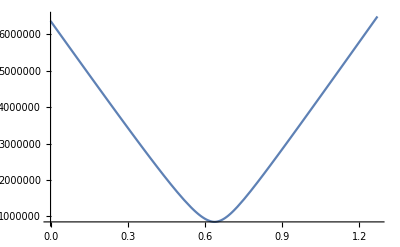

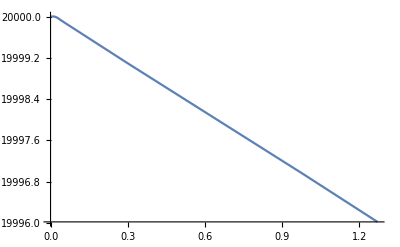

```mathematica
{ELfuncTotalbyκsquared,ELthroughEarthbyκsquared} = {"dEdlofr","ΔEthroughEarth"}/.GetTotalELFunction[ElectronicσDicts[[3]],NuclearσDicts[[3]]];

GetWeakCaptureTrajectoryinvRK2wPotential[10^9 ("JpereV")/("c")^2/.SIConstRepl,20 10^3,10^6,10^-11,ELfuncTotalbyκsquared,0&];
Plot["r(l)"[l]/.%,{l,0,1.27 10^7}]
Plot["v(l)"[l]/.%%,{l,0,1.27 10^7}]
```

```mathematica
GetCaptureProbability[10^-4,10^-11,20 10^3,ElectronicσDicts[[3]],NuclearσDicts[[3]],True,ϕmax[20 10^3]]
```

$Aborted

```mathematica
NuclearσDicts[[3]]
```

```mathematica
ScanGetCapture[ElectronicσDicts[[3;;3]],NuclearσDicts[[3;;3]],FeσDictend[[3;;3]],meDPoints[[1;;1]],κpoints[[1;;1]],v0Points[[1;;1]],1,"PDictList_test_ϕE_1"]
```

Part::pspec1: Part specification NotFound is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argt: ReplaceAll called with 4 arguments; 1 or 2 arguments are expected.

ReplaceAll::argt: ReplaceAll called with 3 arguments; 1 or 2 arguments are expected.

mχ must be the same in all processes:ReplaceAll[mχ,{{<|dσf→InterpolatingFunction[…],Interpoints→{{{40153.9,1.99054×10^-9},{40153.9,2.77917×10^-9},{40153.9,3.88024×10^-9},{40153.9,5.41756×10^-9},{40153.9,7.56393×10^-9},{40153.9,1.05607×10^-8},{40153.9,1.47447×10^-8},{40153.9,2.05864×10^-8},{40153.9,2.87426×10^-8},{40153.9,4.01301×10^-8},{40153.9,5.60292×10^-8},{40153.9,7.82274×10^-8},{40153.9,1.0922×10^-7},{40153.9,1.52492×10^-7},{40153.9,2.12908×10^-7},{40153.9,2.9726×10^-7},{40153.9,4.15031×10^-7},{40153.9,5.79462×10^-7},{40153.9,8.09039×10^-7},{40153.9,1.12957×10^-6},{40153.9,1.5771×10^-6},{40153.9,2.20193×10^-6},{40153.9,3.07431×10^-6},{40153.9,4.29232×10^-6},{40153.9,5.99289×10^-6},{40153.9,8.36721×10^-6},{40153.9,0.0000116822},{40153.9,0.0000163106},{40153.9,0.0000227727},{40153.9,0.000031795},{40153.9,0.0000443918},{40153.9,0.0000619794},{40153.9,0.0000865349},{40153.9,0.000120819},{40153.9,0.000168686},{40153.9,0.000235518},{40153.9,0.000328828},{40153.9,0.000459107},{40153.9,0.000641},{40153.9,0.000894957},{40153.9,0.00124953},{40153.9,0.00174458},{40153.9,0.00243577},{40153.9,0.00340079},{40153.9,0.00474815},{40153.9,0.00662932},{40153.9,0.00925579},{40153.9,0.0129228},{40153.9,0.0180427},{40153.9,0.0251911},{40153.9,0.0351715},{40153.9,0.0491061},{40153.9,0.0685614},{40153.9,0.0957248},{40153.9,0.13365},{40153.9,0.186601},{40153.9,0.26053},{40153.9,0.363749},{40153.9,0.507863},{40153.9,0.709073},{40153.9,0.99}},{{83400.7,1.99054×10^-9},{83400.7,2.77917×10^-9},{83400.7,3.88024×10^-9},{83400.7,5.41756×10^-9},{83400.7,7.56393×10^-9},{83400.7,1.05607×10^-8},{83400.7,1.47447×10^-8},{83400.7,2.05864×10^-8},{83400.7,2.87426×10^-8},{83400.7,4.01301×10^-8},{83400.7,5.60292×10^-8},{83400.7,7.82274×10^-8},{83400.7,1.0922×10^-7},{83400.7,1.52492×10^-7},{83400.7,2.12908×10^-7},{83400.7,2.9726×10^-7},{83400.7,4.15031×10^-7},{83400.7,5.79462×10^-7},{83400.7,8.09039×10^-7},{83400.7,1.12957×10^-6},{83400.7,1.5771×10^-6},{83400.7,2.20193×10^-6},{83400.7,3.07431×10^-6},{83400.7,4.29232×10^-6},{83400.7,5.99289×10^-6},{83400.7,8.36721×10^-6},{83400.7,0.0000116822},{83400.7,0.0000163106},{83400.7,0.0000227727},{83400.7,0.000031795},{83400.7,0.0000443918},{83400.7,0.0000619794},{83400.7,0.0000865349},{83400.7,0.000120819},{83400.7,0.000168686},{83400.7,0.000235518},{83400.7,0.000328828},{83400.7,0.000459107},{83400.7,0.000641},{83400.7,0.000894957},{83400.7,0.00124953},{83400.7,0.00174458},{83400.7,0.00243577},{83400.7,0.00340079},{83400.7,0.00474815},{83400.7,0.00662932},{83400.7,0.00925579},{83400.7,0.0129228},{83400.7,0.0180427},{83400.7,0.0251911},{83400.7,0.0351715},{83400.7,0.0491061},{83400.7,0.0685614},{83400.7,0.0957248},{83400.7,0.13365},{83400.7,0.186601},{83400.7,0.26053},{83400.7,0.363749},{83400.7,0.507863},{83400.7,0.709073},{83400.7,0.99}},{{173226.,1.99054×10^-9},{173226.,2.77917×10^-9},{173226.,3.88024×10^-9},{173226.,5.41756×10^-9},{173226.,7.56393×10^-9},{173226.,1.05607×10^-8},{173226.,1.47447×10^-8},{173226.,2.05864×10^-8},{173226.,2.87426×10^-8},{173226.,4.01301×10^-8},{173226.,5.60292×10^-8},{173226.,7.82274×10^-8},{173226.,1.0922×10^-7},{173226.,1.52492×10^-7},{173226.,2.12908×10^-7},{173226.,2.9726×10^-7},{173226.,4.15031×10^-7},{173226.,5.79462×10^-7},{173226.,8.09039×10^-7},{173226.,1.12957×10^-6},{173226.,1.5771×10^-6},{173226.,2.20193×10^-6},{173226.,3.07431×10^-6},{173226.,4.29232×10^-6},{173226.,5.99289×10^-6},{173226.,8.36721×10^-6},{173226.,0.0000116822},{173226.,0.0000163106},{173226.,0.0000227727},{173226.,0.000031795},{173226.,0.0000443918},{173226.,0.0000619794},{173226.,0.0000865349},{173226.,0.000120819},{173226.,0.000168686},{173226.,0.000235518},{173226.,0.000328828},{173226.,0.000459107},{173226.,0.000641},{173226.,0.000894957},{173226.,0.00124953},{173226.,0.00174458},{173226.,0.00243577},{173226.,0.00340079},{173226.,0.00474815},{173226.,0.00662932},{173226.,0.00925579},{173226.,0.0129228},{173226.,0.0180427},{173226.,0.0251911},{173226.,0.0351715},{173226.,0.0491061},{173226.,0.0685614},{173226.,0.0957248},{173226.,0.13365},{173226.,0.186601},{173226.,0.26053},{173226.,0.363749},{173226.,0.507863},{173226.,0.709073},{173226.,0.99}},{{359795.,1.99054×10^-9},{359795.,2.77917×10^-9},{359795.,3.88024×10^-9},{359795.,5.41756×10^-9},{359795.,7.56393×10^-9},{359795.,1.05607×10^-8},{359795.,1.47447×10^-8},{359795.,2.05864×10^-8},{359795.,2.87426×10^-8},{359795.,4.01301×10^-8},{359795.,5.60292×10^-8},{359795.,7.82274×10^-8},{359795.,1.0922×10^-7},{359795.,1.52492×10^-7},{359795.,2.12908×10^-7},{359795.,2.9726×10^-7},{359795.,4.15031×10^-7},{359795.,5.79462×10^-7},{359795.,8.09039×10^-7},{359795.,1.12957×10^-6},{359795.,1.5771×10^-6},{359795.,2.20193×10^-6},{359795.,3.07431×10^-6},{359795.,4.29232×10^-6},{359795.,5.99289×10^-6},{359795.,8.36721×10^-6},{359795.,0.0000116822},{359795.,0.0000163106},{359795.,0.0000227727},{359795.,0.000031795},{359795.,0.0000443918},{359795.,0.0000619794},{359795.,0.0000865349},{359795.,0.000120819},{359795.,0.000168686},{359795.,0.000235518},{359795.,0.000328828},{359795.,0.000459107},{359795.,0.000641},{359795.,0.000894957},{359795.,0.00124953},{359795.,0.00174458},{359795.,0.00243577},{359795.,0.00340079},{359795.,0.00474815},{359795.,0.00662932},{359795.,0.00925579},{359795.,0.0129228},{359795.,0.0180427},{359795.,0.0251911},{359795.,0.0351715},{359795.,0.0491061},{359795.,0.0685614},{359795.,0.0957248},{359795.,0.13365},{359795.,0.186601},{359795.,0.26053},{359795.,0.363749},{359795.,0.507863},{359795.,0.709073},{359795.,0.99}},{{747303.,1.99054×10^-9},{747303.,2.77917×10^-9},{747303.,3.88024×10^-9},{747303.,5.41756×10^-9},{747303.,7.56393×10^-9},{747303.,1.05607×10^-8},{747303.,1.47447×10^-8},{747303.,2.05864×10^-8},{747303.,2.87426×10^-8},{747303.,4.01301×10^-8},{747303.,5.60292×10^-8},{747303.,7.82274×10^-8},{747303.,1.0922×10^-7},{747303.,1.52492×10^-7},{747303.,2.12908×10^-7},{747303.,2.9726×10^-7},{747303.,4.15031×10^-7},{747303.,5.79462×10^-7},{747303.,8.09039×10^-7},{747303.,1.12957×10^-6},{747303.,1.5771×10^-6},{747303.,2.20193×10^-6},{747303.,3.07431×10^-6},{747303.,4.29232×10^-6},{747303.,5.99289×10^-6},{747303.,8.36721×10^-6},{747303.,0.0000116822},{747303.,0.0000163106},{747303.,0.0000227727},{747303.,0.000031795},{747303.,0.0000443918},{747303.,0.0000619794},{747303.,0.0000865349},{747303.,0.000120819},{747303.,0.000168686},{747303.,0.000235518},{747303.,0.000328828},{747303.,0.000459107},{747303.,0.000641},{747303.,0.000894957},{747303.,0.00124953},{747303.,0.00174458},{747303.,0.00243577},{747303.,0.00340079},{747303.,0.00474815},{747303.,0.00662932},{747303.,0.00925579},{747303.,0.0129228},{747303.,0.0180427},{747303.,0.0251911},{747303.,0.0351715},{747303.,0.0491061},{747303.,0.0685614},{747303.,0.0957248},{747303.,0.13365},{747303.,0.186601},{747303.,0.26053},{747303.,0.363749},{747303.,0.507863},{747303.,0.709073},{747303.,0.99}},{{1.55217×10^6,1.99054×10^-9},{1.55217×10^6,2.77917×10^-9},{1.55217×10^6,3.88024×10^-9},{1.55217×10^6,5.41756×10^-9},{1.55217×10^6,7.56393×10^-9},{1.55217×10^6,1.05607×10^-8},{1.55217×10^6,1.47447×10^-8},{1.55217×10^6,2.05864×10^-8},{1.55217×10^6,2.87426×10^-8},{1.55217×10^6,4.01301×10^-8},{1.55217×10^6,5.60292×10^-8},{1.55217×10^6,7.82274×10^-8},{1.55217×10^6,1.0922×10^-7},{1.55217×10^6,1.52492×10^-7},{1.55217×10^6,2.12908×10^-7},{1.55217×10^6,2.9726×10^-7},{1.55217×10^6,4.15031×10^-7},{1.55217×10^6,5.79462×10^-7},{1.55217×10^6,8.09039×10^-7},{1.55217×10^6,1.12957×10^-6},{1.55217×10^6,1.5771×10^-6},{1.55217×10^6,2.20193×10^-6},{1.55217×10^6,3.07431×10^-6},{1.55217×10^6,4.29232×10^-6},{1.55217×10^6,5.99289×10^-6},{1.55217×10^6,8.36721×10^-6},{1.55217×10^6,0.0000116822},{1.55217×10^6,0.0000163106},{1.55217×10^6,0.0000227727},{1.55217×10^6,0.000031795},{1.55217×10^6,0.0000443918},{1.55217×10^6,0.0000619794},{1.55217×10^6,0.0000865349},{1.55217×10^6,0.000120819},{1.55217×10^6,0.000168686},{1.55217×10^6,0.000235518},{1.55217×10^6,0.000328828},{1.55217×10^6,0.000459107},{1.55217×10^6,0.000641},{1.55217×10^6,0.000894957},{1.55217×10^6,0.00124953},{1.55217×10^6,0.00174458},{1.55217×10^6,0.00243577},{1.55217×10^6,0.00340079},{1.55217×10^6,0.00474815},{1.55217×10^6,0.00662932},{1.55217×10^6,0.00925579},{1.55217×10^6,0.0129228},{1.55217×10^6,0.0180427},{1.55217×10^6,0.0251911},{1.55217×10^6,0.0351715},{1.55217×10^6,0.0491061},{1.55217×10^6,0.0685614},{1.55217×10^6,0.0957248},{1.55217×10^6,0.13365},{1.55217×10^6,0.186601},{1.55217×10^6,0.26053},{1.55217×10^6,0.363749},{1.55217×10^6,0.507863},{1.55217×10^6,0.709073},{1.55217×10^6,0.99}},{{3.2239×10^6,1.99054×10^-9},{3.2239×10^6,2.77917×10^-9},{3.2239×10^6,3.88024×10^-9},{3.2239×10^6,5.41756×10^-9},{3.2239×10^6,7.56393×10^-9},{3.2239×10^6,1.05607×10^-8},{3.2239×10^6,1.47447×10^-8},{3.2239×10^6,2.05864×10^-8},{3.2239×10^6,2.87426×10^-8},{3.2239×10^6,4.01301×10^-8},{3.2239×10^6,5.60292×10^-8},{3.2239×10^6,7.82274×10^-8},{3.2239×10^6,1.0922×10^-7},{3.2239×10^6,1.52492×10^-7},{3.2239×10^6,2.12908×10^-7},{3.2239×10^6,2.9726×10^-7},{3.2239×10^6,4.15031×10^-7},{3.2239×10^6,5.79462×10^-7},{3.2239×10^6,8.09039×10^-7},{3.2239×10^6,1.12957×10^-6},{3.2239×10^6,1.5771×10^-6},{3.2239×10^6,2.20193×10^-6},{3.2239×10^6,3.07431×10^-6},{3.2239×10^6,4.29232×10^-6},{3.2239×10^6,5.99289×10^-6},{3.2239×10^6,8.36721×10^-6},{3.2239×10^6,0.0000116822},{3.2239×10^6,0.0000163106},{3.2239×10^6,0.0000227727},{3.2239×10^6,0.000031795},{3.2239×10^6,0.0000443918},{3.2239×10^6,0.0000619794},{3.2239×10^6,0.0000865349},{3.2239×10^6,0.000120819},{3.2239×10^6,0.000168686},{3.2239×10^6,0.000235518},{3.2239×10^6,0.000328828},{3.2239×10^6,0.000459107},{3.2239×10^6,0.000641},{3.2239×10^6,0.000894957},{3.2239×10^6,0.00124953},{3.2239×10^6,0.00174458},{3.2239×10^6,0.00243577},{3.2239×10^6,0.00340079},{3.2239×10^6,0.00474815},{3.2239×10^6,0.00662932},{3.2239×10^6,0.00925579},{3.2239×10^6,0.0129228},{3.2239×10^6,0.0180427},{3.2239×10^6,0.0251911},{3.2239×10^6,0.0351715},{3.2239×10^6,0.0491061},{3.2239×10^6,0.0685614},{3.2239×10^6,0.0957248},{3.2239×10^6,0.13365},{3.2239×10^6,0.186601},{3.2239×10^6,0.26053},{3.2239×10^6,0.363749},{3.2239×10^6,0.507863},{3.2239×10^6,0.709073},{3.2239×10^6,0.99}},{{6.69613×10^6,1.99054×10^-9},{6.69613×10^6,2.77917×10^-9},{6.69613×10^6,3.88024×10^-9},{6.69613×10^6,5.41756×10^-9},{6.69613×10^6,7.56393×10^-9},{6.69613×10^6,1.05607×10^-8},{6.69613×10^6,1.47447×10^-8},{6.69613×10^6,2.05864×10^-8},{6.69613×10^6,2.87426×10^-8},{6.69613×10^6,4.01301×10^-8},{6.69613×10^6,5.60292×10^-8},{6.69613×10^6,7.82274×10^-8},{6.69613×10^6,1.0922×10^-7},{6.69613×10^6,1.52492×10^-7},{6.69613×10^6,2.12908×10^-7},{6.69613×10^6,2.9726×10^-7},{6.69613×10^6,4.15031×10^-7},{6.69613×10^6,5.79462×10^-7},{6.69613×10^6,8.09039×10^-7},{6.69613×10^6,1.12957×10^-6},{6.69613×10^6,1.5771×10^-6},{6.69613×10^6,2.20193×10^-6},{6.69613×10^6,3.07431×10^-6},{6.69613×10^6,4.29232×10^-6},{6.69613×10^6,5.99289×10^-6},{6.69613×10^6,8.36721×10^-6},{6.69613×10^6,0.0000116822},{6.69613×10^6,0.0000163106},{6.69613×10^6,0.0000227727},{6.69613×10^6,0.000031795},{6.69613×10^6,0.0000443918},{6.69613×10^6,0.0000619794},{6.69613×10^6,0.0000865349},{6.69613×10^6,0.000120819},{6.69613×10^6,0.000168686},{6.69613×10^6,0.000235518},{6.69613×10^6,0.000328828},{6.69613×10^6,0.000459107},{6.69613×10^6,0.000641},{6.69613×10^6,0.000894957},{6.69613×10^6,0.00124953},{6.69613×10^6,0.00174458},{6.69613×10^6,0.00243577},{6.69613×10^6,0.00340079},{6.69613×10^6,0.00474815},{6.69613×10^6,0.00662932},{6.69613×10^6,0.00925579},{6.69613×10^6,0.0129228},{6.69613×10^6,0.0180427},{6.69613×10^6,0.0251911},{6.69613×10^6,0.0351715},{6.69613×10^6,0.0491061},{6.69613×10^6,0.0685614},{6.69613×10^6,0.0957248},{6.69613×10^6,0.13365},{6.69613×10^6,0.186601},{6.69613×10^6,0.26053},{6.69613×10^6,0.363749},{6.69613×10^6,0.507863},{6.69613×10^6,0.709073},{6.69613×10^6,0.99}},{{1.39081×10^7,1.99054×10^-9},{1.39081×10^7,2.77917×10^-9},{1.39081×10^7,3.88024×10^-9},{1.39081×10^7,5.41756×10^-9},{1.39081×10^7,7.56393×10^-9},{1.39081×10^7,1.05607×10^-8},{1.39081×10^7,1.47447×10^-8},{1.39081×10^7,2.05864×10^-8},{1.39081×10^7,2.87426×10^-8},{1.39081×10^7,4.01301×10^-8},{1.39081×10^7,5.60292×10^-8},{1.39081×10^7,7.82274×10^-8},{1.39081×10^7,1.0922×10^-7},{1.39081×10^7,1.52492×10^-7},{1.39081×10^7,2.12908×10^-7},{1.39081×10^7,2.9726×10^-7},{1.39081×10^7,4.15031×10^-7},{1.39081×10^7,5.79462×10^-7},{1.39081×10^7,8.09039×10^-7},{1.39081×10^7,1.12957×10^-6},{1.39081×10^7,1.5771×10^-6},{1.39081×10^7,2.20193×10^-6},{1.39081×10^7,3.07431×10^-6},{1.39081×10^7,4.29232×10^-6},{1.39081×10^7,5.99289×10^-6},{1.39081×10^7,8.36721×10^-6},{1.39081×10^7,0.0000116822},{1.39081×10^7,0.0000163106},{1.39081×10^7,0.0000227727},{1.39081×10^7,0.000031795},{1.39081×10^7,0.0000443918},{1.39081×10^7,0.0000619794},{1.39081×10^7,0.0000865349},{1.39081×10^7,0.000120819},{1.39081×10^7,0.000168686},{1.39081×10^7,0.000235518},{1.39081×10^7,0.000328828},{1.39081×10^7,0.000459107},{1.39081×10^7,0.000641},{1.39081×10^7,0.000894957},{1.39081×10^7,0.00124953},{1.39081×10^7,0.00174458},{1.39081×10^7,0.00243577},{1.39081×10^7,0.00340079},{1.39081×10^7,0.00474815},{1.39081×10^7,0.00662932},{1.39081×10^7,0.00925579},{1.39081×10^7,0.0129228},{1.39081×10^7,0.0180427},{1.39081×10^7,0.0251911},{1.39081×10^7,0.0351715},{1.39081×10^7,0.0491061},{1.39081×10^7,0.0685614},{1.39081×10^7,0.0957248},{1.39081×10^7,0.13365},{1.39081×10^7,0.186601},{1.39081×10^7,0.26053},{1.39081×10^7,0.363749},{1.39081×10^7,0.507863},{1.39081×10^7,0.709073},{1.39081×10^7,0.99}},{{2.88874×10^7,1.99054×10^-9},{2.88874×10^7,2.77917×10^-9},{2.88874×10^7,3.88024×10^-9},{2.88874×10^7,5.41756×10^-9},{2.88874×10^7,7.56393×10^-9},{2.88874×10^7,1.05607×10^-8},{2.88874×10^7,1.47447×10^-8},{2.88874×10^7,2.05864×10^-8},{2.88874×10^7,2.87426×10^-8},{2.88874×10^7,4.01301×10^-8},{2.88874×10^7,5.60292×10^-8},{2.88874×10^7,7.82274×10^-8},{2.88874×10^7,1.0922×10^-7},{2.88874×10^7,1.52492×10^-7},{2.88874×10^7,2.12908×10^-7},{2.88874×10^7,2.9726×10^-7},{2.88874×10^7,4.15031×10^-7},{2.88874×10^7,5.79462×10^-7},{2.88874×10^7,8.09039×10^-7},{2.88874×10^7,1.12957×10^-6},{2.88874×10^7,1.5771×10^-6},{2.88874×10^7,2.20193×10^-6},{2.88874×10^7,3.07431×10^-6},{2.88874×10^7,4.29232×10^-6},{2.88874×10^7,5.99289×10^-6},{2.88874×10^7,8.36721×10^-6},{2.88874×10^7,0.0000116822},{2.88874×10^7,0.0000163106},{2.88874×10^7,0.0000227727},{2.88874×10^7,0.000031795},{2.88874×10^7,0.0000443918},{2.88874×10^7,0.0000619794},{2.88874×10^7,0.0000865349},{2.88874×10^7,0.000120819},{2.88874×10^7,0.000168686},{2.88874×10^7,0.000235518},{2.88874×10^7,0.000328828},{2.88874×10^7,0.000459107},{2.88874×10^7,0.000641},{2.88874×10^7,0.000894957},{2.88874×10^7,0.00124953},{2.88874×10^7,0.00174458},{2.88874×10^7,0.00243577},{2.88874×10^7,0.00340079},{2.88874×10^7,0.00474815},{2.88874×10^7,0.00662932},{2.88874×10^7,0.00925579},{2.88874×10^7,0.0129228},{2.88874×10^7,0.0180427},{2.88874×10^7,0.0251911},{2.88874×10^7,0.0351715},{2.88874×10^7,0.0491061},{2.88874×10^7,0.0685614},{2.88874×10^7,0.0957248},{2.88874×10^7,0.13365},{2.88874×10^7,0.186601},{2.88874×10^7,0.26053},{2.88874×10^7,0.363749},{2.88874×10^7,0.507863},{2.88874×10^7,0.709073},{2.88874×10^7,0.99}},{{6.×10^7,1.99054×10^-9},{6.×10^7,2.77917×10^-9},{6.×10^7,3.88024×10^-9},{6.×10^7,5.41756×10^-9},{6.×10^7,7.56393×10^-9},{6.×10^7,1.05607×10^-8},{6.×10^7,1.47447×10^-8},{6.×10^7,2.05864×10^-8},{6.×10^7,2.87426×10^-8},{6.×10^7,4.01301×10^-8},{6.×10^7,5.60292×10^-8},{6.×10^7,7.82274×10^-8},{6.×10^7,1.0922×10^-7},{6.×10^7,1.52492×10^-7},{6.×10^7,2.12908×10^-7},{6.×10^7,2.9726×10^-7},{6.×10^7,4.15031×10^-7},{6.×10^7,5.79462×10^-7},{6.×10^7,8.09039×10^-7},{6.×10^7,1.12957×10^-6},{6.×10^7,1.5771×10^-6},{6.×10^7,2.20193×10^-6},{6.×10^7,3.07431×10^-6},{6.×10^7,4.29232×10^-6},{6.×10^7,5.99289×10^-6},{6.×10^7,8.36721×10^-6},{6.×10^7,0.0000116822},{6.×10^7,0.0000163106},{6.×10^7,0.0000227727},{6.×10^7,0.000031795},{6.×10^7,0.0000443918},{6.×10^7,0.0000619794},{6.×10^7,0.0000865349},{6.×10^7,0.000120819},{6.×10^7,0.000168686},{6.×10^7,0.000235518},{6.×10^7,0.000328828},{6.×10^7,0.000459107},{6.×10^7,0.000641},{6.×10^7,0.000894957},{6.×10^7,0.00124953},{6.×10^7,0.00174458},{6.×10^7,0.00243577},{6.×10^7,0.00340079},{6.×10^7,0.00474815},{6.×10^7,0.00662932},{6.×10^7,0.00925579},{6.×10^7,0.0129228},{6.×10^7,0.0180427},{6.×10^7,0.0251911},{6.×10^7,0.0351715},{6.×10^7,0.0491061},{6.×10^7,0.0685614},{6.×10^7,0.0957248},{6.×10^7,0.13365},{6.×10^7,0.186601},{6.×10^7,0.26053},{6.×10^7,0.363749},{6.×10^7,0.507863},{6.×10^7,0.709073},{6.×10^7,0.99}}},Interpointsvχ→{40153.9,83400.7,173226.,359795.,747303.,1.55217×10^6,3.2239×10^6,6.69613×10^6,1.39081×10^7,2.88874×10^7,6.×10^7},σf→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],σofξf→InterpolatingFunction[…],mχ→1.78×10^-28,vχ→{4.60373,Log[60000000]/Log[10]},ξ→{-8.70103,-0.00436481},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→17.0944,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},ωmin→6.04519×10^14,regionindex→2,materialname→Fe 1|>,<|dσf→InterpolatingFunction[…],Interpoints→{{{4192.01,2.1695×10^-11},{4192.01,3.26599×10^-11},{4192.01,4.91664×10^-11},{4192.01,7.40156×10^-11},{4192.01,1.11424×10^-10},{4192.01,1.67738×10^-10},{4192.01,2.52515×10^-10},{4192.01,3.80138×10^-10},{4192.01,5.72264×10^-10},{4192.01,8.61491×10^-10},{4192.01,1.2969×10^-9},{4192.01,1.95236×10^-9},{4192.01,2.9391×10^-9},{4192.01,4.42455×10^-9},{4192.01,6.66076×10^-9},{4192.01,1.00272×10^-8},{4192.01,1.5095×10^-8},{4192.01,2.27242×10^-8},{4192.01,3.42092×10^-8},{4192.01,5.14988×10^-8},{4192.01,7.75267×10^-8},{4192.01,1.16709×10^-7},{4192.01,1.75696×10^-7},{4192.01,2.64494×10^-7},{4192.01,3.98171×10^-7},{4192.01,5.99411×10^-7},{4192.01,9.02358×10^-7},{4192.01,1.35842×10^-6},{4192.01,2.04498×10^-6},{4192.01,3.07853×10^-6},{4192.01,4.63444×10^-6},{4192.01,6.97673×10^-6},{4192.01,0.0000105028},{4192.01,0.0000158111},{4192.01,0.0000238021},{4192.01,0.0000358319},{4192.01,0.0000539417},{4192.01,0.0000812044},{4192.01,0.000122246},{4192.01,0.00018403},{4192.01,0.000277041},{4192.01,0.000417059},{4192.01,0.000627845},{4192.01,0.000945164},{4192.01,0.00142286},{4192.01,0.00214198},{4192.01,0.00322456},{4192.01,0.00485429},{4192.01,0.00730769},{4192.01,0.0110011},{4192.01,0.0165611},{4192.01,0.0249312},{4192.01,0.0375317},{4192.01,0.0565006},{4192.01,0.0850565},{4192.01,0.128045},{4192.01,0.19276},{4192.01,0.290183},{4192.01,0.436844},{4192.01,0.657628},{4192.01,0.99}},{{10914.3,2.1695×10^-11},{10914.3,3.26599×10^-11},{10914.3,4.91664×10^-11},{10914.3,7.40156×10^-11},{10914.3,1.11424×10^-10},{10914.3,1.67738×10^-10},{10914.3,2.52515×10^-10},{10914.3,3.80138×10^-10},{10914.3,5.72264×10^-10},{10914.3,8.61491×10^-10},{10914.3,1.2969×10^-9},{10914.3,1.95236×10^-9},{10914.3,2.9391×10^-9},{10914.3,4.42455×10^-9},{10914.3,6.66076×10^-9},{10914.3,1.00272×10^-8},{10914.3,1.5095×10^-8},{10914.3,2.27242×10^-8},{10914.3,3.42092×10^-8},{10914.3,5.14988×10^-8},{10914.3,7.75267×10^-8},{10914.3,1.16709×10^-7},{10914.3,1.75696×10^-7},{10914.3,2.64494×10^-7},{10914.3,3.98171×10^-7},{10914.3,5.99411×10^-7},{10914.3,9.02358×10^-7},{10914.3,1.35842×10^-6},{10914.3,2.04498×10^-6},{10914.3,3.07853×10^-6},{10914.3,4.63444×10^-6},{10914.3,6.97673×10^-6},{10914.3,0.0000105028},{10914.3,0.0000158111},{10914.3,0.0000238021},{10914.3,0.0000358319},{10914.3,0.0000539417},{10914.3,0.0000812044},{10914.3,0.000122246},{10914.3,0.00018403},{10914.3,0.000277041},{10914.3,0.000417059},{10914.3,0.000627845},{10914.3,0.000945164},{10914.3,0.00142286},{10914.3,0.00214198},{10914.3,0.00322456},{10914.3,0.00485429},{10914.3,0.00730769},{10914.3,0.0110011},{10914.3,0.0165611},{10914.3,0.0249312},{10914.3,0.0375317},{10914.3,0.0565006},{10914.3,0.0850565},{10914.3,0.128045},{10914.3,0.19276},{10914.3,0.290183},{10914.3,0.436844},{10914.3,0.657628},{10914.3,0.99}},{{28416.3,2.1695×10^-11},{28416.3,3.26599×10^-11},{28416.3,4.91664×10^-11},{28416.3,7.40156×10^-11},{28416.3,1.11424×10^-10},{28416.3,1.67738×10^-10},{28416.3,2.52515×10^-10},{28416.3,3.80138×10^-10},{28416.3,5.72264×10^-10},{28416.3,8.61491×10^-10},{28416.3,1.2969×10^-9},{28416.3,1.95236×10^-9},{28416.3,2.9391×10^-9},{28416.3,4.42455×10^-9},{28416.3,6.66076×10^-9},{28416.3,1.00272×10^-8},{28416.3,1.5095×10^-8},{28416.3,2.27242×10^-8},{28416.3,3.42092×10^-8},{28416.3,5.14988×10^-8},{28416.3,7.75267×10^-8},{28416.3,1.16709×10^-7},{28416.3,1.75696×10^-7},{28416.3,2.64494×10^-7},{28416.3,3.98171×10^-7},{28416.3,5.99411×10^-7},{28416.3,9.02358×10^-7},{28416.3,1.35842×10^-6},{28416.3,2.04498×10^-6},{28416.3,3.07853×10^-6},{28416.3,4.63444×10^-6},{28416.3,6.97673×10^-6},{28416.3,0.0000105028},{28416.3,0.0000158111},{28416.3,0.0000238021},{28416.3,0.0000358319},{28416.3,0.0000539417},{28416.3,0.0000812044},{28416.3,0.000122246},{28416.3,0.00018403},{28416.3,0.000277041},{28416.3,0.000417059},{28416.3,0.000627845},{28416.3,0.000945164},{28416.3,0.00142286},{28416.3,0.00214198},{28416.3,0.00322456},{28416.3,0.00485429},{28416.3,0.00730769},{28416.3,0.0110011},{28416.3,0.0165611},{28416.3,0.0249312},{28416.3,0.0375317},{28416.3,0.0565006},{28416.3,0.0850565},{28416.3,0.128045},{28416.3,0.19276},{28416.3,0.290183},{28416.3,0.436844},{28416.3,0.657628},{28416.3,0.99}},{{73984.5,2.1695×10^-11},{73984.5,3.26599×10^-11},{73984.5,4.91664×10^-11},{73984.5,7.40156×10^-11},{73984.5,1.11424×10^-10},{73984.5,1.67738×10^-10},{73984.5,2.52515×10^-10},{73984.5,3.80138×10^-10},{73984.5,5.72264×10^-10},{73984.5,8.61491×10^-10},{73984.5,1.2969×10^-9},{73984.5,1.95236×10^-9},{73984.5,2.9391×10^-9},{73984.5,4.42455×10^-9},{73984.5,6.66076×10^-9},{73984.5,1.00272×10^-8},{73984.5,1.5095×10^-8},{73984.5,2.27242×10^-8},{73984.5,3.42092×10^-8},{73984.5,5.14988×10^-8},{73984.5,7.75267×10^-8},{73984.5,1.16709×10^-7},{73984.5,1.75696×10^-7},{73984.5,2.64494×10^-7},{73984.5,3.98171×10^-7},{73984.5,5.99411×10^-7},{73984.5,9.02358×10^-7},{73984.5,1.35842×10^-6},{73984.5,2.04498×10^-6},{73984.5,3.07853×10^-6},{73984.5,4.63444×10^-6},{73984.5,6.97673×10^-6},{73984.5,0.0000105028},{73984.5,0.0000158111},{73984.5,0.0000238021},{73984.5,0.0000358319},{73984.5,0.0000539417},{73984.5,0.0000812044},{73984.5,0.000122246},{73984.5,0.00018403},{73984.5,0.000277041},{73984.5,0.000417059},{73984.5,0.000627845},{73984.5,0.000945164},{73984.5,0.00142286},{73984.5,0.00214198},{73984.5,0.00322456},{73984.5,0.00485429},{73984.5,0.00730769},{73984.5,0.0110011},{73984.5,0.0165611},{73984.5,0.0249312},{73984.5,0.0375317},{73984.5,0.0565006},{73984.5,0.0850565},{73984.5,0.128045},{73984.5,0.19276},{73984.5,0.290183},{73984.5,0.436844},{73984.5,0.657628},{73984.5,0.99}},{{192626.,2.1695×10^-11},{192626.,3.26599×10^-11},{192626.,4.91664×10^-11},{192626.,7.40156×10^-11},{192626.,1.11424×10^-10},{192626.,1.67738×10^-10},{192626.,2.52515×10^-10},{192626.,3.80138×10^-10},{192626.,5.72264×10^-10},{192626.,8.61491×10^-10},{192626.,1.2969×10^-9},{192626.,1.95236×10^-9},{192626.,2.9391×10^-9},{192626.,4.42455×10^-9},{192626.,6.66076×10^-9},{192626.,1.00272×10^-8},{192626.,1.5095×10^-8},{192626.,2.27242×10^-8},{192626.,3.42092×10^-8},{192626.,5.14988×10^-8},{192626.,7.75267×10^-8},{192626.,1.16709×10^-7},{192626.,1.75696×10^-7},{192626.,2.64494×10^-7},{192626.,3.98171×10^-7},{192626.,5.99411×10^-7},{192626.,9.02358×10^-7},{192626.,1.35842×10^-6},{192626.,2.04498×10^-6},{192626.,3.07853×10^-6},{192626.,4.63444×10^-6},{192626.,6.97673×10^-6},{192626.,0.0000105028},{192626.,0.0000158111},{192626.,0.0000238021},{192626.,0.0000358319},{192626.,0.0000539417},{192626.,0.0000812044},{192626.,0.000122246},{192626.,0.00018403},{192626.,0.000277041},{192626.,0.000417059},{192626.,0.000627845},{192626.,0.000945164},{192626.,0.00142286},{192626.,0.00214198},{192626.,0.00322456},{192626.,0.00485429},{192626.,0.00730769},{192626.,0.0110011},{192626.,0.0165611},{192626.,0.0249312},{192626.,0.0375317},{192626.,0.0565006},{192626.,0.0850565},{192626.,0.128045},{192626.,0.19276},{192626.,0.290183},{192626.,0.436844},{192626.,0.657628},{192626.,0.99}},{{501518.,2.1695×10^-11},{501518.,3.26599×10^-11},{501518.,4.91664×10^-11},{501518.,7.40156×10^-11},{501518.,1.11424×10^-10},{501518.,1.67738×10^-10},{501518.,2.52515×10^-10},{501518.,3.80138×10^-10},{501518.,5.72264×10^-10},{501518.,8.61491×10^-10},{501518.,1.2969×10^-9},{501518.,1.95236×10^-9},{501518.,2.9391×10^-9},{501518.,4.42455×10^-9},{501518.,6.66076×10^-9},{501518.,1.00272×10^-8},{501518.,1.5095×10^-8},{501518.,2.27242×10^-8},{501518.,3.42092×10^-8},{501518.,5.14988×10^-8},{501518.,7.75267×10^-8},{501518.,1.16709×10^-7},{501518.,1.75696×10^-7},{501518.,2.64494×10^-7},{501518.,3.98171×10^-7},{501518.,5.99411×10^-7},{501518.,9.02358×10^-7},{501518.,1.35842×10^-6},{501518.,2.04498×10^-6},{501518.,3.07853×10^-6},{501518.,4.63444×10^-6},{501518.,6.97673×10^-6},{501518.,0.0000105028},{501518.,0.0000158111},{501518.,0.0000238021},{501518.,0.0000358319},{501518.,0.0000539417},{501518.,0.0000812044},{501518.,0.000122246},{501518.,0.00018403},{501518.,0.000277041},{501518.,0.000417059},{501518.,0.000627845},{501518.,0.000945164},{501518.,0.00142286},{501518.,0.00214198},{501518.,0.00322456},{501518.,0.00485429},{501518.,0.00730769},{501518.,0.0110011},{501518.,0.0165611},{501518.,0.0249312},{501518.,0.0375317},{501518.,0.0565006},{501518.,0.0850565},{501518.,0.128045},{501518.,0.19276},{501518.,0.290183},{501518.,0.436844},{501518.,0.657628},{501518.,0.99}},{{1.30575×10^6,2.1695×10^-11},{1.30575×10^6,3.26599×10^-11},{1.30575×10^6,4.91664×10^-11},{1.30575×10^6,7.40156×10^-11},{1.30575×10^6,1.11424×10^-10},{1.30575×10^6,1.67738×10^-10},{1.30575×10^6,2.52515×10^-10},{1.30575×10^6,3.80138×10^-10},{1.30575×10^6,5.72264×10^-10},{1.30575×10^6,8.61491×10^-10},{1.30575×10^6,1.2969×10^-9},{1.30575×10^6,1.95236×10^-9},{1.30575×10^6,2.9391×10^-9},{1.30575×10^6,4.42455×10^-9},{1.30575×10^6,6.66076×10^-9},{1.30575×10^6,1.00272×10^-8},{1.30575×10^6,1.5095×10^-8},{1.30575×10^6,2.27242×10^-8},{1.30575×10^6,3.42092×10^-8},{1.30575×10^6,5.14988×10^-8},{1.30575×10^6,7.75267×10^-8},{1.30575×10^6,1.16709×10^-7},{1.30575×10^6,1.75696×10^-7},{1.30575×10^6,2.64494×10^-7},{1.30575×10^6,3.98171×10^-7},{1.30575×10^6,5.99411×10^-7},{1.30575×10^6,9.02358×10^-7},{1.30575×10^6,1.35842×10^-6},{1.30575×10^6,2.04498×10^-6},{1.30575×10^6,3.07853×10^-6},{1.30575×10^6,4.63444×10^-6},{1.30575×10^6,6.97673×10^-6},{1.30575×10^6,0.0000105028},{1.30575×10^6,0.0000158111},{1.30575×10^6,0.0000238021},{1.30575×10^6,0.0000358319},{1.30575×10^6,0.0000539417},{1.30575×10^6,0.0000812044},{1.30575×10^6,0.000122246},{1.30575×10^6,0.00018403},{1.30575×10^6,0.000277041},{1.30575×10^6,0.000417059},{1.30575×10^6,0.000627845},{1.30575×10^6,0.000945164},{1.30575×10^6,0.00142286},{1.30575×10^6,0.00214198},{1.30575×10^6,0.00322456},{1.30575×10^6,0.00485429},{1.30575×10^6,0.00730769},{1.30575×10^6,0.0110011},{1.30575×10^6,0.0165611},{1.30575×10^6,0.0249312},{1.30575×10^6,0.0375317},{1.30575×10^6,0.0565006},{1.30575×10^6,0.0850565},{1.30575×10^6,0.128045},{1.30575×10^6,0.19276},{1.30575×10^6,0.290183},{1.30575×10^6,0.436844},{1.30575×10^6,0.657628},{1.30575×10^6,0.99}},{{3.39964×10^6,2.1695×10^-11},{3.39964×10^6,3.26599×10^-11},{3.39964×10^6,4.91664×10^-11},{3.39964×10^6,7.40156×10^-11},{3.39964×10^6,1.11424×10^-10},{3.39964×10^6,1.67738×10^-10},{3.39964×10^6,2.52515×10^-10},{3.39964×10^6,3.80138×10^-10},{3.39964×10^6,5.72264×10^-10},{3.39964×10^6,8.61491×10^-10},{3.39964×10^6,1.2969×10^-9},{3.39964×10^6,1.95236×10^-9},{3.39964×10^6,2.9391×10^-9},{3.39964×10^6,4.42455×10^-9},{3.39964×10^6,6.66076×10^-9},{3.39964×10^6,1.00272×10^-8},{3.39964×10^6,1.5095×10^-8},{3.39964×10^6,2.27242×10^-8},{3.39964×10^6,3.42092×10^-8},{3.39964×10^6,5.14988×10^-8},{3.39964×10^6,7.75267×10^-8},{3.39964×10^6,1.16709×10^-7},{3.39964×10^6,1.75696×10^-7},{3.39964×10^6,2.64494×10^-7},{3.39964×10^6,3.98171×10^-7},{3.39964×10^6,5.99411×10^-7},{3.39964×10^6,9.02358×10^-7},{3.39964×10^6,1.35842×10^-6},{3.39964×10^6,2.04498×10^-6},{3.39964×10^6,3.07853×10^-6},{3.39964×10^6,4.63444×10^-6},{3.39964×10^6,6.97673×10^-6},{3.39964×10^6,0.0000105028},{3.39964×10^6,0.0000158111},{3.39964×10^6,0.0000238021},{3.39964×10^6,0.0000358319},{3.39964×10^6,0.0000539417},{3.39964×10^6,0.0000812044},{3.39964×10^6,0.000122246},{3.39964×10^6,0.00018403},{3.39964×10^6,0.000277041},{3.39964×10^6,0.000417059},{3.39964×10^6,0.000627845},{3.39964×10^6,0.000945164},{3.39964×10^6,0.00142286},{3.39964×10^6,0.00214198},{3.39964×10^6,0.00322456},{3.39964×10^6,0.00485429},{3.39964×10^6,0.00730769},{3.39964×10^6,0.0110011},{3.39964×10^6,0.0165611},{3.39964×10^6,0.0249312},{3.39964×10^6,0.0375317},{3.39964×10^6,0.0565006},{3.39964×10^6,0.0850565},{3.39964×10^6,0.128045},{3.39964×10^6,0.19276},{3.39964×10^6,0.290183},{3.39964×10^6,0.436844},{3.39964×10^6,0.657628},{3.39964×10^6,0.99}},{{8.85127×10^6,2.1695×10^-11},{8.85127×10^6,3.26599×10^-11},{8.85127×10^6,4.91664×10^-11},{8.85127×10^6,7.40156×10^-11},{8.85127×10^6,1.11424×10^-10},{8.85127×10^6,1.67738×10^-10},{8.85127×10^6,2.52515×10^-10},{8.85127×10^6,3.80138×10^-10},{8.85127×10^6,5.72264×10^-10},{8.85127×10^6,8.61491×10^-10},{8.85127×10^6,1.2969×10^-9},{8.85127×10^6,1.95236×10^-9},{8.85127×10^6,2.9391×10^-9},{8.85127×10^6,4.42455×10^-9},{8.85127×10^6,6.66076×10^-9},{8.85127×10^6,1.00272×10^-8},{8.85127×10^6,1.5095×10^-8},{8.85127×10^6,2.27242×10^-8},{8.85127×10^6,3.42092×10^-8},{8.85127×10^6,5.14988×10^-8},{8.85127×10^6,7.75267×10^-8},{8.85127×10^6,1.16709×10^-7},{8.85127×10^6,1.75696×10^-7},{8.85127×10^6,2.64494×10^-7},{8.85127×10^6,3.98171×10^-7},{8.85127×10^6,5.99411×10^-7},{8.85127×10^6,9.02358×10^-7},{8.85127×10^6,1.35842×10^-6},{8.85127×10^6,2.04498×10^-6},{8.85127×10^6,3.07853×10^-6},{8.85127×10^6,4.63444×10^-6},{8.85127×10^6,6.97673×10^-6},{8.85127×10^6,0.0000105028},{8.85127×10^6,0.0000158111},{8.85127×10^6,0.0000238021},{8.85127×10^6,0.0000358319},{8.85127×10^6,0.0000539417},{8.85127×10^6,0.0000812044},{8.85127×10^6,0.000122246},{8.85127×10^6,0.00018403},{8.85127×10^6,0.000277041},{8.85127×10^6,0.000417059},{8.85127×10^6,0.000627845},{8.85127×10^6,0.000945164},{8.85127×10^6,0.00142286},{8.85127×10^6,0.00214198},{8.85127×10^6,0.00322456},{8.85127×10^6,0.00485429},{8.85127×10^6,0.00730769},{8.85127×10^6,0.0110011},{8.85127×10^6,0.0165611},{8.85127×10^6,0.0249312},{8.85127×10^6,0.0375317},{8.85127×10^6,0.0565006},{8.85127×10^6,0.0850565},{8.85127×10^6,0.128045},{8.85127×10^6,0.19276},{8.85127×10^6,0.290183},{8.85127×10^6,0.436844},{8.85127×10^6,0.657628},{8.85127×10^6,0.99}},{{2.30451×10^7,2.1695×10^-11},{2.30451×10^7,3.26599×10^-11},{2.30451×10^7,4.91664×10^-11},{2.30451×10^7,7.40156×10^-11},{2.30451×10^7,1.11424×10^-10},{2.30451×10^7,1.67738×10^-10},{2.30451×10^7,2.52515×10^-10},{2.30451×10^7,3.80138×10^-10},{2.30451×10^7,5.72264×10^-10},{2.30451×10^7,8.61491×10^-10},{2.30451×10^7,1.2969×10^-9},{2.30451×10^7,1.95236×10^-9},{2.30451×10^7,2.9391×10^-9},{2.30451×10^7,4.42455×10^-9},{2.30451×10^7,6.66076×10^-9},{2.30451×10^7,1.00272×10^-8},{2.30451×10^7,1.5095×10^-8},{2.30451×10^7,2.27242×10^-8},{2.30451×10^7,3.42092×10^-8},{2.30451×10^7,5.14988×10^-8},{2.30451×10^7,7.75267×10^-8},{2.30451×10^7,1.16709×10^-7},{2.30451×10^7,1.75696×10^-7},{2.30451×10^7,2.64494×10^-7},{2.30451×10^7,3.98171×10^-7},{2.30451×10^7,5.99411×10^-7},{2.30451×10^7,9.02358×10^-7},{2.30451×10^7,1.35842×10^-6},{2.30451×10^7,2.04498×10^-6},{2.30451×10^7,3.07853×10^-6},{2.30451×10^7,4.63444×10^-6},{2.30451×10^7,6.97673×10^-6},{2.30451×10^7,0.0000105028},{2.30451×10^7,0.0000158111},{2.30451×10^7,0.0000238021},{2.30451×10^7,0.0000358319},{2.30451×10^7,0.0000539417},{2.30451×10^7,0.0000812044},{2.30451×10^7,0.000122246},{2.30451×10^7,0.00018403},{2.30451×10^7,0.000277041},{2.30451×10^7,0.000417059},{2.30451×10^7,0.000627845},{2.30451×10^7,0.000945164},{2.30451×10^7,0.00142286},{2.30451×10^7,0.00214198},{2.30451×10^7,0.00322456},{2.30451×10^7,0.00485429},{2.30451×10^7,0.00730769},{2.30451×10^7,0.0110011},{2.30451×10^7,0.0165611},{2.30451×10^7,0.0249312},{2.30451×10^7,0.0375317},{2.30451×10^7,0.0565006},{2.30451×10^7,0.0850565},{2.30451×10^7,0.128045},{2.30451×10^7,0.19276},{2.30451×10^7,0.290183},{2.30451×10^7,0.436844},{2.30451×10^7,0.657628},{2.30451×10^7,0.99}},{{6.×10^7,2.1695×10^-11},{6.×10^7,3.26599×10^-11},{6.×10^7,4.91664×10^-11},{6.×10^7,7.40156×10^-11},{6.×10^7,1.11424×10^-10},{6.×10^7,1.67738×10^-10},{6.×10^7,2.52515×10^-10},{6.×10^7,3.80138×10^-10},{6.×10^7,5.72264×10^-10},{6.×10^7,8.61491×10^-10},{6.×10^7,1.2969×10^-9},{6.×10^7,1.95236×10^-9},{6.×10^7,2.9391×10^-9},{6.×10^7,4.42455×10^-9},{6.×10^7,6.66076×10^-9},{6.×10^7,1.00272×10^-8},{6.×10^7,1.5095×10^-8},{6.×10^7,2.27242×10^-8},{6.×10^7,3.42092×10^-8},{6.×10^7,5.14988×10^-8},{6.×10^7,7.75267×10^-8},{6.×10^7,1.16709×10^-7},{6.×10^7,1.75696×10^-7},{6.×10^7,2.64494×10^-7},{6.×10^7,3.98171×10^-7},{6.×10^7,5.99411×10^-7},{6.×10^7,9.02358×10^-7},{6.×10^7,1.35842×10^-6},{6.×10^7,2.04498×10^-6},{6.×10^7,3.07853×10^-6},{6.×10^7,4.63444×10^-6},{6.×10^7,6.97673×10^-6},{6.×10^7,0.0000105028},{6.×10^7,0.0000158111},{6.×10^7,0.0000238021},{6.×10^7,0.0000358319},{6.×10^7,0.0000539417},{6.×10^7,0.0000812044},{6.×10^7,0.000122246},{6.×10^7,0.00018403},{6.×10^7,0.000277041},{6.×10^7,0.000417059},{6.×10^7,0.000627845},{6.×10^7,0.000945164},{6.×10^7,0.00142286},{6.×10^7,0.00214198},{6.×10^7,0.00322456},{6.×10^7,0.00485429},{6.×10^7,0.00730769},{6.×10^7,0.0110011},{6.×10^7,0.0165611},{6.×10^7,0.0249312},{6.×10^7,0.0375317},{6.×10^7,0.0565006},{6.×10^7,0.0850565},{6.×10^7,0.128045},{6.×10^7,0.19276},{6.×10^7,0.290183},{6.×10^7,0.436844},{6.×10^7,0.657628},{6.×10^7,0.99}}},Interpointsvχ→{4192.01,10914.3,28416.3,73984.5,192626.,501518.,1.30575×10^6,3.39964×10^6,8.85127×10^6,2.30451×10^7,6.×10^7},σf→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],σofξf→InterpolatingFunction[…],mχ→1.78×10^-28,vχ→{3.62242,Log[60000000]/Log[10]},ξ→{-10.6636,-0.00436481},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→25.7168,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},ωmin→6.5887×10^12,regionindex→2,materialname→Fe 2|>,<|dσf→InterpolatingFunction[…],Interpoints→{{{28426.8,9.97631×10^-10},{28426.8,1.40901×10^-9},{28426.8,1.99003×10^-9},{28426.8,2.81063×10^-9},{28426.8,3.96961×10^-9},{28426.8,5.6065×10^-9},{28426.8,7.91838×10^-9},{28426.8,1.11836×10^-8},{28426.8,1.57952×10^-8},{28426.8,2.23085×10^-8},{28426.8,3.15075×10^-8},{28426.8,4.44999×10^-8},{28426.8,6.28497×10^-8},{28426.8,8.87662×10^-8},{28426.8,1.2537×10^-7},{28426.8,1.77066×10^-7},{28426.8,2.50081×10^-7},{28426.8,3.53204×10^-7},{28426.8,4.9885×10^-7},{28426.8,7.04554×10^-7},{28426.8,9.95081×10^-7},{28426.8,1.40541×10^-6},{28426.8,1.98494×10^-6},{28426.8,2.80344×10^-6},{28426.8,3.95946×10^-6},{28426.8,5.59217×10^-6},{28426.8,7.89814×10^-6},{28426.8,0.000011155},{28426.8,0.0000157548},{28426.8,0.0000222514},{28426.8,0.000031427},{28426.8,0.0000443861},{28426.8,0.000062689},{28426.8,0.0000885393},{28426.8,0.000125049},{28426.8,0.000176614},{28426.8,0.000249442},{28426.8,0.000352301},{28426.8,0.000497574},{28426.8,0.000702752},{28426.8,0.000992537},{28426.8,0.00140182},{28426.8,0.00197987},{28426.8,0.00279628},{28426.8,0.00394934},{28426.8,0.00557788},{28426.8,0.00787795},{28426.8,0.0111265},{28426.8,0.0157146},{28426.8,0.0221946},{28426.8,0.0313466},{28426.8,0.0442726},{28426.8,0.0625288},{28426.8,0.0883129},{28426.8,0.124729},{28426.8,0.176162},{28426.8,0.248804},{28426.8,0.3514},{28426.8,0.496302},{28426.8,0.700956},{28426.8,0.99}},{{61118.1,9.97631×10^-10},{61118.1,1.40901×10^-9},{61118.1,1.99003×10^-9},{61118.1,2.81063×10^-9},{61118.1,3.96961×10^-9},{61118.1,5.6065×10^-9},{61118.1,7.91838×10^-9},{61118.1,1.11836×10^-8},{61118.1,1.57952×10^-8},{61118.1,2.23085×10^-8},{61118.1,3.15075×10^-8},{61118.1,4.44999×10^-8},{61118.1,6.28497×10^-8},{61118.1,8.87662×10^-8},{61118.1,1.2537×10^-7},{61118.1,1.77066×10^-7},{61118.1,2.50081×10^-7},{61118.1,3.53204×10^-7},{61118.1,4.9885×10^-7},{61118.1,7.04554×10^-7},{61118.1,9.95081×10^-7},{61118.1,1.40541×10^-6},{61118.1,1.98494×10^-6},{61118.1,2.80344×10^-6},{61118.1,3.95946×10^-6},{61118.1,5.59217×10^-6},{61118.1,7.89814×10^-6},{61118.1,0.000011155},{61118.1,0.0000157548},{61118.1,0.0000222514},{61118.1,0.000031427},{61118.1,0.0000443861},{61118.1,0.000062689},{61118.1,0.0000885393},{61118.1,0.000125049},{61118.1,0.000176614},{61118.1,0.000249442},{61118.1,0.000352301},{61118.1,0.000497574},{61118.1,0.000702752},{61118.1,0.000992537},{61118.1,0.00140182},{61118.1,0.00197987},{61118.1,0.00279628},{61118.1,0.00394934},{61118.1,0.00557788},{61118.1,0.00787795},{61118.1,0.0111265},{61118.1,0.0157146},{61118.1,0.0221946},{61118.1,0.0313466},{61118.1,0.0442726},{61118.1,0.0625288},{61118.1,0.0883129},{61118.1,0.124729},{61118.1,0.176162},{61118.1,0.248804},{61118.1,0.3514},{61118.1,0.496302},{61118.1,0.700956},{61118.1,0.99}},{{131405.,9.97631×10^-10},{131405.,1.40901×10^-9},{131405.,1.99003×10^-9},{131405.,2.81063×10^-9},{131405.,3.96961×10^-9},{131405.,5.6065×10^-9},{131405.,7.91838×10^-9},{131405.,1.11836×10^-8},{131405.,1.57952×10^-8},{131405.,2.23085×10^-8},{131405.,3.15075×10^-8},{131405.,4.44999×10^-8},{131405.,6.28497×10^-8},{131405.,8.87662×10^-8},{131405.,1.2537×10^-7},{131405.,1.77066×10^-7},{131405.,2.50081×10^-7},{131405.,3.53204×10^-7},{131405.,4.9885×10^-7},{131405.,7.04554×10^-7},{131405.,9.95081×10^-7},{131405.,1.40541×10^-6},{131405.,1.98494×10^-6},{131405.,2.80344×10^-6},{131405.,3.95946×10^-6},{131405.,5.59217×10^-6},{131405.,7.89814×10^-6},{131405.,0.000011155},{131405.,0.0000157548},{131405.,0.0000222514},{131405.,0.000031427},{131405.,0.0000443861},{131405.,0.000062689},{131405.,0.0000885393},{131405.,0.000125049},{131405.,0.000176614},{131405.,0.000249442},{131405.,0.000352301},{131405.,0.000497574},{131405.,0.000702752},{131405.,0.000992537},{131405.,0.00140182},{131405.,0.00197987},{131405.,0.00279628},{131405.,0.00394934},{131405.,0.00557788},{131405.,0.00787795},{131405.,0.0111265},{131405.,0.0157146},{131405.,0.0221946},{131405.,0.0313466},{131405.,0.0442726},{131405.,0.0625288},{131405.,0.0883129},{131405.,0.124729},{131405.,0.176162},{131405.,0.248804},{131405.,0.3514},{131405.,0.496302},{131405.,0.700956},{131405.,0.99}},{{282524.,9.97631×10^-10},{282524.,1.40901×10^-9},{282524.,1.99003×10^-9},{282524.,2.81063×10^-9},{282524.,3.96961×10^-9},{282524.,5.6065×10^-9},{282524.,7.91838×10^-9},{282524.,1.11836×10^-8},{282524.,1.57952×10^-8},{282524.,2.23085×10^-8},{282524.,3.15075×10^-8},{282524.,4.44999×10^-8},{282524.,6.28497×10^-8},{282524.,8.87662×10^-8},{282524.,1.2537×10^-7},{282524.,1.77066×10^-7},{282524.,2.50081×10^-7},{282524.,3.53204×10^-7},{282524.,4.9885×10^-7},{282524.,7.04554×10^-7},{282524.,9.95081×10^-7},{282524.,1.40541×10^-6},{282524.,1.98494×10^-6},{282524.,2.80344×10^-6},{282524.,3.95946×10^-6},{282524.,5.59217×10^-6},{282524.,7.89814×10^-6},{282524.,0.000011155},{282524.,0.0000157548},{282524.,0.0000222514},{282524.,0.000031427},{282524.,0.0000443861},{282524.,0.000062689},{282524.,0.0000885393},{282524.,0.000125049},{282524.,0.000176614},{282524.,0.000249442},{282524.,0.000352301},{282524.,0.000497574},{282524.,0.000702752},{282524.,0.000992537},{282524.,0.00140182},{282524.,0.00197987},{282524.,0.00279628},{282524.,0.00394934},{282524.,0.00557788},{282524.,0.00787795},{282524.,0.0111265},{282524.,0.0157146},{282524.,0.0221946},{282524.,0.0313466},{282524.,0.0442726},{282524.,0.0625288},{282524.,0.0883129},{282524.,0.124729},{282524.,0.176162},{282524.,0.248804},{282524.,0.3514},{282524.,0.496302},{282524.,0.700956},{282524.,0.99}},{{607431.,9.97631×10^-10},{607431.,1.40901×10^-9},{607431.,1.99003×10^-9},{607431.,2.81063×10^-9},{607431.,3.96961×10^-9},{607431.,5.6065×10^-9},{607431.,7.91838×10^-9},{607431.,1.11836×10^-8},{607431.,1.57952×10^-8},{607431.,2.23085×10^-8},{607431.,3.15075×10^-8},{607431.,4.44999×10^-8},{607431.,6.28497×10^-8},{607431.,8.87662×10^-8},{607431.,1.2537×10^-7},{607431.,1.77066×10^-7},{607431.,2.50081×10^-7},{607431.,3.53204×10^-7},{607431.,4.9885×10^-7},{607431.,7.04554×10^-7},{607431.,9.95081×10^-7},{607431.,1.40541×10^-6},{607431.,1.98494×10^-6},{607431.,2.80344×10^-6},{607431.,3.95946×10^-6},{607431.,5.59217×10^-6},{607431.,7.89814×10^-6},{607431.,0.000011155},{607431.,0.0000157548},{607431.,0.0000222514},{607431.,0.000031427},{607431.,0.0000443861},{607431.,0.000062689},{607431.,0.0000885393},{607431.,0.000125049},{607431.,0.000176614},{607431.,0.000249442},{607431.,0.000352301},{607431.,0.000497574},{607431.,0.000702752},{607431.,0.000992537},{607431.,0.00140182},{607431.,0.00197987},{607431.,0.00279628},{607431.,0.00394934},{607431.,0.00557788},{607431.,0.00787795},{607431.,0.0111265},{607431.,0.0157146},{607431.,0.0221946},{607431.,0.0313466},{607431.,0.0442726},{607431.,0.0625288},{607431.,0.0883129},{607431.,0.124729},{607431.,0.176162},{607431.,0.248804},{607431.,0.3514},{607431.,0.496302},{607431.,0.700956},{607431.,0.99}},{{1.30599×10^6,9.97631×10^-10},{1.30599×10^6,1.40901×10^-9},{1.30599×10^6,1.99003×10^-9},{1.30599×10^6,2.81063×10^-9},{1.30599×10^6,3.96961×10^-9},{1.30599×10^6,5.6065×10^-9},{1.30599×10^6,7.91838×10^-9},{1.30599×10^6,1.11836×10^-8},{1.30599×10^6,1.57952×10^-8},{1.30599×10^6,2.23085×10^-8},{1.30599×10^6,3.15075×10^-8},{1.30599×10^6,4.44999×10^-8},{1.30599×10^6,6.28497×10^-8},{1.30599×10^6,8.87662×10^-8},{1.30599×10^6,1.2537×10^-7},{1.30599×10^6,1.77066×10^-7},{1.30599×10^6,2.50081×10^-7},{1.30599×10^6,3.53204×10^-7},{1.30599×10^6,4.9885×10^-7},{1.30599×10^6,7.04554×10^-7},{1.30599×10^6,9.95081×10^-7},{1.30599×10^6,1.40541×10^-6},{1.30599×10^6,1.98494×10^-6},{1.30599×10^6,2.80344×10^-6},{1.30599×10^6,3.95946×10^-6},{1.30599×10^6,5.59217×10^-6},{1.30599×10^6,7.89814×10^-6},{1.30599×10^6,0.000011155},{1.30599×10^6,0.0000157548},{1.30599×10^6,0.0000222514},{1.30599×10^6,0.000031427},{1.30599×10^6,0.0000443861},{1.30599×10^6,0.000062689},{1.30599×10^6,0.0000885393},{1.30599×10^6,0.000125049},{1.30599×10^6,0.000176614},{1.30599×10^6,0.000249442},{1.30599×10^6,0.000352301},{1.30599×10^6,0.000497574},{1.30599×10^6,0.000702752},{1.30599×10^6,0.000992537},{1.30599×10^6,0.00140182},{1.30599×10^6,0.00197987},{1.30599×10^6,0.00279628},{1.30599×10^6,0.00394934},{1.30599×10^6,0.00557788},{1.30599×10^6,0.00787795},{1.30599×10^6,0.0111265},{1.30599×10^6,0.0157146},{1.30599×10^6,0.0221946},{1.30599×10^6,0.0313466},{1.30599×10^6,0.0442726},{1.30599×10^6,0.0625288},{1.30599×10^6,0.0883129},{1.30599×10^6,0.124729},{1.30599×10^6,0.176162},{1.30599×10^6,0.248804},{1.30599×10^6,0.3514},{1.30599×10^6,0.496302},{1.30599×10^6,0.700956},{1.30599×10^6,0.99}},{{2.8079×10^6,9.97631×10^-10},{2.8079×10^6,1.40901×10^-9},{2.8079×10^6,1.99003×10^-9},{2.8079×10^6,2.81063×10^-9},{2.8079×10^6,3.96961×10^-9},{2.8079×10^6,5.6065×10^-9},{2.8079×10^6,7.91838×10^-9},{2.8079×10^6,1.11836×10^-8},{2.8079×10^6,1.57952×10^-8},{2.8079×10^6,2.23085×10^-8},{2.8079×10^6,3.15075×10^-8},{2.8079×10^6,4.44999×10^-8},{2.8079×10^6,6.28497×10^-8},{2.8079×10^6,8.87662×10^-8},{2.8079×10^6,1.2537×10^-7},{2.8079×10^6,1.77066×10^-7},{2.8079×10^6,2.50081×10^-7},{2.8079×10^6,3.53204×10^-7},{2.8079×10^6,4.9885×10^-7},{2.8079×10^6,7.04554×10^-7},{2.8079×10^6,9.95081×10^-7},{2.8079×10^6,1.40541×10^-6},{2.8079×10^6,1.98494×10^-6},{2.8079×10^6,2.80344×10^-6},{2.8079×10^6,3.95946×10^-6},{2.8079×10^6,5.59217×10^-6},{2.8079×10^6,7.89814×10^-6},{2.8079×10^6,0.000011155},{2.8079×10^6,0.0000157548},{2.8079×10^6,0.0000222514},{2.8079×10^6,0.000031427},{2.8079×10^6,0.0000443861},{2.8079×10^6,0.000062689},{2.8079×10^6,0.0000885393},{2.8079×10^6,0.000125049},{2.8079×10^6,0.000176614},{2.8079×10^6,0.000249442},{2.8079×10^6,0.000352301},{2.8079×10^6,0.000497574},{2.8079×10^6,0.000702752},{2.8079×10^6,0.000992537},{2.8079×10^6,0.00140182},{2.8079×10^6,0.00197987},{2.8079×10^6,0.00279628},{2.8079×10^6,0.00394934},{2.8079×10^6,0.00557788},{2.8079×10^6,0.00787795},{2.8079×10^6,0.0111265},{2.8079×10^6,0.0157146},{2.8079×10^6,0.0221946},{2.8079×10^6,0.0313466},{2.8079×10^6,0.0442726},{2.8079×10^6,0.0625288},{2.8079×10^6,0.0883129},{2.8079×10^6,0.124729},{2.8079×10^6,0.176162},{2.8079×10^6,0.248804},{2.8079×10^6,0.3514},{2.8079×10^6,0.496302},{2.8079×10^6,0.700956},{2.8079×10^6,0.99}},{{6.03704×10^6,9.97631×10^-10},{6.03704×10^6,1.40901×10^-9},{6.03704×10^6,1.99003×10^-9},{6.03704×10^6,2.81063×10^-9},{6.03704×10^6,3.96961×10^-9},{6.03704×10^6,5.6065×10^-9},{6.03704×10^6,7.91838×10^-9},{6.03704×10^6,1.11836×10^-8},{6.03704×10^6,1.57952×10^-8},{6.03704×10^6,2.23085×10^-8},{6.03704×10^6,3.15075×10^-8},{6.03704×10^6,4.44999×10^-8},{6.03704×10^6,6.28497×10^-8},{6.03704×10^6,8.87662×10^-8},{6.03704×10^6,1.2537×10^-7},{6.03704×10^6,1.77066×10^-7},{6.03704×10^6,2.50081×10^-7},{6.03704×10^6,3.53204×10^-7},{6.03704×10^6,4.9885×10^-7},{6.03704×10^6,7.04554×10^-7},{6.03704×10^6,9.95081×10^-7},{6.03704×10^6,1.40541×10^-6},{6.03704×10^6,1.98494×10^-6},{6.03704×10^6,2.80344×10^-6},{6.03704×10^6,3.95946×10^-6},{6.03704×10^6,5.59217×10^-6},{6.03704×10^6,7.89814×10^-6},{6.03704×10^6,0.000011155},{6.03704×10^6,0.0000157548},{6.03704×10^6,0.0000222514},{6.03704×10^6,0.000031427},{6.03704×10^6,0.0000443861},{6.03704×10^6,0.000062689},{6.03704×10^6,0.0000885393},{6.03704×10^6,0.000125049},{6.03704×10^6,0.000176614},{6.03704×10^6,0.000249442},{6.03704×10^6,0.000352301},{6.03704×10^6,0.000497574},{6.03704×10^6,0.000702752},{6.03704×10^6,0.000992537},{6.03704×10^6,0.00140182},{6.03704×10^6,0.00197987},{6.03704×10^6,0.00279628},{6.03704×10^6,0.00394934},{6.03704×10^6,0.00557788},{6.03704×10^6,0.00787795},{6.03704×10^6,0.0111265},{6.03704×10^6,0.0157146},{6.03704×10^6,0.0221946},{6.03704×10^6,0.0313466},{6.03704×10^6,0.0442726},{6.03704×10^6,0.0625288},{6.03704×10^6,0.0883129},{6.03704×10^6,0.124729},{6.03704×10^6,0.176162},{6.03704×10^6,0.248804},{6.03704×10^6,0.3514},{6.03704×10^6,0.496302},{6.03704×10^6,0.700956},{6.03704×10^6,0.99}},{{1.29798×10^7,9.97631×10^-10},{1.29798×10^7,1.40901×10^-9},{1.29798×10^7,1.99003×10^-9},{1.29798×10^7,2.81063×10^-9},{1.29798×10^7,3.96961×10^-9},{1.29798×10^7,5.6065×10^-9},{1.29798×10^7,7.91838×10^-9},{1.29798×10^7,1.11836×10^-8},{1.29798×10^7,1.57952×10^-8},{1.29798×10^7,2.23085×10^-8},{1.29798×10^7,3.15075×10^-8},{1.29798×10^7,4.44999×10^-8},{1.29798×10^7,6.28497×10^-8},{1.29798×10^7,8.87662×10^-8},{1.29798×10^7,1.2537×10^-7},{1.29798×10^7,1.77066×10^-7},{1.29798×10^7,2.50081×10^-7},{1.29798×10^7,3.53204×10^-7},{1.29798×10^7,4.9885×10^-7},{1.29798×10^7,7.04554×10^-7},{1.29798×10^7,9.95081×10^-7},{1.29798×10^7,1.40541×10^-6},{1.29798×10^7,1.98494×10^-6},{1.29798×10^7,2.80344×10^-6},{1.29798×10^7,3.95946×10^-6},{1.29798×10^7,5.59217×10^-6},{1.29798×10^7,7.89814×10^-6},{1.29798×10^7,0.000011155},{1.29798×10^7,0.0000157548},{1.29798×10^7,0.0000222514},{1.29798×10^7,0.000031427},{1.29798×10^7,0.0000443861},{1.29798×10^7,0.000062689},{1.29798×10^7,0.0000885393},{1.29798×10^7,0.000125049},{1.29798×10^7,0.000176614},{1.29798×10^7,0.000249442},{1.29798×10^7,0.000352301},{1.29798×10^7,0.000497574},{1.29798×10^7,0.000702752},{1.29798×10^7,0.000992537},{1.29798×10^7,0.00140182},{1.29798×10^7,0.00197987},{1.29798×10^7,0.00279628},{1.29798×10^7,0.00394934},{1.29798×10^7,0.00557788},{1.29798×10^7,0.00787795},{1.29798×10^7,0.0111265},{1.29798×10^7,0.0157146},{1.29798×10^7,0.0221946},{1.29798×10^7,0.0313466},{1.29798×10^7,0.0442726},{1.29798×10^7,0.0625288},{1.29798×10^7,0.0883129},{1.29798×10^7,0.124729},{1.29798×10^7,0.176162},{1.29798×10^7,0.248804},{1.29798×10^7,0.3514},{1.29798×10^7,0.496302},{1.29798×10^7,0.700956},{1.29798×10^7,0.99}},{{2.79067×10^7,9.97631×10^-10},{2.79067×10^7,1.40901×10^-9},{2.79067×10^7,1.99003×10^-9},{2.79067×10^7,2.81063×10^-9},{2.79067×10^7,3.96961×10^-9},{2.79067×10^7,5.6065×10^-9},{2.79067×10^7,7.91838×10^-9},{2.79067×10^7,1.11836×10^-8},{2.79067×10^7,1.57952×10^-8},{2.79067×10^7,2.23085×10^-8},{2.79067×10^7,3.15075×10^-8},{2.79067×10^7,4.44999×10^-8},{2.79067×10^7,6.28497×10^-8},{2.79067×10^7,8.87662×10^-8},{2.79067×10^7,1.2537×10^-7},{2.79067×10^7,1.77066×10^-7},{2.79067×10^7,2.50081×10^-7},{2.79067×10^7,3.53204×10^-7},{2.79067×10^7,4.9885×10^-7},{2.79067×10^7,7.04554×10^-7},{2.79067×10^7,9.95081×10^-7},{2.79067×10^7,1.40541×10^-6},{2.79067×10^7,1.98494×10^-6},{2.79067×10^7,2.80344×10^-6},{2.79067×10^7,3.95946×10^-6},{2.79067×10^7,5.59217×10^-6},{2.79067×10^7,7.89814×10^-6},{2.79067×10^7,0.000011155},{2.79067×10^7,0.0000157548},{2.79067×10^7,0.0000222514},{2.79067×10^7,0.000031427},{2.79067×10^7,0.0000443861},{2.79067×10^7,0.000062689},{2.79067×10^7,0.0000885393},{2.79067×10^7,0.000125049},{2.79067×10^7,0.000176614},{2.79067×10^7,0.000249442},{2.79067×10^7,0.000352301},{2.79067×10^7,0.000497574},{2.79067×10^7,0.000702752},{2.79067×10^7,0.000992537},{2.79067×10^7,0.00140182},{2.79067×10^7,0.00197987},{2.79067×10^7,0.00279628},{2.79067×10^7,0.00394934},{2.79067×10^7,0.00557788},{2.79067×10^7,0.00787795},{2.79067×10^7,0.0111265},{2.79067×10^7,0.0157146},{2.79067×10^7,0.0221946},{2.79067×10^7,0.0313466},{2.79067×10^7,0.0442726},{2.79067×10^7,0.0625288},{2.79067×10^7,0.0883129},{2.79067×10^7,0.124729},{2.79067×10^7,0.176162},{2.79067×10^7,0.248804},{2.79067×10^7,0.3514},{2.79067×10^7,0.496302},{2.79067×10^7,0.700956},{2.79067×10^7,0.99}},{{6.×10^7,9.97631×10^-10},{6.×10^7,1.40901×10^-9},{6.×10^7,1.99003×10^-9},{6.×10^7,2.81063×10^-9},{6.×10^7,3.96961×10^-9},{6.×10^7,5.6065×10^-9},{6.×10^7,7.91838×10^-9},{6.×10^7,1.11836×10^-8},{6.×10^7,1.57952×10^-8},{6.×10^7,2.23085×10^-8},{6.×10^7,3.15075×10^-8},{6.×10^7,4.44999×10^-8},{6.×10^7,6.28497×10^-8},{6.×10^7,8.87662×10^-8},{6.×10^7,1.2537×10^-7},{6.×10^7,1.77066×10^-7},{6.×10^7,2.50081×10^-7},{6.×10^7,3.53204×10^-7},{6.×10^7,4.9885×10^-7},{6.×10^7,7.04554×10^-7},{6.×10^7,9.95081×10^-7},{6.×10^7,1.40541×10^-6},{6.×10^7,1.98494×10^-6},{6.×10^7,2.80344×10^-6},{6.×10^7,3.95946×10^-6},{6.×10^7,5.59217×10^-6},{6.×10^7,7.89814×10^-6},{6.×10^7,0.000011155},{6.×10^7,0.0000157548},{6.×10^7,0.0000222514},{6.×10^7,0.000031427},{6.×10^7,0.0000443861},{6.×10^7,0.000062689},{6.×10^7,0.0000885393},{6.×10^7,0.000125049},{6.×10^7,0.000176614},{6.×10^7,0.000249442},{6.×10^7,0.000352301},{6.×10^7,0.000497574},{6.×10^7,0.000702752},{6.×10^7,0.000992537},{6.×10^7,0.00140182},{6.×10^7,0.00197987},{6.×10^7,0.00279628},{6.×10^7,0.00394934},{6.×10^7,0.00557788},{6.×10^7,0.00787795},{6.×10^7,0.0111265},{6.×10^7,0.0157146},{6.×10^7,0.0221946},{6.×10^7,0.0313466},{6.×10^7,0.0442726},{6.×10^7,0.0625288},{6.×10^7,0.0883129},{6.×10^7,0.124729},{6.×10^7,0.176162},{6.×10^7,0.248804},{6.×10^7,0.3514},{6.×10^7,0.496302},{6.×10^7,0.700956},{6.×10^7,0.99}}},Interpointsvχ→{28426.8,61118.1,131405.,282524.,607431.,1.30599×10^6,2.8079×10^6,6.03704×10^6,1.29798×10^7,2.79067×10^7,6.×10^7},σf→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],σofξf→InterpolatingFunction[…],mχ→1.78×10^-28,vχ→{4.45373,Log[60000000]/Log[10]},ξ→{-9.00103,-0.00436481},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→44.3904,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},ωmin→3.02977×10^14,regionindex→2,materialname→Fe 3|>,<|dσf→InterpolatingFunction[…],Interpoints→{{{20124.6,5.×10^-10},{20124.6,7.14356×10^-10},{20124.6,1.02061×10^-9},{20124.6,1.45815×10^-9},{20124.6,2.08328×10^-9},{20124.6,2.97641×10^-9},{20124.6,4.25242×10^-9},{20124.6,6.07549×10^-9},{20124.6,8.68011×10^-9},{20124.6,1.24014×10^-8},{20124.6,1.7718×10^-8},{20124.6,2.53139×10^-8},{20124.6,3.61662×10^-8},{20124.6,5.16711×10^-8},{20124.6,7.3823×10^-8},{20124.6,1.05472×10^-7},{20124.6,1.50689×10^-7},{20124.6,2.15291×10^-7},{20124.6,3.07588×10^-7},{20124.6,4.39455×10^-7},{20124.6,6.27854×10^-7},{20124.6,8.97021×10^-7},{20124.6,1.28158×10^-6},{20124.6,1.83101×10^-6},{20124.6,2.61599×10^-6},{20124.6,3.73749×10^-6},{20124.6,5.3398×10^-6},{20124.6,7.62903×10^-6},{20124.6,0.0000108997},{20124.6,0.0000155725},{20124.6,0.0000222486},{20124.6,0.0000317868},{20124.6,0.0000454142},{20124.6,0.0000648837},{20124.6,0.0000927001},{20124.6,0.000132442},{20124.6,0.000189221},{20124.6,0.000270342},{20124.6,0.000386241},{20124.6,0.000551826},{20124.6,0.0007884},{20124.6,0.0011264},{20124.6,0.00160929},{20124.6,0.00229922},{20124.6,0.00328492},{20124.6,0.0046932},{20124.6,0.00670522},{20124.6,0.00957983},{20124.6,0.0136868},{20124.6,0.0195545},{20124.6,0.0279377},{20124.6,0.0399149},{20124.6,0.0570269},{20124.6,0.081475},{20124.6,0.116404},{20124.6,0.166308},{20124.6,0.237606},{20124.6,0.33947},{20124.6,0.485005},{20124.6,0.692932},{20124.6,0.99}},{{44788.8,5.×10^-10},{44788.8,7.14356×10^-10},{44788.8,1.02061×10^-9},{44788.8,1.45815×10^-9},{44788.8,2.08328×10^-9},{44788.8,2.97641×10^-9},{44788.8,4.25242×10^-9},{44788.8,6.07549×10^-9},{44788.8,8.68011×10^-9},{44788.8,1.24014×10^-8},{44788.8,1.7718×10^-8},{44788.8,2.53139×10^-8},{44788.8,3.61662×10^-8},{44788.8,5.16711×10^-8},{44788.8,7.3823×10^-8},{44788.8,1.05472×10^-7},{44788.8,1.50689×10^-7},{44788.8,2.15291×10^-7},{44788.8,3.07588×10^-7},{44788.8,4.39455×10^-7},{44788.8,6.27854×10^-7},{44788.8,8.97021×10^-7},{44788.8,1.28158×10^-6},{44788.8,1.83101×10^-6},{44788.8,2.61599×10^-6},{44788.8,3.73749×10^-6},{44788.8,5.3398×10^-6},{44788.8,7.62903×10^-6},{44788.8,0.0000108997},{44788.8,0.0000155725},{44788.8,0.0000222486},{44788.8,0.0000317868},{44788.8,0.0000454142},{44788.8,0.0000648837},{44788.8,0.0000927001},{44788.8,0.000132442},{44788.8,0.000189221},{44788.8,0.000270342},{44788.8,0.000386241},{44788.8,0.000551826},{44788.8,0.0007884},{44788.8,0.0011264},{44788.8,0.00160929},{44788.8,0.00229922},{44788.8,0.00328492},{44788.8,0.0046932},{44788.8,0.00670522},{44788.8,0.00957983},{44788.8,0.0136868},{44788.8,0.0195545},{44788.8,0.0279377},{44788.8,0.0399149},{44788.8,0.0570269},{44788.8,0.081475},{44788.8,0.116404},{44788.8,0.166308},{44788.8,0.237606},{44788.8,0.33947},{44788.8,0.485005},{44788.8,0.692932},{44788.8,0.99}},{{99681.,5.×10^-10},{99681.,7.14356×10^-10},{99681.,1.02061×10^-9},{99681.,1.45815×10^-9},{99681.,2.08328×10^-9},{99681.,2.97641×10^-9},{99681.,4.25242×10^-9},{99681.,6.07549×10^-9},{99681.,8.68011×10^-9},{99681.,1.24014×10^-8},{99681.,1.7718×10^-8},{99681.,2.53139×10^-8},{99681.,3.61662×10^-8},{99681.,5.16711×10^-8},{99681.,7.3823×10^-8},{99681.,1.05472×10^-7},{99681.,1.50689×10^-7},{99681.,2.15291×10^-7},{99681.,3.07588×10^-7},{99681.,4.39455×10^-7},{99681.,6.27854×10^-7},{99681.,8.97021×10^-7},{99681.,1.28158×10^-6},{99681.,1.83101×10^-6},{99681.,2.61599×10^-6},{99681.,3.73749×10^-6},{99681.,5.3398×10^-6},{99681.,7.62903×10^-6},{99681.,0.0000108997},{99681.,0.0000155725},{99681.,0.0000222486},{99681.,0.0000317868},{99681.,0.0000454142},{99681.,0.0000648837},{99681.,0.0000927001},{99681.,0.000132442},{99681.,0.000189221},{99681.,0.000270342},{99681.,0.000386241},{99681.,0.000551826},{99681.,0.0007884},{99681.,0.0011264},{99681.,0.00160929},{99681.,0.00229922},{99681.,0.00328492},{99681.,0.0046932},{99681.,0.00670522},{99681.,0.00957983},{99681.,0.0136868},{99681.,0.0195545},{99681.,0.0279377},{99681.,0.0399149},{99681.,0.0570269},{99681.,0.081475},{99681.,0.116404},{99681.,0.166308},{99681.,0.237606},{99681.,0.33947},{99681.,0.485005},{99681.,0.692932},{99681.,0.99}},{{221848.,5.×10^-10},{221848.,7.14356×10^-10},{221848.,1.02061×10^-9},{221848.,1.45815×10^-9},{221848.,2.08328×10^-9},{221848.,2.97641×10^-9},{221848.,4.25242×10^-9},{221848.,6.07549×10^-9},{221848.,8.68011×10^-9},{221848.,1.24014×10^-8},{221848.,1.7718×10^-8},{221848.,2.53139×10^-8},{221848.,3.61662×10^-8},{221848.,5.16711×10^-8},{221848.,7.3823×10^-8},{221848.,1.05472×10^-7},{221848.,1.50689×10^-7},{221848.,2.15291×10^-7},{221848.,3.07588×10^-7},{221848.,4.39455×10^-7},{221848.,6.27854×10^-7},{221848.,8.97021×10^-7},{221848.,1.28158×10^-6},{221848.,1.83101×10^-6},{221848.,2.61599×10^-6},{221848.,3.73749×10^-6},{221848.,5.3398×10^-6},{221848.,7.62903×10^-6},{221848.,0.0000108997},{221848.,0.0000155725},{221848.,0.0000222486},{221848.,0.0000317868},{221848.,0.0000454142},{221848.,0.0000648837},{221848.,0.0000927001},{221848.,0.000132442},{221848.,0.000189221},{221848.,0.000270342},{221848.,0.000386241},{221848.,0.000551826},{221848.,0.0007884},{221848.,0.0011264},{221848.,0.00160929},{221848.,0.00229922},{221848.,0.00328492},{221848.,0.0046932},{221848.,0.00670522},{221848.,0.00957983},{221848.,0.0136868},{221848.,0.0195545},{221848.,0.0279377},{221848.,0.0399149},{221848.,0.0570269},{221848.,0.081475},{221848.,0.116404},{221848.,0.166308},{221848.,0.237606},{221848.,0.33947},{221848.,0.485005},{221848.,0.692932},{221848.,0.99}},{{493739.,5.×10^-10},{493739.,7.14356×10^-10},{493739.,1.02061×10^-9},{493739.,1.45815×10^-9},{493739.,2.08328×10^-9},{493739.,2.97641×10^-9},{493739.,4.25242×10^-9},{493739.,6.07549×10^-9},{493739.,8.68011×10^-9},{493739.,1.24014×10^-8},{493739.,1.7718×10^-8},{493739.,2.53139×10^-8},{493739.,3.61662×10^-8},{493739.,5.16711×10^-8},{493739.,7.3823×10^-8},{493739.,1.05472×10^-7},{493739.,1.50689×10^-7},{493739.,2.15291×10^-7},{493739.,3.07588×10^-7},{493739.,4.39455×10^-7},{493739.,6.27854×10^-7},{493739.,8.97021×10^-7},{493739.,1.28158×10^-6},{493739.,1.83101×10^-6},{493739.,2.61599×10^-6},{493739.,3.73749×10^-6},{493739.,5.3398×10^-6},{493739.,7.62903×10^-6},{493739.,0.0000108997},{493739.,0.0000155725},{493739.,0.0000222486},{493739.,0.0000317868},{493739.,0.0000454142},{493739.,0.0000648837},{493739.,0.0000927001},{493739.,0.000132442},{493739.,0.000189221},{493739.,0.000270342},{493739.,0.000386241},{493739.,0.000551826},{493739.,0.0007884},{493739.,0.0011264},{493739.,0.00160929},{493739.,0.00229922},{493739.,0.00328492},{493739.,0.0046932},{493739.,0.00670522},{493739.,0.00957983},{493739.,0.0136868},{493739.,0.0195545},{493739.,0.0279377},{493739.,0.0399149},{493739.,0.0570269},{493739.,0.081475},{493739.,0.116404},{493739.,0.166308},{493739.,0.237606},{493739.,0.33947},{493739.,0.485005},{493739.,0.692932},{493739.,0.99}},{{1.09885×10^6,5.×10^-10},{1.09885×10^6,7.14356×10^-10},{1.09885×10^6,1.02061×10^-9},{1.09885×10^6,1.45815×10^-9},{1.09885×10^6,2.08328×10^-9},{1.09885×10^6,2.97641×10^-9},{1.09885×10^6,4.25242×10^-9},{1.09885×10^6,6.07549×10^-9},{1.09885×10^6,8.68011×10^-9},{1.09885×10^6,1.24014×10^-8},{1.09885×10^6,1.7718×10^-8},{1.09885×10^6,2.53139×10^-8},{1.09885×10^6,3.61662×10^-8},{1.09885×10^6,5.16711×10^-8},{1.09885×10^6,7.3823×10^-8},{1.09885×10^6,1.05472×10^-7},{1.09885×10^6,1.50689×10^-7},{1.09885×10^6,2.15291×10^-7},{1.09885×10^6,3.07588×10^-7},{1.09885×10^6,4.39455×10^-7},{1.09885×10^6,6.27854×10^-7},{1.09885×10^6,8.97021×10^-7},{1.09885×10^6,1.28158×10^-6},{1.09885×10^6,1.83101×10^-6},{1.09885×10^6,2.61599×10^-6},{1.09885×10^6,3.73749×10^-6},{1.09885×10^6,5.3398×10^-6},{1.09885×10^6,7.62903×10^-6},{1.09885×10^6,0.0000108997},{1.09885×10^6,0.0000155725},{1.09885×10^6,0.0000222486},{1.09885×10^6,0.0000317868},{1.09885×10^6,0.0000454142},{1.09885×10^6,0.0000648837},{1.09885×10^6,0.0000927001},{1.09885×10^6,0.000132442},{1.09885×10^6,0.000189221},{1.09885×10^6,0.000270342},{1.09885×10^6,0.000386241},{1.09885×10^6,0.000551826},{1.09885×10^6,0.0007884},{1.09885×10^6,0.0011264},{1.09885×10^6,0.00160929},{1.09885×10^6,0.00229922},{1.09885×10^6,0.00328492},{1.09885×10^6,0.0046932},{1.09885×10^6,0.00670522},{1.09885×10^6,0.00957983},{1.09885×10^6,0.0136868},{1.09885×10^6,0.0195545},{1.09885×10^6,0.0279377},{1.09885×10^6,0.0399149},{1.09885×10^6,0.0570269},{1.09885×10^6,0.081475},{1.09885×10^6,0.116404},{1.09885×10^6,0.166308},{1.09885×10^6,0.237606},{1.09885×10^6,0.33947},{1.09885×10^6,0.485005},{1.09885×10^6,0.692932},{1.09885×10^6,0.99}},{{2.44558×10^6,5.×10^-10},{2.44558×10^6,7.14356×10^-10},{2.44558×10^6,1.02061×10^-9},{2.44558×10^6,1.45815×10^-9},{2.44558×10^6,2.08328×10^-9},{2.44558×10^6,2.97641×10^-9},{2.44558×10^6,4.25242×10^-9},{2.44558×10^6,6.07549×10^-9},{2.44558×10^6,8.68011×10^-9},{2.44558×10^6,1.24014×10^-8},{2.44558×10^6,1.7718×10^-8},{2.44558×10^6,2.53139×10^-8},{2.44558×10^6,3.61662×10^-8},{2.44558×10^6,5.16711×10^-8},{2.44558×10^6,7.3823×10^-8},{2.44558×10^6,1.05472×10^-7},{2.44558×10^6,1.50689×10^-7},{2.44558×10^6,2.15291×10^-7},{2.44558×10^6,3.07588×10^-7},{2.44558×10^6,4.39455×10^-7},{2.44558×10^6,6.27854×10^-7},{2.44558×10^6,8.97021×10^-7},{2.44558×10^6,1.28158×10^-6},{2.44558×10^6,1.83101×10^-6},{2.44558×10^6,2.61599×10^-6},{2.44558×10^6,3.73749×10^-6},{2.44558×10^6,5.3398×10^-6},{2.44558×10^6,7.62903×10^-6},{2.44558×10^6,0.0000108997},{2.44558×10^6,0.0000155725},{2.44558×10^6,0.0000222486},{2.44558×10^6,0.0000317868},{2.44558×10^6,0.0000454142},{2.44558×10^6,0.0000648837},{2.44558×10^6,0.0000927001},{2.44558×10^6,0.000132442},{2.44558×10^6,0.000189221},{2.44558×10^6,0.000270342},{2.44558×10^6,0.000386241},{2.44558×10^6,0.000551826},{2.44558×10^6,0.0007884},{2.44558×10^6,0.0011264},{2.44558×10^6,0.00160929},{2.44558×10^6,0.00229922},{2.44558×10^6,0.00328492},{2.44558×10^6,0.0046932},{2.44558×10^6,0.00670522},{2.44558×10^6,0.00957983},{2.44558×10^6,0.0136868},{2.44558×10^6,0.0195545},{2.44558×10^6,0.0279377},{2.44558×10^6,0.0399149},{2.44558×10^6,0.0570269},{2.44558×10^6,0.081475},{2.44558×10^6,0.116404},{2.44558×10^6,0.166308},{2.44558×10^6,0.237606},{2.44558×10^6,0.33947},{2.44558×10^6,0.485005},{2.44558×10^6,0.692932},{2.44558×10^6,0.99}},{{5.44282×10^6,5.×10^-10},{5.44282×10^6,7.14356×10^-10},{5.44282×10^6,1.02061×10^-9},{5.44282×10^6,1.45815×10^-9},{5.44282×10^6,2.08328×10^-9},{5.44282×10^6,2.97641×10^-9},{5.44282×10^6,4.25242×10^-9},{5.44282×10^6,6.07549×10^-9},{5.44282×10^6,8.68011×10^-9},{5.44282×10^6,1.24014×10^-8},{5.44282×10^6,1.7718×10^-8},{5.44282×10^6,2.53139×10^-8},{5.44282×10^6,3.61662×10^-8},{5.44282×10^6,5.16711×10^-8},{5.44282×10^6,7.3823×10^-8},{5.44282×10^6,1.05472×10^-7},{5.44282×10^6,1.50689×10^-7},{5.44282×10^6,2.15291×10^-7},{5.44282×10^6,3.07588×10^-7},{5.44282×10^6,4.39455×10^-7},{5.44282×10^6,6.27854×10^-7},{5.44282×10^6,8.97021×10^-7},{5.44282×10^6,1.28158×10^-6},{5.44282×10^6,1.83101×10^-6},{5.44282×10^6,2.61599×10^-6},{5.44282×10^6,3.73749×10^-6},{5.44282×10^6,5.3398×10^-6},{5.44282×10^6,7.62903×10^-6},{5.44282×10^6,0.0000108997},{5.44282×10^6,0.0000155725},{5.44282×10^6,0.0000222486},{5.44282×10^6,0.0000317868},{5.44282×10^6,0.0000454142},{5.44282×10^6,0.0000648837},{5.44282×10^6,0.0000927001},{5.44282×10^6,0.000132442},{5.44282×10^6,0.000189221},{5.44282×10^6,0.000270342},{5.44282×10^6,0.000386241},{5.44282×10^6,0.000551826},{5.44282×10^6,0.0007884},{5.44282×10^6,0.0011264},{5.44282×10^6,0.00160929},{5.44282×10^6,0.00229922},{5.44282×10^6,0.00328492},{5.44282×10^6,0.0046932},{5.44282×10^6,0.00670522},{5.44282×10^6,0.00957983},{5.44282×10^6,0.0136868},{5.44282×10^6,0.0195545},{5.44282×10^6,0.0279377},{5.44282×10^6,0.0399149},{5.44282×10^6,0.0570269},{5.44282×10^6,0.081475},{5.44282×10^6,0.116404},{5.44282×10^6,0.166308},{5.44282×10^6,0.237606},{5.44282×10^6,0.33947},{5.44282×10^6,0.485005},{5.44282×10^6,0.692932},{5.44282×10^6,0.99}},{{1.21134×10^7,5.×10^-10},{1.21134×10^7,7.14356×10^-10},{1.21134×10^7,1.02061×10^-9},{1.21134×10^7,1.45815×10^-9},{1.21134×10^7,2.08328×10^-9},{1.21134×10^7,2.97641×10^-9},{1.21134×10^7,4.25242×10^-9},{1.21134×10^7,6.07549×10^-9},{1.21134×10^7,8.68011×10^-9},{1.21134×10^7,1.24014×10^-8},{1.21134×10^7,1.7718×10^-8},{1.21134×10^7,2.53139×10^-8},{1.21134×10^7,3.61662×10^-8},{1.21134×10^7,5.16711×10^-8},{1.21134×10^7,7.3823×10^-8},{1.21134×10^7,1.05472×10^-7},{1.21134×10^7,1.50689×10^-7},{1.21134×10^7,2.15291×10^-7},{1.21134×10^7,3.07588×10^-7},{1.21134×10^7,4.39455×10^-7},{1.21134×10^7,6.27854×10^-7},{1.21134×10^7,8.97021×10^-7},{1.21134×10^7,1.28158×10^-6},{1.21134×10^7,1.83101×10^-6},{1.21134×10^7,2.61599×10^-6},{1.21134×10^7,3.73749×10^-6},{1.21134×10^7,5.3398×10^-6},{1.21134×10^7,7.62903×10^-6},{1.21134×10^7,0.0000108997},{1.21134×10^7,0.0000155725},{1.21134×10^7,0.0000222486},{1.21134×10^7,0.0000317868},{1.21134×10^7,0.0000454142},{1.21134×10^7,0.0000648837},{1.21134×10^7,0.0000927001},{1.21134×10^7,0.000132442},{1.21134×10^7,0.000189221},{1.21134×10^7,0.000270342},{1.21134×10^7,0.000386241},{1.21134×10^7,0.000551826},{1.21134×10^7,0.0007884},{1.21134×10^7,0.0011264},{1.21134×10^7,0.00160929},{1.21134×10^7,0.00229922},{1.21134×10^7,0.00328492},{1.21134×10^7,0.0046932},{1.21134×10^7,0.00670522},{1.21134×10^7,0.00957983},{1.21134×10^7,0.0136868},{1.21134×10^7,0.0195545},{1.21134×10^7,0.0279377},{1.21134×10^7,0.0399149},{1.21134×10^7,0.0570269},{1.21134×10^7,0.081475},{1.21134×10^7,0.116404},{1.21134×10^7,0.166308},{1.21134×10^7,0.237606},{1.21134×10^7,0.33947},{1.21134×10^7,0.485005},{1.21134×10^7,0.692932},{1.21134×10^7,0.99}},{{2.69593×10^7,5.×10^-10},{2.69593×10^7,7.14356×10^-10},{2.69593×10^7,1.02061×10^-9},{2.69593×10^7,1.45815×10^-9},{2.69593×10^7,2.08328×10^-9},{2.69593×10^7,2.97641×10^-9},{2.69593×10^7,4.25242×10^-9},{2.69593×10^7,6.07549×10^-9},{2.69593×10^7,8.68011×10^-9},{2.69593×10^7,1.24014×10^-8},{2.69593×10^7,1.7718×10^-8},{2.69593×10^7,2.53139×10^-8},{2.69593×10^7,3.61662×10^-8},{2.69593×10^7,5.16711×10^-8},{2.69593×10^7,7.3823×10^-8},{2.69593×10^7,1.05472×10^-7},{2.69593×10^7,1.50689×10^-7},{2.69593×10^7,2.15291×10^-7},{2.69593×10^7,3.07588×10^-7},{2.69593×10^7,4.39455×10^-7},{2.69593×10^7,6.27854×10^-7},{2.69593×10^7,8.97021×10^-7},{2.69593×10^7,1.28158×10^-6},{2.69593×10^7,1.83101×10^-6},{2.69593×10^7,2.61599×10^-6},{2.69593×10^7,3.73749×10^-6},{2.69593×10^7,5.3398×10^-6},{2.69593×10^7,7.62903×10^-6},{2.69593×10^7,0.0000108997},{2.69593×10^7,0.0000155725},{2.69593×10^7,0.0000222486},{2.69593×10^7,0.0000317868},{2.69593×10^7,0.0000454142},{2.69593×10^7,0.0000648837},{2.69593×10^7,0.0000927001},{2.69593×10^7,0.000132442},{2.69593×10^7,0.000189221},{2.69593×10^7,0.000270342},{2.69593×10^7,0.000386241},{2.69593×10^7,0.000551826},{2.69593×10^7,0.0007884},{2.69593×10^7,0.0011264},{2.69593×10^7,0.00160929},{2.69593×10^7,0.00229922},{2.69593×10^7,0.00328492},{2.69593×10^7,0.0046932},{2.69593×10^7,0.00670522},{2.69593×10^7,0.00957983},{2.69593×10^7,0.0136868},{2.69593×10^7,0.0195545},{2.69593×10^7,0.0279377},{2.69593×10^7,0.0399149},{2.69593×10^7,0.0570269},{2.69593×10^7,0.081475},{2.69593×10^7,0.116404},{2.69593×10^7,0.166308},{2.69593×10^7,0.237606},{2.69593×10^7,0.33947},{2.69593×10^7,0.485005},{2.69593×10^7,0.692932},{2.69593×10^7,0.99}},{{6.×10^7,5.×10^-10},{6.×10^7,7.14356×10^-10},{6.×10^7,1.02061×10^-9},{6.×10^7,1.45815×10^-9},{6.×10^7,2.08328×10^-9},{6.×10^7,2.97641×10^-9},{6.×10^7,4.25242×10^-9},{6.×10^7,6.07549×10^-9},{6.×10^7,8.68011×10^-9},{6.×10^7,1.24014×10^-8},{6.×10^7,1.7718×10^-8},{6.×10^7,2.53139×10^-8},{6.×10^7,3.61662×10^-8},{6.×10^7,5.16711×10^-8},{6.×10^7,7.3823×10^-8},{6.×10^7,1.05472×10^-7},{6.×10^7,1.50689×10^-7},{6.×10^7,2.15291×10^-7},{6.×10^7,3.07588×10^-7},{6.×10^7,4.39455×10^-7},{6.×10^7,6.27854×10^-7},{6.×10^7,8.97021×10^-7},{6.×10^7,1.28158×10^-6},{6.×10^7,1.83101×10^-6},{6.×10^7,2.61599×10^-6},{6.×10^7,3.73749×10^-6},{6.×10^7,5.3398×10^-6},{6.×10^7,7.62903×10^-6},{6.×10^7,0.0000108997},{6.×10^7,0.0000155725},{6.×10^7,0.0000222486},{6.×10^7,0.0000317868},{6.×10^7,0.0000454142},{6.×10^7,0.0000648837},{6.×10^7,0.0000927001},{6.×10^7,0.000132442},{6.×10^7,0.000189221},{6.×10^7,0.000270342},{6.×10^7,0.000386241},{6.×10^7,0.000551826},{6.×10^7,0.0007884},{6.×10^7,0.0011264},{6.×10^7,0.00160929},{6.×10^7,0.00229922},{6.×10^7,0.00328492},{6.×10^7,0.0046932},{6.×10^7,0.00670522},{6.×10^7,0.00957983},{6.×10^7,0.0136868},{6.×10^7,0.0195545},{6.×10^7,0.0279377},{6.×10^7,0.0399149},{6.×10^7,0.0570269},{6.×10^7,0.081475},{6.×10^7,0.116404},{6.×10^7,0.166308},{6.×10^7,0.237606},{6.×10^7,0.33947},{6.×10^7,0.485005},{6.×10^7,0.692932},{6.×10^7,0.99}}},Interpointsvχ→{20124.6,44788.8,99681.,221848.,493739.,1.09885×10^6,2.44558×10^6,5.44282×10^6,1.21134×10^7,2.69593×10^7,6.×10^7},σf→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],σofξf→InterpolatingFunction[…],mχ→1.78×10^-28,vχ→{4.30373,Log[60000000]/Log[10]},ξ→{-9.30103,-0.00436481},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→167.324,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},ωmin→1.51848×10^14,regionindex→2,materialname→Fe 4|>,<|dσf→InterpolatingFunction[…],Interpoints→{{{1.70538×10^6,3.59179×10^-6},{1.70538×10^6,4.42571×10^-6},{1.70538×10^6,5.45324×10^-6},{1.70538×10^6,6.71935×10^-6},{1.70538×10^6,8.2794×10^-6},{1.70538×10^6,0.0000102017},{1.70538×10^6,0.0000125702},{1.70538×10^6,0.0000154887},{1.70538×10^6,0.0000190848},{1.70538×10^6,0.0000235158},{1.70538×10^6,0.0000289755},{1.70538×10^6,0.0000357029},{1.70538×10^6,0.0000439922},{1.70538×10^6,0.000054206},{1.70538×10^6,0.0000667912},{1.70538×10^6,0.0000822984},{1.70538×10^6,0.000101406},{1.70538×10^6,0.00012495},{1.70538×10^6,0.00015396},{1.70538×10^6,0.000189705},{1.70538×10^6,0.00023375},{1.70538×10^6,0.000288021},{1.70538×10^6,0.000354892},{1.70538×10^6,0.000437288},{1.70538×10^6,0.000538815},{1.70538×10^6,0.000663914},{1.70538×10^6,0.000818058},{1.70538×10^6,0.00100799},{1.70538×10^6,0.00124202},{1.70538×10^6,0.00153038},{1.70538×10^6,0.0018857},{1.70538×10^6,0.00232351},{1.70538×10^6,0.00286297},{1.70538×10^6,0.00352767},{1.70538×10^6,0.00434671},{1.70538×10^6,0.0053559},{1.70538×10^6,0.0065994},{1.70538×10^6,0.00813161},{1.70538×10^6,0.0100196},{1.70538×10^6,0.0123458},{1.70538×10^6,0.0152122},{1.70538×10^6,0.0187441},{1.70538×10^6,0.023096},{1.70538×10^6,0.0284583},{1.70538×10^6,0.0350656},{1.70538×10^6,0.0432069},{1.70538×10^6,0.0532384},{1.70538×10^6,0.065599},{1.70538×10^6,0.0808293},{1.70538×10^6,0.0995958},{1.70538×10^6,0.122719},{1.70538×10^6,0.151212},{1.70538×10^6,0.186319},{1.70538×10^6,0.229577},{1.70538×10^6,0.282879},{1.70538×10^6,0.348557},{1.70538×10^6,0.429482},{1.70538×10^6,0.529197},{1.70538×10^6,0.652063},{1.70538×10^6,0.803455},{1.70538×10^6,0.989996}},{{2.43474×10^6,3.59179×10^-6},{2.43474×10^6,4.42571×10^-6},{2.43474×10^6,5.45324×10^-6},{2.43474×10^6,6.71935×10^-6},{2.43474×10^6,8.2794×10^-6},{2.43474×10^6,0.0000102017},{2.43474×10^6,0.0000125702},{2.43474×10^6,0.0000154887},{2.43474×10^6,0.0000190848},{2.43474×10^6,0.0000235158},{2.43474×10^6,0.0000289755},{2.43474×10^6,0.0000357029},{2.43474×10^6,0.0000439922},{2.43474×10^6,0.000054206},{2.43474×10^6,0.0000667912},{2.43474×10^6,0.0000822984},{2.43474×10^6,0.000101406},{2.43474×10^6,0.00012495},{2.43474×10^6,0.00015396},{2.43474×10^6,0.000189705},{2.43474×10^6,0.00023375},{2.43474×10^6,0.000288021},{2.43474×10^6,0.000354892},{2.43474×10^6,0.000437288},{2.43474×10^6,0.000538815},{2.43474×10^6,0.000663914},{2.43474×10^6,0.000818058},{2.43474×10^6,0.00100799},{2.43474×10^6,0.00124202},{2.43474×10^6,0.00153038},{2.43474×10^6,0.0018857},{2.43474×10^6,0.00232351},{2.43474×10^6,0.00286297},{2.43474×10^6,0.00352767},{2.43474×10^6,0.00434671},{2.43474×10^6,0.0053559},{2.43474×10^6,0.0065994},{2.43474×10^6,0.00813161},{2.43474×10^6,0.0100196},{2.43474×10^6,0.0123458},{2.43474×10^6,0.0152122},{2.43474×10^6,0.0187441},{2.43474×10^6,0.023096},{2.43474×10^6,0.0284583},{2.43474×10^6,0.0350656},{2.43474×10^6,0.0432069},{2.43474×10^6,0.0532384},{2.43474×10^6,0.065599},{2.43474×10^6,0.0808293},{2.43474×10^6,0.0995958},{2.43474×10^6,0.122719},{2.43474×10^6,0.151212},{2.43474×10^6,0.186319},{2.43474×10^6,0.229577},{2.43474×10^6,0.282879},{2.43474×10^6,0.348557},{2.43474×10^6,0.429482},{2.43474×10^6,0.529197},{2.43474×10^6,0.652063},{2.43474×10^6,0.803455},{2.43474×10^6,0.989996}},{{3.47605×10^6,3.59179×10^-6},{3.47605×10^6,4.42571×10^-6},{3.47605×10^6,5.45324×10^-6},{3.47605×10^6,6.71935×10^-6},{3.47605×10^6,8.2794×10^-6},{3.47605×10^6,0.0000102017},{3.47605×10^6,0.0000125702},{3.47605×10^6,0.0000154887},{3.47605×10^6,0.0000190848},{3.47605×10^6,0.0000235158},{3.47605×10^6,0.0000289755},{3.47605×10^6,0.0000357029},{3.47605×10^6,0.0000439922},{3.47605×10^6,0.000054206},{3.47605×10^6,0.0000667912},{3.47605×10^6,0.0000822984},{3.47605×10^6,0.000101406},{3.47605×10^6,0.00012495},{3.47605×10^6,0.00015396},{3.47605×10^6,0.000189705},{3.47605×10^6,0.00023375},{3.47605×10^6,0.000288021},{3.47605×10^6,0.000354892},{3.47605×10^6,0.000437288},{3.47605×10^6,0.000538815},{3.47605×10^6,0.000663914},{3.47605×10^6,0.000818058},{3.47605×10^6,0.00100799},{3.47605×10^6,0.00124202},{3.47605×10^6,0.00153038},{3.47605×10^6,0.0018857},{3.47605×10^6,0.00232351},{3.47605×10^6,0.00286297},{3.47605×10^6,0.00352767},{3.47605×10^6,0.00434671},{3.47605×10^6,0.0053559},{3.47605×10^6,0.0065994},{3.47605×10^6,0.00813161},{3.47605×10^6,0.0100196},{3.47605×10^6,0.0123458},{3.47605×10^6,0.0152122},{3.47605×10^6,0.0187441},{3.47605×10^6,0.023096},{3.47605×10^6,0.0284583},{3.47605×10^6,0.0350656},{3.47605×10^6,0.0432069},{3.47605×10^6,0.0532384},{3.47605×10^6,0.065599},{3.47605×10^6,0.0808293},{3.47605×10^6,0.0995958},{3.47605×10^6,0.122719},{3.47605×10^6,0.151212},{3.47605×10^6,0.186319},{3.47605×10^6,0.229577},{3.47605×10^6,0.282879},{3.47605×10^6,0.348557},{3.47605×10^6,0.429482},{3.47605×10^6,0.529197},{3.47605×10^6,0.652063},{3.47605×10^6,0.803455},{3.47605×10^6,0.989996}},{{4.96272×10^6,3.59179×10^-6},{4.96272×10^6,4.42571×10^-6},{4.96272×10^6,5.45324×10^-6},{4.96272×10^6,6.71935×10^-6},{4.96272×10^6,8.2794×10^-6},{4.96272×10^6,0.0000102017},{4.96272×10^6,0.0000125702},{4.96272×10^6,0.0000154887},{4.96272×10^6,0.0000190848},{4.96272×10^6,0.0000235158},{4.96272×10^6,0.0000289755},{4.96272×10^6,0.0000357029},{4.96272×10^6,0.0000439922},{4.96272×10^6,0.000054206},{4.96272×10^6,0.0000667912},{4.96272×10^6,0.0000822984},{4.96272×10^6,0.000101406},{4.96272×10^6,0.00012495},{4.96272×10^6,0.00015396},{4.96272×10^6,0.000189705},{4.96272×10^6,0.00023375},{4.96272×10^6,0.000288021},{4.96272×10^6,0.000354892},{4.96272×10^6,0.000437288},{4.96272×10^6,0.000538815},{4.96272×10^6,0.000663914},{4.96272×10^6,0.000818058},{4.96272×10^6,0.00100799},{4.96272×10^6,0.00124202},{4.96272×10^6,0.00153038},{4.96272×10^6,0.0018857},{4.96272×10^6,0.00232351},{4.96272×10^6,0.00286297},{4.96272×10^6,0.00352767},{4.96272×10^6,0.00434671},{4.96272×10^6,0.0053559},{4.96272×10^6,0.0065994},{4.96272×10^6,0.00813161},{4.96272×10^6,0.0100196},{4.96272×10^6,0.0123458},{4.96272×10^6,0.0152122},{4.96272×10^6,0.0187441},{4.96272×10^6,0.023096},{4.96272×10^6,0.0284583},{4.96272×10^6,0.0350656},{4.96272×10^6,0.0432069},{4.96272×10^6,0.0532384},{4.96272×10^6,0.065599},{4.96272×10^6,0.0808293},{4.96272×10^6,0.0995958},{4.96272×10^6,0.122719},{4.96272×10^6,0.151212},{4.96272×10^6,0.186319},{4.96272×10^6,0.229577},{4.96272×10^6,0.282879},{4.96272×10^6,0.348557},{4.96272×10^6,0.429482},{4.96272×10^6,0.529197},{4.96272×10^6,0.652063},{4.96272×10^6,0.803455},{4.96272×10^6,0.989996}},{{7.08521×10^6,3.59179×10^-6},{7.08521×10^6,4.42571×10^-6},{7.08521×10^6,5.45324×10^-6},{7.08521×10^6,6.71935×10^-6},{7.08521×10^6,8.2794×10^-6},{7.08521×10^6,0.0000102017},{7.08521×10^6,0.0000125702},{7.08521×10^6,0.0000154887},{7.08521×10^6,0.0000190848},{7.08521×10^6,0.0000235158},{7.08521×10^6,0.0000289755},{7.08521×10^6,0.0000357029},{7.08521×10^6,0.0000439922},{7.08521×10^6,0.000054206},{7.08521×10^6,0.0000667912},{7.08521×10^6,0.0000822984},{7.08521×10^6,0.000101406},{7.08521×10^6,0.00012495},{7.08521×10^6,0.00015396},{7.08521×10^6,0.000189705},{7.08521×10^6,0.00023375},{7.08521×10^6,0.000288021},{7.08521×10^6,0.000354892},{7.08521×10^6,0.000437288},{7.08521×10^6,0.000538815},{7.08521×10^6,0.000663914},{7.08521×10^6,0.000818058},{7.08521×10^6,0.00100799},{7.08521×10^6,0.00124202},{7.08521×10^6,0.00153038},{7.08521×10^6,0.0018857},{7.08521×10^6,0.00232351},{7.08521×10^6,0.00286297},{7.08521×10^6,0.00352767},{7.08521×10^6,0.00434671},{7.08521×10^6,0.0053559},{7.08521×10^6,0.0065994},{7.08521×10^6,0.00813161},{7.08521×10^6,0.0100196},{7.08521×10^6,0.0123458},{7.08521×10^6,0.0152122},{7.08521×10^6,0.0187441},{7.08521×10^6,0.023096},{7.08521×10^6,0.0284583},{7.08521×10^6,0.0350656},{7.08521×10^6,0.0432069},{7.08521×10^6,0.0532384},{7.08521×10^6,0.065599},{7.08521×10^6,0.0808293},{7.08521×10^6,0.0995958},{7.08521×10^6,0.122719},{7.08521×10^6,0.151212},{7.08521×10^6,0.186319},{7.08521×10^6,0.229577},{7.08521×10^6,0.282879},{7.08521×10^6,0.348557},{7.08521×10^6,0.429482},{7.08521×10^6,0.529197},{7.08521×10^6,0.652063},{7.08521×10^6,0.803455},{7.08521×10^6,0.989996}},{{1.01155×10^7,3.59179×10^-6},{1.01155×10^7,4.42571×10^-6},{1.01155×10^7,5.45324×10^-6},{1.01155×10^7,6.71935×10^-6},{1.01155×10^7,8.2794×10^-6},{1.01155×10^7,0.0000102017},{1.01155×10^7,0.0000125702},{1.01155×10^7,0.0000154887},{1.01155×10^7,0.0000190848},{1.01155×10^7,0.0000235158},{1.01155×10^7,0.0000289755},{1.01155×10^7,0.0000357029},{1.01155×10^7,0.0000439922},{1.01155×10^7,0.000054206},{1.01155×10^7,0.0000667912},{1.01155×10^7,0.0000822984},{1.01155×10^7,0.000101406},{1.01155×10^7,0.00012495},{1.01155×10^7,0.00015396},{1.01155×10^7,0.000189705},{1.01155×10^7,0.00023375},{1.01155×10^7,0.000288021},{1.01155×10^7,0.000354892},{1.01155×10^7,0.000437288},{1.01155×10^7,0.000538815},{1.01155×10^7,0.000663914},{1.01155×10^7,0.000818058},{1.01155×10^7,0.00100799},{1.01155×10^7,0.00124202},{1.01155×10^7,0.00153038},{1.01155×10^7,0.0018857},{1.01155×10^7,0.00232351},{1.01155×10^7,0.00286297},{1.01155×10^7,0.00352767},{1.01155×10^7,0.00434671},{1.01155×10^7,0.0053559},{1.01155×10^7,0.0065994},{1.01155×10^7,0.00813161},{1.01155×10^7,0.0100196},{1.01155×10^7,0.0123458},{1.01155×10^7,0.0152122},{1.01155×10^7,0.0187441},{1.01155×10^7,0.023096},{1.01155×10^7,0.0284583},{1.01155×10^7,0.0350656},{1.01155×10^7,0.0432069},{1.01155×10^7,0.0532384},{1.01155×10^7,0.065599},{1.01155×10^7,0.0808293},{1.01155×10^7,0.0995958},{1.01155×10^7,0.122719},{1.01155×10^7,0.151212},{1.01155×10^7,0.186319},{1.01155×10^7,0.229577},{1.01155×10^7,0.282879},{1.01155×10^7,0.348557},{1.01155×10^7,0.429482},{1.01155×10^7,0.529197},{1.01155×10^7,0.652063},{1.01155×10^7,0.803455},{1.01155×10^7,0.989996}},{{1.44417×10^7,3.59179×10^-6},{1.44417×10^7,4.42571×10^-6},{1.44417×10^7,5.45324×10^-6},{1.44417×10^7,6.71935×10^-6},{1.44417×10^7,8.2794×10^-6},{1.44417×10^7,0.0000102017},{1.44417×10^7,0.0000125702},{1.44417×10^7,0.0000154887},{1.44417×10^7,0.0000190848},{1.44417×10^7,0.0000235158},{1.44417×10^7,0.0000289755},{1.44417×10^7,0.0000357029},{1.44417×10^7,0.0000439922},{1.44417×10^7,0.000054206},{1.44417×10^7,0.0000667912},{1.44417×10^7,0.0000822984},{1.44417×10^7,0.000101406},{1.44417×10^7,0.00012495},{1.44417×10^7,0.00015396},{1.44417×10^7,0.000189705},{1.44417×10^7,0.00023375},{1.44417×10^7,0.000288021},{1.44417×10^7,0.000354892},{1.44417×10^7,0.000437288},{1.44417×10^7,0.000538815},{1.44417×10^7,0.000663914},{1.44417×10^7,0.000818058},{1.44417×10^7,0.00100799},{1.44417×10^7,0.00124202},{1.44417×10^7,0.00153038},{1.44417×10^7,0.0018857},{1.44417×10^7,0.00232351},{1.44417×10^7,0.00286297},{1.44417×10^7,0.00352767},{1.44417×10^7,0.00434671},{1.44417×10^7,0.0053559},{1.44417×10^7,0.0065994},{1.44417×10^7,0.00813161},{1.44417×10^7,0.0100196},{1.44417×10^7,0.0123458},{1.44417×10^7,0.0152122},{1.44417×10^7,0.0187441},{1.44417×10^7,0.023096},{1.44417×10^7,0.0284583},{1.44417×10^7,0.0350656},{1.44417×10^7,0.0432069},{1.44417×10^7,0.0532384},{1.44417×10^7,0.065599},{1.44417×10^7,0.0808293},{1.44417×10^7,0.0995958},{1.44417×10^7,0.122719},{1.44417×10^7,0.151212},{1.44417×10^7,0.186319},{1.44417×10^7,0.229577},{1.44417×10^7,0.282879},{1.44417×10^7,0.348557},{1.44417×10^7,0.429482},{1.44417×10^7,0.529197},{1.44417×10^7,0.652063},{1.44417×10^7,0.803455},{1.44417×10^7,0.989996}},{{2.06183×10^7,3.59179×10^-6},{2.06183×10^7,4.42571×10^-6},{2.06183×10^7,5.45324×10^-6},{2.06183×10^7,6.71935×10^-6},{2.06183×10^7,8.2794×10^-6},{2.06183×10^7,0.0000102017},{2.06183×10^7,0.0000125702},{2.06183×10^7,0.0000154887},{2.06183×10^7,0.0000190848},{2.06183×10^7,0.0000235158},{2.06183×10^7,0.0000289755},{2.06183×10^7,0.0000357029},{2.06183×10^7,0.0000439922},{2.06183×10^7,0.000054206},{2.06183×10^7,0.0000667912},{2.06183×10^7,0.0000822984},{2.06183×10^7,0.000101406},{2.06183×10^7,0.00012495},{2.06183×10^7,0.00015396},{2.06183×10^7,0.000189705},{2.06183×10^7,0.00023375},{2.06183×10^7,0.000288021},{2.06183×10^7,0.000354892},{2.06183×10^7,0.000437288},{2.06183×10^7,0.000538815},{2.06183×10^7,0.000663914},{2.06183×10^7,0.000818058},{2.06183×10^7,0.00100799},{2.06183×10^7,0.00124202},{2.06183×10^7,0.00153038},{2.06183×10^7,0.0018857},{2.06183×10^7,0.00232351},{2.06183×10^7,0.00286297},{2.06183×10^7,0.00352767},{2.06183×10^7,0.00434671},{2.06183×10^7,0.0053559},{2.06183×10^7,0.0065994},{2.06183×10^7,0.00813161},{2.06183×10^7,0.0100196},{2.06183×10^7,0.0123458},{2.06183×10^7,0.0152122},{2.06183×10^7,0.0187441},{2.06183×10^7,0.023096},{2.06183×10^7,0.0284583},{2.06183×10^7,0.0350656},{2.06183×10^7,0.0432069},{2.06183×10^7,0.0532384},{2.06183×10^7,0.065599},{2.06183×10^7,0.0808293},{2.06183×10^7,0.0995958},{2.06183×10^7,0.122719},{2.06183×10^7,0.151212},{2.06183×10^7,0.186319},{2.06183×10^7,0.229577},{2.06183×10^7,0.282879},{2.06183×10^7,0.348557},{2.06183×10^7,0.429482},{2.06183×10^7,0.529197},{2.06183×10^7,0.652063},{2.06183×10^7,0.803455},{2.06183×10^7,0.989996}},{{2.94364×10^7,3.59179×10^-6},{2.94364×10^7,4.42571×10^-6},{2.94364×10^7,5.45324×10^-6},{2.94364×10^7,6.71935×10^-6},{2.94364×10^7,8.2794×10^-6},{2.94364×10^7,0.0000102017},{2.94364×10^7,0.0000125702},{2.94364×10^7,0.0000154887},{2.94364×10^7,0.0000190848},{2.94364×10^7,0.0000235158},{2.94364×10^7,0.0000289755},{2.94364×10^7,0.0000357029},{2.94364×10^7,0.0000439922},{2.94364×10^7,0.000054206},{2.94364×10^7,0.0000667912},{2.94364×10^7,0.0000822984},{2.94364×10^7,0.000101406},{2.94364×10^7,0.00012495},{2.94364×10^7,0.00015396},{2.94364×10^7,0.000189705},{2.94364×10^7,0.00023375},{2.94364×10^7,0.000288021},{2.94364×10^7,0.000354892},{2.94364×10^7,0.000437288},{2.94364×10^7,0.000538815},{2.94364×10^7,0.000663914},{2.94364×10^7,0.000818058},{2.94364×10^7,0.00100799},{2.94364×10^7,0.00124202},{2.94364×10^7,0.00153038},{2.94364×10^7,0.0018857},{2.94364×10^7,0.00232351},{2.94364×10^7,0.00286297},{2.94364×10^7,0.00352767},{2.94364×10^7,0.00434671},{2.94364×10^7,0.0053559},{2.94364×10^7,0.0065994},{2.94364×10^7,0.00813161},{2.94364×10^7,0.0100196},{2.94364×10^7,0.0123458},{2.94364×10^7,0.0152122},{2.94364×10^7,0.0187441},{2.94364×10^7,0.023096},{2.94364×10^7,0.0284583},{2.94364×10^7,0.0350656},{2.94364×10^7,0.0432069},{2.94364×10^7,0.0532384},{2.94364×10^7,0.065599},{2.94364×10^7,0.0808293},{2.94364×10^7,0.0995958},{2.94364×10^7,0.122719},{2.94364×10^7,0.151212},{2.94364×10^7,0.186319},{2.94364×10^7,0.229577},{2.94364×10^7,0.282879},{2.94364×10^7,0.348557},{2.94364×10^7,0.429482},{2.94364×10^7,0.529197},{2.94364×10^7,0.652063},{2.94364×10^7,0.803455},{2.94364×10^7,0.989996}},{{4.2026×10^7,3.59179×10^-6},{4.2026×10^7,4.42571×10^-6},{4.2026×10^7,5.45324×10^-6},{4.2026×10^7,6.71935×10^-6},{4.2026×10^7,8.2794×10^-6},{4.2026×10^7,0.0000102017},{4.2026×10^7,0.0000125702},{4.2026×10^7,0.0000154887},{4.2026×10^7,0.0000190848},{4.2026×10^7,0.0000235158},{4.2026×10^7,0.0000289755},{4.2026×10^7,0.0000357029},{4.2026×10^7,0.0000439922},{4.2026×10^7,0.000054206},{4.2026×10^7,0.0000667912},{4.2026×10^7,0.0000822984},{4.2026×10^7,0.000101406},{4.2026×10^7,0.00012495},{4.2026×10^7,0.00015396},{4.2026×10^7,0.000189705},{4.2026×10^7,0.00023375},{4.2026×10^7,0.000288021},{4.2026×10^7,0.000354892},{4.2026×10^7,0.000437288},{4.2026×10^7,0.000538815},{4.2026×10^7,0.000663914},{4.2026×10^7,0.000818058},{4.2026×10^7,0.00100799},{4.2026×10^7,0.00124202},{4.2026×10^7,0.00153038},{4.2026×10^7,0.0018857},{4.2026×10^7,0.00232351},{4.2026×10^7,0.00286297},{4.2026×10^7,0.00352767},{4.2026×10^7,0.00434671},{4.2026×10^7,0.0053559},{4.2026×10^7,0.0065994},{4.2026×10^7,0.00813161},{4.2026×10^7,0.0100196},{4.2026×10^7,0.0123458},{4.2026×10^7,0.0152122},{4.2026×10^7,0.0187441},{4.2026×10^7,0.023096},{4.2026×10^7,0.0284583},{4.2026×10^7,0.0350656},{4.2026×10^7,0.0432069},{4.2026×10^7,0.0532384},{4.2026×10^7,0.065599},{4.2026×10^7,0.0808293},{4.2026×10^7,0.0995958},{4.2026×10^7,0.122719},{4.2026×10^7,0.151212},{4.2026×10^7,0.186319},{4.2026×10^7,0.229577},{4.2026×10^7,0.282879},{4.2026×10^7,0.348557},{4.2026×10^7,0.429482},{4.2026×10^7,0.529197},{4.2026×10^7,0.652063},{4.2026×10^7,0.803455},{4.2026×10^7,0.989996}},{{6.×10^7,3.59179×10^-6},{6.×10^7,4.42571×10^-6},{6.×10^7,5.45324×10^-6},{6.×10^7,6.71935×10^-6},{6.×10^7,8.2794×10^-6},{6.×10^7,0.0000102017},{6.×10^7,0.0000125702},{6.×10^7,0.0000154887},{6.×10^7,0.0000190848},{6.×10^7,0.0000235158},{6.×10^7,0.0000289755},{6.×10^7,0.0000357029},{6.×10^7,0.0000439922},{6.×10^7,0.000054206},{6.×10^7,0.0000667912},{6.×10^7,0.0000822984},{6.×10^7,0.000101406},{6.×10^7,0.00012495},{6.×10^7,0.00015396},{6.×10^7,0.000189705},{6.×10^7,0.00023375},{6.×10^7,0.000288021},{6.×10^7,0.000354892},{6.×10^7,0.000437288},{6.×10^7,0.000538815},{6.×10^7,0.000663914},{6.×10^7,0.000818058},{6.×10^7,0.00100799},{6.×10^7,0.00124202},{6.×10^7,0.00153038},{6.×10^7,0.0018857},{6.×10^7,0.00232351},{6.×10^7,0.00286297},{6.×10^7,0.00352767},{6.×10^7,0.00434671},{6.×10^7,0.0053559},{6.×10^7,0.0065994},{6.×10^7,0.00813161},{6.×10^7,0.0100196},{6.×10^7,0.0123458},{6.×10^7,0.0152122},{6.×10^7,0.0187441},{6.×10^7,0.023096},{6.×10^7,0.0284583},{6.×10^7,0.0350656},{6.×10^7,0.0432069},{6.×10^7,0.0532384},{6.×10^7,0.065599},{6.×10^7,0.0808293},{6.×10^7,0.0995958},{6.×10^7,0.122719},{6.×10^7,0.151212},{6.×10^7,0.186319},{6.×10^7,0.229577},{6.×10^7,0.282879},{6.×10^7,0.348557},{6.×10^7,0.429482},{6.×10^7,0.529197},{6.×10^7,0.652063},{6.×10^7,0.803455},{6.×10^7,0.989996}}},Interpointsvχ→{1.70538×10^6,2.43474×10^6,3.47605×10^6,4.96272×10^6,7.08521×10^6,1.01155×10^7,1.44417×10^7,2.06183×10^7,2.94364×10^7,4.2026×10^7,6.×10^7},σf→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],σofξf→InterpolatingFunction[…],mχ→1.78×10^-28,vχ→{6.23182,Log[60000000]/Log[10]},ξ→{-5.44469,-0.00436638},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→4306.1,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00144809,ωedgei→1.09042×10^18},ωmin→1.09042×10^18,regionindex→2,materialname→Fe 5|>,<|dσf→InterpolatingFunction[…],Interpoints→{{{5.41386×10^6,0.0000363164},{5.41386×10^6,0.0000430555},{5.41386×10^6,0.000051045},{5.41386×10^6,0.0000605172},{5.41386×10^6,0.000071747},{5.41386×10^6,0.0000850608},{5.41386×10^6,0.000100845},{5.41386×10^6,0.000119558},{5.41386×10^6,0.000141744},{5.41386×10^6,0.000168047},{5.41386×10^6,0.00019923},{5.41386×10^6,0.000236201},{5.41386×10^6,0.000280031},{5.41386×10^6,0.000331995},{5.41386×10^6,0.000393601},{5.41386×10^6,0.00046664},{5.41386×10^6,0.000553232},{5.41386×10^6,0.000655892},{5.41386×10^6,0.000777603},{5.41386×10^6,0.000921898},{5.41386×10^6,0.00109297},{5.41386×10^6,0.00129579},{5.41386×10^6,0.00153624},{5.41386×10^6,0.00182131},{5.41386×10^6,0.00215928},{5.41386×10^6,0.00255997},{5.41386×10^6,0.00303501},{5.41386×10^6,0.0035982},{5.41386×10^6,0.0042659},{5.41386×10^6,0.0050575},{5.41386×10^6,0.00599599},{5.41386×10^6,0.00710864},{5.41386×10^6,0.00842775},{5.41386×10^6,0.00999164},{5.41386×10^6,0.0118457},{5.41386×10^6,0.0140439},{5.41386×10^6,0.0166499},{5.41386×10^6,0.0197396},{5.41386×10^6,0.0234026},{5.41386×10^6,0.0277452},{5.41386×10^6,0.0328938},{5.41386×10^6,0.0389977},{5.41386×10^6,0.0462343},{5.41386×10^6,0.0548138},{5.41386×10^6,0.0649853},{5.41386×10^6,0.0770442},{5.41386×10^6,0.0913409},{5.41386×10^6,0.108291},{5.41386×10^6,0.128386},{5.41386×10^6,0.152209},{5.41386×10^6,0.180454},{5.41386×10^6,0.21394},{5.41386×10^6,0.25364},{5.41386×10^6,0.300706},{5.41386×10^6,0.356507},{5.41386×10^6,0.422662},{5.41386×10^6,0.501093},{5.41386×10^6,0.594078},{5.41386×10^6,0.704318},{5.41386×10^6,0.835014},{5.41386×10^6,0.989964}},{{6.88607×10^6,0.0000363164},{6.88607×10^6,0.0000430555},{6.88607×10^6,0.000051045},{6.88607×10^6,0.0000605172},{6.88607×10^6,0.000071747},{6.88607×10^6,0.0000850608},{6.88607×10^6,0.000100845},{6.88607×10^6,0.000119558},{6.88607×10^6,0.000141744},{6.88607×10^6,0.000168047},{6.88607×10^6,0.00019923},{6.88607×10^6,0.000236201},{6.88607×10^6,0.000280031},{6.88607×10^6,0.000331995},{6.88607×10^6,0.000393601},{6.88607×10^6,0.00046664},{6.88607×10^6,0.000553232},{6.88607×10^6,0.000655892},{6.88607×10^6,0.000777603},{6.88607×10^6,0.000921898},{6.88607×10^6,0.00109297},{6.88607×10^6,0.00129579},{6.88607×10^6,0.00153624},{6.88607×10^6,0.00182131},{6.88607×10^6,0.00215928},{6.88607×10^6,0.00255997},{6.88607×10^6,0.00303501},{6.88607×10^6,0.0035982},{6.88607×10^6,0.0042659},{6.88607×10^6,0.0050575},{6.88607×10^6,0.00599599},{6.88607×10^6,0.00710864},{6.88607×10^6,0.00842775},{6.88607×10^6,0.00999164},{6.88607×10^6,0.0118457},{6.88607×10^6,0.0140439},{6.88607×10^6,0.0166499},{6.88607×10^6,0.0197396},{6.88607×10^6,0.0234026},{6.88607×10^6,0.0277452},{6.88607×10^6,0.0328938},{6.88607×10^6,0.0389977},{6.88607×10^6,0.0462343},{6.88607×10^6,0.0548138},{6.88607×10^6,0.0649853},{6.88607×10^6,0.0770442},{6.88607×10^6,0.0913409},{6.88607×10^6,0.108291},{6.88607×10^6,0.128386},{6.88607×10^6,0.152209},{6.88607×10^6,0.180454},{6.88607×10^6,0.21394},{6.88607×10^6,0.25364},{6.88607×10^6,0.300706},{6.88607×10^6,0.356507},{6.88607×10^6,0.422662},{6.88607×10^6,0.501093},{6.88607×10^6,0.594078},{6.88607×10^6,0.704318},{6.88607×10^6,0.835014},{6.88607×10^6,0.989964}},{{8.75862×10^6,0.0000363164},{8.75862×10^6,0.0000430555},{8.75862×10^6,0.000051045},{8.75862×10^6,0.0000605172},{8.75862×10^6,0.000071747},{8.75862×10^6,0.0000850608},{8.75862×10^6,0.000100845},{8.75862×10^6,0.000119558},{8.75862×10^6,0.000141744},{8.75862×10^6,0.000168047},{8.75862×10^6,0.00019923},{8.75862×10^6,0.000236201},{8.75862×10^6,0.000280031},{8.75862×10^6,0.000331995},{8.75862×10^6,0.000393601},{8.75862×10^6,0.00046664},{8.75862×10^6,0.000553232},{8.75862×10^6,0.000655892},{8.75862×10^6,0.000777603},{8.75862×10^6,0.000921898},{8.75862×10^6,0.00109297},{8.75862×10^6,0.00129579},{8.75862×10^6,0.00153624},{8.75862×10^6,0.00182131},{8.75862×10^6,0.00215928},{8.75862×10^6,0.00255997},{8.75862×10^6,0.00303501},{8.75862×10^6,0.0035982},{8.75862×10^6,0.0042659},{8.75862×10^6,0.0050575},{8.75862×10^6,0.00599599},{8.75862×10^6,0.00710864},{8.75862×10^6,0.00842775},{8.75862×10^6,0.00999164},{8.75862×10^6,0.0118457},{8.75862×10^6,0.0140439},{8.75862×10^6,0.0166499},{8.75862×10^6,0.0197396},{8.75862×10^6,0.0234026},{8.75862×10^6,0.0277452},{8.75862×10^6,0.0328938},{8.75862×10^6,0.0389977},{8.75862×10^6,0.0462343},{8.75862×10^6,0.0548138},{8.75862×10^6,0.0649853},{8.75862×10^6,0.0770442},{8.75862×10^6,0.0913409},{8.75862×10^6,0.108291},{8.75862×10^6,0.128386},{8.75862×10^6,0.152209},{8.75862×10^6,0.180454},{8.75862×10^6,0.21394},{8.75862×10^6,0.25364},{8.75862×10^6,0.300706},{8.75862×10^6,0.356507},{8.75862×10^6,0.422662},{8.75862×10^6,0.501093},{8.75862×10^6,0.594078},{8.75862×10^6,0.704318},{8.75862×10^6,0.835014},{8.75862×10^6,0.989964}},{{1.11404×10^7,0.0000363164},{1.11404×10^7,0.0000430555},{1.11404×10^7,0.000051045},{1.11404×10^7,0.0000605172},{1.11404×10^7,0.000071747},{1.11404×10^7,0.0000850608},{1.11404×10^7,0.000100845},{1.11404×10^7,0.000119558},{1.11404×10^7,0.000141744},{1.11404×10^7,0.000168047},{1.11404×10^7,0.00019923},{1.11404×10^7,0.000236201},{1.11404×10^7,0.000280031},{1.11404×10^7,0.000331995},{1.11404×10^7,0.000393601},{1.11404×10^7,0.00046664},{1.11404×10^7,0.000553232},{1.11404×10^7,0.000655892},{1.11404×10^7,0.000777603},{1.11404×10^7,0.000921898},{1.11404×10^7,0.00109297},{1.11404×10^7,0.00129579},{1.11404×10^7,0.00153624},{1.11404×10^7,0.00182131},{1.11404×10^7,0.00215928},{1.11404×10^7,0.00255997},{1.11404×10^7,0.00303501},{1.11404×10^7,0.0035982},{1.11404×10^7,0.0042659},{1.11404×10^7,0.0050575},{1.11404×10^7,0.00599599},{1.11404×10^7,0.00710864},{1.11404×10^7,0.00842775},{1.11404×10^7,0.00999164},{1.11404×10^7,0.0118457},{1.11404×10^7,0.0140439},{1.11404×10^7,0.0166499},{1.11404×10^7,0.0197396},{1.11404×10^7,0.0234026},{1.11404×10^7,0.0277452},{1.11404×10^7,0.0328938},{1.11404×10^7,0.0389977},{1.11404×10^7,0.0462343},{1.11404×10^7,0.0548138},{1.11404×10^7,0.0649853},{1.11404×10^7,0.0770442},{1.11404×10^7,0.0913409},{1.11404×10^7,0.108291},{1.11404×10^7,0.128386},{1.11404×10^7,0.152209},{1.11404×10^7,0.180454},{1.11404×10^7,0.21394},{1.11404×10^7,0.25364},{1.11404×10^7,0.300706},{1.11404×10^7,0.356507},{1.11404×10^7,0.422662},{1.11404×10^7,0.501093},{1.11404×10^7,0.594078},{1.11404×10^7,0.704318},{1.11404×10^7,0.835014},{1.11404×10^7,0.989964}},{{1.41698×10^7,0.0000363164},{1.41698×10^7,0.0000430555},{1.41698×10^7,0.000051045},{1.41698×10^7,0.0000605172},{1.41698×10^7,0.000071747},{1.41698×10^7,0.0000850608},{1.41698×10^7,0.000100845},{1.41698×10^7,0.000119558},{1.41698×10^7,0.000141744},{1.41698×10^7,0.000168047},{1.41698×10^7,0.00019923},{1.41698×10^7,0.000236201},{1.41698×10^7,0.000280031},{1.41698×10^7,0.000331995},{1.41698×10^7,0.000393601},{1.41698×10^7,0.00046664},{1.41698×10^7,0.000553232},{1.41698×10^7,0.000655892},{1.41698×10^7,0.000777603},{1.41698×10^7,0.000921898},{1.41698×10^7,0.00109297},{1.41698×10^7,0.00129579},{1.41698×10^7,0.00153624},{1.41698×10^7,0.00182131},{1.41698×10^7,0.00215928},{1.41698×10^7,0.00255997},{1.41698×10^7,0.00303501},{1.41698×10^7,0.0035982},{1.41698×10^7,0.0042659},{1.41698×10^7,0.0050575},{1.41698×10^7,0.00599599},{1.41698×10^7,0.00710864},{1.41698×10^7,0.00842775},{1.41698×10^7,0.00999164},{1.41698×10^7,0.0118457},{1.41698×10^7,0.0140439},{1.41698×10^7,0.0166499},{1.41698×10^7,0.0197396},{1.41698×10^7,0.0234026},{1.41698×10^7,0.0277452},{1.41698×10^7,0.0328938},{1.41698×10^7,0.0389977},{1.41698×10^7,0.0462343},{1.41698×10^7,0.0548138},{1.41698×10^7,0.0649853},{1.41698×10^7,0.0770442},{1.41698×10^7,0.0913409},{1.41698×10^7,0.108291},{1.41698×10^7,0.128386},{1.41698×10^7,0.152209},{1.41698×10^7,0.180454},{1.41698×10^7,0.21394},{1.41698×10^7,0.25364},{1.41698×10^7,0.300706},{1.41698×10^7,0.356507},{1.41698×10^7,0.422662},{1.41698×10^7,0.501093},{1.41698×10^7,0.594078},{1.41698×10^7,0.704318},{1.41698×10^7,0.835014},{1.41698×10^7,0.989964}},{{1.80231×10^7,0.0000363164},{1.80231×10^7,0.0000430555},{1.80231×10^7,0.000051045},{1.80231×10^7,0.0000605172},{1.80231×10^7,0.000071747},{1.80231×10^7,0.0000850608},{1.80231×10^7,0.000100845},{1.80231×10^7,0.000119558},{1.80231×10^7,0.000141744},{1.80231×10^7,0.000168047},{1.80231×10^7,0.00019923},{1.80231×10^7,0.000236201},{1.80231×10^7,0.000280031},{1.80231×10^7,0.000331995},{1.80231×10^7,0.000393601},{1.80231×10^7,0.00046664},{1.80231×10^7,0.000553232},{1.80231×10^7,0.000655892},{1.80231×10^7,0.000777603},{1.80231×10^7,0.000921898},{1.80231×10^7,0.00109297},{1.80231×10^7,0.00129579},{1.80231×10^7,0.00153624},{1.80231×10^7,0.00182131},{1.80231×10^7,0.00215928},{1.80231×10^7,0.00255997},{1.80231×10^7,0.00303501},{1.80231×10^7,0.0035982},{1.80231×10^7,0.0042659},{1.80231×10^7,0.0050575},{1.80231×10^7,0.00599599},{1.80231×10^7,0.00710864},{1.80231×10^7,0.00842775},{1.80231×10^7,0.00999164},{1.80231×10^7,0.0118457},{1.80231×10^7,0.0140439},{1.80231×10^7,0.0166499},{1.80231×10^7,0.0197396},{1.80231×10^7,0.0234026},{1.80231×10^7,0.0277452},{1.80231×10^7,0.0328938},{1.80231×10^7,0.0389977},{1.80231×10^7,0.0462343},{1.80231×10^7,0.0548138},{1.80231×10^7,0.0649853},{1.80231×10^7,0.0770442},{1.80231×10^7,0.0913409},{1.80231×10^7,0.108291},{1.80231×10^7,0.128386},{1.80231×10^7,0.152209},{1.80231×10^7,0.180454},{1.80231×10^7,0.21394},{1.80231×10^7,0.25364},{1.80231×10^7,0.300706},{1.80231×10^7,0.356507},{1.80231×10^7,0.422662},{1.80231×10^7,0.501093},{1.80231×10^7,0.594078},{1.80231×10^7,0.704318},{1.80231×10^7,0.835014},{1.80231×10^7,0.989964}},{{2.29242×10^7,0.0000363164},{2.29242×10^7,0.0000430555},{2.29242×10^7,0.000051045},{2.29242×10^7,0.0000605172},{2.29242×10^7,0.000071747},{2.29242×10^7,0.0000850608},{2.29242×10^7,0.000100845},{2.29242×10^7,0.000119558},{2.29242×10^7,0.000141744},{2.29242×10^7,0.000168047},{2.29242×10^7,0.00019923},{2.29242×10^7,0.000236201},{2.29242×10^7,0.000280031},{2.29242×10^7,0.000331995},{2.29242×10^7,0.000393601},{2.29242×10^7,0.00046664},{2.29242×10^7,0.000553232},{2.29242×10^7,0.000655892},{2.29242×10^7,0.000777603},{2.29242×10^7,0.000921898},{2.29242×10^7,0.00109297},{2.29242×10^7,0.00129579},{2.29242×10^7,0.00153624},{2.29242×10^7,0.00182131},{2.29242×10^7,0.00215928},{2.29242×10^7,0.00255997},{2.29242×10^7,0.00303501},{2.29242×10^7,0.0035982},{2.29242×10^7,0.0042659},{2.29242×10^7,0.0050575},{2.29242×10^7,0.00599599},{2.29242×10^7,0.00710864},{2.29242×10^7,0.00842775},{2.29242×10^7,0.00999164},{2.29242×10^7,0.0118457},{2.29242×10^7,0.0140439},{2.29242×10^7,0.0166499},{2.29242×10^7,0.0197396},{2.29242×10^7,0.0234026},{2.29242×10^7,0.0277452},{2.29242×10^7,0.0328938},{2.29242×10^7,0.0389977},{2.29242×10^7,0.0462343},{2.29242×10^7,0.0548138},{2.29242×10^7,0.0649853},{2.29242×10^7,0.0770442},{2.29242×10^7,0.0913409},{2.29242×10^7,0.108291},{2.29242×10^7,0.128386},{2.29242×10^7,0.152209},{2.29242×10^7,0.180454},{2.29242×10^7,0.21394},{2.29242×10^7,0.25364},{2.29242×10^7,0.300706},{2.29242×10^7,0.356507},{2.29242×10^7,0.422662},{2.29242×10^7,0.501093},{2.29242×10^7,0.594078},{2.29242×10^7,0.704318},{2.29242×10^7,0.835014},{2.29242×10^7,0.989964}},{{2.9158×10^7,0.0000363164},{2.9158×10^7,0.0000430555},{2.9158×10^7,0.000051045},{2.9158×10^7,0.0000605172},{2.9158×10^7,0.000071747},{2.9158×10^7,0.0000850608},{2.9158×10^7,0.000100845},{2.9158×10^7,0.000119558},{2.9158×10^7,0.000141744},{2.9158×10^7,0.000168047},{2.9158×10^7,0.00019923},{2.9158×10^7,0.000236201},{2.9158×10^7,0.000280031},{2.9158×10^7,0.000331995},{2.9158×10^7,0.000393601},{2.9158×10^7,0.00046664},{2.9158×10^7,0.000553232},{2.9158×10^7,0.000655892},{2.9158×10^7,0.000777603},{2.9158×10^7,0.000921898},{2.9158×10^7,0.00109297},{2.9158×10^7,0.00129579},{2.9158×10^7,0.00153624},{2.9158×10^7,0.00182131},{2.9158×10^7,0.00215928},{2.9158×10^7,0.00255997},{2.9158×10^7,0.00303501},{2.9158×10^7,0.0035982},{2.9158×10^7,0.0042659},{2.9158×10^7,0.0050575},{2.9158×10^7,0.00599599},{2.9158×10^7,0.00710864},{2.9158×10^7,0.00842775},{2.9158×10^7,0.00999164},{2.9158×10^7,0.0118457},{2.9158×10^7,0.0140439},{2.9158×10^7,0.0166499},{2.9158×10^7,0.0197396},{2.9158×10^7,0.0234026},{2.9158×10^7,0.0277452},{2.9158×10^7,0.0328938},{2.9158×10^7,0.0389977},{2.9158×10^7,0.0462343},{2.9158×10^7,0.0548138},{2.9158×10^7,0.0649853},{2.9158×10^7,0.0770442},{2.9158×10^7,0.0913409},{2.9158×10^7,0.108291},{2.9158×10^7,0.128386},{2.9158×10^7,0.152209},{2.9158×10^7,0.180454},{2.9158×10^7,0.21394},{2.9158×10^7,0.25364},{2.9158×10^7,0.300706},{2.9158×10^7,0.356507},{2.9158×10^7,0.422662},{2.9158×10^7,0.501093},{2.9158×10^7,0.594078},{2.9158×10^7,0.704318},{2.9158×10^7,0.835014},{2.9158×10^7,0.989964}},{{3.70871×10^7,0.0000363164},{3.70871×10^7,0.0000430555},{3.70871×10^7,0.000051045},{3.70871×10^7,0.0000605172},{3.70871×10^7,0.000071747},{3.70871×10^7,0.0000850608},{3.70871×10^7,0.000100845},{3.70871×10^7,0.000119558},{3.70871×10^7,0.000141744},{3.70871×10^7,0.000168047},{3.70871×10^7,0.00019923},{3.70871×10^7,0.000236201},{3.70871×10^7,0.000280031},{3.70871×10^7,0.000331995},{3.70871×10^7,0.000393601},{3.70871×10^7,0.00046664},{3.70871×10^7,0.000553232},{3.70871×10^7,0.000655892},{3.70871×10^7,0.000777603},{3.70871×10^7,0.000921898},{3.70871×10^7,0.00109297},{3.70871×10^7,0.00129579},{3.70871×10^7,0.00153624},{3.70871×10^7,0.00182131},{3.70871×10^7,0.00215928},{3.70871×10^7,0.00255997},{3.70871×10^7,0.00303501},{3.70871×10^7,0.0035982},{3.70871×10^7,0.0042659},{3.70871×10^7,0.0050575},{3.70871×10^7,0.00599599},{3.70871×10^7,0.00710864},{3.70871×10^7,0.00842775},{3.70871×10^7,0.00999164},{3.70871×10^7,0.0118457},{3.70871×10^7,0.0140439},{3.70871×10^7,0.0166499},{3.70871×10^7,0.0197396},{3.70871×10^7,0.0234026},{3.70871×10^7,0.0277452},{3.70871×10^7,0.0328938},{3.70871×10^7,0.0389977},{3.70871×10^7,0.0462343},{3.70871×10^7,0.0548138},{3.70871×10^7,0.0649853},{3.70871×10^7,0.0770442},{3.70871×10^7,0.0913409},{3.70871×10^7,0.108291},{3.70871×10^7,0.128386},{3.70871×10^7,0.152209},{3.70871×10^7,0.180454},{3.70871×10^7,0.21394},{3.70871×10^7,0.25364},{3.70871×10^7,0.300706},{3.70871×10^7,0.356507},{3.70871×10^7,0.422662},{3.70871×10^7,0.501093},{3.70871×10^7,0.594078},{3.70871×10^7,0.704318},{3.70871×10^7,0.835014},{3.70871×10^7,0.989964}},{{4.71723×10^7,0.0000363164},{4.71723×10^7,0.0000430555},{4.71723×10^7,0.000051045},{4.71723×10^7,0.0000605172},{4.71723×10^7,0.000071747},{4.71723×10^7,0.0000850608},{4.71723×10^7,0.000100845},{4.71723×10^7,0.000119558},{4.71723×10^7,0.000141744},{4.71723×10^7,0.000168047},{4.71723×10^7,0.00019923},{4.71723×10^7,0.000236201},{4.71723×10^7,0.000280031},{4.71723×10^7,0.000331995},{4.71723×10^7,0.000393601},{4.71723×10^7,0.00046664},{4.71723×10^7,0.000553232},{4.71723×10^7,0.000655892},{4.71723×10^7,0.000777603},{4.71723×10^7,0.000921898},{4.71723×10^7,0.00109297},{4.71723×10^7,0.00129579},{4.71723×10^7,0.00153624},{4.71723×10^7,0.00182131},{4.71723×10^7,0.00215928},{4.71723×10^7,0.00255997},{4.71723×10^7,0.00303501},{4.71723×10^7,0.0035982},{4.71723×10^7,0.0042659},{4.71723×10^7,0.0050575},{4.71723×10^7,0.00599599},{4.71723×10^7,0.00710864},{4.71723×10^7,0.00842775},{4.71723×10^7,0.00999164},{4.71723×10^7,0.0118457},{4.71723×10^7,0.0140439},{4.71723×10^7,0.0166499},{4.71723×10^7,0.0197396},{4.71723×10^7,0.0234026},{4.71723×10^7,0.0277452},{4.71723×10^7,0.0328938},{4.71723×10^7,0.0389977},{4.71723×10^7,0.0462343},{4.71723×10^7,0.0548138},{4.71723×10^7,0.0649853},{4.71723×10^7,0.0770442},{4.71723×10^7,0.0913409},{4.71723×10^7,0.108291},{4.71723×10^7,0.128386},{4.71723×10^7,0.152209},{4.71723×10^7,0.180454},{4.71723×10^7,0.21394},{4.71723×10^7,0.25364},{4.71723×10^7,0.300706},{4.71723×10^7,0.356507},{4.71723×10^7,0.422662},{4.71723×10^7,0.501093},{4.71723×10^7,0.594078},{4.71723×10^7,0.704318},{4.71723×10^7,0.835014},{4.71723×10^7,0.989964}},{{6.×10^7,0.0000363164},{6.×10^7,0.0000430555},{6.×10^7,0.000051045},{6.×10^7,0.0000605172},{6.×10^7,0.000071747},{6.×10^7,0.0000850608},{6.×10^7,0.000100845},{6.×10^7,0.000119558},{6.×10^7,0.000141744},{6.×10^7,0.000168047},{6.×10^7,0.00019923},{6.×10^7,0.000236201},{6.×10^7,0.000280031},{6.×10^7,0.000331995},{6.×10^7,0.000393601},{6.×10^7,0.00046664},{6.×10^7,0.000553232},{6.×10^7,0.000655892},{6.×10^7,0.000777603},{6.×10^7,0.000921898},{6.×10^7,0.00109297},{6.×10^7,0.00129579},{6.×10^7,0.00153624},{6.×10^7,0.00182131},{6.×10^7,0.00215928},{6.×10^7,0.00255997},{6.×10^7,0.00303501},{6.×10^7,0.0035982},{6.×10^7,0.0042659},{6.×10^7,0.0050575},{6.×10^7,0.00599599},{6.×10^7,0.00710864},{6.×10^7,0.00842775},{6.×10^7,0.00999164},{6.×10^7,0.0118457},{6.×10^7,0.0140439},{6.×10^7,0.0166499},{6.×10^7,0.0197396},{6.×10^7,0.0234026},{6.×10^7,0.0277452},{6.×10^7,0.0328938},{6.×10^7,0.0389977},{6.×10^7,0.0462343},{6.×10^7,0.0548138},{6.×10^7,0.0649853},{6.×10^7,0.0770442},{6.×10^7,0.0913409},{6.×10^7,0.108291},{6.×10^7,0.128386},{6.×10^7,0.152209},{6.×10^7,0.180454},{6.×10^7,0.21394},{6.×10^7,0.25364},{6.×10^7,0.300706},{6.×10^7,0.356507},{6.×10^7,0.422662},{6.×10^7,0.501093},{6.×10^7,0.594078},{6.×10^7,0.704318},{6.×10^7,0.835014},{6.×10^7,0.989964}}},Interpointsvχ→{5.41386×10^6,6.88607×10^6,8.75862×10^6,1.11404×10^7,1.41698×10^7,1.80231×10^7,2.29242×10^7,2.9158×10^7,3.70871×10^7,4.71723×10^7,6.×10^7},σf→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],σofξf→InterpolatingFunction[…],mχ→1.78×10^-28,vχ→{6.73351,Log[60000000]/Log[10]},ξ→{-4.4399,-0.00438074},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→90529.8,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.98161×10^-6,ωedgei→1.09893×10^19},ωmin→1.09893×10^19,regionindex→2,materialname→Fe 6|>,<|dσf→InterpolatingFunction[…],Interpoints→{{{189855.,4.45002×10^-12},{189855.,6.87948×10^-12},{189855.,1.06353×10^-11},{189855.,1.64416×10^-11},{189855.,2.54178×10^-11},{189855.,3.92945×10^-11},{189855.,6.07471×10^-11},{189855.,9.39117×10^-11},{189855.,1.45182×10^-10},{189855.,2.24444×10^-10},{189855.,3.46978×10^-10},{189855.,5.36408×10^-10},{189855.,8.29258×10^-10},{189855.,1.28199×10^-9},{189855.,1.98188×10^-9},{189855.,3.06388×10^-9},{189855.,4.73658×10^-9},{189855.,7.3225×10^-9},{189855.,1.13202×10^-8},{189855.,1.75004×10^-8},{189855.,2.70546×10^-8},{189855.,4.18249×10^-8},{189855.,6.4659×10^-8},{189855.,9.99593×10^-8},{189855.,1.54531×10^-7},{189855.,2.38897×10^-7},{189855.,3.69322×10^-7},{189855.,5.70951×10^-7},{189855.,8.82659×10^-7},{189855.,1.36454×10^-6},{189855.,2.10951×10^-6},{189855.,3.26118×10^-6},{189855.,5.0416×10^-6},{189855.,7.79404×10^-6},{189855.,0.0000120492},{189855.,0.0000186273},{189855.,0.0000287968},{189855.,0.0000445183},{189855.,0.0000688228},{189855.,0.000106396},{189855.,0.000164483},{189855.,0.000254281},{189855.,0.000393105},{189855.,0.000607718},{189855.,0.000939499},{189855.,0.00145241},{189855.,0.00224535},{189855.,0.00347119},{189855.,0.00536626},{189855.,0.00829595},{189855.,0.0128251},{189855.,0.0198269},{189855.,0.0306512},{189855.,0.0473851},{189855.,0.0732548},{189855.,0.113248},{189855.,0.175075},{189855.,0.270656},{189855.,0.418419},{189855.,0.646853},{189855.,0.999999}},{{337595.,4.45002×10^-12},{337595.,6.87948×10^-12},{337595.,1.06353×10^-11},{337595.,1.64416×10^-11},{337595.,2.54178×10^-11},{337595.,3.92945×10^-11},{337595.,6.07471×10^-11},{337595.,9.39117×10^-11},{337595.,1.45182×10^-10},{337595.,2.24444×10^-10},{337595.,3.46978×10^-10},{337595.,5.36408×10^-10},{337595.,8.29258×10^-10},{337595.,1.28199×10^-9},{337595.,1.98188×10^-9},{337595.,3.06388×10^-9},{337595.,4.73658×10^-9},{337595.,7.3225×10^-9},{337595.,1.13202×10^-8},{337595.,1.75004×10^-8},{337595.,2.70546×10^-8},{337595.,4.18249×10^-8},{337595.,6.4659×10^-8},{337595.,9.99593×10^-8},{337595.,1.54531×10^-7},{337595.,2.38897×10^-7},{337595.,3.69322×10^-7},{337595.,5.70951×10^-7},{337595.,8.82659×10^-7},{337595.,1.36454×10^-6},{337595.,2.10951×10^-6},{337595.,3.26118×10^-6},{337595.,5.0416×10^-6},{337595.,7.79404×10^-6},{337595.,0.0000120492},{337595.,0.0000186273},{337595.,0.0000287968},{337595.,0.0000445183},{337595.,0.0000688228},{337595.,0.000106396},{337595.,0.000164483},{337595.,0.000254281},{337595.,0.000393105},{337595.,0.000607718},{337595.,0.000939499},{337595.,0.00145241},{337595.,0.00224535},{337595.,0.00347119},{337595.,0.00536626},{337595.,0.00829595},{337595.,0.0128251},{337595.,0.0198269},{337595.,0.0306512},{337595.,0.0473851},{337595.,0.0732548},{337595.,0.113248},{337595.,0.175075},{337595.,0.270656},{337595.,0.418419},{337595.,0.646853},{337595.,0.999999}},{{600300.,4.45002×10^-12},{600300.,6.87948×10^-12},{600300.,1.06353×10^-11},{600300.,1.64416×10^-11},{600300.,2.54178×10^-11},{600300.,3.92945×10^-11},{600300.,6.07471×10^-11},{600300.,9.39117×10^-11},{600300.,1.45182×10^-10},{600300.,2.24444×10^-10},{600300.,3.46978×10^-10},{600300.,5.36408×10^-10},{600300.,8.29258×10^-10},{600300.,1.28199×10^-9},{600300.,1.98188×10^-9},{600300.,3.06388×10^-9},{600300.,4.73658×10^-9},{600300.,7.3225×10^-9},{600300.,1.13202×10^-8},{600300.,1.75004×10^-8},{600300.,2.70546×10^-8},{600300.,4.18249×10^-8},{600300.,6.4659×10^-8},{600300.,9.99593×10^-8},{600300.,1.54531×10^-7},{600300.,2.38897×10^-7},{600300.,3.69322×10^-7},{600300.,5.70951×10^-7},{600300.,8.82659×10^-7},{600300.,1.36454×10^-6},{600300.,2.10951×10^-6},{600300.,3.26118×10^-6},{600300.,5.0416×10^-6},{600300.,7.79404×10^-6},{600300.,0.0000120492},{600300.,0.0000186273},{600300.,0.0000287968},{600300.,0.0000445183},{600300.,0.0000688228},{600300.,0.000106396},{600300.,0.000164483},{600300.,0.000254281},{600300.,0.000393105},{600300.,0.000607718},{600300.,0.000939499},{600300.,0.00145241},{600300.,0.00224535},{600300.,0.00347119},{600300.,0.00536626},{600300.,0.00829595},{600300.,0.0128251},{600300.,0.0198269},{600300.,0.0306512},{600300.,0.0473851},{600300.,0.0732548},{600300.,0.113248},{600300.,0.175075},{600300.,0.270656},{600300.,0.418419},{600300.,0.646853},{600300.,0.999999}},{{1.06743×10^6,4.45002×10^-12},{1.06743×10^6,6.87948×10^-12},{1.06743×10^6,1.06353×10^-11},{1.06743×10^6,1.64416×10^-11},{1.06743×10^6,2.54178×10^-11},{1.06743×10^6,3.92945×10^-11},{1.06743×10^6,6.07471×10^-11},{1.06743×10^6,9.39117×10^-11},{1.06743×10^6,1.45182×10^-10},{1.06743×10^6,2.24444×10^-10},{1.06743×10^6,3.46978×10^-10},{1.06743×10^6,5.36408×10^-10},{1.06743×10^6,8.29258×10^-10},{1.06743×10^6,1.28199×10^-9},{1.06743×10^6,1.98188×10^-9},{1.06743×10^6,3.06388×10^-9},{1.06743×10^6,4.73658×10^-9},{1.06743×10^6,7.3225×10^-9},{1.06743×10^6,1.13202×10^-8},{1.06743×10^6,1.75004×10^-8},{1.06743×10^6,2.70546×10^-8},{1.06743×10^6,4.18249×10^-8},{1.06743×10^6,6.4659×10^-8},{1.06743×10^6,9.99593×10^-8},{1.06743×10^6,1.54531×10^-7},{1.06743×10^6,2.38897×10^-7},{1.06743×10^6,3.69322×10^-7},{1.06743×10^6,5.70951×10^-7},{1.06743×10^6,8.82659×10^-7},{1.06743×10^6,1.36454×10^-6},{1.06743×10^6,2.10951×10^-6},{1.06743×10^6,3.26118×10^-6},{1.06743×10^6,5.0416×10^-6},{1.06743×10^6,7.79404×10^-6},{1.06743×10^6,0.0000120492},{1.06743×10^6,0.0000186273},{1.06743×10^6,0.0000287968},{1.06743×10^6,0.0000445183},{1.06743×10^6,0.0000688228},{1.06743×10^6,0.000106396},{1.06743×10^6,0.000164483},{1.06743×10^6,0.000254281},{1.06743×10^6,0.000393105},{1.06743×10^6,0.000607718},{1.06743×10^6,0.000939499},{1.06743×10^6,0.00145241},{1.06743×10^6,0.00224535},{1.06743×10^6,0.00347119},{1.06743×10^6,0.00536626},{1.06743×10^6,0.00829595},{1.06743×10^6,0.0128251},{1.06743×10^6,0.0198269},{1.06743×10^6,0.0306512},{1.06743×10^6,0.0473851},{1.06743×10^6,0.0732548},{1.06743×10^6,0.113248},{1.06743×10^6,0.175075},{1.06743×10^6,0.270656},{1.06743×10^6,0.418419},{1.06743×10^6,0.646853},{1.06743×10^6,0.999999}},{{1.89808×10^6,4.45002×10^-12},{1.89808×10^6,6.87948×10^-12},{1.89808×10^6,1.06353×10^-11},{1.89808×10^6,1.64416×10^-11},{1.89808×10^6,2.54178×10^-11},{1.89808×10^6,3.92945×10^-11},{1.89808×10^6,6.07471×10^-11},{1.89808×10^6,9.39117×10^-11},{1.89808×10^6,1.45182×10^-10},{1.89808×10^6,2.24444×10^-10},{1.89808×10^6,3.46978×10^-10},{1.89808×10^6,5.36408×10^-10},{1.89808×10^6,8.29258×10^-10},{1.89808×10^6,1.28199×10^-9},{1.89808×10^6,1.98188×10^-9},{1.89808×10^6,3.06388×10^-9},{1.89808×10^6,4.73658×10^-9},{1.89808×10^6,7.3225×10^-9},{1.89808×10^6,1.13202×10^-8},{1.89808×10^6,1.75004×10^-8},{1.89808×10^6,2.70546×10^-8},{1.89808×10^6,4.18249×10^-8},{1.89808×10^6,6.4659×10^-8},{1.89808×10^6,9.99593×10^-8},{1.89808×10^6,1.54531×10^-7},{1.89808×10^6,2.38897×10^-7},{1.89808×10^6,3.69322×10^-7},{1.89808×10^6,5.70951×10^-7},{1.89808×10^6,8.82659×10^-7},{1.89808×10^6,1.36454×10^-6},{1.89808×10^6,2.10951×10^-6},{1.89808×10^6,3.26118×10^-6},{1.89808×10^6,5.0416×10^-6},{1.89808×10^6,7.79404×10^-6},{1.89808×10^6,0.0000120492},{1.89808×10^6,0.0000186273},{1.89808×10^6,0.0000287968},{1.89808×10^6,0.0000445183},{1.89808×10^6,0.0000688228},{1.89808×10^6,0.000106396},{1.89808×10^6,0.000164483},{1.89808×10^6,0.000254281},{1.89808×10^6,0.000393105},{1.89808×10^6,0.000607718},{1.89808×10^6,0.000939499},{1.89808×10^6,0.00145241},{1.89808×10^6,0.00224535},{1.89808×10^6,0.00347119},{1.89808×10^6,0.00536626},{1.89808×10^6,0.00829595},{1.89808×10^6,0.0128251},{1.89808×10^6,0.0198269},{1.89808×10^6,0.0306512},{1.89808×10^6,0.0473851},{1.89808×10^6,0.0732548},{1.89808×10^6,0.113248},{1.89808×10^6,0.175075},{1.89808×10^6,0.270656},{1.89808×10^6,0.418419},{1.89808×10^6,0.646853},{1.89808×10^6,0.999999}},{{3.3751×10^6,4.45002×10^-12},{3.3751×10^6,6.87948×10^-12},{3.3751×10^6,1.06353×10^-11},{3.3751×10^6,1.64416×10^-11},{3.3751×10^6,2.54178×10^-11},{3.3751×10^6,3.92945×10^-11},{3.3751×10^6,6.07471×10^-11},{3.3751×10^6,9.39117×10^-11},{3.3751×10^6,1.45182×10^-10},{3.3751×10^6,2.24444×10^-10},{3.3751×10^6,3.46978×10^-10},{3.3751×10^6,5.36408×10^-10},{3.3751×10^6,8.29258×10^-10},{3.3751×10^6,1.28199×10^-9},{3.3751×10^6,1.98188×10^-9},{3.3751×10^6,3.06388×10^-9},{3.3751×10^6,4.73658×10^-9},{3.3751×10^6,7.3225×10^-9},{3.3751×10^6,1.13202×10^-8},{3.3751×10^6,1.75004×10^-8},{3.3751×10^6,2.70546×10^-8},{3.3751×10^6,4.18249×10^-8},{3.3751×10^6,6.4659×10^-8},{3.3751×10^6,9.99593×10^-8},{3.3751×10^6,1.54531×10^-7},{3.3751×10^6,2.38897×10^-7},{3.3751×10^6,3.69322×10^-7},{3.3751×10^6,5.70951×10^-7},{3.3751×10^6,8.82659×10^-7},{3.3751×10^6,1.36454×10^-6},{3.3751×10^6,2.10951×10^-6},{3.3751×10^6,3.26118×10^-6},{3.3751×10^6,5.0416×10^-6},{3.3751×10^6,7.79404×10^-6},{3.3751×10^6,0.0000120492},{3.3751×10^6,0.0000186273},{3.3751×10^6,0.0000287968},{3.3751×10^6,0.0000445183},{3.3751×10^6,0.0000688228},{3.3751×10^6,0.000106396},{3.3751×10^6,0.000164483},{3.3751×10^6,0.000254281},{3.3751×10^6,0.000393105},{3.3751×10^6,0.000607718},{3.3751×10^6,0.000939499},{3.3751×10^6,0.00145241},{3.3751×10^6,0.00224535},{3.3751×10^6,0.00347119},{3.3751×10^6,0.00536626},{3.3751×10^6,0.00829595},{3.3751×10^6,0.0128251},{3.3751×10^6,0.0198269},{3.3751×10^6,0.0306512},{3.3751×10^6,0.0473851},{3.3751×10^6,0.0732548},{3.3751×10^6,0.113248},{3.3751×10^6,0.175075},{3.3751×10^6,0.270656},{3.3751×10^6,0.418419},{3.3751×10^6,0.646853},{3.3751×10^6,0.999999}},{{6.0015×10^6,4.45002×10^-12},{6.0015×10^6,6.87948×10^-12},{6.0015×10^6,1.06353×10^-11},{6.0015×10^6,1.64416×10^-11},{6.0015×10^6,2.54178×10^-11},{6.0015×10^6,3.92945×10^-11},{6.0015×10^6,6.07471×10^-11},{6.0015×10^6,9.39117×10^-11},{6.0015×10^6,1.45182×10^-10},{6.0015×10^6,2.24444×10^-10},{6.0015×10^6,3.46978×10^-10},{6.0015×10^6,5.36408×10^-10},{6.0015×10^6,8.29258×10^-10},{6.0015×10^6,1.28199×10^-9},{6.0015×10^6,1.98188×10^-9},{6.0015×10^6,3.06388×10^-9},{6.0015×10^6,4.73658×10^-9},{6.0015×10^6,7.3225×10^-9},{6.0015×10^6,1.13202×10^-8},{6.0015×10^6,1.75004×10^-8},{6.0015×10^6,2.70546×10^-8},{6.0015×10^6,4.18249×10^-8},{6.0015×10^6,6.4659×10^-8},{6.0015×10^6,9.99593×10^-8},{6.0015×10^6,1.54531×10^-7},{6.0015×10^6,2.38897×10^-7},{6.0015×10^6,3.69322×10^-7},{6.0015×10^6,5.70951×10^-7},{6.0015×10^6,8.82659×10^-7},{6.0015×10^6,1.36454×10^-6},{6.0015×10^6,2.10951×10^-6},{6.0015×10^6,3.26118×10^-6},{6.0015×10^6,5.0416×10^-6},{6.0015×10^6,7.79404×10^-6},{6.0015×10^6,0.0000120492},{6.0015×10^6,0.0000186273},{6.0015×10^6,0.0000287968},{6.0015×10^6,0.0000445183},{6.0015×10^6,0.0000688228},{6.0015×10^6,0.000106396},{6.0015×10^6,0.000164483},{6.0015×10^6,0.000254281},{6.0015×10^6,0.000393105},{6.0015×10^6,0.000607718},{6.0015×10^6,0.000939499},{6.0015×10^6,0.00145241},{6.0015×10^6,0.00224535},{6.0015×10^6,0.00347119},{6.0015×10^6,0.00536626},{6.0015×10^6,0.00829595},{6.0015×10^6,0.0128251},{6.0015×10^6,0.0198269},{6.0015×10^6,0.0306512},{6.0015×10^6,0.0473851},{6.0015×10^6,0.0732548},{6.0015×10^6,0.113248},{6.0015×10^6,0.175075},{6.0015×10^6,0.270656},{6.0015×10^6,0.418419},{6.0015×10^6,0.646853},{6.0015×10^6,0.999999}},{{1.06717×10^7,4.45002×10^-12},{1.06717×10^7,6.87948×10^-12},{1.06717×10^7,1.06353×10^-11},{1.06717×10^7,1.64416×10^-11},{1.06717×10^7,2.54178×10^-11},{1.06717×10^7,3.92945×10^-11},{1.06717×10^7,6.07471×10^-11},{1.06717×10^7,9.39117×10^-11},{1.06717×10^7,1.45182×10^-10},{1.06717×10^7,2.24444×10^-10},{1.06717×10^7,3.46978×10^-10},{1.06717×10^7,5.36408×10^-10},{1.06717×10^7,8.29258×10^-10},{1.06717×10^7,1.28199×10^-9},{1.06717×10^7,1.98188×10^-9},{1.06717×10^7,3.06388×10^-9},{1.06717×10^7,4.73658×10^-9},{1.06717×10^7,7.3225×10^-9},{1.06717×10^7,1.13202×10^-8},{1.06717×10^7,1.75004×10^-8},{1.06717×10^7,2.70546×10^-8},{1.06717×10^7,4.18249×10^-8},{1.06717×10^7,6.4659×10^-8},{1.06717×10^7,9.99593×10^-8},{1.06717×10^7,1.54531×10^-7},{1.06717×10^7,2.38897×10^-7},{1.06717×10^7,3.69322×10^-7},{1.06717×10^7,5.70951×10^-7},{1.06717×10^7,8.82659×10^-7},{1.06717×10^7,1.36454×10^-6},{1.06717×10^7,2.10951×10^-6},{1.06717×10^7,3.26118×10^-6},{1.06717×10^7,5.0416×10^-6},{1.06717×10^7,7.79404×10^-6},{1.06717×10^7,0.0000120492},{1.06717×10^7,0.0000186273},{1.06717×10^7,0.0000287968},{1.06717×10^7,0.0000445183},{1.06717×10^7,0.0000688228},{1.06717×10^7,0.000106396},{1.06717×10^7,0.000164483},{1.06717×10^7,0.000254281},{1.06717×10^7,0.000393105},{1.06717×10^7,0.000607718},{1.06717×10^7,0.000939499},{1.06717×10^7,0.00145241},{1.06717×10^7,0.00224535},{1.06717×10^7,0.00347119},{1.06717×10^7,0.00536626},{1.06717×10^7,0.00829595},{1.06717×10^7,0.0128251},{1.06717×10^7,0.0198269},{1.06717×10^7,0.0306512},{1.06717×10^7,0.0473851},{1.06717×10^7,0.0732548},{1.06717×10^7,0.113248},{1.06717×10^7,0.175075},{1.06717×10^7,0.270656},{1.06717×10^7,0.418419},{1.06717×10^7,0.646853},{1.06717×10^7,0.999999}},{{1.8976×10^7,4.45002×10^-12},{1.8976×10^7,6.87948×10^-12},{1.8976×10^7,1.06353×10^-11},{1.8976×10^7,1.64416×10^-11},{1.8976×10^7,2.54178×10^-11},{1.8976×10^7,3.92945×10^-11},{1.8976×10^7,6.07471×10^-11},{1.8976×10^7,9.39117×10^-11},{1.8976×10^7,1.45182×10^-10},{1.8976×10^7,2.24444×10^-10},{1.8976×10^7,3.46978×10^-10},{1.8976×10^7,5.36408×10^-10},{1.8976×10^7,8.29258×10^-10},{1.8976×10^7,1.28199×10^-9},{1.8976×10^7,1.98188×10^-9},{1.8976×10^7,3.06388×10^-9},{1.8976×10^7,4.73658×10^-9},{1.8976×10^7,7.3225×10^-9},{1.8976×10^7,1.13202×10^-8},{1.8976×10^7,1.75004×10^-8},{1.8976×10^7,2.70546×10^-8},{1.8976×10^7,4.18249×10^-8},{1.8976×10^7,6.4659×10^-8},{1.8976×10^7,9.99593×10^-8},{1.8976×10^7,1.54531×10^-7},{1.8976×10^7,2.38897×10^-7},{1.8976×10^7,3.69322×10^-7},{1.8976×10^7,5.70951×10^-7},{1.8976×10^7,8.82659×10^-7},{1.8976×10^7,1.36454×10^-6},{1.8976×10^7,2.10951×10^-6},{1.8976×10^7,3.26118×10^-6},{1.8976×10^7,5.0416×10^-6},{1.8976×10^7,7.79404×10^-6},{1.8976×10^7,0.0000120492},{1.8976×10^7,0.0000186273},{1.8976×10^7,0.0000287968},{1.8976×10^7,0.0000445183},{1.8976×10^7,0.0000688228},{1.8976×10^7,0.000106396},{1.8976×10^7,0.000164483},{1.8976×10^7,0.000254281},{1.8976×10^7,0.000393105},{1.8976×10^7,0.000607718},{1.8976×10^7,0.000939499},{1.8976×10^7,0.00145241},{1.8976×10^7,0.00224535},{1.8976×10^7,0.00347119},{1.8976×10^7,0.00536626},{1.8976×10^7,0.00829595},{1.8976×10^7,0.0128251},{1.8976×10^7,0.0198269},{1.8976×10^7,0.0306512},{1.8976×10^7,0.0473851},{1.8976×10^7,0.0732548},{1.8976×10^7,0.113248},{1.8976×10^7,0.175075},{1.8976×10^7,0.270656},{1.8976×10^7,0.418419},{1.8976×10^7,0.646853},{1.8976×10^7,0.999999}},{{3.37426×10^7,4.45002×10^-12},{3.37426×10^7,6.87948×10^-12},{3.37426×10^7,1.06353×10^-11},{3.37426×10^7,1.64416×10^-11},{3.37426×10^7,2.54178×10^-11},{3.37426×10^7,3.92945×10^-11},{3.37426×10^7,6.07471×10^-11},{3.37426×10^7,9.39117×10^-11},{3.37426×10^7,1.45182×10^-10},{3.37426×10^7,2.24444×10^-10},{3.37426×10^7,3.46978×10^-10},{3.37426×10^7,5.36408×10^-10},{3.37426×10^7,8.29258×10^-10},{3.37426×10^7,1.28199×10^-9},{3.37426×10^7,1.98188×10^-9},{3.37426×10^7,3.06388×10^-9},{3.37426×10^7,4.73658×10^-9},{3.37426×10^7,7.3225×10^-9},{3.37426×10^7,1.13202×10^-8},{3.37426×10^7,1.75004×10^-8},{3.37426×10^7,2.70546×10^-8},{3.37426×10^7,4.18249×10^-8},{3.37426×10^7,6.4659×10^-8},{3.37426×10^7,9.99593×10^-8},{3.37426×10^7,1.54531×10^-7},{3.37426×10^7,2.38897×10^-7},{3.37426×10^7,3.69322×10^-7},{3.37426×10^7,5.70951×10^-7},{3.37426×10^7,8.82659×10^-7},{3.37426×10^7,1.36454×10^-6},{3.37426×10^7,2.10951×10^-6},{3.37426×10^7,3.26118×10^-6},{3.37426×10^7,5.0416×10^-6},{3.37426×10^7,7.79404×10^-6},{3.37426×10^7,0.0000120492},{3.37426×10^7,0.0000186273},{3.37426×10^7,0.0000287968},{3.37426×10^7,0.0000445183},{3.37426×10^7,0.0000688228},{3.37426×10^7,0.000106396},{3.37426×10^7,0.000164483},{3.37426×10^7,0.000254281},{3.37426×10^7,0.000393105},{3.37426×10^7,0.000607718},{3.37426×10^7,0.000939499},{3.37426×10^7,0.00145241},{3.37426×10^7,0.00224535},{3.37426×10^7,0.00347119},{3.37426×10^7,0.00536626},{3.37426×10^7,0.00829595},{3.37426×10^7,0.0128251},{3.37426×10^7,0.0198269},{3.37426×10^7,0.0306512},{3.37426×10^7,0.0473851},{3.37426×10^7,0.0732548},{3.37426×10^7,0.113248},{3.37426×10^7,0.175075},{3.37426×10^7,0.270656},{3.37426×10^7,0.418419},{3.37426×10^7,0.646853},{3.37426×10^7,0.999999}},{{6.×10^7,4.45002×10^-12},{6.×10^7,6.87948×10^-12},{6.×10^7,1.06353×10^-11},{6.×10^7,1.64416×10^-11},{6.×10^7,2.54178×10^-11},{6.×10^7,3.92945×10^-11},{6.×10^7,6.07471×10^-11},{6.×10^7,9.39117×10^-11},{6.×10^7,1.45182×10^-10},{6.×10^7,2.24444×10^-10},{6.×10^7,3.46978×10^-10},{6.×10^7,5.36408×10^-10},{6.×10^7,8.29258×10^-10},{6.×10^7,1.28199×10^-9},{6.×10^7,1.98188×10^-9},{6.×10^7,3.06388×10^-9},{6.×10^7,4.73658×10^-9},{6.×10^7,7.3225×10^-9},{6.×10^7,1.13202×10^-8},{6.×10^7,1.75004×10^-8},{6.×10^7,2.70546×10^-8},{6.×10^7,4.18249×10^-8},{6.×10^7,6.4659×10^-8},{6.×10^7,9.99593×10^-8},{6.×10^7,1.54531×10^-7},{6.×10^7,2.38897×10^-7},{6.×10^7,3.69322×10^-7},{6.×10^7,5.70951×10^-7},{6.×10^7,8.82659×10^-7},{6.×10^7,1.36454×10^-6},{6.×10^7,2.10951×10^-6},{6.×10^7,3.26118×10^-6},{6.×10^7,5.0416×10^-6},{6.×10^7,7.79404×10^-6},{6.×10^7,0.0000120492},{6.×10^7,0.0000186273},{6.×10^7,0.0000287968},{6.×10^7,0.0000445183},{6.×10^7,0.0000688228},{6.×10^7,0.000106396},{6.×10^7,0.000164483},{6.×10^7,0.000254281},{6.×10^7,0.000393105},{6.×10^7,0.000607718},{6.×10^7,0.000939499},{6.×10^7,0.00145241},{6.×10^7,0.00224535},{6.×10^7,0.00347119},{6.×10^7,0.00536626},{6.×10^7,0.00829595},{6.×10^7,0.0128251},{6.×10^7,0.0198269},{6.×10^7,0.0306512},{6.×10^7,0.0473851},{6.×10^7,0.0732548},{6.×10^7,0.113248},{6.×10^7,0.175075},{6.×10^7,0.270656},{6.×10^7,0.418419},{6.×10^7,0.646853},{6.×10^7,0.999999}}},Interpointsvχ→{189855.,337595.,600300.,1.06743×10^6,1.89808×10^6,3.3751×10^6,6.0015×10^6,1.06717×10^7,1.8976×10^7,3.37426×10^7,6.×10^7},σf→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],σofξf→InterpolatingFunction[…],mχ→1.78×10^-28,vχ→{5.27842,Log[60000000]/Log[10]},ξ→{-11.3516,-4.34297×10^-7},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→2.76063×10^19,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→88.6464,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→1.35145×10^16},ωmin→1.35145×10^16,regionindex→1,materialname→SiO2 1|>,<|dσf→InterpolatingFunction[…],Interpoints→{{{189855.,4.45002×10^-12},{189855.,6.87948×10^-12},{189855.,1.06353×10^-11},{189855.,1.64416×10^-11},{189855.,2.54178×10^-11},{189855.,3.92945×10^-11},{189855.,6.07471×10^-11},{189855.,9.39117×10^-11},{189855.,1.45182×10^-10},{189855.,2.24444×10^-10},{189855.,3.46978×10^-10},{189855.,5.36408×10^-10},{189855.,8.29258×10^-10},{189855.,1.28199×10^-9},{189855.,1.98188×10^-9},{189855.,3.06388×10^-9},{189855.,4.73658×10^-9},{189855.,7.3225×10^-9},{189855.,1.13202×10^-8},{189855.,1.75004×10^-8},{189855.,2.70546×10^-8},{189855.,4.18249×10^-8},{189855.,6.4659×10^-8},{189855.,9.99593×10^-8},{189855.,1.54531×10^-7},{189855.,2.38897×10^-7},{189855.,3.69322×10^-7},{189855.,5.70951×10^-7},{189855.,8.82659×10^-7},{189855.,1.36454×10^-6},{189855.,2.10951×10^-6},{189855.,3.26118×10^-6},{189855.,5.0416×10^-6},{189855.,7.79404×10^-6},{189855.,0.0000120492},{189855.,0.0000186273},{189855.,0.0000287968},{189855.,0.0000445183},{189855.,0.0000688228},{189855.,0.000106396},{189855.,0.000164483},{189855.,0.000254281},{189855.,0.000393105},{189855.,0.000607718},{189855.,0.000939499},{189855.,0.00145241},{189855.,0.00224535},{189855.,0.00347119},{189855.,0.00536626},{189855.,0.00829595},{189855.,0.0128251},{189855.,0.0198269},{189855.,0.0306512},{189855.,0.0473851},{189855.,0.0732548},{189855.,0.113248},{189855.,0.175075},{189855.,0.270656},{189855.,0.418419},{189855.,0.646853},{189855.,0.999999}},{{337595.,4.45002×10^-12},{337595.,6.87948×10^-12},{337595.,1.06353×10^-11},{337595.,1.64416×10^-11},{337595.,2.54178×10^-11},{337595.,3.92945×10^-11},{337595.,6.07471×10^-11},{337595.,9.39117×10^-11},{337595.,1.45182×10^-10},{337595.,2.24444×10^-10},{337595.,3.46978×10^-10},{337595.,5.36408×10^-10},{337595.,8.29258×10^-10},{337595.,1.28199×10^-9},{337595.,1.98188×10^-9},{337595.,3.06388×10^-9},{337595.,4.73658×10^-9},{337595.,7.3225×10^-9},{337595.,1.13202×10^-8},{337595.,1.75004×10^-8},{337595.,2.70546×10^-8},{337595.,4.18249×10^-8},{337595.,6.4659×10^-8},{337595.,9.99593×10^-8},{337595.,1.54531×10^-7},{337595.,2.38897×10^-7},{337595.,3.69322×10^-7},{337595.,5.70951×10^-7},{337595.,8.82659×10^-7},{337595.,1.36454×10^-6},{337595.,2.10951×10^-6},{337595.,3.26118×10^-6},{337595.,5.0416×10^-6},{337595.,7.79404×10^-6},{337595.,0.0000120492},{337595.,0.0000186273},{337595.,0.0000287968},{337595.,0.0000445183},{337595.,0.0000688228},{337595.,0.000106396},{337595.,0.000164483},{337595.,0.000254281},{337595.,0.000393105},{337595.,0.000607718},{337595.,0.000939499},{337595.,0.00145241},{337595.,0.00224535},{337595.,0.00347119},{337595.,0.00536626},{337595.,0.00829595},{337595.,0.0128251},{337595.,0.0198269},{337595.,0.0306512},{337595.,0.0473851},{337595.,0.0732548},{337595.,0.113248},{337595.,0.175075},{337595.,0.270656},{337595.,0.418419},{337595.,0.646853},{337595.,0.999999}},{{600300.,4.45002×10^-12},{600300.,6.87948×10^-12},{600300.,1.06353×10^-11},{600300.,1.64416×10^-11},{600300.,2.54178×10^-11},{600300.,3.92945×10^-11},{600300.,6.07471×10^-11},{600300.,9.39117×10^-11},{600300.,1.45182×10^-10},{600300.,2.24444×10^-10},{600300.,3.46978×10^-10},{600300.,5.36408×10^-10},{600300.,8.29258×10^-10},{600300.,1.28199×10^-9},{600300.,1.98188×10^-9},{600300.,3.06388×10^-9},{600300.,4.73658×10^-9},{600300.,7.3225×10^-9},{600300.,1.13202×10^-8},{600300.,1.75004×10^-8},{600300.,2.70546×10^-8},{600300.,4.18249×10^-8},{600300.,6.4659×10^-8},{600300.,9.99593×10^-8},{600300.,1.54531×10^-7},{600300.,2.38897×10^-7},{600300.,3.69322×10^-7},{600300.,5.70951×10^-7},{600300.,8.82659×10^-7},{600300.,1.36454×10^-6},{600300.,2.10951×10^-6},{600300.,3.26118×10^-6},{600300.,5.0416×10^-6},{600300.,7.79404×10^-6},{600300.,0.0000120492},{600300.,0.0000186273},{600300.,0.0000287968},{600300.,0.0000445183},{600300.,0.0000688228},{600300.,0.000106396},{600300.,0.000164483},{600300.,0.000254281},{600300.,0.000393105},{600300.,0.000607718},{600300.,0.000939499},{600300.,0.00145241},{600300.,0.00224535},{600300.,0.00347119},{600300.,0.00536626},{600300.,0.00829595},{600300.,0.0128251},{600300.,0.0198269},{600300.,0.0306512},{600300.,0.0473851},{600300.,0.0732548},{600300.,0.113248},{600300.,0.175075},{600300.,0.270656},{600300.,0.418419},{600300.,0.646853},{600300.,0.999999}},{{1.06743×10^6,4.45002×10^-12},{1.06743×10^6,6.87948×10^-12},{1.06743×10^6,1.06353×10^-11},{1.06743×10^6,1.64416×10^-11},{1.06743×10^6,2.54178×10^-11},{1.06743×10^6,3.92945×10^-11},{1.06743×10^6,6.07471×10^-11},{1.06743×10^6,9.39117×10^-11},{1.06743×10^6,1.45182×10^-10},{1.06743×10^6,2.24444×10^-10},{1.06743×10^6,3.46978×10^-10},{1.06743×10^6,5.36408×10^-10},{1.06743×10^6,8.29258×10^-10},{1.06743×10^6,1.28199×10^-9},{1.06743×10^6,1.98188×10^-9},{1.06743×10^6,3.06388×10^-9},{1.06743×10^6,4.73658×10^-9},{1.06743×10^6,7.3225×10^-9},{1.06743×10^6,1.13202×10^-8},{1.06743×10^6,1.75004×10^-8},{1.06743×10^6,2.70546×10^-8},{1.06743×10^6,4.18249×10^-8},{1.06743×10^6,6.4659×10^-8},{1.06743×10^6,9.99593×10^-8},{1.06743×10^6,1.54531×10^-7},{1.06743×10^6,2.38897×10^-7},{1.06743×10^6,3.69322×10^-7},{1.06743×10^6,5.70951×10^-7},{1.06743×10^6,8.82659×10^-7},{1.06743×10^6,1.36454×10^-6},{1.06743×10^6,2.10951×10^-6},{1.06743×10^6,3.26118×10^-6},{1.06743×10^6,5.0416×10^-6},{1.06743×10^6,7.79404×10^-6},{1.06743×10^6,0.0000120492},{1.06743×10^6,0.0000186273},{1.06743×10^6,0.0000287968},{1.06743×10^6,0.0000445183},{1.06743×10^6,0.0000688228},{1.06743×10^6,0.000106396},{1.06743×10^6,0.000164483},{1.06743×10^6,0.000254281},{1.06743×10^6,0.000393105},{1.06743×10^6,0.000607718},{1.06743×10^6,0.000939499},{1.06743×10^6,0.00145241},{1.06743×10^6,0.00224535},{1.06743×10^6,0.00347119},{1.06743×10^6,0.00536626},{1.06743×10^6,0.00829595},{1.06743×10^6,0.0128251},{1.06743×10^6,0.0198269},{1.06743×10^6,0.0306512},{1.06743×10^6,0.0473851},{1.06743×10^6,0.0732548},{1.06743×10^6,0.113248},{1.06743×10^6,0.175075},{1.06743×10^6,0.270656},{1.06743×10^6,0.418419},{1.06743×10^6,0.646853},{1.06743×10^6,0.999999}},{{1.89808×10^6,4.45002×10^-12},{1.89808×10^6,6.87948×10^-12},{1.89808×10^6,1.06353×10^-11},{1.89808×10^6,1.64416×10^-11},{1.89808×10^6,2.54178×10^-11},{1.89808×10^6,3.92945×10^-11},{1.89808×10^6,6.07471×10^-11},{1.89808×10^6,9.39117×10^-11},{1.89808×10^6,1.45182×10^-10},{1.89808×10^6,2.24444×10^-10},{1.89808×10^6,3.46978×10^-10},{1.89808×10^6,5.36408×10^-10},{1.89808×10^6,8.29258×10^-10},{1.89808×10^6,1.28199×10^-9},{1.89808×10^6,1.98188×10^-9},{1.89808×10^6,3.06388×10^-9},{1.89808×10^6,4.73658×10^-9},{1.89808×10^6,7.3225×10^-9},{1.89808×10^6,1.13202×10^-8},{1.89808×10^6,1.75004×10^-8},{1.89808×10^6,2.70546×10^-8},{1.89808×10^6,4.18249×10^-8},{1.89808×10^6,6.4659×10^-8},{1.89808×10^6,9.99593×10^-8},{1.89808×10^6,1.54531×10^-7},{1.89808×10^6,2.38897×10^-7},{1.89808×10^6,3.69322×10^-7},{1.89808×10^6,5.70951×10^-7},{1.89808×10^6,8.82659×10^-7},{1.89808×10^6,1.36454×10^-6},{1.89808×10^6,2.10951×10^-6},{1.89808×10^6,3.26118×10^-6},{1.89808×10^6,5.0416×10^-6},{1.89808×10^6,7.79404×10^-6},{1.89808×10^6,0.0000120492},{1.89808×10^6,0.0000186273},{1.89808×10^6,0.0000287968},{1.89808×10^6,0.0000445183},{1.89808×10^6,0.0000688228},{1.89808×10^6,0.000106396},{1.89808×10^6,0.000164483},{1.89808×10^6,0.000254281},{1.89808×10^6,0.000393105},{1.89808×10^6,0.000607718},{1.89808×10^6,0.000939499},{1.89808×10^6,0.00145241},{1.89808×10^6,0.00224535},{1.89808×10^6,0.00347119},{1.89808×10^6,0.00536626},{1.89808×10^6,0.00829595},{1.89808×10^6,0.0128251},{1.89808×10^6,0.0198269},{1.89808×10^6,0.0306512},{1.89808×10^6,0.0473851},{1.89808×10^6,0.0732548},{1.89808×10^6,0.113248},{1.89808×10^6,0.175075},{1.89808×10^6,0.270656},{1.89808×10^6,0.418419},{1.89808×10^6,0.646853},{1.89808×10^6,0.999999}},{{3.3751×10^6,4.45002×10^-12},{3.3751×10^6,6.87948×10^-12},{3.3751×10^6,1.06353×10^-11},{3.3751×10^6,1.64416×10^-11},{3.3751×10^6,2.54178×10^-11},{3.3751×10^6,3.92945×10^-11},{3.3751×10^6,6.07471×10^-11},{3.3751×10^6,9.39117×10^-11},{3.3751×10^6,1.45182×10^-10},{3.3751×10^6,2.24444×10^-10},{3.3751×10^6,3.46978×10^-10},{3.3751×10^6,5.36408×10^-10},{3.3751×10^6,8.29258×10^-10},{3.3751×10^6,1.28199×10^-9},{3.3751×10^6,1.98188×10^-9},{3.3751×10^6,3.06388×10^-9},{3.3751×10^6,4.73658×10^-9},{3.3751×10^6,7.3225×10^-9},{3.3751×10^6,1.13202×10^-8},{3.3751×10^6,1.75004×10^-8},{3.3751×10^6,2.70546×10^-8},{3.3751×10^6,4.18249×10^-8},{3.3751×10^6,6.4659×10^-8},{3.3751×10^6,9.99593×10^-8},{3.3751×10^6,1.54531×10^-7},{3.3751×10^6,2.38897×10^-7},{3.3751×10^6,3.69322×10^-7},{3.3751×10^6,5.70951×10^-7},{3.3751×10^6,8.82659×10^-7},{3.3751×10^6,1.36454×10^-6},{3.3751×10^6,2.10951×10^-6},{3.3751×10^6,3.26118×10^-6},{3.3751×10^6,5.0416×10^-6},{3.3751×10^6,7.79404×10^-6},{3.3751×10^6,0.0000120492},{3.3751×10^6,0.0000186273},{3.3751×10^6,0.0000287968},{3.3751×10^6,0.0000445183},{3.3751×10^6,0.0000688228},{3.3751×10^6,0.000106396},{3.3751×10^6,0.000164483},{3.3751×10^6,0.000254281},{3.3751×10^6,0.000393105},{3.3751×10^6,0.000607718},{3.3751×10^6,0.000939499},{3.3751×10^6,0.00145241},{3.3751×10^6,0.00224535},{3.3751×10^6,0.00347119},{3.3751×10^6,0.00536626},{3.3751×10^6,0.00829595},{3.3751×10^6,0.0128251},{3.3751×10^6,0.0198269},{3.3751×10^6,0.0306512},{3.3751×10^6,0.0473851},{3.3751×10^6,0.0732548},{3.3751×10^6,0.113248},{3.3751×10^6,0.175075},{3.3751×10^6,0.270656},{3.3751×10^6,0.418419},{3.3751×10^6,0.646853},{3.3751×10^6,0.999999}},{{6.0015×10^6,4.45002×10^-12},{6.0015×10^6,6.87948×10^-12},{6.0015×10^6,1.06353×10^-11},{6.0015×10^6,1.64416×10^-11},{6.0015×10^6,2.54178×10^-11},{6.0015×10^6,3.92945×10^-11},{6.0015×10^6,6.07471×10^-11},{6.0015×10^6,9.39117×10^-11},{6.0015×10^6,1.45182×10^-10},{6.0015×10^6,2.24444×10^-10},{6.0015×10^6,3.46978×10^-10},{6.0015×10^6,5.36408×10^-10},{6.0015×10^6,8.29258×10^-10},{6.0015×10^6,1.28199×10^-9},{6.0015×10^6,1.98188×10^-9},{6.0015×10^6,3.06388×10^-9},{6.0015×10^6,4.73658×10^-9},{6.0015×10^6,7.3225×10^-9},{6.0015×10^6,1.13202×10^-8},{6.0015×10^6,1.75004×10^-8},{6.0015×10^6,2.70546×10^-8},{6.0015×10^6,4.18249×10^-8},{6.0015×10^6,6.4659×10^-8},{6.0015×10^6,9.99593×10^-8},{6.0015×10^6,1.54531×10^-7},{6.0015×10^6,2.38897×10^-7},{6.0015×10^6,3.69322×10^-7},{6.0015×10^6,5.70951×10^-7},{6.0015×10^6,8.82659×10^-7},{6.0015×10^6,1.36454×10^-6},{6.0015×10^6,2.10951×10^-6},{6.0015×10^6,3.26118×10^-6},{6.0015×10^6,5.0416×10^-6},{6.0015×10^6,7.79404×10^-6},{6.0015×10^6,0.0000120492},{6.0015×10^6,0.0000186273},{6.0015×10^6,0.0000287968},{6.0015×10^6,0.0000445183},{6.0015×10^6,0.0000688228},{6.0015×10^6,0.000106396},{6.0015×10^6,0.000164483},{6.0015×10^6,0.000254281},{6.0015×10^6,0.000393105},{6.0015×10^6,0.000607718},{6.0015×10^6,0.000939499},{6.0015×10^6,0.00145241},{6.0015×10^6,0.00224535},{6.0015×10^6,0.00347119},{6.0015×10^6,0.00536626},{6.0015×10^6,0.00829595},{6.0015×10^6,0.0128251},{6.0015×10^6,0.0198269},{6.0015×10^6,0.0306512},{6.0015×10^6,0.0473851},{6.0015×10^6,0.0732548},{6.0015×10^6,0.113248},{6.0015×10^6,0.175075},{6.0015×10^6,0.270656},{6.0015×10^6,0.418419},{6.0015×10^6,0.646853},{6.0015×10^6,0.999999}},{{1.06717×10^7,4.45002×10^-12},{1.06717×10^7,6.87948×10^-12},{1.06717×10^7,1.06353×10^-11},{1.06717×10^7,1.64416×10^-11},{1.06717×10^7,2.54178×10^-11},{1.06717×10^7,3.92945×10^-11},{1.06717×10^7,6.07471×10^-11},{1.06717×10^7,9.39117×10^-11},{1.06717×10^7,1.45182×10^-10},{1.06717×10^7,2.24444×10^-10},{1.06717×10^7,3.46978×10^-10},{1.06717×10^7,5.36408×10^-10},{1.06717×10^7,8.29258×10^-10},{1.06717×10^7,1.28199×10^-9},{1.06717×10^7,1.98188×10^-9},{1.06717×10^7,3.06388×10^-9},{1.06717×10^7,4.73658×10^-9},{1.06717×10^7,7.3225×10^-9},{1.06717×10^7,1.13202×10^-8},{1.06717×10^7,1.75004×10^-8},{1.06717×10^7,2.70546×10^-8},{1.06717×10^7,4.18249×10^-8},{1.06717×10^7,6.4659×10^-8},{1.06717×10^7,9.99593×10^-8},{1.06717×10^7,1.54531×10^-7},{1.06717×10^7,2.38897×10^-7},{1.06717×10^7,3.69322×10^-7},{1.06717×10^7,5.70951×10^-7},{1.06717×10^7,8.82659×10^-7},{1.06717×10^7,1.36454×10^-6},{1.06717×10^7,2.10951×10^-6},{1.06717×10^7,3.26118×10^-6},{1.06717×10^7,5.0416×10^-6},{1.06717×10^7,7.79404×10^-6},{1.06717×10^7,0.0000120492},{1.06717×10^7,0.0000186273},{1.06717×10^7,0.0000287968},{1.06717×10^7,0.0000445183},{1.06717×10^7,0.0000688228},{1.06717×10^7,0.000106396},{1.06717×10^7,0.000164483},{1.06717×10^7,0.000254281},{1.06717×10^7,0.000393105},{1.06717×10^7,0.000607718},{1.06717×10^7,0.000939499},{1.06717×10^7,0.00145241},{1.06717×10^7,0.00224535},{1.06717×10^7,0.00347119},{1.06717×10^7,0.00536626},{1.06717×10^7,0.00829595},{1.06717×10^7,0.0128251},{1.06717×10^7,0.0198269},{1.06717×10^7,0.0306512},{1.06717×10^7,0.0473851},{1.06717×10^7,0.0732548},{1.06717×10^7,0.113248},{1.06717×10^7,0.175075},{1.06717×10^7,0.270656},{1.06717×10^7,0.418419},{1.06717×10^7,0.646853},{1.06717×10^7,0.999999}},{{1.8976×10^7,4.45002×10^-12},{1.8976×10^7,6.87948×10^-12},{1.8976×10^7,1.06353×10^-11},{1.8976×10^7,1.64416×10^-11},{1.8976×10^7,2.54178×10^-11},{1.8976×10^7,3.92945×10^-11},{1.8976×10^7,6.07471×10^-11},{1.8976×10^7,9.39117×10^-11},{1.8976×10^7,1.45182×10^-10},{1.8976×10^7,2.24444×10^-10},{1.8976×10^7,3.46978×10^-10},{1.8976×10^7,5.36408×10^-10},{1.8976×10^7,8.29258×10^-10},{1.8976×10^7,1.28199×10^-9},{1.8976×10^7,1.98188×10^-9},{1.8976×10^7,3.06388×10^-9},{1.8976×10^7,4.73658×10^-9},{1.8976×10^7,7.3225×10^-9},{1.8976×10^7,1.13202×10^-8},{1.8976×10^7,1.75004×10^-8},{1.8976×10^7,2.70546×10^-8},{1.8976×10^7,4.18249×10^-8},{1.8976×10^7,6.4659×10^-8},{1.8976×10^7,9.99593×10^-8},{1.8976×10^7,1.54531×10^-7},{1.8976×10^7,2.38897×10^-7},{1.8976×10^7,3.69322×10^-7},{1.8976×10^7,5.70951×10^-7},{1.8976×10^7,8.82659×10^-7},{1.8976×10^7,1.36454×10^-6},{1.8976×10^7,2.10951×10^-6},{1.8976×10^7,3.26118×10^-6},{1.8976×10^7,5.0416×10^-6},{1.8976×10^7,7.79404×10^-6},{1.8976×10^7,0.0000120492},{1.8976×10^7,0.0000186273},{1.8976×10^7,0.0000287968},{1.8976×10^7,0.0000445183},{1.8976×10^7,0.0000688228},{1.8976×10^7,0.000106396},{1.8976×10^7,0.000164483},{1.8976×10^7,0.000254281},{1.8976×10^7,0.000393105},{1.8976×10^7,0.000607718},{1.8976×10^7,0.000939499},{1.8976×10^7,0.00145241},{1.8976×10^7,0.00224535},{1.8976×10^7,0.00347119},{1.8976×10^7,0.00536626},{1.8976×10^7,0.00829595},{1.8976×10^7,0.0128251},{1.8976×10^7,0.0198269},{1.8976×10^7,0.0306512},{1.8976×10^7,0.0473851},{1.8976×10^7,0.0732548},{1.8976×10^7,0.113248},{1.8976×10^7,0.175075},{1.8976×10^7,0.270656},{1.8976×10^7,0.418419},{1.8976×10^7,0.646853},{1.8976×10^7,0.999999}},{{3.37426×10^7,4.45002×10^-12},{3.37426×10^7,6.87948×10^-12},{3.37426×10^7,1.06353×10^-11},{3.37426×10^7,1.64416×10^-11},{3.37426×10^7,2.54178×10^-11},{3.37426×10^7,3.92945×10^-11},{3.37426×10^7,6.07471×10^-11},{3.37426×10^7,9.39117×10^-11},{3.37426×10^7,1.45182×10^-10},{3.37426×10^7,2.24444×10^-10},{3.37426×10^7,3.46978×10^-10},{3.37426×10^7,5.36408×10^-10},{3.37426×10^7,8.29258×10^-10},{3.37426×10^7,1.28199×10^-9},{3.37426×10^7,1.98188×10^-9},{3.37426×10^7,3.06388×10^-9},{3.37426×10^7,4.73658×10^-9},{3.37426×10^7,7.3225×10^-9},{3.37426×10^7,1.13202×10^-8},{3.37426×10^7,1.75004×10^-8},{3.37426×10^7,2.70546×10^-8},{3.37426×10^7,4.18249×10^-8},{3.37426×10^7,6.4659×10^-8},{3.37426×10^7,9.99593×10^-8},{3.37426×10^7,1.54531×10^-7},{3.37426×10^7,2.38897×10^-7},{3.37426×10^7,3.69322×10^-7},{3.37426×10^7,5.70951×10^-7},{3.37426×10^7,8.82659×10^-7},{3.37426×10^7,1.36454×10^-6},{3.37426×10^7,2.10951×10^-6},{3.37426×10^7,3.26118×10^-6},{3.37426×10^7,5.0416×10^-6},{3.37426×10^7,7.79404×10^-6},{3.37426×10^7,0.0000120492},{3.37426×10^7,0.0000186273},{3.37426×10^7,0.0000287968},{3.37426×10^7,0.0000445183},{3.37426×10^7,0.0000688228},{3.37426×10^7,0.000106396},{3.37426×10^7,0.000164483},{3.37426×10^7,0.000254281},{3.37426×10^7,0.000393105},{3.37426×10^7,0.000607718},{3.37426×10^7,0.000939499},{3.37426×10^7,0.00145241},{3.37426×10^7,0.00224535},{3.37426×10^7,0.00347119},{3.37426×10^7,0.00536626},{3.37426×10^7,0.00829595},{3.37426×10^7,0.0128251},{3.37426×10^7,0.0198269},{3.37426×10^7,0.0306512},{3.37426×10^7,0.0473851},{3.37426×10^7,0.0732548},{3.37426×10^7,0.113248},{3.37426×10^7,0.175075},{3.37426×10^7,0.270656},{3.37426×10^7,0.418419},{3.37426×10^7,0.646853},{3.37426×10^7,0.999999}},{{6.×10^7,4.45002×10^-12},{6.×10^7,6.87948×10^-12},{6.×10^7,1.06353×10^-11},{6.×10^7,1.64416×10^-11},{6.×10^7,2.54178×10^-11},{6.×10^7,3.92945×10^-11},{6.×10^7,6.07471×10^-11},{6.×10^7,9.39117×10^-11},{6.×10^7,1.45182×10^-10},{6.×10^7,2.24444×10^-10},{6.×10^7,3.46978×10^-10},{6.×10^7,5.36408×10^-10},{6.×10^7,8.29258×10^-10},{6.×10^7,1.28199×10^-9},{6.×10^7,1.98188×10^-9},{6.×10^7,3.06388×10^-9},{6.×10^7,4.73658×10^-9},{6.×10^7,7.3225×10^-9},{6.×10^7,1.13202×10^-8},{6.×10^7,1.75004×10^-8},{6.×10^7,2.70546×10^-8},{6.×10^7,4.18249×10^-8},{6.×10^7,6.4659×10^-8},{6.×10^7,9.99593×10^-8},{6.×10^7,1.54531×10^-7},{6.×10^7,2.38897×10^-7},{6.×10^7,3.69322×10^-7},{6.×10^7,5.70951×10^-7},{6.×10^7,8.82659×10^-7},{6.×10^7,1.36454×10^-6},{6.×10^7,2.10951×10^-6},{6.×10^7,3.26118×10^-6},{6.×10^7,5.0416×10^-6},{6.×10^7,7.79404×10^-6},{6.×10^7,0.0000120492},{6.×10^7,0.0000186273},{6.×10^7,0.0000287968},{6.×10^7,0.0000445183},{6.×10^7,0.0000688228},{6.×10^7,0.000106396},{6.×10^7,0.000164483},{6.×10^7,0.000254281},{6.×10^7,0.000393105},{6.×10^7,0.000607718},{6.×10^7,0.000939499},{6.×10^7,0.00145241},{6.×10^7,0.00224535},{6.×10^7,0.00347119},{6.×10^7,0.00536626},{6.×10^7,0.00829595},{6.×10^7,0.0128251},{6.×10^7,0.0198269},{6.×10^7,0.0306512},{6.×10^7,0.0473851},{6.×10^7,0.0732548},{6.×10^7,0.113248},{6.×10^7,0.175075},{6.×10^7,0.270656},{6.×10^7,0.418419},{6.×10^7,0.646853},{6.×10^7,0.999999}}},Interpointsvχ→{189855.,337595.,600300.,1.06743×10^6,1.89808×10^6,3.3751×10^6,6.0015×10^6,1.06717×10^7,1.8976×10^7,3.37426×10^7,6.×10^7},σf→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],σofξf→InterpolatingFunction[…],mχ→1.78×10^-28,vχ→{5.27842,Log[60000000]/Log[10]},ξ→{-11.3516,-4.34297×10^-7},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→2.76063×10^19,ne→2.0121×10^30,qF→3.90562×10^10,vF→4.52297×10^6,μ→9.3183×10^-18,ωp→8.0075×10^16,α→1/137,χ→0.392567,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→257.244,nI→2.51512×10^29,Z→8,M→9.27329×10^-26,EF→9.3183×10^-18,ωi→8.0075×10^16,νi→6.06034×10^16,Ai→0.0871584,ωedgei→1.35145×10^16},ωmin→1.35145×10^16,regionindex→1,materialname→SiO2 2|>,<|dσf→InterpolatingFunction[…],Interpoints→{{{177394.,3.88502×10^-12},{177394.,6.01963×10^-12},{177394.,9.32709×10^-12},{177394.,1.44518×10^-11},{177394.,2.23924×10^-11},{177394.,3.46958×10^-11},{177394.,5.37593×10^-11},{177394.,8.32972×10^-11},{177394.,1.29065×10^-10},{177394.,1.99979×10^-10},{177394.,3.09856×10^-10},{177394.,4.80106×10^-10},{177394.,7.43899×10^-10},{177394.,1.15263×10^-9},{177394.,1.78594×10^-9},{177394.,2.76722×10^-9},{177394.,4.28767×10^-9},{177394.,6.64352×10^-9},{177394.,1.02938×10^-8},{177394.,1.59497×10^-8},{177394.,2.47132×10^-8},{177394.,3.82917×10^-8},{177394.,5.9331×10^-8},{177394.,9.19303×10^-8},{177394.,1.42441×10^-7},{177394.,2.20705×10^-7},{177394.,3.41971×10^-7},{177394.,5.29866×10^-7},{177394.,8.20999×10^-7},{177394.,1.27209×10^-6},{177394.,1.97104×10^-6},{177394.,3.05403×10^-6},{177394.,4.73205×10^-6},{177394.,7.33207×10^-6},{177394.,0.0000113607},{177394.,0.0000176027},{177394.,0.0000272745},{177394.,0.0000422604},{177394.,0.0000654803},{177394.,0.000101458},{177394.,0.000157204},{177394.,0.000243579},{177394.,0.000377414},{177394.,0.000584782},{177394.,0.000906089},{177394.,0.00140394},{177394.,0.00217533},{177394.,0.00337055},{177394.,0.0052225},{177394.,0.00809198},{177394.,0.0125381},{177394.,0.0194271},{177394.,0.0301013},{177394.,0.0466404},{177394.,0.0722668},{177394.,0.111974},{177394.,0.173497},{177394.,0.268825},{177394.,0.41653},{177394.,0.645391},{177394.,0.999999}},{{317585.,3.88502×10^-12},{317585.,6.01963×10^-12},{317585.,9.32709×10^-12},{317585.,1.44518×10^-11},{317585.,2.23924×10^-11},{317585.,3.46958×10^-11},{317585.,5.37593×10^-11},{317585.,8.32972×10^-11},{317585.,1.29065×10^-10},{317585.,1.99979×10^-10},{317585.,3.09856×10^-10},{317585.,4.80106×10^-10},{317585.,7.43899×10^-10},{317585.,1.15263×10^-9},{317585.,1.78594×10^-9},{317585.,2.76722×10^-9},{317585.,4.28767×10^-9},{317585.,6.64352×10^-9},{317585.,1.02938×10^-8},{317585.,1.59497×10^-8},{317585.,2.47132×10^-8},{317585.,3.82917×10^-8},{317585.,5.9331×10^-8},{317585.,9.19303×10^-8},{317585.,1.42441×10^-7},{317585.,2.20705×10^-7},{317585.,3.41971×10^-7},{317585.,5.29866×10^-7},{317585.,8.20999×10^-7},{317585.,1.27209×10^-6},{317585.,1.97104×10^-6},{317585.,3.05403×10^-6},{317585.,4.73205×10^-6},{317585.,7.33207×10^-6},{317585.,0.0000113607},{317585.,0.0000176027},{317585.,0.0000272745},{317585.,0.0000422604},{317585.,0.0000654803},{317585.,0.000101458},{317585.,0.000157204},{317585.,0.000243579},{317585.,0.000377414},{317585.,0.000584782},{317585.,0.000906089},{317585.,0.00140394},{317585.,0.00217533},{317585.,0.00337055},{317585.,0.0052225},{317585.,0.00809198},{317585.,0.0125381},{317585.,0.0194271},{317585.,0.0301013},{317585.,0.0466404},{317585.,0.0722668},{317585.,0.111974},{317585.,0.173497},{317585.,0.268825},{317585.,0.41653},{317585.,0.645391},{317585.,0.999999}},{{568566.,3.88502×10^-12},{568566.,6.01963×10^-12},{568566.,9.32709×10^-12},{568566.,1.44518×10^-11},{568566.,2.23924×10^-11},{568566.,3.46958×10^-11},{568566.,5.37593×10^-11},{568566.,8.32972×10^-11},{568566.,1.29065×10^-10},{568566.,1.99979×10^-10},{568566.,3.09856×10^-10},{568566.,4.80106×10^-10},{568566.,7.43899×10^-10},{568566.,1.15263×10^-9},{568566.,1.78594×10^-9},{568566.,2.76722×10^-9},{568566.,4.28767×10^-9},{568566.,6.64352×10^-9},{568566.,1.02938×10^-8},{568566.,1.59497×10^-8},{568566.,2.47132×10^-8},{568566.,3.82917×10^-8},{568566.,5.9331×10^-8},{568566.,9.19303×10^-8},{568566.,1.42441×10^-7},{568566.,2.20705×10^-7},{568566.,3.41971×10^-7},{568566.,5.29866×10^-7},{568566.,8.20999×10^-7},{568566.,1.27209×10^-6},{568566.,1.97104×10^-6},{568566.,3.05403×10^-6},{568566.,4.73205×10^-6},{568566.,7.33207×10^-6},{568566.,0.0000113607},{568566.,0.0000176027},{568566.,0.0000272745},{568566.,0.0000422604},{568566.,0.0000654803},{568566.,0.000101458},{568566.,0.000157204},{568566.,0.000243579},{568566.,0.000377414},{568566.,0.000584782},{568566.,0.000906089},{568566.,0.00140394},{568566.,0.00217533},{568566.,0.00337055},{568566.,0.0052225},{568566.,0.00809198},{568566.,0.0125381},{568566.,0.0194271},{568566.,0.0301013},{568566.,0.0466404},{568566.,0.0722668},{568566.,0.111974},{568566.,0.173497},{568566.,0.268825},{568566.,0.41653},{568566.,0.645391},{568566.,0.999999}},{{1.01789×10^6,3.88502×10^-12},{1.01789×10^6,6.01963×10^-12},{1.01789×10^6,9.32709×10^-12},{1.01789×10^6,1.44518×10^-11},{1.01789×10^6,2.23924×10^-11},{1.01789×10^6,3.46958×10^-11},{1.01789×10^6,5.37593×10^-11},{1.01789×10^6,8.32972×10^-11},{1.01789×10^6,1.29065×10^-10},{1.01789×10^6,1.99979×10^-10},{1.01789×10^6,3.09856×10^-10},{1.01789×10^6,4.80106×10^-10},{1.01789×10^6,7.43899×10^-10},{1.01789×10^6,1.15263×10^-9},{1.01789×10^6,1.78594×10^-9},{1.01789×10^6,2.76722×10^-9},{1.01789×10^6,4.28767×10^-9},{1.01789×10^6,6.64352×10^-9},{1.01789×10^6,1.02938×10^-8},{1.01789×10^6,1.59497×10^-8},{1.01789×10^6,2.47132×10^-8},{1.01789×10^6,3.82917×10^-8},{1.01789×10^6,5.9331×10^-8},{1.01789×10^6,9.19303×10^-8},{1.01789×10^6,1.42441×10^-7},{1.01789×10^6,2.20705×10^-7},{1.01789×10^6,3.41971×10^-7},{1.01789×10^6,5.29866×10^-7},{1.01789×10^6,8.20999×10^-7},{1.01789×10^6,1.27209×10^-6},{1.01789×10^6,1.97104×10^-6},{1.01789×10^6,3.05403×10^-6},{1.01789×10^6,4.73205×10^-6},{1.01789×10^6,7.33207×10^-6},{1.01789×10^6,0.0000113607},{1.01789×10^6,0.0000176027},{1.01789×10^6,0.0000272745},{1.01789×10^6,0.0000422604},{1.01789×10^6,0.0000654803},{1.01789×10^6,0.000101458},{1.01789×10^6,0.000157204},{1.01789×10^6,0.000243579},{1.01789×10^6,0.000377414},{1.01789×10^6,0.000584782},{1.01789×10^6,0.000906089},{1.01789×10^6,0.00140394},{1.01789×10^6,0.00217533},{1.01789×10^6,0.00337055},{1.01789×10^6,0.0052225},{1.01789×10^6,0.00809198},{1.01789×10^6,0.0125381},{1.01789×10^6,0.0194271},{1.01789×10^6,0.0301013},{1.01789×10^6,0.0466404},{1.01789×10^6,0.0722668},{1.01789×10^6,0.111974},{1.01789×10^6,0.173497},{1.01789×10^6,0.268825},{1.01789×10^6,0.41653},{1.01789×10^6,0.645391},{1.01789×10^6,0.999999}},{{1.82231×10^6,3.88502×10^-12},{1.82231×10^6,6.01963×10^-12},{1.82231×10^6,9.32709×10^-12},{1.82231×10^6,1.44518×10^-11},{1.82231×10^6,2.23924×10^-11},{1.82231×10^6,3.46958×10^-11},{1.82231×10^6,5.37593×10^-11},{1.82231×10^6,8.32972×10^-11},{1.82231×10^6,1.29065×10^-10},{1.82231×10^6,1.99979×10^-10},{1.82231×10^6,3.09856×10^-10},{1.82231×10^6,4.80106×10^-10},{1.82231×10^6,7.43899×10^-10},{1.82231×10^6,1.15263×10^-9},{1.82231×10^6,1.78594×10^-9},{1.82231×10^6,2.76722×10^-9},{1.82231×10^6,4.28767×10^-9},{1.82231×10^6,6.64352×10^-9},{1.82231×10^6,1.02938×10^-8},{1.82231×10^6,1.59497×10^-8},{1.82231×10^6,2.47132×10^-8},{1.82231×10^6,3.82917×10^-8},{1.82231×10^6,5.9331×10^-8},{1.82231×10^6,9.19303×10^-8},{1.82231×10^6,1.42441×10^-7},{1.82231×10^6,2.20705×10^-7},{1.82231×10^6,3.41971×10^-7},{1.82231×10^6,5.29866×10^-7},{1.82231×10^6,8.20999×10^-7},{1.82231×10^6,1.27209×10^-6},{1.82231×10^6,1.97104×10^-6},{1.82231×10^6,3.05403×10^-6},{1.82231×10^6,4.73205×10^-6},{1.82231×10^6,7.33207×10^-6},{1.82231×10^6,0.0000113607},{1.82231×10^6,0.0000176027},{1.82231×10^6,0.0000272745},{1.82231×10^6,0.0000422604},{1.82231×10^6,0.0000654803},{1.82231×10^6,0.000101458},{1.82231×10^6,0.000157204},{1.82231×10^6,0.000243579},{1.82231×10^6,0.000377414},{1.82231×10^6,0.000584782},{1.82231×10^6,0.000906089},{1.82231×10^6,0.00140394},{1.82231×10^6,0.00217533},{1.82231×10^6,0.00337055},{1.82231×10^6,0.0052225},{1.82231×10^6,0.00809198},{1.82231×10^6,0.0125381},{1.82231×10^6,0.0194271},{1.82231×10^6,0.0301013},{1.82231×10^6,0.0466404},{1.82231×10^6,0.0722668},{1.82231×10^6,0.111974},{1.82231×10^6,0.173497},{1.82231×10^6,0.268825},{1.82231×10^6,0.41653},{1.82231×10^6,0.645391},{1.82231×10^6,0.999999}},{{3.26246×10^6,3.88502×10^-12},{3.26246×10^6,6.01963×10^-12},{3.26246×10^6,9.32709×10^-12},{3.26246×10^6,1.44518×10^-11},{3.26246×10^6,2.23924×10^-11},{3.26246×10^6,3.46958×10^-11},{3.26246×10^6,5.37593×10^-11},{3.26246×10^6,8.32972×10^-11},{3.26246×10^6,1.29065×10^-10},{3.26246×10^6,1.99979×10^-10},{3.26246×10^6,3.09856×10^-10},{3.26246×10^6,4.80106×10^-10},{3.26246×10^6,7.43899×10^-10},{3.26246×10^6,1.15263×10^-9},{3.26246×10^6,1.78594×10^-9},{3.26246×10^6,2.76722×10^-9},{3.26246×10^6,4.28767×10^-9},{3.26246×10^6,6.64352×10^-9},{3.26246×10^6,1.02938×10^-8},{3.26246×10^6,1.59497×10^-8},{3.26246×10^6,2.47132×10^-8},{3.26246×10^6,3.82917×10^-8},{3.26246×10^6,5.9331×10^-8},{3.26246×10^6,9.19303×10^-8},{3.26246×10^6,1.42441×10^-7},{3.26246×10^6,2.20705×10^-7},{3.26246×10^6,3.41971×10^-7},{3.26246×10^6,5.29866×10^-7},{3.26246×10^6,8.20999×10^-7},{3.26246×10^6,1.27209×10^-6},{3.26246×10^6,1.97104×10^-6},{3.26246×10^6,3.05403×10^-6},{3.26246×10^6,4.73205×10^-6},{3.26246×10^6,7.33207×10^-6},{3.26246×10^6,0.0000113607},{3.26246×10^6,0.0000176027},{3.26246×10^6,0.0000272745},{3.26246×10^6,0.0000422604},{3.26246×10^6,0.0000654803},{3.26246×10^6,0.000101458},{3.26246×10^6,0.000157204},{3.26246×10^6,0.000243579},{3.26246×10^6,0.000377414},{3.26246×10^6,0.000584782},{3.26246×10^6,0.000906089},{3.26246×10^6,0.00140394},{3.26246×10^6,0.00217533},{3.26246×10^6,0.00337055},{3.26246×10^6,0.0052225},{3.26246×10^6,0.00809198},{3.26246×10^6,0.0125381},{3.26246×10^6,0.0194271},{3.26246×10^6,0.0301013},{3.26246×10^6,0.0466404},{3.26246×10^6,0.0722668},{3.26246×10^6,0.111974},{3.26246×10^6,0.173497},{3.26246×10^6,0.268825},{3.26246×10^6,0.41653},{3.26246×10^6,0.645391},{3.26246×10^6,0.999999}},{{5.84071×10^6,3.88502×10^-12},{5.84071×10^6,6.01963×10^-12},{5.84071×10^6,9.32709×10^-12},{5.84071×10^6,1.44518×10^-11},{5.84071×10^6,2.23924×10^-11},{5.84071×10^6,3.46958×10^-11},{5.84071×10^6,5.37593×10^-11},{5.84071×10^6,8.32972×10^-11},{5.84071×10^6,1.29065×10^-10},{5.84071×10^6,1.99979×10^-10},{5.84071×10^6,3.09856×10^-10},{5.84071×10^6,4.80106×10^-10},{5.84071×10^6,7.43899×10^-10},{5.84071×10^6,1.15263×10^-9},{5.84071×10^6,1.78594×10^-9},{5.84071×10^6,2.76722×10^-9},{5.84071×10^6,4.28767×10^-9},{5.84071×10^6,6.64352×10^-9},{5.84071×10^6,1.02938×10^-8},{5.84071×10^6,1.59497×10^-8},{5.84071×10^6,2.47132×10^-8},{5.84071×10^6,3.82917×10^-8},{5.84071×10^6,5.9331×10^-8},{5.84071×10^6,9.19303×10^-8},{5.84071×10^6,1.42441×10^-7},{5.84071×10^6,2.20705×10^-7},{5.84071×10^6,3.41971×10^-7},{5.84071×10^6,5.29866×10^-7},{5.84071×10^6,8.20999×10^-7},{5.84071×10^6,1.27209×10^-6},{5.84071×10^6,1.97104×10^-6},{5.84071×10^6,3.05403×10^-6},{5.84071×10^6,4.73205×10^-6},{5.84071×10^6,7.33207×10^-6},{5.84071×10^6,0.0000113607},{5.84071×10^6,0.0000176027},{5.84071×10^6,0.0000272745},{5.84071×10^6,0.0000422604},{5.84071×10^6,0.0000654803},{5.84071×10^6,0.000101458},{5.84071×10^6,0.000157204},{5.84071×10^6,0.000243579},{5.84071×10^6,0.000377414},{5.84071×10^6,0.000584782},{5.84071×10^6,0.000906089},{5.84071×10^6,0.00140394},{5.84071×10^6,0.00217533},{5.84071×10^6,0.00337055},{5.84071×10^6,0.0052225},{5.84071×10^6,0.00809198},{5.84071×10^6,0.0125381},{5.84071×10^6,0.0194271},{5.84071×10^6,0.0301013},{5.84071×10^6,0.0466404},{5.84071×10^6,0.0722668},{5.84071×10^6,0.111974},{5.84071×10^6,0.173497},{5.84071×10^6,0.268825},{5.84071×10^6,0.41653},{5.84071×10^6,0.645391},{5.84071×10^6,0.999999}},{{1.04565×10^7,3.88502×10^-12},{1.04565×10^7,6.01963×10^-12},{1.04565×10^7,9.32709×10^-12},{1.04565×10^7,1.44518×10^-11},{1.04565×10^7,2.23924×10^-11},{1.04565×10^7,3.46958×10^-11},{1.04565×10^7,5.37593×10^-11},{1.04565×10^7,8.32972×10^-11},{1.04565×10^7,1.29065×10^-10},{1.04565×10^7,1.99979×10^-10},{1.04565×10^7,3.09856×10^-10},{1.04565×10^7,4.80106×10^-10},{1.04565×10^7,7.43899×10^-10},{1.04565×10^7,1.15263×10^-9},{1.04565×10^7,1.78594×10^-9},{1.04565×10^7,2.76722×10^-9},{1.04565×10^7,4.28767×10^-9},{1.04565×10^7,6.64352×10^-9},{1.04565×10^7,1.02938×10^-8},{1.04565×10^7,1.59497×10^-8},{1.04565×10^7,2.47132×10^-8},{1.04565×10^7,3.82917×10^-8},{1.04565×10^7,5.9331×10^-8},{1.04565×10^7,9.19303×10^-8},{1.04565×10^7,1.42441×10^-7},{1.04565×10^7,2.20705×10^-7},{1.04565×10^7,3.41971×10^-7},{1.04565×10^7,5.29866×10^-7},{1.04565×10^7,8.20999×10^-7},{1.04565×10^7,1.27209×10^-6},{1.04565×10^7,1.97104×10^-6},{1.04565×10^7,3.05403×10^-6},{1.04565×10^7,4.73205×10^-6},{1.04565×10^7,7.33207×10^-6},{1.04565×10^7,0.0000113607},{1.04565×10^7,0.0000176027},{1.04565×10^7,0.0000272745},{1.04565×10^7,0.0000422604},{1.04565×10^7,0.0000654803},{1.04565×10^7,0.000101458},{1.04565×10^7,0.000157204},{1.04565×10^7,0.000243579},{1.04565×10^7,0.000377414},{1.04565×10^7,0.000584782},{1.04565×10^7,0.000906089},{1.04565×10^7,0.00140394},{1.04565×10^7,0.00217533},{1.04565×10^7,0.00337055},{1.04565×10^7,0.0052225},{1.04565×10^7,0.00809198},{1.04565×10^7,0.0125381},{1.04565×10^7,0.0194271},{1.04565×10^7,0.0301013},{1.04565×10^7,0.0466404},{1.04565×10^7,0.0722668},{1.04565×10^7,0.111974},{1.04565×10^7,0.173497},{1.04565×10^7,0.268825},{1.04565×10^7,0.41653},{1.04565×10^7,0.645391},{1.04565×10^7,0.999999}},{{1.87201×10^7,3.88502×10^-12},{1.87201×10^7,6.01963×10^-12},{1.87201×10^7,9.32709×10^-12},{1.87201×10^7,1.44518×10^-11},{1.87201×10^7,2.23924×10^-11},{1.87201×10^7,3.46958×10^-11},{1.87201×10^7,5.37593×10^-11},{1.87201×10^7,8.32972×10^-11},{1.87201×10^7,1.29065×10^-10},{1.87201×10^7,1.99979×10^-10},{1.87201×10^7,3.09856×10^-10},{1.87201×10^7,4.80106×10^-10},{1.87201×10^7,7.43899×10^-10},{1.87201×10^7,1.15263×10^-9},{1.87201×10^7,1.78594×10^-9},{1.87201×10^7,2.76722×10^-9},{1.87201×10^7,4.28767×10^-9},{1.87201×10^7,6.64352×10^-9},{1.87201×10^7,1.02938×10^-8},{1.87201×10^7,1.59497×10^-8},{1.87201×10^7,2.47132×10^-8},{1.87201×10^7,3.82917×10^-8},{1.87201×10^7,5.9331×10^-8},{1.87201×10^7,9.19303×10^-8},{1.87201×10^7,1.42441×10^-7},{1.87201×10^7,2.20705×10^-7},{1.87201×10^7,3.41971×10^-7},{1.87201×10^7,5.29866×10^-7},{1.87201×10^7,8.20999×10^-7},{1.87201×10^7,1.27209×10^-6},{1.87201×10^7,1.97104×10^-6},{1.87201×10^7,3.05403×10^-6},{1.87201×10^7,4.73205×10^-6},{1.87201×10^7,7.33207×10^-6},{1.87201×10^7,0.0000113607},{1.87201×10^7,0.0000176027},{1.87201×10^7,0.0000272745},{1.87201×10^7,0.0000422604},{1.87201×10^7,0.0000654803},{1.87201×10^7,0.000101458},{1.87201×10^7,0.000157204},{1.87201×10^7,0.000243579},{1.87201×10^7,0.000377414},{1.87201×10^7,0.000584782},{1.87201×10^7,0.000906089},{1.87201×10^7,0.00140394},{1.87201×10^7,0.00217533},{1.87201×10^7,0.00337055},{1.87201×10^7,0.0052225},{1.87201×10^7,0.00809198},{1.87201×10^7,0.0125381},{1.87201×10^7,0.0194271},{1.87201×10^7,0.0301013},{1.87201×10^7,0.0466404},{1.87201×10^7,0.0722668},{1.87201×10^7,0.111974},{1.87201×10^7,0.173497},{1.87201×10^7,0.268825},{1.87201×10^7,0.41653},{1.87201×10^7,0.645391},{1.87201×10^7,0.999999}},{{3.35143×10^7,3.88502×10^-12},{3.35143×10^7,6.01963×10^-12},{3.35143×10^7,9.32709×10^-12},{3.35143×10^7,1.44518×10^-11},{3.35143×10^7,2.23924×10^-11},{3.35143×10^7,3.46958×10^-11},{3.35143×10^7,5.37593×10^-11},{3.35143×10^7,8.32972×10^-11},{3.35143×10^7,1.29065×10^-10},{3.35143×10^7,1.99979×10^-10},{3.35143×10^7,3.09856×10^-10},{3.35143×10^7,4.80106×10^-10},{3.35143×10^7,7.43899×10^-10},{3.35143×10^7,1.15263×10^-9},{3.35143×10^7,1.78594×10^-9},{3.35143×10^7,2.76722×10^-9},{3.35143×10^7,4.28767×10^-9},{3.35143×10^7,6.64352×10^-9},{3.35143×10^7,1.02938×10^-8},{3.35143×10^7,1.59497×10^-8},{3.35143×10^7,2.47132×10^-8},{3.35143×10^7,3.82917×10^-8},{3.35143×10^7,5.9331×10^-8},{3.35143×10^7,9.19303×10^-8},{3.35143×10^7,1.42441×10^-7},{3.35143×10^7,2.20705×10^-7},{3.35143×10^7,3.41971×10^-7},{3.35143×10^7,5.29866×10^-7},{3.35143×10^7,8.20999×10^-7},{3.35143×10^7,1.27209×10^-6},{3.35143×10^7,1.97104×10^-6},{3.35143×10^7,3.05403×10^-6},{3.35143×10^7,4.73205×10^-6},{3.35143×10^7,7.33207×10^-6},{3.35143×10^7,0.0000113607},{3.35143×10^7,0.0000176027},{3.35143×10^7,0.0000272745},{3.35143×10^7,0.0000422604},{3.35143×10^7,0.0000654803},{3.35143×10^7,0.000101458},{3.35143×10^7,0.000157204},{3.35143×10^7,0.000243579},{3.35143×10^7,0.000377414},{3.35143×10^7,0.000584782},{3.35143×10^7,0.000906089},{3.35143×10^7,0.00140394},{3.35143×10^7,0.00217533},{3.35143×10^7,0.00337055},{3.35143×10^7,0.0052225},{3.35143×10^7,0.00809198},{3.35143×10^7,0.0125381},{3.35143×10^7,0.0194271},{3.35143×10^7,0.0301013},{3.35143×10^7,0.0466404},{3.35143×10^7,0.0722668},{3.35143×10^7,0.111974},{3.35143×10^7,0.173497},{3.35143×10^7,0.268825},{3.35143×10^7,0.41653},{3.35143×10^7,0.645391},{3.35143×10^7,0.999999}},{{6.×10^7,3.88502×10^-12},{6.×10^7,6.01963×10^-12},{6.×10^7,9.32709×10^-12},{6.×10^7,1.44518×10^-11},{6.×10^7,2.23924×10^-11},{6.×10^7,3.46958×10^-11},{6.×10^7,5.37593×10^-11},{6.×10^7,8.32972×10^-11},{6.×10^7,1.29065×10^-10},{6.×10^7,1.99979×10^-10},{6.×10^7,3.09856×10^-10},{6.×10^7,4.80106×10^-10},{6.×10^7,7.43899×10^-10},{6.×10^7,1.15263×10^-9},{6.×10^7,1.78594×10^-9},{6.×10^7,2.76722×10^-9},{6.×10^7,4.28767×10^-9},{6.×10^7,6.64352×10^-9},{6.×10^7,1.02938×10^-8},{6.×10^7,1.59497×10^-8},{6.×10^7,2.47132×10^-8},{6.×10^7,3.82917×10^-8},{6.×10^7,5.9331×10^-8},{6.×10^7,9.19303×10^-8},{6.×10^7,1.42441×10^-7},{6.×10^7,2.20705×10^-7},{6.×10^7,3.41971×10^-7},{6.×10^7,5.29866×10^-7},{6.×10^7,8.20999×10^-7},{6.×10^7,1.27209×10^-6},{6.×10^7,1.97104×10^-6},{6.×10^7,3.05403×10^-6},{6.×10^7,4.73205×10^-6},{6.×10^7,7.33207×10^-6},{6.×10^7,0.0000113607},{6.×10^7,0.0000176027},{6.×10^7,0.0000272745},{6.×10^7,0.0000422604},{6.×10^7,0.0000654803},{6.×10^7,0.000101458},{6.×10^7,0.000157204},{6.×10^7,0.000243579},{6.×10^7,0.000377414},{6.×10^7,0.000584782},{6.×10^7,0.000906089},{6.×10^7,0.00140394},{6.×10^7,0.00217533},{6.×10^7,0.00337055},{6.×10^7,0.0052225},{6.×10^7,0.00809198},{6.×10^7,0.0125381},{6.×10^7,0.0194271},{6.×10^7,0.0301013},{6.×10^7,0.0466404},{6.×10^7,0.0722668},{6.×10^7,0.111974},{6.×10^7,0.173497},{6.×10^7,0.268825},{6.×10^7,0.41653},{6.×10^7,0.645391},{6.×10^7,0.999999}}},Interpointsvχ→{177394.,317585.,568566.,1.01789×10^6,1.82231×10^6,3.26246×10^6,5.84071×10^6,1.04565×10^7,1.87201×10^7,3.35143×10^7,6.×10^7},σf→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],σofξf→InterpolatingFunction[…],mχ→1.78×10^-28,vχ→{5.24894,Log[60000000]/Log[10]},ξ→{-11.4106,-4.34296×10^-7},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→2.76063×10^19,ne→1.50385×10^29,qF→1.64516×10^10,vF→1.90521×10^6,μ→1.65338×10^-18,ωp→2.18914×10^16,α→1/137,χ→0.604859,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→45.6437,nI→1.87981×10^28,Z→8,M→9.27329×10^-26,EF→1.65338×10^-18,ωi→2.18914×10^16,νi→4.25006×10^15,Ai→0.039834,ωedgei→1.17986×10^16},ωmin→1.17986×10^16,regionindex→1,materialname→MgO 1|>,<|dσf→InterpolatingFunction[…],Interpoints→{{{177394.,3.88502×10^-12},{177394.,6.01963×10^-12},{177394.,9.32709×10^-12},{177394.,1.44518×10^-11},{177394.,2.23924×10^-11},{177394.,3.46958×10^-11},{177394.,5.37593×10^-11},{177394.,8.32972×10^-11},{177394.,1.29065×10^-10},{177394.,1.99979×10^-10},{177394.,3.09856×10^-10},{177394.,4.80106×10^-10},{177394.,7.43899×10^-10},{177394.,1.15263×10^-9},{177394.,1.78594×10^-9},{177394.,2.76722×10^-9},{177394.,4.28767×10^-9},{177394.,6.64352×10^-9},{177394.,1.02938×10^-8},{177394.,1.59497×10^-8},{177394.,2.47132×10^-8},{177394.,3.82917×10^-8},{177394.,5.9331×10^-8},{177394.,9.19303×10^-8},{177394.,1.42441×10^-7},{177394.,2.20705×10^-7},{177394.,3.41971×10^-7},{177394.,5.29866×10^-7},{177394.,8.20999×10^-7},{177394.,1.27209×10^-6},{177394.,1.97104×10^-6},{177394.,3.05403×10^-6},{177394.,4.73205×10^-6},{177394.,7.33207×10^-6},{177394.,0.0000113607},{177394.,0.0000176027},{177394.,0.0000272745},{177394.,0.0000422604},{177394.,0.0000654803},{177394.,0.000101458},{177394.,0.000157204},{177394.,0.000243579},{177394.,0.000377414},{177394.,0.000584782},{177394.,0.000906089},{177394.,0.00140394},{177394.,0.00217533},{177394.,0.00337055},{177394.,0.0052225},{177394.,0.00809198},{177394.,0.0125381},{177394.,0.0194271},{177394.,0.0301013},{177394.,0.0466404},{177394.,0.0722668},{177394.,0.111974},{177394.,0.173497},{177394.,0.268825},{177394.,0.41653},{177394.,0.645391},{177394.,0.999999}},{{317585.,3.88502×10^-12},{317585.,6.01963×10^-12},{317585.,9.32709×10^-12},{317585.,1.44518×10^-11},{317585.,2.23924×10^-11},{317585.,3.46958×10^-11},{317585.,5.37593×10^-11},{317585.,8.32972×10^-11},{317585.,1.29065×10^-10},{317585.,1.99979×10^-10},{317585.,3.09856×10^-10},{317585.,4.80106×10^-10},{317585.,7.43899×10^-10},{317585.,1.15263×10^-9},{317585.,1.78594×10^-9},{317585.,2.76722×10^-9},{317585.,4.28767×10^-9},{317585.,6.64352×10^-9},{317585.,1.02938×10^-8},{317585.,1.59497×10^-8},{317585.,2.47132×10^-8},{317585.,3.82917×10^-8},{317585.,5.9331×10^-8},{317585.,9.19303×10^-8},{317585.,1.42441×10^-7},{317585.,2.20705×10^-7},{317585.,3.41971×10^-7},{317585.,5.29866×10^-7},{317585.,8.20999×10^-7},{317585.,1.27209×10^-6},{317585.,1.97104×10^-6},{317585.,3.05403×10^-6},{317585.,4.73205×10^-6},{317585.,7.33207×10^-6},{317585.,0.0000113607},{317585.,0.0000176027},{317585.,0.0000272745},{317585.,0.0000422604},{317585.,0.0000654803},{317585.,0.000101458},{317585.,0.000157204},{317585.,0.000243579},{317585.,0.000377414},{317585.,0.000584782},{317585.,0.000906089},{317585.,0.00140394},{317585.,0.00217533},{317585.,0.00337055},{317585.,0.0052225},{317585.,0.00809198},{317585.,0.0125381},{317585.,0.0194271},{317585.,0.0301013},{317585.,0.0466404},{317585.,0.0722668},{317585.,0.111974},{317585.,0.173497},{317585.,0.268825},{317585.,0.41653},{317585.,0.645391},{317585.,0.999999}},{{568566.,3.88502×10^-12},{568566.,6.01963×10^-12},{568566.,9.32709×10^-12},{568566.,1.44518×10^-11},{568566.,2.23924×10^-11},{568566.,3.46958×10^-11},{568566.,5.37593×10^-11},{568566.,8.32972×10^-11},{568566.,1.29065×10^-10},{568566.,1.99979×10^-10},{568566.,3.09856×10^-10},{568566.,4.80106×10^-10},{568566.,7.43899×10^-10},{568566.,1.15263×10^-9},{568566.,1.78594×10^-9},{568566.,2.76722×10^-9},{568566.,4.28767×10^-9},{568566.,6.64352×10^-9},{568566.,1.02938×10^-8},{568566.,1.59497×10^-8},{568566.,2.47132×10^-8},{568566.,3.82917×10^-8},{568566.,5.9331×10^-8},{568566.,9.19303×10^-8},{568566.,1.42441×10^-7},{568566.,2.20705×10^-7},{568566.,3.41971×10^-7},{568566.,5.29866×10^-7},{568566.,8.20999×10^-7},{568566.,1.27209×10^-6},{568566.,1.97104×10^-6},{568566.,3.05403×10^-6},{568566.,4.73205×10^-6},{568566.,7.33207×10^-6},{568566.,0.0000113607},{568566.,0.0000176027},{568566.,0.0000272745},{568566.,0.0000422604},{568566.,0.0000654803},{568566.,0.000101458},{568566.,0.000157204},{568566.,0.000243579},{568566.,0.000377414},{568566.,0.000584782},{568566.,0.000906089},{568566.,0.00140394},{568566.,0.00217533},{568566.,0.00337055},{568566.,0.0052225},{568566.,0.00809198},{568566.,0.0125381},{568566.,0.0194271},{568566.,0.0301013},{568566.,0.0466404},{568566.,0.0722668},{568566.,0.111974},{568566.,0.173497},{568566.,0.268825},{568566.,0.41653},{568566.,0.645391},{568566.,0.999999}},{{1.01789×10^6,3.88502×10^-12},{1.01789×10^6,6.01963×10^-12},{1.01789×10^6,9.32709×10^-12},{1.01789×10^6,1.44518×10^-11},{1.01789×10^6,2.23924×10^-11},{1.01789×10^6,3.46958×10^-11},{1.01789×10^6,5.37593×10^-11},{1.01789×10^6,8.32972×10^-11},{1.01789×10^6,1.29065×10^-10},{1.01789×10^6,1.99979×10^-10},{1.01789×10^6,3.09856×10^-10},{1.01789×10^6,4.80106×10^-10},{1.01789×10^6,7.43899×10^-10},{1.01789×10^6,1.15263×10^-9},{1.01789×10^6,1.78594×10^-9},{1.01789×10^6,2.76722×10^-9},{1.01789×10^6,4.28767×10^-9},{1.01789×10^6,6.64352×10^-9},{1.01789×10^6,1.02938×10^-8},{1.01789×10^6,1.59497×10^-8},{1.01789×10^6,2.47132×10^-8},{1.01789×10^6,3.82917×10^-8},{1.01789×10^6,5.9331×10^-8},{1.01789×10^6,9.19303×10^-8},{1.01789×10^6,1.42441×10^-7},{1.01789×10^6,2.20705×10^-7},{1.01789×10^6,3.41971×10^-7},{1.01789×10^6,5.29866×10^-7},{1.01789×10^6,8.20999×10^-7},{1.01789×10^6,1.27209×10^-6},{1.01789×10^6,1.97104×10^-6},{1.01789×10^6,3.05403×10^-6},{1.01789×10^6,4.73205×10^-6},{1.01789×10^6,7.33207×10^-6},{1.01789×10^6,0.0000113607},{1.01789×10^6,0.0000176027},{1.01789×10^6,0.0000272745},{1.01789×10^6,0.0000422604},{1.01789×10^6,0.0000654803},{1.01789×10^6,0.000101458},{1.01789×10^6,0.000157204},{1.01789×10^6,0.000243579},{1.01789×10^6,0.000377414},{1.01789×10^6,0.000584782},{1.01789×10^6,0.000906089},{1.01789×10^6,0.00140394},{1.01789×10^6,0.00217533},{1.01789×10^6,0.00337055},{1.01789×10^6,0.0052225},{1.01789×10^6,0.00809198},{1.01789×10^6,0.0125381},{1.01789×10^6,0.0194271},{1.01789×10^6,0.0301013},{1.01789×10^6,0.0466404},{1.01789×10^6,0.0722668},{1.01789×10^6,0.111974},{1.01789×10^6,0.173497},{1.01789×10^6,0.268825},{1.01789×10^6,0.41653},{1.01789×10^6,0.645391},{1.01789×10^6,0.999999}},{{1.82231×10^6,3.88502×10^-12},{1.82231×10^6,6.01963×10^-12},{1.82231×10^6,9.32709×10^-12},{1.82231×10^6,1.44518×10^-11},{1.82231×10^6,2.23924×10^-11},{1.82231×10^6,3.46958×10^-11},{1.82231×10^6,5.37593×10^-11},{1.82231×10^6,8.32972×10^-11},{1.82231×10^6,1.29065×10^-10},{1.82231×10^6,1.99979×10^-10},{1.82231×10^6,3.09856×10^-10},{1.82231×10^6,4.80106×10^-10},{1.82231×10^6,7.43899×10^-10},{1.82231×10^6,1.15263×10^-9},{1.82231×10^6,1.78594×10^-9},{1.82231×10^6,2.76722×10^-9},{1.82231×10^6,4.28767×10^-9},{1.82231×10^6,6.64352×10^-9},{1.82231×10^6,1.02938×10^-8},{1.82231×10^6,1.59497×10^-8},{1.82231×10^6,2.47132×10^-8},{1.82231×10^6,3.82917×10^-8},{1.82231×10^6,5.9331×10^-8},{1.82231×10^6,9.19303×10^-8},{1.82231×10^6,1.42441×10^-7},{1.82231×10^6,2.20705×10^-7},{1.82231×10^6,3.41971×10^-7},{1.82231×10^6,5.29866×10^-7},{1.82231×10^6,8.20999×10^-7},{1.82231×10^6,1.27209×10^-6},{1.82231×10^6,1.97104×10^-6},{1.82231×10^6,3.05403×10^-6},{1.82231×10^6,4.73205×10^-6},{1.82231×10^6,7.33207×10^-6},{1.82231×10^6,0.0000113607},{1.82231×10^6,0.0000176027},{1.82231×10^6,0.0000272745},{1.82231×10^6,0.0000422604},{1.82231×10^6,0.0000654803},{1.82231×10^6,0.000101458},{1.82231×10^6,0.000157204},{1.82231×10^6,0.000243579},{1.82231×10^6,0.000377414},{1.82231×10^6,0.000584782},{1.82231×10^6,0.000906089},{1.82231×10^6,0.00140394},{1.82231×10^6,0.00217533},{1.82231×10^6,0.00337055},{1.82231×10^6,0.0052225},{1.82231×10^6,0.00809198},{1.82231×10^6,0.0125381},{1.82231×10^6,0.0194271},{1.82231×10^6,0.0301013},{1.82231×10^6,0.0466404},{1.82231×10^6,0.0722668},{1.82231×10^6,0.111974},{1.82231×10^6,0.173497},{1.82231×10^6,0.268825},{1.82231×10^6,0.41653},{1.82231×10^6,0.645391},{1.82231×10^6,0.999999}},{{3.26246×10^6,3.88502×10^-12},{3.26246×10^6,6.01963×10^-12},{3.26246×10^6,9.32709×10^-12},{3.26246×10^6,1.44518×10^-11},{3.26246×10^6,2.23924×10^-11},{3.26246×10^6,3.46958×10^-11},{3.26246×10^6,5.37593×10^-11},{3.26246×10^6,8.32972×10^-11},{3.26246×10^6,1.29065×10^-10},{3.26246×10^6,1.99979×10^-10},{3.26246×10^6,3.09856×10^-10},{3.26246×10^6,4.80106×10^-10},{3.26246×10^6,7.43899×10^-10},{3.26246×10^6,1.15263×10^-9},{3.26246×10^6,1.78594×10^-9},{3.26246×10^6,2.76722×10^-9},{3.26246×10^6,4.28767×10^-9},{3.26246×10^6,6.64352×10^-9},{3.26246×10^6,1.02938×10^-8},{3.26246×10^6,1.59497×10^-8},{3.26246×10^6,2.47132×10^-8},{3.26246×10^6,3.82917×10^-8},{3.26246×10^6,5.9331×10^-8},{3.26246×10^6,9.19303×10^-8},{3.26246×10^6,1.42441×10^-7},{3.26246×10^6,2.20705×10^-7},{3.26246×10^6,3.41971×10^-7},{3.26246×10^6,5.29866×10^-7},{3.26246×10^6,8.20999×10^-7},{3.26246×10^6,1.27209×10^-6},{3.26246×10^6,1.97104×10^-6},{3.26246×10^6,3.05403×10^-6},{3.26246×10^6,4.73205×10^-6},{3.26246×10^6,7.33207×10^-6},{3.26246×10^6,0.0000113607},{3.26246×10^6,0.0000176027},{3.26246×10^6,0.0000272745},{3.26246×10^6,0.0000422604},{3.26246×10^6,0.0000654803},{3.26246×10^6,0.000101458},{3.26246×10^6,0.000157204},{3.26246×10^6,0.000243579},{3.26246×10^6,0.000377414},{3.26246×10^6,0.000584782},{3.26246×10^6,0.000906089},{3.26246×10^6,0.00140394},{3.26246×10^6,0.00217533},{3.26246×10^6,0.00337055},{3.26246×10^6,0.0052225},{3.26246×10^6,0.00809198},{3.26246×10^6,0.0125381},{3.26246×10^6,0.0194271},{3.26246×10^6,0.0301013},{3.26246×10^6,0.0466404},{3.26246×10^6,0.0722668},{3.26246×10^6,0.111974},{3.26246×10^6,0.173497},{3.26246×10^6,0.268825},{3.26246×10^6,0.41653},{3.26246×10^6,0.645391},{3.26246×10^6,0.999999}},{{5.84071×10^6,3.88502×10^-12},{5.84071×10^6,6.01963×10^-12},{5.84071×10^6,9.32709×10^-12},{5.84071×10^6,1.44518×10^-11},{5.84071×10^6,2.23924×10^-11},{5.84071×10^6,3.46958×10^-11},{5.84071×10^6,5.37593×10^-11},{5.84071×10^6,8.32972×10^-11},{5.84071×10^6,1.29065×10^-10},{5.84071×10^6,1.99979×10^-10},{5.84071×10^6,3.09856×10^-10},{5.84071×10^6,4.80106×10^-10},{5.84071×10^6,7.43899×10^-10},{5.84071×10^6,1.15263×10^-9},{5.84071×10^6,1.78594×10^-9},{5.84071×10^6,2.76722×10^-9},{5.84071×10^6,4.28767×10^-9},{5.84071×10^6,6.64352×10^-9},{5.84071×10^6,1.02938×10^-8},{5.84071×10^6,1.59497×10^-8},{5.84071×10^6,2.47132×10^-8},{5.84071×10^6,3.82917×10^-8},{5.84071×10^6,5.9331×10^-8},{5.84071×10^6,9.19303×10^-8},{5.84071×10^6,1.42441×10^-7},{5.84071×10^6,2.20705×10^-7},{5.84071×10^6,3.41971×10^-7},{5.84071×10^6,5.29866×10^-7},{5.84071×10^6,8.20999×10^-7},{5.84071×10^6,1.27209×10^-6},{5.84071×10^6,1.97104×10^-6},{5.84071×10^6,3.05403×10^-6},{5.84071×10^6,4.73205×10^-6},{5.84071×10^6,7.33207×10^-6},{5.84071×10^6,0.0000113607},{5.84071×10^6,0.0000176027},{5.84071×10^6,0.0000272745},{5.84071×10^6,0.0000422604},{5.84071×10^6,0.0000654803},{5.84071×10^6,0.000101458},{5.84071×10^6,0.000157204},{5.84071×10^6,0.000243579},{5.84071×10^6,0.000377414},{5.84071×10^6,0.000584782},{5.84071×10^6,0.000906089},{5.84071×10^6,0.00140394},{5.84071×10^6,0.00217533},{5.84071×10^6,0.00337055},{5.84071×10^6,0.0052225},{5.84071×10^6,0.00809198},{5.84071×10^6,0.0125381},{5.84071×10^6,0.0194271},{5.84071×10^6,0.0301013},{5.84071×10^6,0.0466404},{5.84071×10^6,0.0722668},{5.84071×10^6,0.111974},{5.84071×10^6,0.173497},{5.84071×10^6,0.268825},{5.84071×10^6,0.41653},{5.84071×10^6,0.645391},{5.84071×10^6,0.999999}},{{1.04565×10^7,3.88502×10^-12},{1.04565×10^7,6.01963×10^-12},{1.04565×10^7,9.32709×10^-12},{1.04565×10^7,1.44518×10^-11},{1.04565×10^7,2.23924×10^-11},{1.04565×10^7,3.46958×10^-11},{1.04565×10^7,5.37593×10^-11},{1.04565×10^7,8.32972×10^-11},{1.04565×10^7,1.29065×10^-10},{1.04565×10^7,1.99979×10^-10},{1.04565×10^7,3.09856×10^-10},{1.04565×10^7,4.80106×10^-10},{1.04565×10^7,7.43899×10^-10},{1.04565×10^7,1.15263×10^-9},{1.04565×10^7,1.78594×10^-9},{1.04565×10^7,2.76722×10^-9},{1.04565×10^7,4.28767×10^-9},{1.04565×10^7,6.64352×10^-9},{1.04565×10^7,1.02938×10^-8},{1.04565×10^7,1.59497×10^-8},{1.04565×10^7,2.47132×10^-8},{1.04565×10^7,3.82917×10^-8},{1.04565×10^7,5.9331×10^-8},{1.04565×10^7,9.19303×10^-8},{1.04565×10^7,1.42441×10^-7},{1.04565×10^7,2.20705×10^-7},{1.04565×10^7,3.41971×10^-7},{1.04565×10^7,5.29866×10^-7},{1.04565×10^7,8.20999×10^-7},{1.04565×10^7,1.27209×10^-6},{1.04565×10^7,1.97104×10^-6},{1.04565×10^7,3.05403×10^-6},{1.04565×10^7,4.73205×10^-6},{1.04565×10^7,7.33207×10^-6},{1.04565×10^7,0.0000113607},{1.04565×10^7,0.0000176027},{1.04565×10^7,0.0000272745},{1.04565×10^7,0.0000422604},{1.04565×10^7,0.0000654803},{1.04565×10^7,0.000101458},{1.04565×10^7,0.000157204},{1.04565×10^7,0.000243579},{1.04565×10^7,0.000377414},{1.04565×10^7,0.000584782},{1.04565×10^7,0.000906089},{1.04565×10^7,0.00140394},{1.04565×10^7,0.00217533},{1.04565×10^7,0.00337055},{1.04565×10^7,0.0052225},{1.04565×10^7,0.00809198},{1.04565×10^7,0.0125381},{1.04565×10^7,0.0194271},{1.04565×10^7,0.0301013},{1.04565×10^7,0.0466404},{1.04565×10^7,0.0722668},{1.04565×10^7,0.111974},{1.04565×10^7,0.173497},{1.04565×10^7,0.268825},{1.04565×10^7,0.41653},{1.04565×10^7,0.645391},{1.04565×10^7,0.999999}},{{1.87201×10^7,3.88502×10^-12},{1.87201×10^7,6.01963×10^-12},{1.87201×10^7,9.32709×10^-12},{1.87201×10^7,1.44518×10^-11},{1.87201×10^7,2.23924×10^-11},{1.87201×10^7,3.46958×10^-11},{1.87201×10^7,5.37593×10^-11},{1.87201×10^7,8.32972×10^-11},{1.87201×10^7,1.29065×10^-10},{1.87201×10^7,1.99979×10^-10},{1.87201×10^7,3.09856×10^-10},{1.87201×10^7,4.80106×10^-10},{1.87201×10^7,7.43899×10^-10},{1.87201×10^7,1.15263×10^-9},{1.87201×10^7,1.78594×10^-9},{1.87201×10^7,2.76722×10^-9},{1.87201×10^7,4.28767×10^-9},{1.87201×10^7,6.64352×10^-9},{1.87201×10^7,1.02938×10^-8},{1.87201×10^7,1.59497×10^-8},{1.87201×10^7,2.47132×10^-8},{1.87201×10^7,3.82917×10^-8},{1.87201×10^7,5.9331×10^-8},{1.87201×10^7,9.19303×10^-8},{1.87201×10^7,1.42441×10^-7},{1.87201×10^7,2.20705×10^-7},{1.87201×10^7,3.41971×10^-7},{1.87201×10^7,5.29866×10^-7},{1.87201×10^7,8.20999×10^-7},{1.87201×10^7,1.27209×10^-6},{1.87201×10^7,1.97104×10^-6},{1.87201×10^7,3.05403×10^-6},{1.87201×10^7,4.73205×10^-6},{1.87201×10^7,7.33207×10^-6},{1.87201×10^7,0.0000113607},{1.87201×10^7,0.0000176027},{1.87201×10^7,0.0000272745},{1.87201×10^7,0.0000422604},{1.87201×10^7,0.0000654803},{1.87201×10^7,0.000101458},{1.87201×10^7,0.000157204},{1.87201×10^7,0.000243579},{1.87201×10^7,0.000377414},{1.87201×10^7,0.000584782},{1.87201×10^7,0.000906089},{1.87201×10^7,0.00140394},{1.87201×10^7,0.00217533},{1.87201×10^7,0.00337055},{1.87201×10^7,0.0052225},{1.87201×10^7,0.00809198},{1.87201×10^7,0.0125381},{1.87201×10^7,0.0194271},{1.87201×10^7,0.0301013},{1.87201×10^7,0.0466404},{1.87201×10^7,0.0722668},{1.87201×10^7,0.111974},{1.87201×10^7,0.173497},{1.87201×10^7,0.268825},{1.87201×10^7,0.41653},{1.87201×10^7,0.645391},{1.87201×10^7,0.999999}},{{3.35143×10^7,3.88502×10^-12},{3.35143×10^7,6.01963×10^-12},{3.35143×10^7,9.32709×10^-12},{3.35143×10^7,1.44518×10^-11},{3.35143×10^7,2.23924×10^-11},{3.35143×10^7,3.46958×10^-11},{3.35143×10^7,5.37593×10^-11},{3.35143×10^7,8.32972×10^-11},{3.35143×10^7,1.29065×10^-10},{3.35143×10^7,1.99979×10^-10},{3.35143×10^7,3.09856×10^-10},{3.35143×10^7,4.80106×10^-10},{3.35143×10^7,7.43899×10^-10},{3.35143×10^7,1.15263×10^-9},{3.35143×10^7,1.78594×10^-9},{3.35143×10^7,2.76722×10^-9},{3.35143×10^7,4.28767×10^-9},{3.35143×10^7,6.64352×10^-9},{3.35143×10^7,1.02938×10^-8},{3.35143×10^7,1.59497×10^-8},{3.35143×10^7,2.47132×10^-8},{3.35143×10^7,3.82917×10^-8},{3.35143×10^7,5.9331×10^-8},{3.35143×10^7,9.19303×10^-8},{3.35143×10^7,1.42441×10^-7},{3.35143×10^7,2.20705×10^-7},{3.35143×10^7,3.41971×10^-7},{3.35143×10^7,5.29866×10^-7},{3.35143×10^7,8.20999×10^-7},{3.35143×10^7,1.27209×10^-6},{3.35143×10^7,1.97104×10^-6},{3.35143×10^7,3.05403×10^-6},{3.35143×10^7,4.73205×10^-6},{3.35143×10^7,7.33207×10^-6},{3.35143×10^7,0.0000113607},{3.35143×10^7,0.0000176027},{3.35143×10^7,0.0000272745},{3.35143×10^7,0.0000422604},{3.35143×10^7,0.0000654803},{3.35143×10^7,0.000101458},{3.35143×10^7,0.000157204},{3.35143×10^7,0.000243579},{3.35143×10^7,0.000377414},{3.35143×10^7,0.000584782},{3.35143×10^7,0.000906089},{3.35143×10^7,0.00140394},{3.35143×10^7,0.00217533},{3.35143×10^7,0.00337055},{3.35143×10^7,0.0052225},{3.35143×10^7,0.00809198},{3.35143×10^7,0.0125381},{3.35143×10^7,0.0194271},{3.35143×10^7,0.0301013},{3.35143×10^7,0.0466404},{3.35143×10^7,0.0722668},{3.35143×10^7,0.111974},{3.35143×10^7,0.173497},{3.35143×10^7,0.268825},{3.35143×10^7,0.41653},{3.35143×10^7,0.645391},{3.35143×10^7,0.999999}},{{6.×10^7,3.88502×10^-12},{6.×10^7,6.01963×10^-12},{6.×10^7,9.32709×10^-12},{6.×10^7,1.44518×10^-11},{6.×10^7,2.23924×10^-11},{6.×10^7,3.46958×10^-11},{6.×10^7,5.37593×10^-11},{6.×10^7,8.32972×10^-11},{6.×10^7,1.29065×10^-10},{6.×10^7,1.99979×10^-10},{6.×10^7,3.09856×10^-10},{6.×10^7,4.80106×10^-10},{6.×10^7,7.43899×10^-10},{6.×10^7,1.15263×10^-9},{6.×10^7,1.78594×10^-9},{6.×10^7,2.76722×10^-9},{6.×10^7,4.28767×10^-9},{6.×10^7,6.64352×10^-9},{6.×10^7,1.02938×10^-8},{6.×10^7,1.59497×10^-8},{6.×10^7,2.47132×10^-8},{6.×10^7,3.82917×10^-8},{6.×10^7,5.9331×10^-8},{6.×10^7,9.19303×10^-8},{6.×10^7,1.42441×10^-7},{6.×10^7,2.20705×10^-7},{6.×10^7,3.41971×10^-7},{6.×10^7,5.29866×10^-7},{6.×10^7,8.20999×10^-7},{6.×10^7,1.27209×10^-6},{6.×10^7,1.97104×10^-6},{6.×10^7,3.05403×10^-6},{6.×10^7,4.73205×10^-6},{6.×10^7,7.33207×10^-6},{6.×10^7,0.0000113607},{6.×10^7,0.0000176027},{6.×10^7,0.0000272745},{6.×10^7,0.0000422604},{6.×10^7,0.0000654803},{6.×10^7,0.000101458},{6.×10^7,0.000157204},{6.×10^7,0.000243579},{6.×10^7,0.000377414},{6.×10^7,0.000584782},{6.×10^7,0.000906089},{6.×10^7,0.00140394},{6.×10^7,0.00217533},{6.×10^7,0.00337055},{6.×10^7,0.0052225},{6.×10^7,0.00809198},{6.×10^7,0.0125381},{6.×10^7,0.0194271},{6.×10^7,0.0301013},{6.×10^7,0.0466404},{6.×10^7,0.0722668},{6.×10^7,0.111974},{6.×10^7,0.173497},{6.×10^7,0.268825},{6.×10^7,0.41653},{6.×10^7,0.645391},{6.×10^7,0.999999}}},Interpointsvχ→{177394.,317585.,568566.,1.01789×10^6,1.82231×10^6,3.26246×10^6,5.84071×10^6,1.04565×10^7,1.87201×10^7,3.35143×10^7,6.×10^7},σf→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],σofξf→InterpolatingFunction[…],mχ→1.78×10^-28,vχ→{5.24894,Log[60000000]/Log[10]},ξ→{-11.4106,-4.34296×10^-7},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→2.76063×10^19,ne→3.58115×10^29,qF→2.19692×10^10,vF→2.54418×10^6,μ→2.94839×10^-18,ωp→3.37819×10^16,α→1/137,χ→0.523421,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81.3942,nI→4.47644×10^28,Z→8,M→9.27329×10^-26,EF→2.94839×10^-18,ωi→3.37819×10^16,νi→5.06751×10^15,Ai→0.180092,ωedgei→1.17986×10^16},ωmin→1.17986×10^16,regionindex→1,materialname→MgO 2|>,<|dσf→InterpolatingFunction[…],Interpoints→{{{177394.,3.88502×10^-12},{177394.,6.01963×10^-12},{177394.,9.32709×10^-12},{177394.,1.44518×10^-11},{177394.,2.23924×10^-11},{177394.,3.46958×10^-11},{177394.,5.37593×10^-11},{177394.,8.32972×10^-11},{177394.,1.29065×10^-10},{177394.,1.99979×10^-10},{177394.,3.09856×10^-10},{177394.,4.80106×10^-10},{177394.,7.43899×10^-10},{177394.,1.15263×10^-9},{177394.,1.78594×10^-9},{177394.,2.76722×10^-9},{177394.,4.28767×10^-9},{177394.,6.64352×10^-9},{177394.,1.02938×10^-8},{177394.,1.59497×10^-8},{177394.,2.47132×10^-8},{177394.,3.82917×10^-8},{177394.,5.9331×10^-8},{177394.,9.19303×10^-8},{177394.,1.42441×10^-7},{177394.,2.20705×10^-7},{177394.,3.41971×10^-7},{177394.,5.29866×10^-7},{177394.,8.20999×10^-7},{177394.,1.27209×10^-6},{177394.,1.97104×10^-6},{177394.,3.05403×10^-6},{177394.,4.73205×10^-6},{177394.,7.33207×10^-6},{177394.,0.0000113607},{177394.,0.0000176027},{177394.,0.0000272745},{177394.,0.0000422604},{177394.,0.0000654803},{177394.,0.000101458},{177394.,0.000157204},{177394.,0.000243579},{177394.,0.000377414},{177394.,0.000584782},{177394.,0.000906089},{177394.,0.00140394},{177394.,0.00217533},{177394.,0.00337055},{177394.,0.0052225},{177394.,0.00809198},{177394.,0.0125381},{177394.,0.0194271},{177394.,0.0301013},{177394.,0.0466404},{177394.,0.0722668},{177394.,0.111974},{177394.,0.173497},{177394.,0.268825},{177394.,0.41653},{177394.,0.645391},{177394.,0.999999}},{{317585.,3.88502×10^-12},{317585.,6.01963×10^-12},{317585.,9.32709×10^-12},{317585.,1.44518×10^-11},{317585.,2.23924×10^-11},{317585.,3.46958×10^-11},{317585.,5.37593×10^-11},{317585.,8.32972×10^-11},{317585.,1.29065×10^-10},{317585.,1.99979×10^-10},{317585.,3.09856×10^-10},{317585.,4.80106×10^-10},{317585.,7.43899×10^-10},{317585.,1.15263×10^-9},{317585.,1.78594×10^-9},{317585.,2.76722×10^-9},{317585.,4.28767×10^-9},{317585.,6.64352×10^-9},{317585.,1.02938×10^-8},{317585.,1.59497×10^-8},{317585.,2.47132×10^-8},{317585.,3.82917×10^-8},{317585.,5.9331×10^-8},{317585.,9.19303×10^-8},{317585.,1.42441×10^-7},{317585.,2.20705×10^-7},{317585.,3.41971×10^-7},{317585.,5.29866×10^-7},{317585.,8.20999×10^-7},{317585.,1.27209×10^-6},{317585.,1.97104×10^-6},{317585.,3.05403×10^-6},{317585.,4.73205×10^-6},{317585.,7.33207×10^-6},{317585.,0.0000113607},{317585.,0.0000176027},{317585.,0.0000272745},{317585.,0.0000422604},{317585.,0.0000654803},{317585.,0.000101458},{317585.,0.000157204},{317585.,0.000243579},{317585.,0.000377414},{317585.,0.000584782},{317585.,0.000906089},{317585.,0.00140394},{317585.,0.00217533},{317585.,0.00337055},{317585.,0.0052225},{317585.,0.00809198},{317585.,0.0125381},{317585.,0.0194271},{317585.,0.0301013},{317585.,0.0466404},{317585.,0.0722668},{317585.,0.111974},{317585.,0.173497},{317585.,0.268825},{317585.,0.41653},{317585.,0.645391},{317585.,0.999999}},{{568566.,3.88502×10^-12},{568566.,6.01963×10^-12},{568566.,9.32709×10^-12},{568566.,1.44518×10^-11},{568566.,2.23924×10^-11},{568566.,3.46958×10^-11},{568566.,5.37593×10^-11},{568566.,8.32972×10^-11},{568566.,1.29065×10^-10},{568566.,1.99979×10^-10},{568566.,3.09856×10^-10},{568566.,4.80106×10^-10},{568566.,7.43899×10^-10},{568566.,1.15263×10^-9},{568566.,1.78594×10^-9},{568566.,2.76722×10^-9},{568566.,4.28767×10^-9},{568566.,6.64352×10^-9},{568566.,1.02938×10^-8},{568566.,1.59497×10^-8},{568566.,2.47132×10^-8},{568566.,3.82917×10^-8},{568566.,5.9331×10^-8},{568566.,9.19303×10^-8},{568566.,1.42441×10^-7},{568566.,2.20705×10^-7},{568566.,3.41971×10^-7},{568566.,5.29866×10^-7},{568566.,8.20999×10^-7},{568566.,1.27209×10^-6},{568566.,1.97104×10^-6},{568566.,3.05403×10^-6},{568566.,4.73205×10^-6},{568566.,7.33207×10^-6},{568566.,0.0000113607},{568566.,0.0000176027},{568566.,0.0000272745},{568566.,0.0000422604},{568566.,0.0000654803},{568566.,0.000101458},{568566.,0.000157204},{568566.,0.000243579},{568566.,0.000377414},{568566.,0.000584782},{568566.,0.000906089},{568566.,0.00140394},{568566.,0.00217533},{568566.,0.00337055},{568566.,0.0052225},{568566.,0.00809198},{568566.,0.0125381},{568566.,0.0194271},{568566.,0.0301013},{568566.,0.0466404},{568566.,0.0722668},{568566.,0.111974},{568566.,0.173497},{568566.,0.268825},{568566.,0.41653},{568566.,0.645391},{568566.,0.999999}},{{1.01789×10^6,3.88502×10^-12},{1.01789×10^6,6.01963×10^-12},{1.01789×10^6,9.32709×10^-12},{1.01789×10^6,1.44518×10^-11},{1.01789×10^6,2.23924×10^-11},{1.01789×10^6,3.46958×10^-11},{1.01789×10^6,5.37593×10^-11},{1.01789×10^6,8.32972×10^-11},{1.01789×10^6,1.29065×10^-10},{1.01789×10^6,1.99979×10^-10},{1.01789×10^6,3.09856×10^-10},{1.01789×10^6,4.80106×10^-10},{1.01789×10^6,7.43899×10^-10},{1.01789×10^6,1.15263×10^-9},{1.01789×10^6,1.78594×10^-9},{1.01789×10^6,2.76722×10^-9},{1.01789×10^6,4.28767×10^-9},{1.01789×10^6,6.64352×10^-9},{1.01789×10^6,1.02938×10^-8},{1.01789×10^6,1.59497×10^-8},{1.01789×10^6,2.47132×10^-8},{1.01789×10^6,3.82917×10^-8},{1.01789×10^6,5.9331×10^-8},{1.01789×10^6,9.19303×10^-8},{1.01789×10^6,1.42441×10^-7},{1.01789×10^6,2.20705×10^-7},{1.01789×10^6,3.41971×10^-7},{1.01789×10^6,5.29866×10^-7},{1.01789×10^6,8.20999×10^-7},{1.01789×10^6,1.27209×10^-6},{1.01789×10^6,1.97104×10^-6},{1.01789×10^6,3.05403×10^-6},{1.01789×10^6,4.73205×10^-6},{1.01789×10^6,7.33207×10^-6},{1.01789×10^6,0.0000113607},{1.01789×10^6,0.0000176027},{1.01789×10^6,0.0000272745},{1.01789×10^6,0.0000422604},{1.01789×10^6,0.0000654803},{1.01789×10^6,0.000101458},{1.01789×10^6,0.000157204},{1.01789×10^6,0.000243579},{1.01789×10^6,0.000377414},{1.01789×10^6,0.000584782},{1.01789×10^6,0.000906089},{1.01789×10^6,0.00140394},{1.01789×10^6,0.00217533},{1.01789×10^6,0.00337055},{1.01789×10^6,0.0052225},{1.01789×10^6,0.00809198},{1.01789×10^6,0.0125381},{1.01789×10^6,0.0194271},{1.01789×10^6,0.0301013},{1.01789×10^6,0.0466404},{1.01789×10^6,0.0722668},{1.01789×10^6,0.111974},{1.01789×10^6,0.173497},{1.01789×10^6,0.268825},{1.01789×10^6,0.41653},{1.01789×10^6,0.645391},{1.01789×10^6,0.999999}},{{1.82231×10^6,3.88502×10^-12},{1.82231×10^6,6.01963×10^-12},{1.82231×10^6,9.32709×10^-12},{1.82231×10^6,1.44518×10^-11},{1.82231×10^6,2.23924×10^-11},{1.82231×10^6,3.46958×10^-11},{1.82231×10^6,5.37593×10^-11},{1.82231×10^6,8.32972×10^-11},{1.82231×10^6,1.29065×10^-10},{1.82231×10^6,1.99979×10^-10},{1.82231×10^6,3.09856×10^-10},{1.82231×10^6,4.80106×10^-10},{1.82231×10^6,7.43899×10^-10},{1.82231×10^6,1.15263×10^-9},{1.82231×10^6,1.78594×10^-9},{1.82231×10^6,2.76722×10^-9},{1.82231×10^6,4.28767×10^-9},{1.82231×10^6,6.64352×10^-9},{1.82231×10^6,1.02938×10^-8},{1.82231×10^6,1.59497×10^-8},{1.82231×10^6,2.47132×10^-8},{1.82231×10^6,3.82917×10^-8},{1.82231×10^6,5.9331×10^-8},{1.82231×10^6,9.19303×10^-8},{1.82231×10^6,1.42441×10^-7},{1.82231×10^6,2.20705×10^-7},{1.82231×10^6,3.41971×10^-7},{1.82231×10^6,5.29866×10^-7},{1.82231×10^6,8.20999×10^-7},{1.82231×10^6,1.27209×10^-6},{1.82231×10^6,1.97104×10^-6},{1.82231×10^6,3.05403×10^-6},{1.82231×10^6,4.73205×10^-6},{1.82231×10^6,7.33207×10^-6},{1.82231×10^6,0.0000113607},{1.82231×10^6,0.0000176027},{1.82231×10^6,0.0000272745},{1.82231×10^6,0.0000422604},{1.82231×10^6,0.0000654803},{1.82231×10^6,0.000101458},{1.82231×10^6,0.000157204},{1.82231×10^6,0.000243579},{1.82231×10^6,0.000377414},{1.82231×10^6,0.000584782},{1.82231×10^6,0.000906089},{1.82231×10^6,0.00140394},{1.82231×10^6,0.00217533},{1.82231×10^6,0.00337055},{1.82231×10^6,0.0052225},{1.82231×10^6,0.00809198},{1.82231×10^6,0.0125381},{1.82231×10^6,0.0194271},{1.82231×10^6,0.0301013},{1.82231×10^6,0.0466404},{1.82231×10^6,0.0722668},{1.82231×10^6,0.111974},{1.82231×10^6,0.173497},{1.82231×10^6,0.268825},{1.82231×10^6,0.41653},{1.82231×10^6,0.645391},{1.82231×10^6,0.999999}},{{3.26246×10^6,3.88502×10^-12},{3.26246×10^6,6.01963×10^-12},{3.26246×10^6,9.32709×10^-12},{3.26246×10^6,1.44518×10^-11},{3.26246×10^6,2.23924×10^-11},{3.26246×10^6,3.46958×10^-11},{3.26246×10^6,5.37593×10^-11},{3.26246×10^6,8.32972×10^-11},{3.26246×10^6,1.29065×10^-10},{3.26246×10^6,1.99979×10^-10},{3.26246×10^6,3.09856×10^-10},{3.26246×10^6,4.80106×10^-10},{3.26246×10^6,7.43899×10^-10},{3.26246×10^6,1.15263×10^-9},{3.26246×10^6,1.78594×10^-9},{3.26246×10^6,2.76722×10^-9},{3.26246×10^6,4.28767×10^-9},{3.26246×10^6,6.64352×10^-9},{3.26246×10^6,1.02938×10^-8},{3.26246×10^6,1.59497×10^-8},{3.26246×10^6,2.47132×10^-8},{3.26246×10^6,3.82917×10^-8},{3.26246×10^6,5.9331×10^-8},{3.26246×10^6,9.19303×10^-8},{3.26246×10^6,1.42441×10^-7},{3.26246×10^6,2.20705×10^-7},{3.26246×10^6,3.41971×10^-7},{3.26246×10^6,5.29866×10^-7},{3.26246×10^6,8.20999×10^-7},{3.26246×10^6,1.27209×10^-6},{3.26246×10^6,1.97104×10^-6},{3.26246×10^6,3.05403×10^-6},{3.26246×10^6,4.73205×10^-6},{3.26246×10^6,7.33207×10^-6},{3.26246×10^6,0.0000113607},{3.26246×10^6,0.0000176027},{3.26246×10^6,0.0000272745},{3.26246×10^6,0.0000422604},{3.26246×10^6,0.0000654803},{3.26246×10^6,0.000101458},{3.26246×10^6,0.000157204},{3.26246×10^6,0.000243579},{3.26246×10^6,0.000377414},{3.26246×10^6,0.000584782},{3.26246×10^6,0.000906089},{3.26246×10^6,0.00140394},{3.26246×10^6,0.00217533},{3.26246×10^6,0.00337055},{3.26246×10^6,0.0052225},{3.26246×10^6,0.00809198},{3.26246×10^6,0.0125381},{3.26246×10^6,0.0194271},{3.26246×10^6,0.0301013},{3.26246×10^6,0.0466404},{3.26246×10^6,0.0722668},{3.26246×10^6,0.111974},{3.26246×10^6,0.173497},{3.26246×10^6,0.268825},{3.26246×10^6,0.41653},{3.26246×10^6,0.645391},{3.26246×10^6,0.999999}},{{5.84071×10^6,3.88502×10^-12},{5.84071×10^6,6.01963×10^-12},{5.84071×10^6,9.32709×10^-12},{5.84071×10^6,1.44518×10^-11},{5.84071×10^6,2.23924×10^-11},{5.84071×10^6,3.46958×10^-11},{5.84071×10^6,5.37593×10^-11},{5.84071×10^6,8.32972×10^-11},{5.84071×10^6,1.29065×10^-10},{5.84071×10^6,1.99979×10^-10},{5.84071×10^6,3.09856×10^-10},{5.84071×10^6,4.80106×10^-10},{5.84071×10^6,7.43899×10^-10},{5.84071×10^6,1.15263×10^-9},{5.84071×10^6,1.78594×10^-9},{5.84071×10^6,2.76722×10^-9},{5.84071×10^6,4.28767×10^-9},{5.84071×10^6,6.64352×10^-9},{5.84071×10^6,1.02938×10^-8},{5.84071×10^6,1.59497×10^-8},{5.84071×10^6,2.47132×10^-8},{5.84071×10^6,3.82917×10^-8},{5.84071×10^6,5.9331×10^-8},{5.84071×10^6,9.19303×10^-8},{5.84071×10^6,1.42441×10^-7},{5.84071×10^6,2.20705×10^-7},{5.84071×10^6,3.41971×10^-7},{5.84071×10^6,5.29866×10^-7},{5.84071×10^6,8.20999×10^-7},{5.84071×10^6,1.27209×10^-6},{5.84071×10^6,1.97104×10^-6},{5.84071×10^6,3.05403×10^-6},{5.84071×10^6,4.73205×10^-6},{5.84071×10^6,7.33207×10^-6},{5.84071×10^6,0.0000113607},{5.84071×10^6,0.0000176027},{5.84071×10^6,0.0000272745},{5.84071×10^6,0.0000422604},{5.84071×10^6,0.0000654803},{5.84071×10^6,0.000101458},{5.84071×10^6,0.000157204},{5.84071×10^6,0.000243579},{5.84071×10^6,0.000377414},{5.84071×10^6,0.000584782},{5.84071×10^6,0.000906089},{5.84071×10^6,0.00140394},{5.84071×10^6,0.00217533},{5.84071×10^6,0.00337055},{5.84071×10^6,0.0052225},{5.84071×10^6,0.00809198},{5.84071×10^6,0.0125381},{5.84071×10^6,0.0194271},{5.84071×10^6,0.0301013},{5.84071×10^6,0.0466404},{5.84071×10^6,0.0722668},{5.84071×10^6,0.111974},{5.84071×10^6,0.173497},{5.84071×10^6,0.268825},{5.84071×10^6,0.41653},{5.84071×10^6,0.645391},{5.84071×10^6,0.999999}},{{1.04565×10^7,3.88502×10^-12},{1.04565×10^7,6.01963×10^-12},{1.04565×10^7,9.32709×10^-12},{1.04565×10^7,1.44518×10^-11},{1.04565×10^7,2.23924×10^-11},{1.04565×10^7,3.46958×10^-11},{1.04565×10^7,5.37593×10^-11},{1.04565×10^7,8.32972×10^-11},{1.04565×10^7,1.29065×10^-10},{1.04565×10^7,1.99979×10^-10},{1.04565×10^7,3.09856×10^-10},{1.04565×10^7,4.80106×10^-10},{1.04565×10^7,7.43899×10^-10},{1.04565×10^7,1.15263×10^-9},{1.04565×10^7,1.78594×10^-9},{1.04565×10^7,2.76722×10^-9},{1.04565×10^7,4.28767×10^-9},{1.04565×10^7,6.64352×10^-9},{1.04565×10^7,1.02938×10^-8},{1.04565×10^7,1.59497×10^-8},{1.04565×10^7,2.47132×10^-8},{1.04565×10^7,3.82917×10^-8},{1.04565×10^7,5.9331×10^-8},{1.04565×10^7,9.19303×10^-8},{1.04565×10^7,1.42441×10^-7},{1.04565×10^7,2.20705×10^-7},{1.04565×10^7,3.41971×10^-7},{1.04565×10^7,5.29866×10^-7},{1.04565×10^7,8.20999×10^-7},{1.04565×10^7,1.27209×10^-6},{1.04565×10^7,1.97104×10^-6},{1.04565×10^7,3.05403×10^-6},{1.04565×10^7,4.73205×10^-6},{1.04565×10^7,7.33207×10^-6},{1.04565×10^7,0.0000113607},{1.04565×10^7,0.0000176027},{1.04565×10^7,0.0000272745},{1.04565×10^7,0.0000422604},{1.04565×10^7,0.0000654803},{1.04565×10^7,0.000101458},{1.04565×10^7,0.000157204},{1.04565×10^7,0.000243579},{1.04565×10^7,0.000377414},{1.04565×10^7,0.000584782},{1.04565×10^7,0.000906089},{1.04565×10^7,0.00140394},{1.04565×10^7,0.00217533},{1.04565×10^7,0.00337055},{1.04565×10^7,0.0052225},{1.04565×10^7,0.00809198},{1.04565×10^7,0.0125381},{1.04565×10^7,0.0194271},{1.04565×10^7,0.0301013},{1.04565×10^7,0.0466404},{1.04565×10^7,0.0722668},{1.04565×10^7,0.111974},{1.04565×10^7,0.173497},{1.04565×10^7,0.268825},{1.04565×10^7,0.41653},{1.04565×10^7,0.645391},{1.04565×10^7,0.999999}},{{1.87201×10^7,3.88502×10^-12},{1.87201×10^7,6.01963×10^-12},{1.87201×10^7,9.32709×10^-12},{1.87201×10^7,1.44518×10^-11},{1.87201×10^7,2.23924×10^-11},{1.87201×10^7,3.46958×10^-11},{1.87201×10^7,5.37593×10^-11},{1.87201×10^7,8.32972×10^-11},{1.87201×10^7,1.29065×10^-10},{1.87201×10^7,1.99979×10^-10},{1.87201×10^7,3.09856×10^-10},{1.87201×10^7,4.80106×10^-10},{1.87201×10^7,7.43899×10^-10},{1.87201×10^7,1.15263×10^-9},{1.87201×10^7,1.78594×10^-9},{1.87201×10^7,2.76722×10^-9},{1.87201×10^7,4.28767×10^-9},{1.87201×10^7,6.64352×10^-9},{1.87201×10^7,1.02938×10^-8},{1.87201×10^7,1.59497×10^-8},{1.87201×10^7,2.47132×10^-8},{1.87201×10^7,3.82917×10^-8},{1.87201×10^7,5.9331×10^-8},{1.87201×10^7,9.19303×10^-8},{1.87201×10^7,1.42441×10^-7},{1.87201×10^7,2.20705×10^-7},{1.87201×10^7,3.41971×10^-7},{1.87201×10^7,5.29866×10^-7},{1.87201×10^7,8.20999×10^-7},{1.87201×10^7,1.27209×10^-6},{1.87201×10^7,1.97104×10^-6},{1.87201×10^7,3.05403×10^-6},{1.87201×10^7,4.73205×10^-6},{1.87201×10^7,7.33207×10^-6},{1.87201×10^7,0.0000113607},{1.87201×10^7,0.0000176027},{1.87201×10^7,0.0000272745},{1.87201×10^7,0.0000422604},{1.87201×10^7,0.0000654803},{1.87201×10^7,0.000101458},{1.87201×10^7,0.000157204},{1.87201×10^7,0.000243579},{1.87201×10^7,0.000377414},{1.87201×10^7,0.000584782},{1.87201×10^7,0.000906089},{1.87201×10^7,0.00140394},{1.87201×10^7,0.00217533},{1.87201×10^7,0.00337055},{1.87201×10^7,0.0052225},{1.87201×10^7,0.00809198},{1.87201×10^7,0.0125381},{1.87201×10^7,0.0194271},{1.87201×10^7,0.0301013},{1.87201×10^7,0.0466404},{1.87201×10^7,0.0722668},{1.87201×10^7,0.111974},{1.87201×10^7,0.173497},{1.87201×10^7,0.268825},{1.87201×10^7,0.41653},{1.87201×10^7,0.645391},{1.87201×10^7,0.999999}},{{3.35143×10^7,3.88502×10^-12},{3.35143×10^7,6.01963×10^-12},{3.35143×10^7,9.32709×10^-12},{3.35143×10^7,1.44518×10^-11},{3.35143×10^7,2.23924×10^-11},{3.35143×10^7,3.46958×10^-11},{3.35143×10^7,5.37593×10^-11},{3.35143×10^7,8.32972×10^-11},{3.35143×10^7,1.29065×10^-10},{3.35143×10^7,1.99979×10^-10},{3.35143×10^7,3.09856×10^-10},{3.35143×10^7,4.80106×10^-10},{3.35143×10^7,7.43899×10^-10},{3.35143×10^7,1.15263×10^-9},{3.35143×10^7,1.78594×10^-9},{3.35143×10^7,2.76722×10^-9},{3.35143×10^7,4.28767×10^-9},{3.35143×10^7,6.64352×10^-9},{3.35143×10^7,1.02938×10^-8},{3.35143×10^7,1.59497×10^-8},{3.35143×10^7,2.47132×10^-8},{3.35143×10^7,3.82917×10^-8},{3.35143×10^7,5.9331×10^-8},{3.35143×10^7,9.19303×10^-8},{3.35143×10^7,1.42441×10^-7},{3.35143×10^7,2.20705×10^-7},{3.35143×10^7,3.41971×10^-7},{3.35143×10^7,5.29866×10^-7},{3.35143×10^7,8.20999×10^-7},{3.35143×10^7,1.27209×10^-6},{3.35143×10^7,1.97104×10^-6},{3.35143×10^7,3.05403×10^-6},{3.35143×10^7,4.73205×10^-6},{3.35143×10^7,7.33207×10^-6},{3.35143×10^7,0.0000113607},{3.35143×10^7,0.0000176027},{3.35143×10^7,0.0000272745},{3.35143×10^7,0.0000422604},{3.35143×10^7,0.0000654803},{3.35143×10^7,0.000101458},{3.35143×10^7,0.000157204},{3.35143×10^7,0.000243579},{3.35143×10^7,0.000377414},{3.35143×10^7,0.000584782},{3.35143×10^7,0.000906089},{3.35143×10^7,0.00140394},{3.35143×10^7,0.00217533},{3.35143×10^7,0.00337055},{3.35143×10^7,0.0052225},{3.35143×10^7,0.00809198},{3.35143×10^7,0.0125381},{3.35143×10^7,0.0194271},{3.35143×10^7,0.0301013},{3.35143×10^7,0.0466404},{3.35143×10^7,0.0722668},{3.35143×10^7,0.111974},{3.35143×10^7,0.173497},{3.35143×10^7,0.268825},{3.35143×10^7,0.41653},{3.35143×10^7,0.645391},{3.35143×10^7,0.999999}},{{6.×10^7,3.88502×10^-12},{6.×10^7,6.01963×10^-12},{6.×10^7,9.32709×10^-12},{6.×10^7,1.44518×10^-11},{6.×10^7,2.23924×10^-11},{6.×10^7,3.46958×10^-11},{6.×10^7,5.37593×10^-11},{6.×10^7,8.32972×10^-11},{6.×10^7,1.29065×10^-10},{6.×10^7,1.99979×10^-10},{6.×10^7,3.09856×10^-10},{6.×10^7,4.80106×10^-10},{6.×10^7,7.43899×10^-10},{6.×10^7,1.15263×10^-9},{6.×10^7,1.78594×10^-9},{6.×10^7,2.76722×10^-9},{6.×10^7,4.28767×10^-9},{6.×10^7,6.64352×10^-9},{6.×10^7,1.02938×10^-8},{6.×10^7,1.59497×10^-8},{6.×10^7,2.47132×10^-8},{6.×10^7,3.82917×10^-8},{6.×10^7,5.9331×10^-8},{6.×10^7,9.19303×10^-8},{6.×10^7,1.42441×10^-7},{6.×10^7,2.20705×10^-7},{6.×10^7,3.41971×10^-7},{6.×10^7,5.29866×10^-7},{6.×10^7,8.20999×10^-7},{6.×10^7,1.27209×10^-6},{6.×10^7,1.97104×10^-6},{6.×10^7,3.05403×10^-6},{6.×10^7,4.73205×10^-6},{6.×10^7,7.33207×10^-6},{6.×10^7,0.0000113607},{6.×10^7,0.0000176027},{6.×10^7,0.0000272745},{6.×10^7,0.0000422604},{6.×10^7,0.0000654803},{6.×10^7,0.000101458},{6.×10^7,0.000157204},{6.×10^7,0.000243579},{6.×10^7,0.000377414},{6.×10^7,0.000584782},{6.×10^7,0.000906089},{6.×10^7,0.00140394},{6.×10^7,0.00217533},{6.×10^7,0.00337055},{6.×10^7,0.0052225},{6.×10^7,0.00809198},{6.×10^7,0.0125381},{6.×10^7,0.0194271},{6.×10^7,0.0301013},{6.×10^7,0.0466404},{6.×10^7,0.0722668},{6.×10^7,0.111974},{6.×10^7,0.173497},{6.×10^7,0.268825},{6.×10^7,0.41653},{6.×10^7,0.645391},{6.×10^7,0.999999}}},Interpointsvχ→{177394.,317585.,568566.,1.01789×10^6,1.82231×10^6,3.26246×10^6,5.84071×10^6,1.04565×10^7,1.87201×10^7,3.35143×10^7,6.×10^7},σf→InterpolatingFunction[…],dEdlf→InterpolatingFunction[…],σofξf→InterpolatingFunction[…],mχ→1.78×10^-28,vχ→{5.24894,Log[60000000]/Log[10]},ξ→{-11.4106,-4.34296×10^-7},params→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,eVm→2.×10^-7,β→2.76063×10^19,ne→4.37351×10^29,qF→2.34828×10^10,vF→2.71947×10^6,μ→3.36866×10^-18,ωp→3.73325×10^16,α→1/137,χ→0.506271,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→92.9963,nI→5.46689×10^28,Z→8,M→9.27329×10^-26,EF→3.36866×10^-18,ωi→3.73325×10^16,νi→5.23006×10^15,Ai→0.0963866,ωedgei→1.17986×10^16},ωmin→1.17986×10^16,regionindex→1,materialname→MgO 3|>,<|dσf→InterpolatingFunction[…],Interpoints→{{{177394.,3.88502×10^-12},{177394.,6.01963×10^-12},{177394.,9.32709×10^-12},{177394.,1.44518×10^-11},{177394.,2.23924×10^-11},{177394.,3.46958×10^-11},{177394.,5.37593×10^-11},{177394.,8.32972×10^-11},{177394.,1.29065×10^-10},{177394.,1.99979×10^-10},{177394.,3.09856×10^-10},{177394.,4.80106×10^-10},{177394.,7.43899×10^-10},{177394.,1.15263×10^-9},{177394.,1.78594×10^-9},{177394.,2.76722×10^-9},{177394.,4.28767×10^-9},{177394.,6.64352×10^-9},{177394.,1.02938×10^-8},{177394.,1.59497×10^-8},{177394.,2.47132×10^-8},{177394.,3.82917×10^-8},{177394.,5.9331×10^-8},{177394.,9.19303×10^-8},{177394.,1.42441×10^-7},{177394.,2.20705×10^-7},{177394.,3.41971×10^-7},{177394.,5.29866×10^-7},{177394.,8.20999×10^-7},{177394.,1.27209×10^-6},{177394.,1.97104×10^-6},{177394.,3.05403×10^-6},{177394.,4.73205×10^-6},{177394.,7.33207×10^-6},{177394.,0.0000113607},{177394.,0.0000176027},{177394.,0.0000272745},{177394.,0.0000422604},{177394.,0.0000654803},{177394.,0.000101458},{177394.,0.000157204},{177394.,0.000243579},{177394.,0.000377414},{177394.,0.000584782},{177394.,0.000906089},{177394.,0.00140394},{177394.,0.00217533},{177394.,0.00337055},{177394.,0.0052225},{177394.,0.00809198},{177394.,0.0125381},{177394.,0.0194271},{177394.,0.0301013},{177394.,0.0466404},{177394.,0.0722668},{177394.,0.111974},{177394.,0.173497},{177394.,0.268825},{177394.,0.41653},{177394.,0.645391},{177394.,0.999999}},{{317585.,3.88502×10^-12},{317585.,6.01963×10^-12},{317585.,9.32709×10^-12},{317585.,1.44518×10^-11},{317585.,2.23924×10^-11},{317585.,3.46958×10^-11},{317585.,5.37593×10^-11},{317585.,8.32972×10^-11},{317585.,1.29065×10^-10},{317585.,1.99979×10^-10},{317585.,3.09856×10^-10},{317585.,4.80106×10^-10},{317585.,7.43899×10^-10},{317585.,1.15263×10^-9},{317585.,1.78594×10^-9},{317585.,2.76722×10^-9},{317585.,4.28767×10^-9},{317585.,6.64352×10^-9},{317585.,1.02938×10^-8},{317585.,1.59497×10^-8},{317585.,2.47132×10^-8},{317585.,3.82917×10^-8},{317585.,5.9331×10^-8},{317585.,9.19303×10^-8},{317585.,1.42441×10^-7},{317585.,2.20705×10^-7},{317585.,3.41971×10^-7},{317585.,5.29866×10^-7},{317585.,8.20999×10^-7},{317585.,1.27209×10^-6},{317585.,1.97104×10^-6},{317585.,3.05403×10^-6},{317585.,4.73205×10^-6},{317585.,7.33207×10^-6},{317585.,0.0000113607},{317585.,0.0000176027},{317585.,0.0000272745},{317585.,0.0000422604},{317585.,0.0000654803},{317585.,0.000101458},{317585.,0.000157204},{317585.,0.000243579},{317585.,0.000377414},{317585.,0.000584782},{317585.,0.000906089},{317585.,0.00140394},{317585.,0.00217533},{317585.,0.00337055},{317585.,0.0052225},{317585.,0.00809198},{317585.,0.0125381},{317585.,0.0194271},{317585.,0.0301013},{317585.,0.0466404},{317585.,0.0722668},{317585.,0.111974},{317585.,0.173497},{317585.,0.268825},{317585.,0.41653},{317585.,0.645391},{317585.,0.999999}},{{568566.,3.88502×10^-12},{568566.,6.01963×10^-12},{568566.,9.32709×10^-12},{568566.,1.44518×10^-11},{568566.,2.23924×10^-11},{568566.,3.46958×10^-11},{568566.,5.37593×10^-11},{568566.,8.32972×10^-11},{568566.,1.29065×10^-10},{568566.,1.99979×10^-10},{568566.,3.09856×10^-10},{568566.,4.80106×10^-10},{568566.,7.43899×10^-10},{568566.,1.15263×10^-9},{568566.,1.78594×10^-9},{568566.,2.76722×10^-9},{568566.,4.28767×10^-9},{568566.,6.64352×10^-9},{568566.,1.02938×10^-8},{568566.,1.59497×10^-8},{568566.,2.47132×10^-8},{568566.,3.82917×10^-8},{568566.,5.9331×10^-8},{568566.,9.19303×10^-8},{568566.,1.42441×10^-7},{568566.,2.20705×10^-7},{568566.,3.41971×10^-7},{568566.,5.29866×10^-7},{568566.,8.20999×10^-7},{568566.,1.27209×10^-6},{568566.,1.97104×10^-6},{568566.,3.05403×10^-6},{568566.,4.73205×10^-6},{568566.,7.33207×10^-6},{568566.,0.0000113607},{568566.,0.0000176027},{568566.,0.0000272745},{568566.,0.0000422604},{568566.,0.0000654803},{568566.,0.000101458},{568566.,0.000157204},{568566.,0.000243579},{568566.,0.000377414},{568566.,0.000584782},{568566.,0.000906089},{568566.,0.00140394},{568566.,0.00217533},{568566.,0.00337055},{568566.,0.0052225},{568566.,0.00809198},{568566.,0.0125381},{568566.,0.0194271},{568566.,0.0301013},{568566.,0.0466404},{568566.,0.0722668},{568566.,0.111974},{568566.,0.173497},{568566.,0.268825},{568566.,0.41653},{568566.,0.645391},{568566.,0.999999}},{{1.01789×10^6,3.88502×10^-12},{1.01789×10^6,6.01963×10^-12},{1.01789×10^6,9.32709×10^-12},{1.01789×10^6,1.44518×10^-11},{1.01789×10^6,2.23924×10^-11},{1.01789×10^6,3.46958×10^-11},{1.01789×10^6,5.37593×10^-11},{1.01789×10^6,8.32972×10^-11},{1.01789×10^6,1.29065×10^-10},{1.01789×10^6,1.99979×10^-10},{1.01789×10^6,3.09856×10^-10},{1.01789×10^6,4.80106×10^-10},{1.01789×10^6,7.43899×10^-10},{1.01789×10^6,1.15263×10^-9},{1.01789×10^6,1.78594×10^-9},{1.01789×10^6,2.76722×10^-9},{1.01789×10^6,4.28767×10^-9},{1.01789×10^6,6.64352×10^-9},{1.01789×10^6,1.02938×10^-8},{1.01789×10^6,1.5

Join::incpt: Incompatible elements in Join[{},<||>] cannot be joined.

ReplaceAll::reps: {Join[{},<||>]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {mpD$173565,meD$173565,mχ$173565,mpDcap$173565,vχMax$173565,βD$173565,v0$173565,ϕE$173565} and Join[{},<||>] are not the same shape.

Gather::list: List expected at position 1 in Gather[Join[{},<||>],#1[κ]==#2[κ]&].

Interpolation::innd: First argument in {{Log[vχE]/Log[10],Log[bEarth]/Log[10]},Log[Pcap]/Log[10]}/.Join[{},<||>] does not contain a list of data and coordinates.

Interpolation::innd: First argument in {{Log[vχE]/Log[10],Log[bEarth]/Log[10]},Log[PcapE]/Log[10]}/.Join[{},<||>] does not contain a list of data and coordinates.

Interpolation::innd: First argument in {{Log[vχE]/Log[10],Log[bEarth]/Log[10]},Log[PcapNuc]/Log[10]}/.Join[{},<||>] does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

Part::partd: Part specification Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[Pcap]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Interpolation[{{0.434294 Log[vχE],0.434294 Log[bEarth]},0.434294 Log[Pcap]}/.Join[{},<||>],InterpolationOrder→1.][Domain]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

DensityPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[Pcap]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[Pcap]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[Pcap]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

ContourPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[Pcap]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[Pcap]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[Pcap]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{DensityPlot[Pfunc$173560[vχ,Log10[bE]],{vχ,Pfunc$173560[Domain]⟦1,1⟧,Pfunc$173560[Domain]⟦1,2⟧},{bE,10^(Pfunc$173560[Domain]⟦2,1⟧),10^(Pfunc$173560[Domain]⟦2,2⟧)},PlotLegends→Automatic,AxesLabel→Automatic,PlotRange→All,FrameLabel→{Log_10vχ [ms^-1],b_E [m]},PlotLabel→Log_10P_cap - Log_10<>ToString[κ = Log10[«1»]]<>, Log_10m_p_D<>ToString[ = Log10[«1»] [eV]]<>ToString[, v0 = Times[«2»] [km/s]]],ContourPlot[Pfunc$173560[vχ,Log10[bE]],{vχ,Pfunc$173560[Domain]⟦1,1⟧,Pfunc$173560[Domain]⟦1,2⟧},{bE,10^(Pfunc$173560[Domain]⟦2,1⟧),10^(Pfunc$173560[Domain]⟦2,2⟧)},ContourShading→False,ContourLabels→True]}].

Set::shape: Lists {rootname$173598,extension$173598} and {                                        35
                          Log[5,61798 10   mpD]               Log[κ]
Pcap_total_Log10mpD_Round[---------------------]_Log10κ_Round[-------],png
                                 Log[10]                      Log[10]} are not the same shape.

$Aborted

StringJoin::string: String expected at position 2 in C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out/16_07_2025/                                        35
                          Log[5.61798 10   mpD]
Pcap_total_Log10mpD_Round[---------------------]
                                 Log[10]/<>rootname$173598<>_0.<>extension$173598.

StringJoin::string: String expected at position 4 in C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out/16_07_2025/                                        35
                          Log[5.61798 10   mpD]
Pcap_total_Log10mpD_Round[---------------------]
                                 Log[10]/<>rootname$173598<>_0.<>extension$173598.

StringJoin::string: String expected at position 2 in C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out/16_07_2025/                                        35
                          Log[5.61798 10   mpD]
Pcap_total_Log10mpD_Round[---------------------]
                                 Log[10]/<>rootname$173598<>_0.<>extension$173598.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Export::chtype: First argument C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out/16_07_2025/                                        35
                          Log[5.61798 10   mpD]
Pcap_total_Log10mpD_Round[---------------------]
                                 Log[10]/<>rootname$173598<>_0.<>extension$173598 is not a valid file specification.

DensityPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[PcapE]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapE]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapE]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

ContourPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[PcapE]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapE]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapE]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{DensityPlot[Pfunc$173560[vχ,Log10[bE]],{vχ,Pfunc$173560[Domain]⟦1,1⟧,Pfunc$173560[Domain]⟦1,2⟧},{bE,10^(Pfunc$173560[Domain]⟦2,1⟧),10^(Pfunc$173560[Domain]⟦2,2⟧)},PlotLegends→Automatic,AxesLabel→Automatic,PlotRange→All,FrameLabel→{Log_10vχ [ms^-1],b_E [m]},PlotLabel→Log_10P_(cap, e) - Log_10<>ToString[κ = Log10[«1»]]<>, Log_10m_p_D<>ToString[ = Log10[«1»] [eV]]<>ToString[, v0 = Times[«2»] [km/s]]],ContourPlot[Pfunc$173560[vχ,Log10[bE]],{vχ,Pfunc$173560[Domain]⟦1,1⟧,Pfunc$173560[Domain]⟦1,2⟧},{bE,10^(Pfunc$173560[Domain]⟦2,1⟧),10^(Pfunc$173560[Domain]⟦2,2⟧)},ContourShading→False,ContourLabels→True]}].

Set::shape: Lists {rootname$173667,extension$173667} and {                                             35
                               Log[5,61798 10   mpD]               Log[κ]
Pcap_electronic_Log10mpD_Round[---------------------]_Log10κ_Round[-------],png
                                      Log[10]                      Log[10]} are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

CreateDirectory::enoent: File or directory not found.

Export::chtype: First argument C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out/16_07_2025/                                             35
                               Log[5.61798 10   mpD]
Pcap_electronic_Log10mpD_Round[---------------------]
                                      Log[10]/<>rootname$173667<>_0.<>extension$173667 is not a valid file specification.

DensityPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[PcapNuc]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapNuc]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapNuc]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

General::stop: Further output of DensityPlot::plln will be suppressed during this calculation.

ContourPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[PcapNuc]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapNuc]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapNuc]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

General::stop: Further output of ContourPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{DensityPlot[Pfunc$173560[vχ,Log10[bE]],{vχ,Pfunc$173560[Domain]⟦1,1⟧,Pfunc$173560[Domain]⟦1,2⟧},{bE,10^(Pfunc$173560[Domain]⟦2,1⟧),10^(Pfunc$173560[Domain]⟦2,2⟧)},PlotLegends→Automatic,AxesLabel→Automatic,PlotRange→All,FrameLabel→{Log_10vχ [ms^-1],b_E [m]},PlotLabel→Log_10P_(cap, Nuc) - Log_10<>ToString[κ = Log10[«1»]]<>, Log_10m_p_D<>ToString[ = Log10[«1»] [eV]]<>ToString[, v0 = Times[«2»] [km/s]]],ContourPlot[Pfunc$173560[vχ,Log10[bE]],{vχ,Pfunc$173560[Domain]⟦1,1⟧,Pfunc$173560[Domain]⟦1,2⟧},{bE,10^(Pfunc$173560[Domain]⟦2,1⟧),10^(Pfunc$173560[Domain]⟦2,2⟧)},ContourShading→False,ContourLabels→True]}].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

CreateDirectory::enoent: File or directory not found.

General::stop: Further output of CreateDirectory::enoent will be suppressed during this calculation.

Export::chtype: First argument C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out/16_07_2025/                                          35
                            Log[5.61798 10   mpD]
Pcap_nuclear_Log10mpD_Round[---------------------]
                                   Log[10]/<>rootname$173716<>_0.<>extension$173716 is not a valid file specification.

General::stop: Further output of Export::chtype will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[Join[{},<||>],#1[κ]==#2[κ]&].

Part::partw: Part 2 of Interpolation[{{Log[vχE]/Log[10],Log[bEarth]/Log[10]},Log[Pcap]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NIntegrate::nlim: vχ = 10.^(Interpolation[{{0.434294 Log[«1»],0.434294 Log[«1»]},0.434294 Log[Pcap]}/.Join[{},<||>],InterpolationOrder→1.][Domain]⟦1,1⟧) is not a valid limit of integration.

NIntegrate::nlim: vχ = 10.^(Interpolation[{{Times[«2»],Times[«2»]},0.434294 Log[«1»]}/.Join[{},<||>],InterpolationOrder→1.][Domain]⟦1,1⟧)+1.×10^-6 (-1. 10.^(Interpolation[ReplaceAll[«2»],Rule[«2»]][Domain]⟦1,1⟧)+10.^(Interpolation[{«2»}/.Join[«2»],InterpolationOrder→1.][Domain]⟦1,2⟧)) is not a valid limit of integration.

NIntegrate::nlim: vχ = 10.^(Interpolation[{{Times[«2»],Times[«2»]},0.434294 Log[«1»]}/.Join[{},<||>],InterpolationOrder→1.][Domain]⟦1,1⟧)+0.00001 (-1. 10.^(Interpolation[ReplaceAll[«2»],Rule[«2»]][Domain]⟦1,1⟧)+10.^(Interpolation[{«2»}/.Join[«2»],InterpolationOrder→1.][Domain]⟦1,2⟧)) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{mχ$173758,βD$173758,κ}

{mχ$173758,βD$173758,κ}

$Aborted[]

Part::pkspec1: The expression {{2,1,1,1}} cannot be used as a part specification.

$Aborted

```mathematica
ScanGetCapture[meDPoints[[1;;1]],κpoints[[1;;1]],v0Points[[1;;1]],ElectronicσDicts[[3;;3]],NuclearσDicts[[3;;3]],True,FeσDictend[[3;;3]],1]
```

mχ must be the same in all processes:{{1.78×10^-28,1.78×10^-28,1.78×10^-28,1.78×10^-28,1.78×10^-28,1.78×10^-28,1.78×10^-28,1.78×10^-28,1.78×10^-28,1.78×10^-28,1.78×10^-28,1.78×10^-28},{1.78×10^-28,1.78×10^-28,1.78×10^-28,1.78×10^-28}}

Join::incpt: Incompatible elements in Join[{},<||>] cannot be joined.

ReplaceAll::reps: {Join[{},<||>]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {mpD$178986,meD$178986,mχ$178986,mpDcap$178986,vχMax$178986,βD$178986,v0$178986,ϕE$178986} and Join[{},<||>] are not the same shape.

Gather::list: List expected at position 1 in Gather[Join[{},<||>],#1[κ]==#2[κ]&].

Interpolation::innd: First argument in {{Log[vχE]/Log[10],Log[bEarth]/Log[10]},Log[Pcap]/Log[10]}/.Join[{},<||>] does not contain a list of data and coordinates.

Interpolation::innd: First argument in {{Log[vχE]/Log[10],Log[bEarth]/Log[10]},Log[PcapE]/Log[10]}/.Join[{},<||>] does not contain a list of data and coordinates.

Interpolation::innd: First argument in {{Log[vχE]/Log[10],Log[bEarth]/Log[10]},Log[PcapNuc]/Log[10]}/.Join[{},<||>] does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

Part::partd: Part specification Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[Pcap]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification Interpolation[{{0.434294 Log[vχE],0.434294 Log[bEarth]},0.434294 Log[Pcap]}/.Join[{},<||>],InterpolationOrder→1.][Domain]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

DensityPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[Pcap]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[Pcap]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[Pcap]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

ContourPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[Pcap]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[Pcap]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[Pcap]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{DensityPlot[Pfunc$178975[vχ,Log10[bE]],{vχ,Pfunc$178975[Domain]⟦1,1⟧,Pfunc$178975[Domain]⟦1,2⟧},{bE,10^(Pfunc$178975[Domain]⟦2,1⟧),10^(Pfunc$178975[Domain]⟦2,2⟧)},PlotLegends→Automatic,AxesLabel→Automatic,PlotRange→All,FrameLabel→{Log_10vχ [ms^-1],b_E [m]},PlotLabel→Log_10P_cap - Log_10<>ToString[κ = Log10[«1»]]<>, Log_10m_p_D<>ToString[ = Log10[«1»] [eV]]<>ToString[, v0 = Times[«2»] [km/s]]],ContourPlot[Pfunc$178975[vχ,Log10[bE]],{vχ,Pfunc$178975[Domain]⟦1,1⟧,Pfunc$178975[Domain]⟦1,2⟧},{bE,10^(Pfunc$178975[Domain]⟦2,1⟧),10^(Pfunc$178975[Domain]⟦2,2⟧)},ContourShading→False,ContourLabels→True]}].

Set::shape: Lists {rootname$179043,extension$179043} and {                                        35
                          Log[5,61798 10   mpD]               Log[κ]
Pcap_total_Log10mpD_Round[---------------------]_Log10κ_Round[-------],png
                                 Log[10]                      Log[10]} are not the same shape.

CreateDirectory::enoent: File or directory not found.

StringJoin::string: String expected at position 2 in C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out/16_07_2025/                                        35
                          Log[5.61798 10   mpD]
Pcap_total_Log10mpD_Round[---------------------]
                                 Log[10]/<>rootname$179043<>_0.<>extension$179043.

StringJoin::string: String expected at position 4 in C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out/16_07_2025/                                        35
                          Log[5.61798 10   mpD]
Pcap_total_Log10mpD_Round[---------------------]
                                 Log[10]/<>rootname$179043<>_0.<>extension$179043.

StringJoin::string: String expected at position 2 in C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out/16_07_2025/                                        35
                          Log[5.61798 10   mpD]
Pcap_total_Log10mpD_Round[---------------------]
                                 Log[10]/<>rootname$179043<>_0.<>extension$179043.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Export::chtype: First argument C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out/16_07_2025/                                        35
                          Log[5.61798 10   mpD]
Pcap_total_Log10mpD_Round[---------------------]
                                 Log[10]/<>rootname$179043<>_0.<>extension$179043 is not a valid file specification.

DensityPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[PcapE]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapE]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapE]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

ContourPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[PcapE]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapE]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapE]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{DensityPlot[Pfunc$178975[vχ,Log10[bE]],{vχ,Pfunc$178975[Domain]⟦1,1⟧,Pfunc$178975[Domain]⟦1,2⟧},{bE,10^(Pfunc$178975[Domain]⟦2,1⟧),10^(Pfunc$178975[Domain]⟦2,2⟧)},PlotLegends→Automatic,AxesLabel→Automatic,PlotRange→All,FrameLabel→{Log_10vχ [ms^-1],b_E [m]},PlotLabel→Log_10P_(cap, e) - Log_10<>ToString[κ = Log10[«1»]]<>, Log_10m_p_D<>ToString[ = Log10[«1»] [eV]]<>ToString[, v0 = Times[«2»] [km/s]]],ContourPlot[Pfunc$178975[vχ,Log10[bE]],{vχ,Pfunc$178975[Domain]⟦1,1⟧,Pfunc$178975[Domain]⟦1,2⟧},{bE,10^(Pfunc$178975[Domain]⟦2,1⟧),10^(Pfunc$178975[Domain]⟦2,2⟧)},ContourShading→False,ContourLabels→True]}].

Set::shape: Lists {rootname$179094,extension$179094} and {                                             35
                               Log[5,61798 10   mpD]               Log[κ]
Pcap_electronic_Log10mpD_Round[---------------------]_Log10κ_Round[-------],png
                                      Log[10]                      Log[10]} are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

CreateDirectory::enoent: File or directory not found.

Export::chtype: First argument C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out/16_07_2025/                                             35
                               Log[5.61798 10   mpD]
Pcap_electronic_Log10mpD_Round[---------------------]
                                      Log[10]/<>rootname$179094<>_0.<>extension$179094 is not a valid file specification.

DensityPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[PcapNuc]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapNuc]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapNuc]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

General::stop: Further output of DensityPlot::plln will be suppressed during this calculation.

ContourPlot::plln: Limiting value Interpolation[{{Log[vχE]/Log[«1»],Log[bEarth]/Log[«1»]},Log[PcapNuc]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧ in {vχ,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapNuc]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,1⟧,Interpolation[{{Power[«2»] Log[«1»],Power[«2»] Log[«1»]},Log[PcapNuc]/Log[«1»]}/.Join[{},<||>],InterpolationOrder→1][Domain]⟦1,2⟧} is not a machine-sized real number.

General::stop: Further output of ContourPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{DensityPlot[Pfunc$178975[vχ,Log10[bE]],{vχ,Pfunc$178975[Domain]⟦1,1⟧,Pfunc$178975[Domain]⟦1,2⟧},{bE,10^(Pfunc$178975[Domain]⟦2,1⟧),10^(Pfunc$178975[Domain]⟦2,2⟧)},PlotLegends→Automatic,AxesLabel→Automatic,PlotRange→All,FrameLabel→{Log_10vχ [ms^-1],b_E [m]},PlotLabel→Log_10P_(cap, Nuc) - Log_10<>ToString[κ = Log10[«1»]]<>, Log_10m_p_D<>ToString[ = Log10[«1»] [eV]]<>ToString[, v0 = Times[«2»] [km/s]]],ContourPlot[Pfunc$178975[vχ,Log10[bE]],{vχ,Pfunc$178975[Domain]⟦1,1⟧,Pfunc$178975[Domain]⟦1,2⟧},{bE,10^(Pfunc$178975[Domain]⟦2,1⟧),10^(Pfunc$178975[Domain]⟦2,2⟧)},ContourShading→False,ContourLabels→True]}].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

CreateDirectory::enoent: File or directory not found.

General::stop: Further output of CreateDirectory::enoent will be suppressed during this calculation.

Export::chtype: First argument C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out/16_07_2025/                                          35
                            Log[5.61798 10   mpD]
Pcap_nuclear_Log10mpD_Round[---------------------]
                                   Log[10]/<>rootname$179139<>_0.<>extension$179139 is not a valid file specification.

General::stop: Further output of Export::chtype will be suppressed during this calculation.

Gather::list: List expected at position 1 in Gather[Join[{},<||>],#1[κ]==#2[κ]&].

Part::partw: Part 2 of Interpolation[{{Log[vχE]/Log[10],Log[bEarth]/Log[10]},Log[Pcap]/Log[10]}/.Join[{},<||>],InterpolationOrder→1][Domain] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NIntegrate::nlim: vχ = 10.^(Interpolation[{{0.434294 Log[«1»],0.434294 Log[«1»]},0.434294 Log[Pcap]}/.Join[{},<||>],InterpolationOrder→1.][Domain]⟦1,1⟧) is not a valid limit of integration.

NIntegrate::nlim: vχ = 10.^(Interpolation[{{Times[«2»],Times[«2»]},0.434294 Log[«1»]}/.Join[{},<||>],InterpolationOrder→1.][Domain]⟦1,1⟧)+1.×10^-6 (-1. 10.^(Interpolation[ReplaceAll[«2»],Rule[«2»]][Domain]⟦1,1⟧)+10.^(Interpolation[{«2»}/.Join[«2»],InterpolationOrder→1.][Domain]⟦1,2⟧)) is not a valid limit of integration.

NIntegrate::nlim: vχ = 10.^(Interpolation[{{Times[«2»],Times[«2»]},0.434294 Log[«1»]}/.Join[{},<||>],InterpolationOrder→1.][Domain]⟦1,1⟧)+0.00001 (-1. 10.^(Interpolation[ReplaceAll[«2»],Rule[«2»]][Domain]⟦1,1⟧)+10.^(Interpolation[{«2»}/.Join[«2»],InterpolationOrder→1.][Domain]⟦1,2⟧)) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{mχ$179185,βD$179185,κ}

{mχ$179185,βD$179185,κ}

NSolve::naqs: ({Divide[6.79066 Power[10, -31] Power[vχ, 2], ℏ], Divide[1.35296 Power[10, -30] Power[vχ, 2], ℏ], Divide[1.57644 Power[10, -30] Power[vχ, 2], ℏ], Divide[2.35418 Power[10, -30] Power[vχ, 2], ℏ]} /. {<|dσf -> InterpolatingFunction[{{0.049218, 7.77815}, {-6., -4.34295 Power[10, -7]}}, <>], <<13>>, materialname -> Fe Nuc|>, <<2>>, <|<<15>>|>}[params]) == <<1>> && <<3>> is not a quantified system of equations and inequalities.

Part::pkspec1: The expression -1+c cannot be used as a part specification.

Part::pkspec1: The expression c cannot be used as a part specification.

Part::pkspec1: The expression -1+c cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NSolve::naqs: ({Divide[6.79066 Power[10, -31] Power[vχ, 2], ℏ], Divide[1.35296 Power[10, -30] Power[vχ, 2], ℏ], Divide[1.57644 Power[10, -30] Power[vχ, 2], ℏ], Divide[2.35418 Power[10, -30] Power[vχ, 2], ℏ]} /. {<|dσf -> InterpolatingFunction[{{0.049218, 7.77815}, {-6., -4.34295 Power[10, -7]}}, <>], <<13>>, materialname -> Fe Nuc|>, <<2>>, <|<<15>>|>}[params]) == <<1>> && <<3>> is not a quantified system of equations and inequalities.

$Aborted

```mathematica
ScanAllMasses[ElectronicσDicts,NuclearσDicts,FeσDictend,meDPoints,κpoints,v0Points,1,"PDictList_test_ϕE_100_pcnt"]
```

$Aborted

```mathematica
Check[1/0,Print["x"]]
```

Power::infy: Infinite expression 1/0 encountered.

x

#### scrap - Effective potential plotting

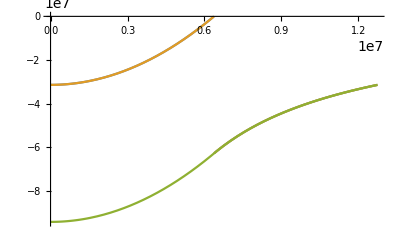

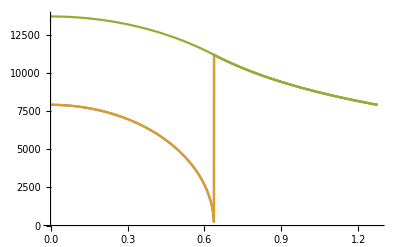

```mathematica
(*Plot[{Veff[#,0.001943801652892562,1,220 10^3]&[r],Veff[#,0.2352,1,20 10^3]&[r],Veff[#,0,1,20 10^3]&[r]},{r,0,2 "rE"/.EarthRepl},PlotRange->All]*)
Plot[{Veff[#,ϕmax[220 10^3],1,220 10^3]&[r],Veff[#,ϕmax[20 10^3],1,20 10^3]&[r],Veff[#,0,1,20 10^3]&[r]},{r,0,2 "rE"/.EarthRepl},PlotRange->All]
Plot[{√(-2Veff[#,ϕmax[220 10^3],1,220 10^3])&[r],√(-2Veff[#,ϕmax[20 10^3],1,20 10^3])&[r],√(-2Veff[#,0,1,20 10^3])&[r]},{r,0,2 "rE"/.EarthRepl},PlotRange->All]
(*-2Veff[#,0.01,1,220 10^3]&["rE"/.EarthRepl]
√(-2Veff[#,0.001,1,20 10^3]&["rE"/.EarthRepl])*)
```

```mathematica
ϕmax[20 10^3]//N
Veff[#,ϕE,vmean,qD]&["rE"/.EarthRepl]
```

0.2352

-6.272×10^7+2/3 qD vmean^2 ϕE

```mathematica
Veff[#,ϕmax[220 10^3],220 10^3,1]&["rE"/.EarthRepl]
```

0.

```mathematica
ϕmax[20 10^3]//N
```

0.2352

```mathematica
Manipulate[Plot[Veff[#,ϕE,20 10^3,1]&[r],{r,0,2 "rE"/.EarthRepl},PlotRange->All],{ϕE,0,3 ϕmax[20 10^3]}]
```

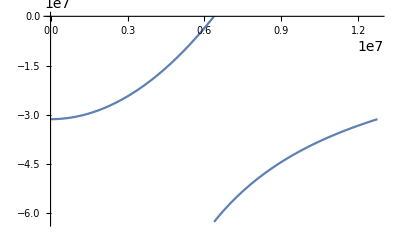

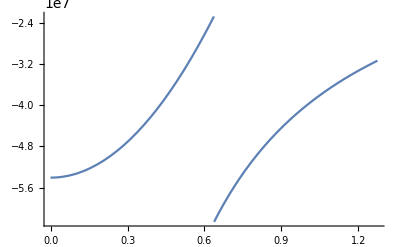

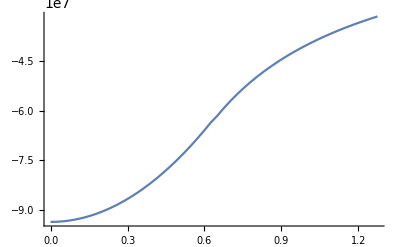

-Graphics-

```mathematica
Do[Print@Plot[{Veff[#,ϕmax[20 10^3],20 10^3,1]&[r],Veff[#,0.15,20 10^3]&[r],Veff[#,0.0015,20 10^3]&[r],Veff[#,0.0015,20 10^3]&[r]}[[i]],{r,0,2 "rE"/.EarthRepl},PlotRange->All],{i,4}]
```

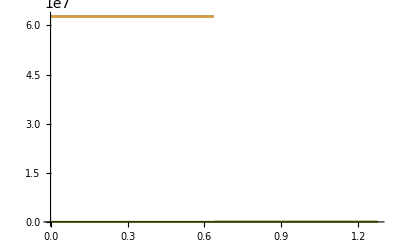

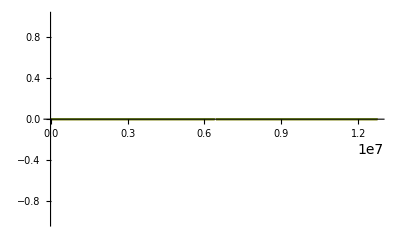

```mathematica
Plot[{Veff[#,ϕmax[220 10^3],220 10^3,1,False]&[r],Veff[#,ϕmax[20 10^3],20 10^3,1,False]&[r],Veff[#,0,20 10^3,1,False]&[r]},{r,0,2 "rE"/.EarthRepl},PlotRange->All]
Plot[{Re@√(-2Veff[#,ϕmax[220 10^3],220 10^3,1,False]&[r]),Re@√(-2Veff[#,ϕmax[20 10^3],20 10^3,1,False]&[r]),Re@√(-2Veff[#,0,20 10^3,1,False]&[r])},{r,0,2 "rE"/.EarthRepl},PlotRange->All]
```

#### EL and Δr total

```mathematica
dc[bE_] := 2 √(("rcore")^2-bE^2)/.Constants`EarthRepl (*path length in the core for given impact parameter*)
dE[bE_] := 2 √(("rE")^2-bE^2)/.Constants`EarthRepl (*path length through the earth*)
dM[bE_]:= If[(("rcore")^2/.Constants`EarthRepl)>bE^2,dE[bE] - dc[bE],Re[dE[bE]]](*path length through the Mantle, iff condition is satisfied does it go through the core*)
```

```mathematica
Clear[GetTotalELFunction]
GetTotalELFunction[ElectronicσDicsts_,NuclearσDicts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[ElectronicσDicsts,NuclearσDicts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;

(*Returns: ΔE[bE,vχ]*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

```mathematica
Clear[GeteELFunction]
GeteELFunction[ElectronicσDicsts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[ElectronicσDicsts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;


(*Returns: ΔE[bE,vχ]*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

```mathematica
Clear[GetNucELFunction]
GetNucELFunction[NuclearσDicts_]:=Module[{RegionσDicts,RegionELfuncs,RegionELDomains,CrustIndex,CoreIndex,rc,rE,dEdlofr,ΔEthroughEarth},
RegionσDicts=Gather[Flatten[Join[NuclearσDicts]],#1[["regionindex"]]==#2[["regionindex"]]&];

CrustIndex=FirstPosition["regionindex"/.RegionσDicts,1][[1]];
CoreIndex = FirstPosition["regionindex"/.RegionσDicts,2][[1]];

rc = "rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

(*Returns: dEdl[r,vχ]*)
dEdlofr=Quiet@Re@Total@Piecewise[{{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CrustIndex,;;]],rE> #1 >=  rc},{10^"dEdlf"[ Log10[#2]]HeavisideTheta[Log10[#2]-"dEdlf"["Domain"][[1,1]]]/.RegionσDicts[[CoreIndex,;;]], rc>#1}},0]&;


(*Returns: ΔE[bE,vχ]*)
ΔEthroughEarth=Quiet@Re@Piecewise[{{(dM[#1] dEdlofr[1.1rc,#2] + dc[#1] dEdlofr[0.9rc,#2]),rc^2>#1^2},{dM[#1] dEdlofr[1.1rc,#2],rE^2>#1^2>=rc^2}},0]&;

<|"dEdlofr"->dEdlofr,"ΔEthroughEarth"->ΔEthroughEarth|>
]
```

```mathematica
EK[mχ_,vχ_] :=1/2 mχ vχ^2
ΔrTotbyκsquared[mχ_,vχ_,bE_,ΔEfunc_,y_:10^-2]:=Re[dE[bE] y EK[mχ,vχ]/ΔEfunc[bE,vχ] ]
```

#### Weak Capture Regime Trajectory - Linear

```mathematica
(*Clear[GetWeakCaptureTrajectory]
GetWeakCaptureTrajectory[mχ_,vχE_,bE_,κ_,ELfunc_]:=Module[{RE,lsol,ldom,voft},
(*this version crashes*)
(*use get GetWeakCaptureProbability* with this and GetCaptureRateOldTraj*)
RE = dE[bE];(*path length through the Earth*)
lsol=l/.NDSolve[{D[l[t],{t,2}]==-1/mχ κ^2("JpereV"/.Constants`SIConstRepl)ELfunc[√(bE^2+l[t]^2),l'[t]],l'[0]==vχE,l[0]==-RE/2,WhenEvent[l[t]==RE/2,"StopIntegration"]},l,{t,0,10^4}][[1]];(*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of time.*)
ldom=lsol["Domain"][[1]];
(*Print["endpoint vs max"];
Print[lsol[ldom[[2]]]];
Print[RE/2];*)
voft=lsol';
<|"l(t)"->lsol,"v(t)"->voft,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]*)
```

```mathematica
Clear[GetWeakCaptureTrajectoryinv]
GetWeakCaptureTrajectoryinv[mχ_,vχE_,bE_,κ_,ELfunc_]:=Module[{RE,vsol,ldom,voft},
(*use get GetWeakCaptureProbability*fromv with this and GetCaptureRate*)
(*first order solution for trajectory*)
RE = dE[bE];(*path length through the Earth*)
vsol=v/.NDSolve[{D[v[l],l]==-1/(mχ v[l])κ^2("JpereV"/.Constants`SIConstRepl)ELfunc[√(bE^2+l^2),v[l]],v[0]==vχE,WhenEvent[v[l]<="vesc"/.Constants`EarthRepl,"StopIntegration"]},v,{l,-RE/2,RE/2}][[1]];
(*vsol=v/.NDSolve[{D[v[l],l]==-(κ^2("JpereV"/.Constants`SIConstRepl))/mχELfunc[√(bE^2+l^2),v[l]],v[0]==vχE},v,{l,-RE/2,RE/2}][[1]];*)(*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of time.*)
ldom=vsol["Domain"][[1]];

(*Print[vsol["Domain"]];*)

<|"v(l)"->vsol,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]
```

```mathematica
Clear[GetWeakCaptureTrajectoryinvFE]
GetWeakCaptureTrajectoryinvFE[mχ_,vχE_,bE_,κ_,ELfunc_,N_:100]:=Module[{RE,h,vofls,vsol,ldom,voft},
(*use get GetWeakCaptureProbability*fromv with this and GetCaptureRate*)
(*Forward Euler solution for trajectory*)

RE = dE[bE];(*path length through the Earth*)
h=RE/N;
vofls=Table[{h s-RE/2,0},{s,N}];
vofls[[1,2]]=vχE;

Do[
(*vofls[[s+1,2]]=vofls[[s,2]]-h(κ^2("JpereV"/.Constants`SIConstRepl))/(mχ vofls[[s,2]])ELfunc[√(bE^2+vofls[[s,1]]^2),vofls[[s,2]]];*)(*I don't think this JpereV should be there.*)
vofls[[s+1,2]]=vofls[[s,2]]-h κ^2/(mχ vofls[[s,2]])ELfunc[√(bE^2+vofls[[s,1]]^2),vofls[[s,2]]];
If[vofls[[s+1,2]]<="vesc"/.Constants`EarthRepl,Break[]];
,{s,N-1}]; (*forward euler for dv/dl=-1/(Subscript[m, χ] v)dE/dl - (ie. from energy conservation / Raleigh-Lagrange Formalism)*)

vsol=Interpolation[vofls]; (*Solution for trajectory of particle along a straight line through the earth parallel to it's velocity as a function of length.*)
ldom=vsol["Domain"][[1]];

(*Print[vsol["Domain"]];*)

<|"v(l)"->vsol,"domain"->ldom,"RE"->RE,"κ"->κ,"bE"->bE,"mχ"->mχ|>
]
```

#### Weak Capture Regime Trajectory - w Potential - Runge Kutta

```mathematica
Clear[GetWeakCaptureTrajectoryinvRK2wPotential]
GetWeakCaptureTrajectoryinvRK2wPotential[mχ_,vχE_,bE_,κ_,ELfunc_,Vofr_:Vgrav,N_:30]:=Module[{rE,Δl,E0,L0,steps,traj,ti,l,r,v,vr,ΔE,L,LogΔL,Lcomped,vsol,ldom,lsol,rdom,voft,rfinal(*,vfinal,vesc*),lMC1,lMC2,lMC},
(*slightly better than FW for conserved quantities, not quite an actual RK2*)
(*
ELfunc - dE/dl
Vofr - (V(r))/mχ
*)

rE="rE"/.Constants`EarthRepl;
Δl=rE/N; (*Δl*)

E0 = mχ/2 vχE^2 +mχ Vofr[rE];
L0 = mχ vχE bE;

traj={<|"l"->0,"r"->rE,"v"->vχE,"vr"->-vχE √(1 - (bE/rE)^2),"ΔE"->0,"V"->mχ Vofr[rE],"L"->L0,"LogΔL"->0(*,"Lcomped"->L0*)|>};
(*initialize list of points along trajectory at Earth's surface
	l - Path length
	r - Distance from Earth's centre
	vχ - aDM speed
	vr - radial aDM speed (initially pointing inward)
	ΔE - Energy lost from dissipation
	L - Angular Momentum
	LogΔL - Log of time dependent part of L 
*)

steps = 0;
Do[
steps++;
ti = traj[[-1]];(*current trajectory point*)

l = ti["l"]+Δl;
(*r = Abs[ti["r"]+Δl ti["vr"]/ti["v"]];*)
r = ti["r"]+Δl ti["vr"]/ti["v"];

If[E0- mχ Vofr[r]-ti["ΔE"]< 0,Break[]]; (*numerical, weaker than the below - will be satisfied when v<0, above will be when v<vesc*)
v = √(2/mχ(E0 - mχ Vofr[r] - ti["ΔE"]) );(*this choice of incrementation, preserves energy but wildly violates L conservation / behaviour*)

ΔE = ti["ΔE"] + Δl κ^2 ELfunc[r,v];

LogΔL = ti["LogΔL"]+ (Δl κ^2 ELfunc[r,v])/(mχ v^2);

L = L0 E^-LogΔL;

vr = ti["vr"] + Δl ((v^2-ti["vr"]^2)/(r v) - (mχ Vofr'[r])/(mχ v)-ti["vr"]/(mχ v^2)κ^2 ELfunc[r,v]);
(*vr = ti["vr"] + Δl ((ti["v"]^2-ti["vr"]^2)/(ti["r"] ti["v"]) - (mχ Vofr'[ti["r"]])/(mχ ti["v"])-ti["vr"]/(mχ ti["v"]^2)κ^2 ELfunc[ti["r"],ti["v"]]);*)
(*vr = ti["vr"] + Δl (L^2/(r^3 mχ^2) - (mχ Vofr'[r])/(mχ v)-ti["vr"]/(mχ v^2)κ^2 ELfunc[r,v]);*)(*assumes ELfunc > 0, so we include - for dissipation*)
(*vr=Sign[ti["vr"]] √(v^2-L^2/(mχ^2 r^2));*)

If[vr/ti["vr"]<0 ,vr=-ti["vr"]];(*vr has changed sign, just take vr to be the same as it was on the previous step with a new sign, avoids the numerical instability from very small r at low impact parameter*)

If[r<0,r = - r;vr=-ti["vr"]]; (*same as above, past near (within Δl of) Earth's centre and is propagating towards surface*)

(*If[vr>10^7,Print["t1 ",(v^2-ti["vr"]^2)/(r v), "\nt2 ",(mχ Vofr'[r])/(mχ v),"\nt3 ",ti["vr"]/(mχ v^2)κ^2 ELfunc[r,v],"\nΔl ",Δl,"\nti[vr]",ti["vr"]]];*)

(*L=mχ r √(v^2-vr^2);(*this choice of incrementation, preserves energy but wildly violates L conservation / behaviour*)*)

(*If[r>rE,Break[]];*)
AppendTo[traj,<|"l"->l,"r"->r,"v"->v,"vr"->vr,"ΔE"->ΔE,"V"->mχ Vofr[r],"L"->L,"LogΔL"->LogΔL(*,"Lcomped"->Lcomped*)|>];

(*Print[mχ/2 v^2+ mχ Vofr[r]];
Print[ mχ Vofr[r]];*)

If[mχ/2 v^2+ mχ Vofr[r]< 0,Break[]];(*particle is captured, ie. bound to the earth, placed after the append statement so that at least one additional point is added. This is needed for the captured condition used further down the pipeline in the case where initial conditions already imply the particle is bound.*)


(* should we remove the append in cases where it's captured right at the surface???? 
no need, all good v_⊥ is irrelevant for capture calculation. *)

If[r>rE,Break[]];
,{s,3N}];(*will break once reaches surface (<~ 2 N) this is just a buffer*)

If[Max[Abs[(("mχ")/2("v")^2+"V"+"ΔE")/E0-1]/.traj]>0.20,Print["Energy conservation has been violated by more than 20% in Forward Euler: ",Max@Abs[(("mχ")/2("v")^2+"V"+"ΔE")/E0-1]/.traj]];

vsol=Quiet@Interpolation[{"l","v"}/.traj]; 
ldom=vsol["Domain"][[1]];

lsol = Quiet@Interpolation[{"l","r"}/.traj];
rdom = lsol["Domain"][[1]];

rfinal = "r"/.traj[[-1]]; (*this is the capture condition - if we stop before we reach the surface, we are captured, otherwise we have left the Earth with E>0 so motion is unbounded. *)

(*values of l where particle crosses mantle-core boundary*)
If[rfinal>"rE"/.Constants`EarthRepl,
(*passes completely through the earth, so approximately symmetric about the l domain. *)
If[Min["r"/.traj]<"rcore"/.Constants`EarthRepl,
(*particle passes through the core*)
lMC1 = l/.Quiet@FindRoot[lsol[l]-"rcore"/.Constants`EarthRepl,{l,rdom[[2]]/4,rdom[[1]],rdom[[2]]/2}];
lMC2 = l/.Quiet@FindRoot[lsol[l]-"rcore"/.Constants`EarthRepl,{l,(3rdom[[2]])/4,rdom[[2]]/2,rdom[[2]]}];
lMC={lMC1,lMC2};,
(*doesn't pass through the core (No Core)*)
lMC={"NC"}
],
(*It's captured somewhere, so we won't need to distinguish between crust and core for since we won't compute hard capture.*)
lMC = {"Cap"}
];

<|"v(l)"->vsol,"domain"->ldom,"r(l)"->lsol,"rdom"->rdom,"traj"->traj,"κ"->κ,"bE"->bE,"mχ"->mχ,"vχE"->vχE,"E0"->E0,"L0"->L0,"steps"->steps,"rfinal"->rfinal,"lMCs"->lMC,"V(r)"->Function[{r},mχ Vofr[r]],"N"->N|>
]
```

### Weak Capture Probabilities

#### Weak Capture Regime Capture Interaction Length - e (not used in pipeline)

```mathematica
Clear[GetWeakCaptureInteractionLength]
GetWeakCaptureInteractionLength[σDict_]:= Module[{vχmin,mχ,ωmin,params,regionindex,σdom,ωcapture,δξ,ξofωandvχt,ωmaxofvχt,dσdERoftandω,σofvχandωmin,λinvofχ},
ωmin="ωmin"/.σDict;
params=σDict["params"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.σDict);
regionindex = "regionindex"/.σDict;
σdom=("σofξf"/.σDict)["Domain"];

vχmin=Max[3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params,"vesc"/.Constants`EarthRepl]; (*restrict minimum velocity according to minimum velocity of interpolation (see energy loss package), and the escape velocity*)

ξofωandvχt=EnergyLoss`ξofωandvχ[#1,ωmin,#2,mχ,params]&;
ωmaxofvχt=EnergyLoss`ωmaxofvχ[#,mχ,params]&;

σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@(ξofωandvχt[#2,#1])]])&;

ωcapture = 1/(2 ("ℏ"/.params))mχ (#^2 - ("vesc"/.Constants`EarthRepl)^2)&; (*energy transfer needed to capture the particle*)

λinvofχ=If[#>vχmin && ωmaxofvχt[#]>ωcapture[#]&&(ξofωandvχt[ωcapture[#],#])>10^σdom[[2,1]],("ne"/.params)σofvχandωmin[#,ωcapture[#]],0]&; (*must have v > minimum velocity allowed, must have maximum possible energy transfer greater than energy needed to capture, and must have that energy transfer be in the domain of the interpolation function*)

λinvofχ
]
```

```mathematica
Clear[GetTotaleWeakCaptureInteractionLength]
GetTotaleWeakCaptureInteractionLength[σDicts_]:=Module[{},
Total@Table[GetWeakCaptureInteractionLength[σDicts[[i]]][#],{i,Length[σDicts]}]&
]
```

#### Weak Capture Regime Capture Interaction Length - Nuc (not used in pipeline)

```mathematica
Clear[GetWeakCaptureInteractionLengthNuc]
GetWeakCaptureInteractionLengthNuc[σDict_]:= Module[{vχmin,mχ,mN,ωmin,params,NucleusParams,regionindex,σdom,ωcapture,δξ,ξofωandvχt,ωmaxofvχt,dσdERoftandω,σofvχandωmin,λinvofχ},
ωmin="ωmin"/.σDict;
params=σDict["params"];
NucleusParams=σDict["NucleusParams"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.σDict);
mN = "mN"/.σDict;
regionindex = "regionindex"/.σDict;
σdom=("σofξf"/.σDict)["Domain"];

(*vχmin=3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params; *)
vχmin=Max[3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params,"vesc"/.Constants`EarthRepl];(*minimum allowable velocity given the lower bound on energy transfer, times an O(1) fudge factor for numerical stability (3) *)
(*vχ=If[#>vχmin,#,0]&;*)
(*χtraj=("l(t)"/.vDict);*)

(*ξofωandvχt=Abs[EnergyLoss`ξofωNuc[#1,ωmin,#2,mχ,mN,params]-δξ]&;*)
(*ξofωandvχt=Abs[EnergyLoss`ξofωNuc[#1,ωmin,#2,mχ,mN,params]]&;*)
ξofωandvχt=EnergyLoss`ξofωNuc[#1,ωmin,#2,mχ,mN,params]&;
ωmaxofvχt=EnergyLoss`ωmaxNuc[#,mχ,mN,params]&;

(*dσdERoftandω=10^Re@("dσf"/.σDict)[Log10@vχ[#1],Log10@ξofωandt[#2,#1]]&; (*not currently used*)*)

(*σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@(Min[ξofωandvχt[#2,#1],1-δξ])]])&;*)
σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@(ξofωandvχt[#2,#1])]])&;

(*Post ωcapture*)
ωcapture = 1/(2 ("ℏ"/.params))mχ (#^2 - ("vesc"/.Constants`EarthRepl)^2)&; (*energy transfer needed to capture the particle*)


(*Print[("σofξf"/.σDict)["Domain"]];
Print@Plot[Log10@(ξofωandvχt[ωcapture[#],#])&[vχ],{vχ,"vesc"/.EarthRepl,5+"vesc"/.EarthRepl}];
Print[Plot[Log10@(ξofωandvχt[ωcapture[#],#])-σdom[[2,1]]&[vχ],{vχ,"vesc"/.EarthRepl,5+"vesc"/.EarthRepl}]];

With[{vχ=1.0001 "vesc"/.EarthRepl},
Print["vχmin"];
Print[vχ-vχmin];
Print["ωmaxofvχ-ωcapture"];
Print[ωmaxofvχt[vχ]-ωcapture[vχ]];
Print["λ^-1"];
Print[("nI"/.NucleusParams)σofvχandωmin[vχ,ωcapture[vχ]]];
Print["ξofωandvχs"];
Print[Log10@ξofωandvχt[ωcapture[vχ],vχ]];
Print[Log10@ξofωandvχt[ωmaxofvχt[vχ],vχ]]];*)

λinvofχ=If[#>vχmin && ωmaxofvχt[#]>ωcapture[#]&&(ξofωandvχt[ωcapture[#],#])>10^σdom[[2,1]],("nI"/.NucleusParams)σofvχandωmin[#,ωcapture[#]],0]&;
(*λinvofχ=If[#>vχmin ,("ne"/.params)σofvχandωmin[#,ωcapture[#]],0]&; *)(*if v is greater than the lowest allowable velocity (set by ωmin - the lowest allowable energy transfer), and the maximum possible energy transfer (set by kinetic energy) is greater than energy needed to capture (always true),
get the INVERSE interaction length / cross-section to transfer at least ωcapture to the system and have energy less than the escape velocity*)

λinvofχ
]
```

```mathematica
Clear[GetTotalNucWeakCaptureInteractionLength]
GetTotalNucWeakCaptureInteractionLength[σDicts_]:=Module[{},
Total@Table[GetWeakCaptureInteractionLengthNuc[σDicts[[i]]][#],{i,Length[σDicts]}]&
]
```

#### Weak Capture Regime Capture Probability - w Potential - position dependent v_esc - e

```mathematica
Clear[GetWeakCaptureProbabilitywPot]
GetWeakCaptureProbabilitywPot[vDict_,σDict_,ELTotalinE_:0]:= Module[{vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,ldom,ELofl,κ,regionindex,σdom,vesc,ωcapture,δξ,ξofωandl,ωmaxofl,dσdERoftandω,σoftandωmin,rCore,rE,lcore,lcrust,λinvoft,vbound1,vbound2,λintegrand,integralofλinvwrtr},
ωmin="ωmin"/.σDict;
params=σDict["params"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.vDict);
(*ldom = "domain"/.vDict;*)
κ=("κ"/.vDict);
regionindex = "regionindex"/.σDict; (*1 in crust, 2 in core*)
σdom=("σofξf"/.σDict)["Domain"];

bE=("bE"/.vDict);(*impact parameter*)
rCore="rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;
vχraw=("v(l)"/.vDict);

vχmin=Max[3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params,vesc[#]]&;
vχ=If[vχraw[#]>vχmin[#],("v(l)"/.vDict)[#],0]&;
(*bE=("bE"/.vDict);(*impact parameter*)*)

ldom = If[#[[2]]>=(2 √(rE^2-bE^2)),{#[[1]],(*0.96*) 2 √(rE^2-bE^2)},#]&["domain"/.vDict];
(*vesc=Function[{l},√(-(2("V(r)"/.vDict)[("r(l)"/.vDict)[l]])/mχ)];*)
(*vesc=Function[{l}, If[#!=0,#,("vesc")/10^4/.Constants`EarthRepl]&@(Re@√(-(2("V(r)"/.vDict)[("r(l)"/.vDict)[l]])/mχ))];(*if vesc^2 < 0, then set it to a small positive value (we assume flat potential in the Earth)*)*)

(*vesc=Function[{l}, If[#!=0,#,0]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];(*if vesc^2 < 0, then take vesc -> 0.*)*)

(*vesc=Function[{l}, If[#!=0,#,√(2/mχ ELTotalinE(1-l/(2 √(rE^2-bE^2))))]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];*)
(*vesc=Function[{l}, If[#!=0,#,√(2/mχ ELTotalinE[bE,vχraw[l]](1-l/(2 √(rE^2-bE^2))))]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];*)(*if vesc^2 < 0, then take vesc -> √(2/mχ Subscript[ΔE, c]). Where Subscript[ΔE, c] is a characteristic value for the EL expected in the remainder of the trajectory through the Earth. Since we assume that the potential is flat for negative vesc^2, we can just get an estimate based on the radius in the Earth, the impact parameter, and the total energy we expect to lose in the Earth. 

It is critical to include this since for nuclear, if vesc^2<0 aDM cannot come to rest through a single hard nuclear scatter.*)

ELofl=Function[{l},Re@√2/mχ ELTotalinE[bE,vχraw[l]]If[#>0,#,0]&@(1-l/(2 √(rE^2-bE^2)))(*0*)];
(*vesc=Function[{l}, If[#!=0,#,If[ELofl[l]!=0,ELofl[l],ELofl[0.99 2 √(rE^2-bE^2)]]]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];*)

vesc=Function[{l}, If[#!=0,#,ELofl[l]]&@(Re@√(-1/mχ 2("V(r)"/.vDict)[If[("r(l)"/.vDict)[l]<=rE,("r(l)"/.vDict)[l],rE]]))]; (*if vesc^2 < 0, then take vesc -> √(2/mχ Subscript[ΔE, c]). Where Subscript[ΔE, c] is a characteristic value for the EL expected in the remainder of the trajectory through the Earth. Since we assume that the potential is flat for negative vesc^2, we can just get an estimate based on the radius in the Earth, the impact parameter, and the total energy we expect to lose in the Earth. 

It is critical to include this since for nuclear, if vesc^2<0 aDM cannot come to rest through a single hard nuclear scatter.*)(* *** DIFF *)



ξofωandl=EnergyLoss`ξofωandvχ[#1,ωmin,("v(l)"/.vDict)[#2],mχ,params]&;
ωmaxofl=EnergyLoss`ωmaxofvχ[("v(l)"/.vDict)[#1],mχ,params]&;

σoftandωmin=10^(Re[("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandl[#2,#1]]])&;

ωcapture = 1/(2 ("ℏ"/.params))mχ (vχ[#]^2 - vesc[#]^2)&;

λinvoft=If[vχraw[#]>vχmin[#] && ωmaxofl[#]>ωcapture[#]&&(ξofωandl[ωcapture[#],#])>10^σdom[[2,1]],κ^2("ne"/.params)σoftandωmin[#,ωcapture[#]],0]&;

(*find the points where capture goes to 0 due to large velocity (a result of acceleration), if the region is too close to the boundary, we need to integrate over them more carefully since mathematica can miss it. *)
vbound1 =Quiet@Check[ l/.FindRoot[ωmaxofl[#]-ωcapture[#]&[l],{l,ldom[[2]]/4,ldom[[1]],ldom[[2]]/2}],ldom[[2]]/2];
vbound2= Quiet@Check[l/.FindRoot[ωmaxofl[#]-ωcapture[#]&[l],{l,(3ldom[[2]])/4,ldom[[2]]/2,ldom[[2]]}],ldom[[2]]/2];

rCore="rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;

λintegrand[l_?NumericQ]:=λinvoft[l];

(*Print[ωmin];
Print[vesc[(ldom[[1]]+ldom[[2]])/2]];
Print@Plot[vesc[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"vesc"];
Print@Plot[vχraw[l],{l,ldom[[1]],ldom[[2]]}];
Print@Plot[vχmin[l],{l,ldom[[1]],ldom[[2]]}];
Print@Plot[λintegrand[l],{l,ldom[[1]],ldom[[2]]}];*)

If[vDict["lMCs"]=={ "NC"},
(*Doesn't pass through the core, just integrate*)
If[regionindex==2,
(*material is in the core, return 0*)
Return[0,Module],
(*material is in the mantle, just integrate*)
integralofλinvwrtr=Quiet@Check[#[12],Print[{mχ,"vχE"/.vDict,bE,κ,"materialname"/.σDict}];#[15]]&[Function[{MR},If[vbound1/(ldom[[2]]-ldom[[1]])<10^-2||1-vbound2/(ldom[[2]]-ldom[[1]])<10^-2,NIntegrate[λintegrand[l],{l,ldom[[1]],vbound1},PrecisionGoal->3,MaxRecursion->MR,AccuracyGoal->3]+NIntegrate[λintegrand[l],{l,vbound2,ldom[[2]]},PrecisionGoal->3,MaxRecursion->MR,AccuracyGoal->3],NIntegrate[λintegrand[l],{l,ldom[[1]],ldom[[2]]},PrecisionGoal->3,MaxRecursion->MR,AccuracyGoal->3]]]];
],
(*Passes through the core*)
If[regionindex==2,
(*material is in the core, integrate between the two Mantle-Core boundary points*)
integralofλinvwrtr=Quiet@Check[#,Print[{mχ,"vχE"/.vDict,bE,κ,"materialname"/.σDict}];#]&[NIntegrate[λintegrand[l],{l,vDict["lMCs"][[1]],vDict["lMCs"][[2]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]];,
(*material is in the mantle, integrate over the regions before and after the core, then add*)
integralofλinvwrtr=Quiet@Check[#,Print[{mχ,"vχE"/.vDict,bE,κ,"materialname"/.σDict}];#]&[NIntegrate[λintegrand[l],{l,ldom[[1]],vDict["lMCs"][[1]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]+NIntegrate[λintegrand[l],{l,vDict["lMCs"][[2]],ldom[[2]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]];
]
];

integralofλinvwrtr
]
```

#### Weak Capture Regime Capture Probability - w Potential - position dependent v_esc - Nuc

```mathematica
Clear[GetWeakCaptureProbabilityNucwPot]
GetWeakCaptureProbabilityNucwPot[vDict_,σDict_,ELTotalinE_:0]:= Module[{vχmin,vχraw,vχ,χtraj,bE,mχ,ωmin,params,NucleusParams,ldom,ELofl,κ,regionindex,σdom,mN,ωcapture,vesc,δξ,ξofωandl,ωmaxofl,dσdERoftandω,σoftandωmin,λinvoft,λintegrand,vbound1,vbound2,rCore,rE,lcore,lcrust,integralofλinvwrtr},
ωmin="ωmin"/.σDict;
params=σDict["params"];
NucleusParams=σDict["NucleusParams"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.vDict);
κ=("κ"/.vDict);
mN = "mN"/.σDict;
regionindex = "regionindex"/.σDict;
σdom=("σofξf"/.σDict)["Domain"];

bE=("bE"/.vDict);(*impact parameter*)
rCore="rcore"/.Constants`EarthRepl;
rE = "rE"/.Constants`EarthRepl;
(*vesc=Function[{l},√(-(2("V(r)"/.vDict)[("r(l)"/.vDict)[l]])/mχ)]; *)
vχraw=("v(l)"/.vDict);

ldom = If[#[[2]]>=(2 √(rE^2-bE^2)),{#[[1]],(*0.96*) 2 √(rE^2-bE^2)},#]&["domain"/.vDict];
(*ldom="domain"/.vDict;*)

(*ldom={("domain"/.vDict)[[1]],(l/.FindRoot[("r(l)"/.vDict)[l]-rE,{l,(3("domain"/.vDict)[[2]])/4,(("domain"/.vDict)[[2]])/2,("domain"/.vDict)[[2]]}])};*)

(*vesc=Function[{l}, If[#!=0,#,("vesc")/10^4/.Constants`EarthRepl]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];*)(*if vesc^2 < 0, then set it to a small positive value (we assume flat potential in the Earth)*)

(*vesc=Function[{l}, If[#!=0,#,0]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];(*if vesc^2 < 0, then take vesc -> 0. This shuts off capture for Nuclear, and will be accurate assuming there are no potential barriers between the point in the Earth and the surface - ie. for a flat potential which is what we assume.*)*)

ELofl=Function[{l},Re@√2/mχ ELTotalinE[bE,vχraw[l]]If[#>0,#,0]&@(1-l/(2 √(rE^2-bE^2)))(*0*)];
(*vesc=Function[{l}, If[#!=0,#,If[ELofl[l]!=0,ELofl[l],ELofl[0.99 2 √(rE^2-bE^2)]]]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];*)

vesc=Function[{l}, If[#!=0,#,ELofl[l]]&@(Re@√(-1/mχ 2("V(r)"/.vDict)[If[("r(l)"/.vDict)[l]<=rE,("r(l)"/.vDict)[l],rE]]))]; (*if vesc^2 < 0, then take vesc -> √(2/mχ Subscript[ΔE, c]). Where Subscript[ΔE, c] is a characteristic value for the EL expected in the remainder of the trajectory through the Earth. Since we assume that the potential is flat for negative vesc^2, we can just get an estimate based on the radius in the Earth, the impact parameter, and the total energy we expect to lose in the Earth. 

It is critical to include this since for nuclear, if vesc^2<0 aDM cannot come to rest through a single hard nuclear scatter.*)(* *** DIFF *)

(*vesc=Function[{l}, If[#!=0,#,0]&@(Re@√(-1/mχ2("V(r)"/.vDict)[("r(l)"/.vDict)[l]]))];*)

vχmin=Max[Sqrt[("ℏ" ωmin)/(2 mχ)]/.params,vesc[#]]&;(*minimum allowable velocity given the lower bound on energy transfer *)
(*vχmin=Max[3Sqrt[("ℏ" ωmin)/(2 mχ)]/.params,vesc[#]]&;(*minimum allowable velocity given the lower bound on energy transfer times an order one fudge factor (3)*)*)

vχ=If[vχraw[#]>vχmin[#],("v(l)"/.vDict)[#],0]&;

ξofωandl=EnergyLoss`ξofωNuc[#1,ωmin,("v(l)"/.vDict)[#2],mχ,mN,params]&;(*[ω,l]*)
ωmaxofl=EnergyLoss`ωmaxNuc[("v(l)"/.vDict)[#1],mχ,mN,params]&;

σoftandωmin=10^(Re[("σofξf"/.σDict)[Log10@vχ[#1],Log10@ξofωandl[#2,#1]]])&;(*[l,ω]*)

ωcapture = 1/(2 ("ℏ"/.params))mχ (vχ[#]^2 - vesc[#]^2)&; 

(*find a way to estimate the amount of energy we expect to lose through the rest of it's trajectory. Well we computed this. It should be in the module for defining the capture probability distribution.*)

λinvoft=If[vχraw[#]>vχmin[#] && ωmaxofl[#]>ωcapture[#]&&(ξofωandl[ωcapture[#],#])>10^σdom[[2,1]],κ^2("nI"/.NucleusParams)σoftandωmin[#,ωcapture[#]],0]&;

vbound1 =Quiet@Check[ l/.FindRoot[ωmaxofl[#]-ωcapture[#]&[l],{l,ldom[[2]]/4,ldom[[1]],ldom[[2]]/2}],ldom[[2]]/2];
vbound2= Quiet@Check[l/.FindRoot[ωmaxofl[#]-ωcapture[#]&[l],{l,(3ldom[[2]])/4,ldom[[2]]/2,ldom[[2]]}],ldom[[2]]/2];(*find the endpoints along the trajectory such that the aDM is moving slow enough that it could potentially be captured by a hard scatter. *)


λintegrand[l_?NumericQ]:=λinvoft[l];

If[(*{mχ,"vχE"/.vDict,bE,κ,"materialname"/.σDict}==(*{1.7799999999999998*^-26,760.9393510361165,1.274250968*^6,1/1000000000000,"Si Nuc"}*){1.7799999999999998*^-26,760.9393510361165,1.9113445970000003*^6,1/1000000000000,"Si Nuc"},*)
(*internalplot&& 300>("vχE"/.vDict)>100&&("materialname"/.σDict)=="Si Nuc"&&bE>10^5,*)
internalplot&& 30>("vχE"/.vDict)>1&&("materialname"/.σDict)=="Si Nuc"&&bE>10^5,
internalplot=False;
(*Print@FindRoot[("r(l)"/.vDict)[l]-rE,{l,(3ldom[[2]])/4,ldom[[2]]/2,ldom[[2]]}];*)
Print["r(l_max)-rE ",("r(l)"/.vDict)[ldom[[2]]]-rE];
Print[Plot[(("r(l)"/.vDict)[l])/rE,{l,ldom[[1]],ldom[[2]]}]];
Print["vbounds ",{vbound1,vbound2}];
Print[{mχ,"vχE"/.vDict,bE,κ,"materialname"/.σDict}];
Print["2√(rE^2)",2 √(rE^2-bE^2)];Print["ldom",ldom];
Print[Plot[Log10@λintegrand[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"λ integrand",PlotRange->All,Mesh->All]];Print@Plot[Log10@ωcapture[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"ωcapture"];Print@Plot[Log10@(vesc[l]^2),{l,ldom[[1]],ldom[[2]]},PlotLabel->"vesc^2",PlotRange->All];
Print@Plot[Log10@ELofl[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"Elofl",PlotRange->All];Print@Plot[Log10@ωmaxofl[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"ωmax",PlotRange->{0,15}];
Print@Plot[Log10@σoftandωmin[l,ωcapture[l]],{l,ldom[[1]],ldom[[2]]},PlotLabel->"σ",PlotRange->All];
Print@Plot[Log10@vχ[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"v"];
Print["v(10^7)",vχ[10^7]];
Print["σdom is ",σdom];
Print["ωmin is ",N[ωmin,10]];
Print[Plot[Log10@ξofωandl[ωcapture[l],l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"ξ(ωcap)"]];
Print[Plot[Boole[σdom[[2,1]]<Log10@ξofωandl[ωcapture[l],l]<σdom[[2,2]]],{l,ldom[[1]],ldom[[2]]},PlotLabel->"ξ(ωcap) domain violated?"]];
Print[Boole[σdom[[2,1]]<Log10@ξofωandl[ωcapture[l],l]<σdom[[2,2]]/.l->10^7]];
Print@Plot[Boole[σdom[[2,1]]<Log10@ξofωandl[ωcapture[l],l]<σdom[[2,2]]]Log10@σoftandωmin[l,ωcapture[l]],{l,ldom[[1]],ldom[[2]]},PlotLabel->"σ w cut",PlotRange->All];
Print[Plot[Boole[σdom[[2,1]]<Log10@ξofωandl[ωcapture[l],l]<σdom[[2,2]]]Log10@λintegrand[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"λ integrand w cut",PlotRange->All]];
Print@Plot[ωmaxofl[l]-ωcapture[l],{l,ldom[[1]],ldom[[2]]},PlotLabel->"ωmax-ωcapture"];];



If[vDict["lMCs"]=={ "NC"},(*could use -1 and -2 for No core and Captured*)
(*Doesn't pass through the core, just integrate*)
If[regionindex==2,
(*material is in the core, return 0*)
Return[0,Module],
(*material is in the mantle, just integrate*)
integralofλinvwrtr=Quiet@If[vbound1/(ldom[[2]]-ldom[[1]])<10^-2||1-vbound2/(ldom[[2]]-ldom[[1]])<10^-2,NIntegrate[λintegrand[l],{l,ldom[[1]],vbound1},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]+NIntegrate[λintegrand[l],{l,vbound2,ldom[[2]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3],NIntegrate[λintegrand[l],{l,ldom[[1]],ldom[[2]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]];
],
(*Passes through the core*)
If[regionindex==2,
(*material is in the core, integrate between the two Mantle-Core boundary points*)
integralofλinvwrtr=Quiet@Check[#,Print[{mχ,"vχE"/.vDict,bE,κ,"materialname"/.σDict}];#]&[NIntegrate[λintegrand[l],{l,vDict["lMCs"][[1]],vDict["lMCs"][[2]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]];,
(*material is in the mantle, integrate over the regions before and after the core, then add*)
integralofλinvwrtr=Quiet@Check[#,Print[{mχ,"vχE"/.vDict,bE,κ,"materialname"/.σDict}];#]&[NIntegrate[λintegrand[l],{l,ldom[[1]],vDict["lMCs"][[1]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]+NIntegrate[λintegrand[l],{l,vDict["lMCs"][[2]],ldom[[2]]},PrecisionGoal->3,MaxRecursion->12,AccuracyGoal->3]];
]
];

integralofλinvwrtr
]
```

### Initial Conditions

#### vmax

```mathematica
(*Clear[GetvχMax]
GetvχMax[Pcut_,βD_,mχ_]:=Module[{oneminusCDFvmax,vesc,vmaxsol,vmaxbound=0.2 "c"/.SIConstRepl},
vesc=("vesc"/.Constants`EarthRepl);
oneminusCDFvmax = ⅇ^(1/2 mχ vesc^2 βD) (1+2 ⅇ^(-1/2 mχ vmax^2 βD) √((mχ βD)/(2 π))vmax- Erf[√((mχ βD)/(2 π))vmax] );

(*Integral of MB dist, from Subscript[v, max] to ∞ - so probability of v >= Subscript[v, max]*)
vmaxsol=NSolve[{Pcut==oneminusCDFvmax&&0<vmax<vmaxbound},vmax];

If[(vmaxsol)!={},vmax/.vmaxsol[[1]],vmaxbound](*make sure it's non-relativistic and solve for velocity corresponding to the Pcut*)
]*)
```

```mathematica
Clear[GetvχMax]
GetvχMax[Pcut_,βD_,mχ_,vesc_:("vesc"/.Constants`EarthRepl)]:=Module[{oneminusCDFvmax,vmaxsol,vmaxbound=0.2 "c"/.SIConstRepl},
(*vesc=("vesc"/.Constants`EarthRepl);*)
(*assumes vesc < vmax*)
oneminusCDFvmax = (1+2 ⅇ^(-1/2 mχ vmax^2 βD) √((mχ βD)/(2 π))vmax- Erf[√((mχ βD)/2)vmax] );

(*Integral of MB dist, from Subscript[v, max] to ∞ - so probability of v >= Subscript[v, max]*)
vmaxsol=NSolve[{Pcut==oneminusCDFvmax&&0<vmax<vmaxbound},vmax];

If[(vmaxsol)!={},vmax/.vmaxsol[[1]],vmaxbound](*make sure it's non-relativistic and solve for velocity corresponding to the Pcut*)
]
```

```mathematica
Integrate[ ⅇ^(-1/2 m (v^2) β) √(2/π) v^2 (m β)^(3/2) ,{v,vmax,∞}]
%//Normal//PowerExpand//Simplify
```

ConditionalExpression[((m β)^(3/2) (2 ⅇ^(-1/2 m vmax^2 β) m vmax β+√(2 π) √(m β)-√m √(2 π) √β Erf[(√m vmax √β)/(√2)]))/(m^2 √(2 π) β^2), Re[m β]>0]

1+ⅇ^(-1/2 m vmax^2 β) √m √(2/π) vmax √β-Erf[(√m vmax √β)/(√2)]

```mathematica
%//Normal//PowerExpand//Simplify
```

ConditionalExpression[1, Re[m β]>0]

1

#### Get vχ grid at earth

```mathematica
N[vmin+ 10^Subdivide[ Log10[lowervrat(vχMax-vmin)],Log10@(vχMax-vmin),nvχs]/.nvχs->40/.lowervrat->10^-20/.vmin->11 10^3/.vχMax->10^7,20]
```

{11000.0000000000001,11000.000000000000316,11000.000000000000999,11000.000000000003159,11000.000000000009989,11000.000000000031588,11000.00000000009989,11000.00000000031588,11000.0000000009989,11000.000000003158799,11000.000000009989,11000.000000031587992,11000.00000009989,11000.000000315879915,11000.0000009989,11000.000003158799155,11000.000009989,11000.000031587991547,11000.00009989,11000.000315879915474,11000.0009989,11000.003158799154742,11000.009989,11000.031587991547422,11000.09989,11000.315879915474219,11000.9989,11003.158799154742194,11009.989,11031.587991547421941,11099.89,11315.879915474219411,11998.9,14158.799154742194115,20989.,42587.991547421941147,110890.,326879.91547421941147,1.0099×10^6,3.1697991547421941147×10^6,1.×10^7}

```mathematica
(*Clear[GetvχatEarth]
GetvχatEarth[vχMax_,nbs_:10,nvχs_:40,lowerbrat_:(*10^-6*)10^-5,lowervrat_:10^-8]:=Module[{rE,vmin,vχs,bs,bEarth,vrEarth,vχ,χspeedEarth},

    rE = "rE"/.Constants`EarthRepl;
    vmin = "vesc"/.Constants`EarthRepl;
   
vχs = vmin+ 10^Subdivide[ Log10[lowervrat(vχMax-vmin)],Log10@(vχMax-vmin),nvχs];

bs = Subdivide[lowerbrat rE,rE,nbs];

Table[<|"χspeedEarth"->vχs[[i]],"bEarth"->bs[[j]]|>,{i,nvχs},{j,nbs}]
]*)
```

```mathematica
Clear[GetvχatEarth]
GetvχatEarth[vχMax_, vmin_: "vesc"/.Constants`EarthRepl,nbs_:10,nvχs_:40,lowerbrat_:(*10^-6*)10^-5(*10^-4.5*),lowervrat_:10^-10(*10^-8*)]:=Module[{rE,vχs,bs,bEarth,vrEarth,vχ,χspeedEarth},

    rE = "rE"/.Constants`EarthRepl;
   
vχs = vmin+ 10^Subdivide[ Log10[lowervrat(vχMax-vmin)],Log10@(vχMax-vmin),nvχs];

bs = Subdivide[lowerbrat rE,rE,nbs];

Table[<|"χspeedEarth"->vχs[[i]],"bEarth"->bs[[j]]|>,{i,nvχs},{j,nbs}]
]
```

```mathematica
"- can take the real part of vesc (so vmin is 0 when imaginary)?"
"No Need to think more carefully about which velocities to include. For positive vesc, we only include velocities above vesc because that is the minimum velocity of incoming aDM. 

But when vesc goes negative, there is also a lower bound on the incoming aDM because only aDM with a high enough velocity can penetrate the potential barrier. This needs to be taken into account. So it may be the absolute value of vesc that has to be considered. 

well actually no, after passing over the barrier the speed will be reduced, so it can still be 0 after passing over the barrier. The velocity here is the velocity once it reaches the surface, not the original velocity at infinity. The change to the distribution is taken into account when integrating over the flux. 

So upshot I think it is the real part that we want. "
```

```mathematica
N[(("vesc")/10^4/.Constants`EarthRepl)+ 10^Subdivide[ Log10[lowervrat("vesc"-("vesc")/10^4/.Constants`EarthRepl)],Log10@("vesc"-("vesc")/10^4/.Constants`EarthRepl),nvχs]/.lowervrat->10^-8/.nvχs->40,10]
```

{1.120111989,1.12017749,1.120281303,1.120445835,1.120706602,1.121119888,1.121774903,1.122813031,1.124458354,1.127066016,1.13119888,1.137749029,1.148130315,1.164583544,1.190660156,1.2319888,1.297490287,1.401303147,1.565835443,1.826601559,2.239888,2.894902868,3.933031472,5.57835443,8.186015586,12.31888,18.86902868,29.25031472,45.7035443,71.78015586,113.1088,178.6102868,282.4231472,446.955443,707.7215586,1121.008,1776.022868,2814.151472,4459.47443,7067.135586,11200.}

### Get Capture Probability

#### Get Probability

```mathematica
RE y En/ΔEfunc[bE,vχ]
% ==RE/100/.y->10^-2//Simplify
```

(En RE y)/ΔEfunc[bE,vχ]

RE (-1+En/ΔEfunc[bE,vχ])==0

```mathematica
Clear[GetCaptureProbability]
GetCaptureProbability[meDovermpD_,κ_,v0_,σDictsElectronic_,σDictsNuclear_,mpDcap_:True,ϕE_:0]:= Module[{mχ,mpD,meD,qD,βD,Veffofr,rE,vesceff,v0pD,vχMax,ICdict,ELfuncTotalbyκsquared,ELthroughEarthbyκsquared,Δrbyκsquared,RE,TrajDict,vfinal,captured,integralofλinvwrtrE ,integralofλinvwrtrNuc,SurvivalProb,CaptureProb,PDictList={},TrajDictinv,MaxBoltzSuppress=10^-20},

(*Get the capture probability for given microphysics parameters

	mpDcap - [boole] True=> compute capture of dark protons, False => compute capture of dark electrons*)

mχ=Join["mχ"/.σDictsElectronic,"mχ"/.σDictsNuclear];
mχ=If[Length@Union[mχ]==1,mχ[[1]],Print["mχ must be the same in all processes:",mχ];Return[<||>,Module]];

If[mpDcap,
(*True => computing capture rate for dark protons
False => computing capture rate for dark electrons*)
(*mpD = mχ;meD = meDovermpD mχ;,
meD = mχ;mpD =  mχ/meDovermpD;*)
{mpD,meD ,qD} = {mχ, meDovermpD mχ,1};
,
{meD ,mpD,qD}={ mχ, mχ/meDovermpD,-1};
];

(*what we can do to change from p->e is introduce a flag for mpD or meD. Then here we use the σDict for e capture. Then all we need to do is relabel the variables so mpD -> meD, (ie. meD = mχ, mpD = mχ/meDovermpD, with mχ the mass used in the σDicts). We also need to pass this to vχ at Earth and vχMax (can just pass meD instead of mpD). This will also be passed to Get weak capture trajectory*)

βD ="βD"/.v0toβD[ v0,meD,mpD];(*for fixed mχ, this is the only thing that will change for different values of the mpDcap flag*)

(*Veffofr = Veff[#,ϕE,√(3/(βD mχ)),qD]&;*) (*the effective vesc at the surface given both gravitational and dark electrostatic contributions (times 1/m)*)
Veffofr = If[ϕmax[√(3/(βD mχ)),qD]<ϕE,Veff[#,ϕE,√(3/(βD mχ)),qD,False],Veff[#,ϕE,√(3/(βD mχ)),qD,True]]&;(*if vesc^2 < 0, then take potential in the earth to be flat, if not use full gravitational potential.*)

(*Print@Plot[Veffofr[r],{r,0,"rE"/.Constants`EarthRepl}];*)

rE= "rE"/.Constants`EarthRepl;
(*vesceff = Re@vescofr[rE,ϕE,qD,√(3/(βD mχ))];*)
(*vesceff = Re@vescofr[rE,ϕE,√(3/(βD mχ)),qD,False];*)

vesceff = If[#!=0,#,("vesc")/10^4/.Constants`EarthRepl]&@(Re@√(-2 Veffofr[rE]));
(*vesceff = Max[("vesc")/10^4/.Constants`EarthRepl,Re@√(-2 Veffofr[rE])];*)


(*vesceff = If[#!=0,#,0]&@(Re@√(-2 Veffofr[rE]));*)(*if the real part of vesc ==0 then set it to ~1 ms^-1 for numerical stability*)

(*Print[vesceff];*)
(*Print[ √(-2 Veff[rE,ϕE,√(3/(βD mχ)),qD,False])];
Print[ Re@√(-2 Veff[rE,ϕE,√(3/(βD mχ)),qD,False])];*)

(*vescofr[r_,ϕE_:0,vmean_:2 10^4,qD_:1,wgrav:True]:= √(-2 Veff[r,ϕE,vmean,qD,wgrav])*)

(*Print@ vescofr[rE,ϕE,√(3/(βD mχ)),qD,True];
Print@ Re@vescofr[rE,ϕE,√(3/(βD mχ)),qD,True];
Print@ vescofr[rE,ϕE,√(3/(βD mχ)),qD,False];
Print@vesceff;*)(*escape velocity at earth's surface including electrostatic effects - We take the real part so that vesceff -> 0 when vesc^2<0 (change to distribution is handled in the integration over the flux later on)*)



(*depends on vesc*)
vχMax=GetvχMax[MaxBoltzSuppress,βD,mχ,vesceff]; (*from the above comment, the only difference between pD and eD capture will be velocity range we look at*)

(*depends on vesc*)
 ICdict=Flatten@GetvχatEarth[vχMax,vesceff];(*dictionary of initial conditions at earth*) 


{ELfuncTotalbyκsquared,ELthroughEarthbyκsquared} = {"dEdlofr","ΔEthroughEarth"}/.GetTotalELFunction[σDictsElectronic,σDictsNuclear];

(*Print@ELthroughEarthbyκsquared;*)

(*Monitor[*)



Do[
(*Print@Plot[ELthroughEarthbyκsquared[r,10^5],{r,0,10^7}];*)
(*Δrbyκsquared=Check[#,Print[vesceff];Print["χspeedEarth"/.ICdict[[n]]];Print["bEarth"/.ICdict[[n]]];#]&@ΔrTotbyκsquared[mχ,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],ELthroughEarthbyκsquared]; *)
(*Δrbyκsquared=Check[ΔrTotbyκsquared[mχ,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],ELthroughEarthbyκsquared],If[n<10,Print[Plot[Re@√(-2 Veffofr[r]),{r,0,2 rE}]];Print["vesc proper ",("vesc")/10^4/.Constants`EarthRepl];Print["from potential ",Re@√(-2 Veffofr[rE])];Print["vesc ",vesceff];Print["χspeed ","χspeedEarth"/.ICdict[[n]]];Print["bE ","bEarth"/.ICdict[[n]]];
Print["ΔE ",ELthroughEarthbyκsquared["bEarth"/.ICdict[[n]],"χspeedEarth"/.ICdict[[n]]]]];ΔrTotbyκsquared[mχ,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],ELthroughEarthbyκsquared]]; *)

Δrbyκsquared=ΔrTotbyκsquared[mχ,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],ELthroughEarthbyκsquared];

RE=dE["bEarth"/.ICdict[[n]]];

If[Δrbyκsquared/κ^2>RE/100,
(*on average will loose 100% of kinetic energy as it travels through the earth, if speed is fixed*)

(*depends on vesc*)
TrajDict=GetWeakCaptureTrajectoryinvRK2wPotential[mχ,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ,ELfuncTotalbyκsquared ,Veffofr]; 
(*TrajDict=GetWeakCaptureTrajectoryinvFE[mχ,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ,ELfuncTotalbyκsquared ];*) 
(*TrajDict=GetWeakCaptureTrajectoryinv[mχ,"χspeedEarth"/.ICdict[[n]],"bEarth"/.ICdict[[n]],κ,ELfuncTotalbyκsquared ]; *)

(*vfinal= ("v(l)"/.TrajDict)[TrajDict["domain"][[2]]];*)
(*captured=vfinal<"vesc"/.Constants`EarthRepl;*)
(*captured=vfinal<"vesc"/.TrajDict;*)
vfinal= "vfinal"/.TrajDict;
captured = ("rfinal"/.TrajDict)<("rE"/.Constants`EarthRepl);(*stop condition is bounded motion (E<0) so if we exit the Earth the motion is unbounded, otherwise its bounded.*)

If[!captured,
(*allow continuous slowing down, escapes with v>vesc, check if can be captured through hard scatter*)

(*integralofλinvwrtrE = Total@Table[GetWeakCaptureProbabilityfromv[TrajDict,σDictsElectronic[[i]]],{i,Length[σDictsElectronic]}];
integralofλinvwrtrNuc = Total@Table[GetWeakCaptureProbabilityNucfromv[TrajDict,σDictsNuclear[[i]]],{i,Length[σDictsNuclear]}];*)
(*integralofλinvwrtrE = Total@Table[GetWeakCaptureProbabilitywPot[TrajDict,σDictsElectronic[[i]],κ^2 ELthroughEarthbyκsquared[#1,#2]&],{i,Length[σDictsElectronic]}];
integralofλinvwrtrNuc = Total@Table[GetWeakCaptureProbabilityNucwPot[TrajDict,σDictsNuclear[[i]],κ^2 ELthroughEarthbyκsquared[#1,#2]&],{i,Length[σDictsNuclear]}];*)
integralofλinvwrtrE = Total@Table[GetWeakCaptureProbabilitywPot[TrajDict,σDictsElectronic[[i]],If[ϕE/ϕmax[√(3/(βD mχ)),qD]!=0,κ^2 ELthroughEarthbyκsquared[#1,#2]&,0&]],{i,Length[σDictsElectronic]}];
integralofλinvwrtrNuc = Total@Table[GetWeakCaptureProbabilityNucwPot[TrajDict,σDictsNuclear[[i]],If[ϕE/ϕmax[√(3/(βD mχ)),qD]!=0,κ^2 ELthroughEarthbyκsquared[#1,#2]&,0&]],{i,Length[σDictsNuclear]}];

SurvivalProb =If[integralofλinvwrtrE + integralofλinvwrtrNuc>250,0,N[E^(-(integralofλinvwrtrE + integralofλinvwrtrNuc)),50]];
(*CaptureProb=If[integralofλinvwrtrE + integralofλinvwrtrNuc>250,1,If[N[integralofλinvwrtrE + integralofλinvwrtrNuc,5]<0.001,N[integralofλinvwrtrE + integralofλinvwrtrNuc,5],N[1-E^(-(integralofλinvwrtrE + integralofλinvwrtrNuc)),5]]];*)
CaptureProb=If[integralofλinvwrtrE + integralofλinvwrtrNuc>250,1,If[N[integralofλinvwrtrE + integralofλinvwrtrNuc,50]<0.001,N[integralofλinvwrtrE + integralofλinvwrtrNuc,50],N[1-E^(-(integralofλinvwrtrE + integralofλinvwrtrNuc)),50]]];

AppendTo[PDictList,<|"Psurv"->N[SurvivalProb,50],"Pcap"->Max[CaptureProb,10^-100],"CSDcap"->Boole@captured,"vχE"->"χspeedEarth"/.ICdict[[n]],"bEarth"->("bEarth"/.ICdict[[n]]),"vfinal"->vfinal,"κ"->κ,"mpD"->mpD,"meD"->meD,"mχ"->mχ,"mpDcap"->mpDcap,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"ϕE"->ϕE,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->Max[N[integralofλinvwrtrE,50],10^-100],"PcapNuc"->Max[N[integralofλinvwrtrNuc,50],10^-100],"intλinvE"->integralofλinvwrtrE,"intλinvNuc"->integralofλinvwrtrNuc|>];,


(*allowed continuous slowing down, v<vesc, it's captured*)
AppendTo[PDictList,<|"Psurv"->0,"Pcap"->1,"CSDcap"->Boole@True,"vχE"->"χspeedEarth"/.ICdict[[n]],"vfinal"->vfinal,"bEarth"->("bEarth"/.ICdict[[n]]),"κ"->κ,"mpD"->mpD,"meD"->meD,"mχ"->mχ,"mpDcap"->mpDcap,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"ϕE"->ϕE,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->1,"PcapNuc"->1,"intλinvE"->10^-100,"intλinvNuc"->10^-100|>](*captured by CSD so take inverse capture length to Subscript[r, E] so that it's integral over the trajectory is ~1, If we are CSD captured, we want to set the inverse hard capture interaction length to be small so that we can use it to distinguish between hard and soft capture*)
];
,
(*call it captured since on average more than 100 percent of KE is lost as it traverses the earth*)
AppendTo[PDictList,<|"Psurv"->0,"Pcap"->1,"CSDcap"->Boole@True,"vχE"->"χspeedEarth"/.ICdict[[n]],"vfinal"->0,"bEarth"->("bEarth"/.ICdict[[n]]),"κ"->κ,"mpD"->mpD,"meD"->meD,"mχ"->mχ,"mpDcap"->mpDcap,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"ϕE"->ϕE,"y"->Δrbyκsquared/(κ^2 RE),"RE"->RE,"PcapE"->1,"PcapNuc"->1,"intλinvE"->10^-100,"intλinvNuc"->10^-100|>]
];
,{n,Length[ICdict]}
];
(*,n];*)

PDictList
]
```

```mathematica
Clear[IterateGetCaptureProbability]
IterateGetCaptureProbability[meDovermpD_,κs_,v0_,σDictsElectronic_,σDictsNuclear_,mpDcap_:True,ϕE_:0]:= Module[{PDictList={}},

(*Monitor[*)
Do[(*Print["κ is: ",N@κs[[κ]]];*)
PDictList=Join[PDictList,GetCaptureProbability[meDovermpD,κs[[κ]],v0,σDictsElectronic,σDictsNuclear,mpDcap,ϕE]]; (*flag for p->e*)
,{κ,Length[κs]}];
(*,κ];*)

PDictList
]
```

#### Interpolate Capture Probability distributions

```mathematica
Clear[InterpolatePc]
InterpolatePc[PDictList_]:=Module[{Intertable,Interf,κGatheredDicts,mpD,meD,mpDcap,mχ,vχMax,βD,v0,ϕE},

{mpD,meD,mχ,mpDcap,vχMax,βD,v0,ϕE}=Union[{"mpD","meD","mχ","mpDcap","vχMax","βD","v0","ϕE"}/.PDictList][[1]];
κGatheredDicts=Gather[PDictList,(#1["κ"]==#2["κ"])&];
Interf=Table[<|"Pf"->Interpolation[Log10@{{"vχE","bEarth"},"Pcap"}/.κGatheredDicts[[i]],InterpolationOrder->1],"κ"->(Union["κ"/.κGatheredDicts[[i]]][[1]]),"mpD"->mpD,"meD"->meD,"mχ"->mχ,"mpDcap"->mpDcap,"vχMax"->vχMax,"βD"->βD,"v0"->v0,"ϕE"->ϕE,"PfE"->Interpolation[Log10@{{"vχE","bEarth"},"PcapE"}/.κGatheredDicts[[i]],InterpolationOrder->1],"PfNuc"->Interpolation[Log10@{{"vχE","bEarth"},"PcapNuc"}/.κGatheredDicts[[i]],InterpolationOrder->1],"y"->Interpolation[Log10@{{"vχE","bEarth"},"y"}/.κGatheredDicts[[i]],InterpolationOrder->1],"CSDcap"->Interpolation[{Log10@{"vχE","bEarth"},1-2"CSDcap"}/.κGatheredDicts[[i]],InterpolationOrder->1],"intλinvE"->Interpolation[Log10@{{"vχE","bEarth"},Max["intλinvE",10^-100]}/.κGatheredDicts[[i]],InterpolationOrder->1],"intλinvNuc"->Interpolation[Log10@{{"vχE","bEarth"},Max["intλinvNuc",10^-100]}/.κGatheredDicts[[i]],InterpolationOrder->1]|>,{i,Length[κGatheredDicts]}];
Interf
]
```

### Get Capture Rate

#### aDM number density

```mathematica
nD0ΛCDM[fD_,mDMtot_] := Module[{ΛCDMrepl,h,ρcritbaumanncm,ρcritbaumannm, n0,mSMtot,ρDM0},
(*mDMtot - [kg] sum of masses of DM species *)

ΛCDMrepl= {"Ωk" ->0.00,"Ωr"->9.4 10^-5, "Ωm"->0.32,"ΩΛ"->0.68,"Ωb"->0.05,"Ωc"->0.27}; (*[] ΛCDM density parameters*)
h= 0.67; (*baumann 1.2.64*)

ρcritbaumanncm = 1.1 10^-5 h^2; (*[protons cm^-3]*) 
ρcritbaumannm = ρcritbaumanncm  (10^6); (*[protons m^-3] ((10^2 cm)/m)^3*) 

n0 = "Ωb" ρcritbaumannm /.ΛCDMrepl;  (*[m^-3] proton / electron number density today*)
mSMtot= "m" + 2000 "m"/.Constants`SIConstRepl;

ρDM0= "Ωc"/"Ωb" n0 mSMtot/.ΛCDMrepl;
ρDM0/mDMtot fD
]
```

```mathematica
naDM[fD_,mDMtot_] := Module[{ρDM},
(*fD - [ ] ionized mass fraction of local DM density in the galaxy
mDMtot - [kg] sum of masses of DM species *)

ρDM = 0.3 GeV cm^-3/.cm->10^-2/.GeV->10^9("JpereV")/("c")^2/.Constants`SIConstRepl;  (*[kg m^-3] Local DM number density today*)

ρDM/mDMtot fD
]
```

#### Flux and NcMax defn

```mathematica
4.543 10^9 (356  24 3600)
```

1.39735×10^17

```mathematica
Clear[GetNcMax]
GetNcMax[InterPDicts_,keys_:{"Pf"},mpDcap_:True,vE_:0]:=Module[{tempInterPDicts,Pfs,vescsq,rE,(*vesc,*)tEarth,AEarth,mχ,βD,Pfdom,anisotropyfactor,fintegrand,intregboundaries,dNcMaxdt},
(*Get maximum possible accumulation over the lifetime of Earth, with κ=1

InterPDicts - Probability Associations (output of IterateGetCaptureRate)
keys - a list of Association Keys for Probability Interpolations (function of vχ and bE). If more than one key is given, they will be summed when computing the capture rate. Default value corresponds to the Total capture probability.*)

tempInterPDicts = InterPDicts;

If[AnyTrue[Table[MemberQ[Flatten@Keys@InterPDicts,keys[[k]]],{k,Length[keys]}],!#&],Print["One of these keys is not a valid association for the interpolation dictionary"];Return[0,Module]];
Pfs=keys/.InterPDicts;

rE="rE"/.Constants`EarthRepl;
vescsq=Union[-2Veff[rE,"ϕE",√(3/("βD" "mχ")),If["mpDcap",1,-1]]/.InterPDicts][[1]];
(*vesc = "vesc"/.Constants`EarthRepl;*)
tEarth = 4.543 10^9 (356  24 3600);(*[s] age of the Earth*)
AEarth = 4 π rE^2; (*[m^2] Surface Area of the Earth*)

Do[
mχ="mχ"/.InterPDicts[[i]]; 
βD="βD"/.InterPDicts[[i]];
Pfdom=Union@Table[Pfs[[i,k]]["Domain"],{k,Length[Pfs[[i]]]}];

If[(Dimensions@Pfdom)[[1]]!=1,Print["The interpolation functions corresponding to these keys have inequivalent domains, so will not be integrated over."];Return[0,Module]];

anisotropyfactor = If[#!=0,E^(-x/2 vE/(√(#^2-vescsq)))Sinh[x]/x/.x->βD mχ vE √(#^2-vescsq) ,1]& ; (* function of vχ *)

Pfdom = Pfdom[[1]];
fintegrand[bE_?NumericQ,vχ_?NumericQ]:=anisotropyfactor[vχ]bE ⅇ^(-1/2 mχ (vχ^2-vescsq) βD)  vχ^3 Sum[10^(Pfs[[i,k]][Log10@vχ,Log10@bE]),{k,Length[Pfs[[i]]]}];(*[s^-1] goes as <Subscript[v, χ]> Subscript[n, aDM] Subscript[A, Earth] so this rate over Subscript[V, Earth] is <Subscript[v, χ]> Subscript[n, aDM] Subscript[R, Earth]^-1 which is what was used in the appendix*)

(*Print[fintegrand[(10^Pfdom[[1,1]]+10^Pfdom[[1,1]])/2,(10^Pfdom[[2,1]]+10^Pfdom[[2,1]])/2]];*)

intregboundaries=If[mpDcap,Table[(10^Pfdom[[1,2]]-10^Pfdom[[1,1]])10^c,{c,-6,-1}],Table[(10^Pfdom[[1,2]]-10^Pfdom[[1,1]])10^c,{c,-8,-1}]]; 
dNcMaxdt=AEarth("nD" √(8 π)  (mχ βD)^(3/2))/rE^2 Quiet@Check[#,Print[{mχ,βD,"κ"/.InterPDicts[[i]]}];#]&[(NIntegrate[fintegrand[bE,vχ],{vχ,10^Pfdom[[1,1]],10^Pfdom[[1,1]]+intregboundaries[[1]]},
{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]},PrecisionGoal->3,MaxRecursion->8,AccuracyGoal->3]+Sum[With[{ct=c},NIntegrate[fintegrand[bE,vχ],{vχ,10^Pfdom[[1,1]]+intregboundaries[[ct-1]],10^Pfdom[[1,1]]+intregboundaries[[ct]]},
{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]},PrecisionGoal->3,MaxRecursion->8,AccuracyGoal->3]],{c,2,Length[intregboundaries]}]+NIntegrate[fintegrand[bE,vχ],{vχ,10^Pfdom[[1,1]]+intregboundaries[[-1]],10^Pfdom[[1,2]]},
{bE,10^Pfdom[[2,1]],10^Pfdom[[2,2]]},PrecisionGoal->3,MaxRecursion->8,AccuracyGoal->3])];   
(*we break up the integration region because Nuclear capture probability is EXTREMELY sharply peaked near vχ=vesc. Mathematica will ignore this contribution for most of the parameter space if we don't divide up the integration region like this. *)

(* May want to define a function of the integration bounds so this expression isn't so disgusting. *)

If[keys=={"Pf"},
AppendTo[tempInterPDicts[[i]],<|"dNcMaxdt"->dNcMaxdt|>];
AppendTo[tempInterPDicts[[i]],<|"NcMax"->dNcMaxdt tEarth|>];
,
AppendTo[tempInterPDicts[[i]],<|"dNcMaxdt"<>StringJoin[Table["_"<>keys[[k]],{k,Length[keys]}]]->dNcMaxdt|>];
AppendTo[tempInterPDicts[[i]],<|"NcMax"<>StringJoin[Table["_"<>keys[[k]],{k,Length[keys]}]]->dNcMaxdt tEarth|>];
];

,{i,Length[Pfs]}];

tempInterPDicts
]
```

### Evaporation

#### Evaporation Rate - w Evap Volume

```mathematica
Clear[GetEvaporationRateVevap]
GetEvaporationRateVevap[σDict_,κ_,vescsq_:("vesc"/.Constants`EarthRepl)^2,mpDcap_:True,Vevapfunc_:"NA"]:= Module[{vχmin,vχmax,vesc,mχ,ωmin,params,regionindex,NucleusParams,mN,nT,βE,ωcapture,δξ,ξmin,ξofωandvχ,ωmaxofvχ,dσdERofvχandω,σofvχandωmin,Ωevapperparticle,Γevappercapturedparticle,vχstωcapisωmax,RegionVolume,ΩevapperparticlewvT,EarthVolume,EvapRescale,fintegrand,intregboundaries,Nvχ=100},
ωmin="ωmin"/.σDict;
params=σDict["params"];
NucleusParams=σDict["NucleusParams"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.σDict);
mN = "mN"/.σDict;
regionindex="regionindex"/.σDict;
βE = {"βcrust","βcore"}[[regionindex]]/.Constants`EarthRepl;(*Earth Temeperature*)
nT = "nI"/.NucleusParams;
EarthVolume =  (4π)/3 ("rE"/.Constants`EarthRepl)^3; 

ξofωandvχ=EnergyLoss`ξofωNuc[#1,ωmin,#2,mχ,mN,params]&;

σofvχandωmin=10^(Re[("σofξf"/.σDict)[Log10@#1,Log10@ξofωandvχ[#2,#1]]])&;

vχmin = 10^(("σofξf"/.σDict)["Domain"][[1,1]]);

vesc = √vescsq//PowerExpand//N;

ξmin = 10^(("σofξf"/.σDict)["Domain"][[2,1]]);

(*Post ωcapture*)
ωmaxofvχ=EnergyLoss`ωmaxNuc[#1,mχ,mN,params]&; (*maximum energy transferable in a collision*)

ωcapture = 1/(2 ("ℏ"/.params))mχ (vesc^2-#^2 )&;(*energy transfered to aDM such that it has v > Subscript[v, esc]*)

vχstωcapisωmax=vχ/.NSolve[ωmaxofvχ[vχ]==ωcapture[vχ],vχ][[2]];(*find the lowest velocity such that aDM can be evaporated through a single scatter*)

EvapRescale=1/(-If[x^2<500,ⅇ^(-1/2 x^2) √(2/π) x,0]+Erf[x/(√2)])/.x->√mχ vesc √βE/.Constants`EarthRepl; (*account for the fact that the MB distribution is truncated, renormalize*)

fintegrand[vT_?NumericQ,vχ_?NumericQ]:=If[StringQ[Vevapfunc],vT^2 E^(-βE 1/2 mN vT^2)((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ)vχ^2 E^(-βE 1/2 mχ vχ^2) If[ωmaxofvχ[vχ]>ωcapture[vχ]&&(ξofωandvχ[ωcapture[vχ],vχ])>ξmin,1,0]σofvχandωmin[vχ,ωcapture[vχ]],Vevapfunc[vχ,κ,regionindex]/EarthVolume vT^2 E^(-βE 1/2 mN vT^2)((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ)vχ^2 E^(-βE 1/2 mχ vχ^2) If[ωmaxofvχ[vχ]>ωcapture[vχ]&&(ξofωandvχ[ωcapture[vχ],vχ])>ξmin,1,0]σofvχandωmin[vχ,ωcapture[vχ]]];

intregboundaries=If[mpDcap,Table[(vesc-vχstωcapisωmax)10^c,{c,-5,-1}],Table[(vesc-vχstωcapisωmax)10^c,{c,-7,-1}]];(* DIFF !!! *)

ΩevapperparticlewvT=EvapRescale  nT  ((√(mχ mN)βE)/(2 π))^3 4 π 2 π Quiet@(NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax,vχstωcapisωmax + intregboundaries[[1]]},{vT,0,∞},PrecisionGoal->3,MaxRecursion->5,AccuracyGoal->3]+Sum[NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax+ intregboundaries[[c-1]],vχstωcapisωmax + intregboundaries[[c]]},{vT,0,∞},PrecisionGoal->3,MaxRecursion->5,AccuracyGoal->3],{c,2,Length[intregboundaries]}]+NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax+ intregboundaries[[-1]],vesc},{vT,0,∞},PrecisionGoal->3,MaxRecursion->5,AccuracyGoal->3]);

Γevappercapturedparticle=If[StringQ[Vevapfunc],RegionVolume =  4π Integrate[r^2 RegionΘ[r,regionindex],{r,0,"rE"/.Constants`EarthRepl}]; ΩevapperparticlewvT RegionVolume/EarthVolume,ΩevapperparticlewvT];  (*Γκ^2 corresponds to Revp in appendix*)(*Assumes homogeneously distributed aDM in the Earth*)

<|"Γ"->Γevappercapturedparticle,"regionindex"->regionindex|>
]
```

```mathematica
Clear[IterateGetEvaporationRateVevap]
IterateGetEvaporationRateVevap[NuclearσDicts_,κ_,vescsq_:("vesc"/.Constants`EarthRepl)^2,mpDcap_:True,Vevapfunc_:"NA"]:=Module[{Γlist={},ΓTotal},
Monitor[
Do[
AppendTo[Γlist,GetEvaporationRateVevap[NuclearσDicts[[n]],κ,vescsq,mpDcap,Vevapfunc]],
{n,Length[NuclearσDicts]}
];
,n];
ΓTotal=Total[Γlist[[;;,1]]];

<|"ΓTotal"->ΓTotal,"Γs"->Γlist|>
]
```

#### Evaporation Rate Electronic - w Evap Volume

```mathematica
Clear[GetEvaporationRateendVevap]
GetEvaporationRateendVevap[σDict_,κ_,(*Vevapfunc_:"NA",mpDcap_:True*)vescsq_:("vesc"/.Constants`EarthRepl)^2,mpDcap_:True,Vevapfunc_:"NA"]:= Module[{vχmin,vχmax,vesc,mχ,ωmin,params,regionindex,mT,nT,vF,(*vesc,*)vTm,vTp,βE,ωcapture,δξ,ξmin,ξofωandvχt,ωmaxofvχt,dσdERofvχandω,σofvχandωmin,Ωevapperparticle,Γevappercapturedparticle,vχstωcapisωmax,RegionVolume,ΩevapperparticlewvT,EarthVolume,EvapRescale,fintegrand,intregboundaries,PLOT=False},

params=σDict["params"];
δξ=(10^"ξ"/.σDict)[[1]];
mχ=("mχ"/.σDict);
mT = "m"/.σDict;
regionindex="regionindex"/.σDict;
βE = {"βcrust","βcore"}[[regionindex]]/.Constants`EarthRepl;(*Earth Temeperature*)
nT = "ne"/.params;
vF="vF"/.params;
(*vesc = ("vesc"/.Constants`EarthRepl);*)
EarthVolume =  (4π)/3 ("rE"/.Constants`EarthRepl)^3;

vχmin = Max[10^(("σofξf"/.σDict)["Domain"][[1,1]]),Re[√(vescsq - 8/(mχ βE))]];
vesc = √vescsq//PowerExpand//N;

ξmin = 10^(("σofξf"/.σDict)["Domain"][[2,1]]);


ωmin="ωmin"/.σDict;
ξofωandvχt=EnergyLoss`ξofωandvχnd[#1,ωmin,#2,mχ,params]&;

σofvχandωmin=10^(("σofξf"/.σDict)[Log10@#1,Log10@ξofωandvχt[#2,#1]])&;

ωmaxofvχt=EnergyLoss`ωmaxofvχnd[#1,mχ,params]&; (*maximum energy transferable in a collision*)

ωcapture = 1/(2 ("ℏ"/.params))mχ (vesc^2-#^2 )&;(*energy transfered to aDM such that it has v > Subscript[v, esc]*)

vχstωcapisωmax=vχmin;

EvapRescale=1/(-If[x^2<500,ⅇ^(-1/2 x^2) √(2/π) x,0]+Erf[x/(√2)])/.x->√mχ vesc √βE/.Constants`EarthRepl; (*account for the fact that the aDM MB distribution is truncated, normalize to 1*)


fintegrand[vT_?NumericQ,vχ_?NumericQ]:=If[StringQ[Vevapfunc],vT^2 (fnd[vT/vF]/.params)(((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ))vχ^2 E^(-βE 1/2 mχ vχ^2) If[ωmaxofvχt[vχ]>ωcapture[vχ]&&(ξofωandvχt[ωcapture[vχ],vχ])>ξmin,1,0]σofvχandωmin[vχ,ωcapture[vχ]],Vevapfunc[vχ,κ,regionindex]/EarthVolume vT^2 (fnd[vT/vF]/.params)(((vT+vχ)^3-((vT-vχ)^2)^(3/2))/(3 vT vχ))vχ^2 E^(-βE 1/2 mχ vχ^2) If[ωmaxofvχt[vχ]>ωcapture[vχ]&&(ξofωandvχt[ωcapture[vχ],vχ])>ξmin,1,0]σofvχandωmin[vχ,ωcapture[vχ]]]; (* DIFF !!! *)

intregboundaries=If[mpDcap,Table[(vesc-vχstωcapisωmax)10^c,{c,-5,-1}],Table[(vesc-vχstωcapisωmax)10^c,{c,-7,-1}]];

{vTm,vTp}={vF Dielectrics`ζm,vF Dielectrics`ζp}/.params;

ΩevapperparticlewvT=EvapRescale  nT (("D"/.params)/(√(2 π))) ((√(mχ βE))/vF)^3 Quiet@(NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax,vχstωcapisωmax + intregboundaries[[1]]},{vT,vTm,vTp},PrecisionGoal->3,MaxRecursion->5,AccuracyGoal->3]+Sum[With[{ct=c},NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax+ intregboundaries[[ct-1]],vχstωcapisωmax + intregboundaries[[ct]]},{vT,vTm,vTp},PrecisionGoal->3,MaxRecursion->5,AccuracyGoal->3]],{c,2,Length[intregboundaries]}]+NIntegrate[fintegrand[vT,vχ],{vχ,vχstωcapisωmax+ intregboundaries[[-1]],vesc},{vT,vTm,vTp},PrecisionGoal->3,MaxRecursion->5,AccuracyGoal->3]);

Γevappercapturedparticle=If[StringQ[Vevapfunc],RegionVolume =  4π Integrate[r^2 RegionΘ[r,regionindex],{r,0,"rE"/.Constants`EarthRepl}]; ΩevapperparticlewvT RegionVolume/EarthVolume,ΩevapperparticlewvT]; 

<|"Γ"->Γevappercapturedparticle,"regionindex"->regionindex|>
]
```

```mathematica
Clear[IterateGetEvaporationRateendVevap]
IterateGetEvaporationRateendVevap[ElectronicσDicts_,κ_,vescsq_:("vesc"/.Constants`EarthRepl)^2,mpDcap_:True,Vevapfunc_:"NA"]:=Module[{Γlist={},ΓTotal},
(*Monitor[*)
Do[
If[ElectronicσDicts[[n]]!=<|"NA"->Null|>,
AppendTo[Γlist,GetEvaporationRateendVevap[ElectronicσDicts[[n]],κ,vescsq,mpDcap,Vevapfunc]]],
{n,Length[ElectronicσDicts]}
];
(*,n];*)
ΓTotal=Total[Γlist[[;;,1]]];
<|"ΓTotal"->ΓTotal,"Γs"->Γlist|>
]
```

#### Get Penetration Depth

```mathematica
Clear[GetPenetrationDepthfnofv]
(*the vesc isn't used in the body of the module*)
GetPenetrationDepthfnofv[vχ_,ElectronicσDicts_,NuclearσDicts_]:=Module[{mχ,βC,βM,λinve,λinvNuc,eregiontable,eregiondict,vdom,nT,Nucregiontable,Nucregiondict},

	mχ=Union@Join["mχ"/.ElectronicσDicts,"mχ"/.NuclearσDicts];
	If[Length[mχ]>1,Print["Masses in all σDicts must be equal."];Return[<|"N/A"->Null|>,Module](*,mχ=mχ[[1]]*)];
	
	{βC,βM}={"βcore","βcrust"}/.Constants`EarthRepl;
	
	eregiontable = Gather[ElectronicσDicts,#1["regionindex"]==#2["regionindex"]&];
	eregiondict=Association@Table[Union["regionindex"/.eregiontable[[i]]][[1]]->eregiontable[[i]],{i,Length[eregiontable]}];
	
	λinve =Association@Table[r->Sum[vdom=("σf"/.eregiondict[#2][[o]])["Domain"][[1]];
	nT=("ne"/.eregiondict[#2][[o]]["params"]);If[#1>vdom[[1]]&&#1<vdom[[2]],nT 10^("σf"/.eregiondict[#2][[o]])[#1],0],{o,Length[eregiondict[#2]]}]&[Log10@vχ,r],{r,2}];(*λinve[vχ][r] - r is the regionindex*)
	
	Nucregiontable = Gather[NuclearσDicts,#1["regionindex"]==#2["regionindex"]&];
	Nucregiondict=Association@Table[Union["regionindex"/.Nucregiontable[[i]]][[1]]->Nucregiontable[[i]],{i,Length[eregiontable]}];
	
	λinvNuc=Association@Table[r->Sum[vdom=("σf"/.Nucregiondict[#2][[o]])["Domain"][[1]];
	nT=("nI"/.Nucregiondict[#2][[o]]["NucleusParams"]);If[#1>vdom[[1]]&&#1<vdom[[2]],nT 10^("σf"/.Nucregiondict[#2][[o]])[#1],0],{o,Length[Nucregiondict[#2]]}]&[Log10@vχ,r],{r,2}];(*λinvNuc[vχ][r] - r is the regionindex*)

<|"mχ"->mχ,"λC"->Quiet@Check[(λinve[2]+λinvNuc[2])^-1,10^4"rE"/.EarthRepl],"λM"->Quiet@Check[(λinve[1]+λinvNuc[1])^-1,10^4"rE"/.EarthRepl],"vχ"->vχ,"λinve"->λinve,"λinvNuc"->λinvNuc|>
]
```

```mathematica
(*Clear[GetPenetrationDepth]
(*This is not used in the code*)
GetPenetrationDepth[ElectronicσDicts_,NuclearσDicts_,vesc_:"vesc"/.Constants`EarthRepl]:=Module[{mχ,βC,βM,vbar,λinve,λinvNuc,eregiontable,eregiondict,vdom,nT,Nucregiontable,Nucregiondict},

(* *σDicts should be a single list format (ie. for 1 mass) *)

mχ=Union@Join["mχ"/.ElectronicσDicts,"mχ"/.NuclearσDicts];
If[Length[mχ]>1,Print["Masses in all σDicts must be equal."];Return[<|"N/A"->Null|>,Module](*,mχ=mχ[[1]]*)];

{βC,βM}={"βcore","βcrust"}/.Constants`EarthRepl;

vbar = <|2->Log10@Max[√(2/(mχ βC)),vesc],1->Log10@Max[√(2/(mχ βM)),vesc]|>;

eregiontable = Gather[ElectronicσDicts,#1["regionindex"]==#2["regionindex"]&];
eregiondict=Association@Table[Union["regionindex"/.eregiontable[[i]]][[1]]->eregiontable[[i]],{i,Length[eregiontable]}];

λinve =Association@Table[r->Sum[vdom=("σf"/.eregiondict[#2][[o]])["Domain"][[1]];
nT=("ne"/.eregiondict[#2][[o]]["params"]);If[#1>vdom[[1]]&&#1<vdom[[2]],nT 10^("σf"/.eregiondict[#2][[o]])[#1],0],{o,Length[eregiondict[#2]]}]&[vbar[r],r],{r,2}];(*λinve[vχ][r] - r is the regionindex*)

Nucregiontable = Gather[NuclearσDicts,#1["regionindex"]==#2["regionindex"]&];
Nucregiondict=Association@Table[Union["regionindex"/.Nucregiontable[[i]]][[1]]->Nucregiontable[[i]],{i,Length[eregiontable]}];

λinvNuc=Association@Table[r->Sum[vdom=("σf"/.Nucregiondict[#2][[o]])["Domain"][[1]];
nT=("nI"/.Nucregiondict[#2][[o]]["NucleusParams"]);If[#1>vdom[[1]]&&#1<vdom[[2]],nT 10^("σf"/.Nucregiondict[#2][[o]])[#1],0],{o,Length[Nucregiondict[#2]]}]&[vbar[r],r],{r,2}];(*λinvNuc[vχ][r] - r is the regionindex*)

<|"mχ"->mχ,"λC"->Quiet@Check[(λinve[2]+λinvNuc[2])^-1,10^4"rE"/.EarthRepl],"λM"->Quiet@Check[(λinve[1]+λinvNuc[1])^-1,10^4"rE"/.EarthRepl],"vbar"->vbar,"λinve"->λinve,"λinvNuc"->λinvNuc|>
]*)
```

```mathematica
Clear[EvaporationwMFP]
EvaporationwMFP[Γtotal_,λMFPs_,κ_,regionindex_]:=Module[{rC,rE,λeff,EvaporationVolume,RegionVolume},

rC = "rcore"/.Constants`EarthRepl;
rE="rE"/.Constants`EarthRepl;

λeff = If[λMFPs["λM"]/κ^2<rE-rC,λMFPs["λM"]/κ^2,rE-rC + λMFPs["λC"]/κ^2];

EvaporationVolume =  4π Integrate[r^2 RegionΘ[r,regionindex],{r,Max[rE-λeff,0],rE}]; 

RegionVolume =  4π Integrate[r^2 RegionΘ[r,regionindex],{r,0,"rE"/.Constants`EarthRepl}]; 

Γtotal EvaporationVolume/RegionVolume

]
```

```mathematica
Clear[EvaporationVolume]
EvaporationVolume[λMFPs_,κ_,regionindex_:1]:=Module[{rC,rE,λeff,EvapVolume},

rC = "rcore"/.Constants`EarthRepl;
rE="rE"/.Constants`EarthRepl;

λeff = If[λMFPs["λM"]/κ^2<rE-rC,λMFPs["λM"]/κ^2,rE-rC + λMFPs["λC"]/κ^2];

(*if λeff < rE-rC and regionindex = 2, 0 
if λeff < rE-rC and region index = 1, compute as below
if λeff > rE-rC and region index = 1, Mantle volume
if λeff > rE-rC and region index = 2, total - Mantle volume,
if λeff > rE, region volume. *)

EvapVolume =  (4 π)/3 Piecewise[{{rE^3-rC^3,rE<λeff&&regionindex==1},{rE^3-(rE-λeff)^3,rE-rC>λeff&&regionindex==1},{rE^3-rC^3,rE-rC<λeff&&regionindex==1},
{rC^3,rE<λeff&&regionindex==2},{rE^3-(rE-λeff)^3- (rE^3-rC^3),rE-rC<λeff&&regionindex==2},{0,λeff < rE-rC&&regionindex==2}}];

<|"Vevap"->EvapVolume,"λeff"->λeff|>
]
```

#### Rough Evaporation Rate

```mathematica
Clear[GetinvMFT]
GetinvMFT[σDict_]:=Module[{params,NucleusParams,mN,mχ,regionindex,βE,nT,vbar,vesc,σf,vχmin,fintegrand},
(*Collision time from pg 55 of the appendix *)

NucleusParams=σDict["NucleusParams"];
mχ=("mχ"/.σDict);
regionindex="regionindex"/.σDict;
βE = {"βcrust","βcore"}[[regionindex]]/.Constants`EarthRepl;(*Earth Temeperature*)
nT = "nI"/.NucleusParams;
mχ=("mχ"/.σDict);
vbar=  √(8/(π mχ βE));
vesc ="vesc"/.Constants`EarthRepl;

σf="σf"/.σDict;

vχmin=σf["Domain"][[1,1]];

fintegrand[vχ_?NumberQ]:=4 π ((mχ βE)/(2 π))^(3/2) vχ^2 E^(-βE mχ/2 vχ^2)(vχ^2/(vχ^2+vesc^2))^2 10^σf[Log10@vχ];(*for MFP with FF as in (A.9) of the appendix*)

nT  NIntegrate[fintegrand[vχ],{vχ,vχmin,vesc}](*Thermally averaged interaction rate*)

]
```

```mathematica
GetTotalinvMFT[σDicts_]:=Module[{},
Sum[GetinvMFT[σDicts[[i]]],{i,Length[σDicts]}]
]
```

```mathematica
GetPejection[σDict_]:=Module[{mχ,regionindex,βE,vesc},
(*Eqn A.57 of the appendix*)
mχ=("mχ"/.σDict);
regionindex="regionindex"/.σDict;
βE = {"βcrust","βcore"}[[regionindex]]/.Constants`EarthRepl;(*Earth Temeperature*)
vesc=("vesc"/.Constants`EarthRepl);

(1-√(2/π)  (-(mχ βE)^(1/2)ⅇ^(-1/2 mχ vesc^2 βE) vesc+√(π/2) Erf[(√mχ vesc √βE)/(√2)]))
]
```

```mathematica
Clear[GetAppendixEvaporationRate]
GetAppendixEvaporationRate[σDict_]:=Module[{regionindex,RegionVolume,EarthVolume},
(*Subscript[R, evp] from Eqn A.56 of the appendix*)

regionindex="regionindex"/.σDict;

RegionVolume =  4π Integrate[r^2 RegionΘ[r,regionindex],{r,0,"rE"/.Constants`EarthRepl}];
EarthVolume =  (4π)/3 ("rE"/.Constants`EarthRepl)^3;

GetinvMFT[σDict]GetPejection[σDict] RegionVolume/EarthVolume (*function of vχ*)
]
```

```mathematica
GetTotalAppendixEvaporationRate[σDicts_]:=Module[{},
Sum[GetAppendixEvaporationRate[σDicts[[i]]],{i,Length[σDicts]}]
]
```

### Total Captured Charge

#### Get N_c in the presence of evaporation w Integrated Evap Volume

```mathematica
Clear[GetNc]
GetNc[NcMaxDictList_,NucσDict_,ElectronicσDicts_,ElectronicEvapDict_,keys_:{"Pf"},UseMFP_:True]:=Module[{Vevapfunc,ΓDictNuc,ΓDicte,Γtotal,ΓtotalNuc,Γtotale,indexforcapturethreshold,κ,(*UseMFP=True,*)mpDcap,rE,vescsq,mχ,eind,Nucind,λMFPs,ΓtotalMFP,regionindex,NcMax,dNcMaxdt,namesepchar,keysuffix,tE,timeenoughforequil,Nc,timeenoughforequilMFP, NcMFP,tempNcDict={},NcDicts={}},

Vevapfunc = Function[{vχt,κ,rI},EvaporationVolume[GetPenetrationDepthfnofv[vχt,ElectronicσDicts,NucσDict],κ,rI]["Vevap"]];

(*seriously, a comma caused me hours of delay.*)

keysuffix =If[keys=={"Pf"},"",StringJoin[Table["_"<>keys[[k]],{k,Length[keys]}]]];

Do[
κ="κ"/.NcMaxDictList[[i]];

mpDcap="mpDcap"/.NcMaxDictList[[i]];
rE = "rE"/.Constants`EarthRepl;

(*Print[{rE,"ϕE",√(3/("βD" "mχ")),If[mpDcap,1,-1]}/.NcMaxDictList[[i]]];*)
vescsq=If[#>0,#,(("vesc")/10^4)^2/.Constants`EarthRepl]&@(Re@(-2Veff[rE,"ϕE",√(3/("βD" "mχ")),If[mpDcap,1,-1]]/.NcMaxDictList[[i]]));
(*vescsq=Max[#,(("vesc")/10^4)^2/.Constants`EarthRepl]&@(Re@(-2Veff[rE,"ϕE",√(3/("βD" "mχ")),If[mpDcap,1,-1]]/.NcMaxDictList[[i]]));*)
(*Print[vescsq];*)

If[UseMFP,
ΓDictNuc=IterateGetEvaporationRateVevap[NucσDict,κ,vescsq,mpDcap,Vevapfunc];
ΓDicte=IterateGetEvaporationRateendVevap[ElectronicEvapDict,κ,vescsq,mpDcap,Vevapfunc]; ,ΓDictNuc=IterateGetEvaporationRateVevap[NucσDict,κ,vescsq,mpDcap];
ΓDicte=IterateGetEvaporationRateendVevap[ElectronicEvapDict,κ,vescsq,mpDcap];
]; (*UseMFP == True says to consider penetration depth when computing evaporation*)

ΓtotalNuc="ΓTotal"/.ΓDictNuc;
Γtotale="ΓTotal"/.ΓDicte;(*evaporation rate per captured particle assuming homogeneous distribution in the Earth*)

NcMax="NcMax"<>keysuffix/.NcMaxDictList[[i]];
dNcMaxdt="dNcMaxdt"<>keysuffix/.NcMaxDictList[[i]];

tE=NcMax/dNcMaxdt;(*[s] age of the Earth*)

Γtotal = ΓtotalNuc+Γtotale;

timeenoughforequil=1/tE<(κ^2 Γtotal);
Nc=If[timeenoughforequil,dNcMaxdt/(κ^2 Γtotal),NcMax ];

tempNcDict = Append[NcMaxDictList[[i]] ,{"timeenoughforequil"<>keysuffix->timeenoughforequil,"Nc"<>keysuffix->Nc,"Γtotal"->Γtotal,"ΓtotalNuc"->ΓtotalNuc,"Γtotale"->Γtotale}];
AppendTo[NcDicts,tempNcDict];

,{i,Length[NcMaxDictList]}];

NcDicts
]
```

#### KE Change

```mathematica
VCoulombE[N_,αD_]:=αD/("α")("e")^2/(4 π "ϵ0")N/("rE")/.Constants`EarthRepl/.Constants`SIConstRepl
```

```mathematica
Clear[KEchange]
KEchange[ScanDict_,fD_,αD_]:=Module[{mpD,meD,nD0,Nc,Ntot,ϕE,pDvescchange,eDvescchange,pDKEfracchange,eDKEfracchange},
{mpD,meD}={"mpD","meD"}/.ScanDict;

nD0=naDM[fD,mpD +meD];

Nc="Nc"/.ScanDict;
Ntot = Nc/."nD"->nD0;

ϕE="ϕE"/.ScanDict;

pDvescchange=√((2 VCoulombE[Ntot,αD])/mpD); 
eDvescchange=√((2 VCoulombE[Ntot,αD])/meD);
(*pDKEfracchange=pDvescchange/(√(("vesc")^2+3/("βD" mpD)))/.Constants`EarthRepl/.ScanDict;
eDKEfracchange=eDvescchange/(√(("vesc")^2+3/("βD" meD)))/.Constants`EarthRepl/.ScanDict;*)
pDKEfracchange=pDvescchange/(√(("vesc")^2+3/("βD" mpD)))/.Constants`EarthRepl/.ScanDict;
eDKEfracchange=eDvescchange/(√(("vesc")^2+3/("βD" meD)))/.Constants`EarthRepl/.ScanDict;

Append[ScanDict,{"pDvescchange"->pDvescchange,"eDvescchange"->eDvescchange,"ΔpKE/vpbar"->pDKEfracchange,"ΔeKE/vpbar"->eDKEfracchange,"Ntot"->Ntot,"nD"->nD0,"fD"->fD,"αD"->αD}]
]
```

```mathematica
Clear[IterateKEchange]
IterateKEchange[ScanDicts_,fDs_,αD_]:=Module[{KEchangeDicts={}},
Do[
AppendTo[KEchangeDicts,KEchange[ScanDicts[[i]],fDs[[j]],αD]];
,{i,Length[ScanDicts]},{j,Length[fDs]}];
KEchangeDicts
]
```

### wrapping functions

#### Scan parameter space (fixed mχ)

```mathematica
Clear[ScanGetCapture]
ScanGetCapture[meDratios_,κs_,v0s_,ElectronicσDicts_,NuclearσDicts_,mpDcap_:True,ElectronicEvapDict_:<|"NA"->Null|>,(*ϕE_:0*)ϕEfrac_:0(*0.9*)]:=Module[{PDictList,InterPDicts,PDictLists={},ScanDictList={},meDratio,v0,vE,mpD,meD,mχ,qD,βD,NcMaxDict,NcDict},
mχ= "mχ"/.ElectronicσDicts[[1]];

(*If[ϕEfrac >=1,Print["for this value of ϕE, vesc=0. Our calculations ain't built for this."];Return[{},Module]];*)
(*If[ϕEfrac >=1,Print["for this value of ϕE, vesc^2 < 0, so we take vesc=0 in the Earth. This is valid assuming flat potential in the Earth."]];*)

Do[
meDratio=("meD/mpD"/.meDratios[[me]]);
(*If[mpDcap,
mpD = mχ;meD = meDratio mχ;,
meD = mχ;mpD =  mχ/meDratio;
];*)
If[mpDcap,
(*True => computing capture rate for dark protons
False => computing capture rate for dark electrons*)
{mpD,meD ,qD} = {mχ, meDratio mχ,1};
,
{meD ,mpD,qD}={ mχ, mχ/meDratio,-1};
];
(*v0 = v0s[[vs]]; (*flag for vE*)*)
v0 = v0s[[vs]]["v0"];
vE= v0s[[vs]]["vE"];
βD ="βD"/.v0toβD[v0,meD,mpD];


(*If[ϕE>ϕmax[√(3/(βD mχ)),qD],
Print["This value of ϕE (",ϕE,") causes an imaginary escape velocity at the surface since it is larger than ϕmax (",ϕmax[√(3/(βD mχ)),qD],"). Moving on."];
Continue[]
];*)(*compute Veff here, check sign at the earth's surface, make sure vesc^2>0 at the surface (and interior). This is primarily so that our calculations for evaporation still hold (evaporation conditions is v>vesc)*)

(*PDictList=IterateGetCaptureProbability[meDratio,κs,v0,ElectronicσDicts,NuclearσDicts,mpDcap,ϕE];*)(*uses Forward Euler*)
PDictList=IterateGetCaptureProbability[meDratio,κs,v0,ElectronicσDicts,NuclearσDicts,mpDcap,ϕEfrac ϕmax[√(3/(βD mχ)),qD]];

PlotPDist[PDictList];

InterPDicts=InterpolatePc[PDictList];

(*NcMaxDict=GetNcMax[InterPDicts]; (*vE flag*)*)
NcMaxDict=GetNcMax[InterPDicts,{"Pf"},mpDcap,vE];

NcDict=GetNc[NcMaxDict,NuclearσDicts,ElectronicσDicts,ElectronicEvapDict];

AppendTo[ScanDictList, NcDict];

,{me,Length[meDratios]},{vs,Length[v0s]}];

(*ScanDictList=IterateKEchange[Flatten@ScanDictList,{0.05},"α"/.Constants`SIConstRepl];*)

ScanDictList
]
```

#### Scan all masses

```mathematica
Clear[ScanAllMasses]
ScanAllMasses[ElectronicσDictlist_,NuclearσDictlist_,σDictend_,meDPointlist_,κpointlist_,v0Pointlist_,ϕfrac_:0,outfilename_:"PDictList.dat",fD_:0.05,αDbyα_:1]:=Module[{PDictScans,eind,Nucind,endind,PDictScan,KEDictList},
PDictScans = {};
Monitor[Do[eind = FirstPosition["mχ"/.ElectronicσDictlist,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDictlist,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
endind = FirstPosition["mχ"/.σDictend,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
PDictScan=ScanGetCapture[meDPointlist,κpointlist,v0Pointlist,ElectronicσDictlist[[eind]],NuclearσDictlist[[Nucind]],True,σDictend[[endind]],ϕfrac];
AppendTo[PDictScans,PDictScan];
Clear[eind,Nucind,endind,PDictScan];

,{m,6,15}],{m,me,vs,κ,n}];
(*SaveIt[NotebookDirectory[]<>"PDictList_ϕE_90_pcnt",PDictScans];*)
(*SaveIt[NotebookDirectory[]<>"PDictList_ϕE_110_pcnt",PDictScans];*)

(*should just scan over the masses which are in ALL the σdicts instead of specifying a mass range.*)

ExportDatFileToDir[PDictScans,outfilename,"PDictList"];


KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{fD},αDbyα"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];

PlotKEchangeκContour[KEDictList];
PlotNcκContour[KEDictList];
PlotEvaporationRateκContour[KEDictList];
PlotCaptureRateκContour[KEDictList];
]
```

To decrease the memory burden. I think the thing to do is write to file inside the do loop, wrap the inside in a module (so that local variables aren’t kept in memory), then read the files in the directory, join them, clear the directory, then write the joined file there. 

This is also a good opportunity to get the list of masses from the sigma dicts (get list of masses via a union from each of the sigma dicts, find the intersection, and loop over those.)

We can also impose a check for files in that exist in the directory using the exportdatfile module, so that we can continue from a stopped run if there is a crash after this fix.

## Run

### Interpolate

#### Interpolate over Electronic - all masses

```mathematica
"can this 10^-2 be too small for the electronic capture interaction length?"
```

```mathematica
FeσDicte=Monitor[Table[Table[InterpolatevχandωσdEReξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeTotalparams[[i]],10,60,10^-2,4,True,True,2,ToString[StringForm["Fe ``",i]],False],{i,Length[FeTotalparams]}],{m,6,15}],{m,i}];
SaveIt[NotebookDirectory[]<>"FeσDicte",FeσDicte]
```

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{58.0362,58.0362}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{261.612,261.612}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{1209.9,1209.9}}.

General::stop: Further output of NIntegrate::noprec will be suppressed during this calculation.

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDicte.dat

```mathematica
SiO2σDicte=Table[Table[InterpolatevχandωσdEReξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,SiO2Totalparams[[i]],10,60,10^-6,4,True,True,1,ToString[StringForm["SiO2 ``",i]],False],{i,Length[SiO2Totalparams]}],{m,6,15}];
SaveIt[NotebookDirectory[]<>"SiO2σDicte",SiO2σDicte]
```

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{22074.4,22074.4}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{87853.,87853.}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{349722.,349722.}}.

General::stop: Further output of NIntegrate::noprec will be suppressed during this calculation.

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDicte.dat

```mathematica
MgOσDicte=Table[Table[InterpolatevχandωσdEReξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,MgOTotalparams[[i]],10,60,10^-6,4,True,True,1,ToString[StringForm["MgO ``",i]],False],{i,Length[MgOTotalparams]}],{m,6,15}];
SaveIt[NotebookDirectory[]<>"MgOσDicte",MgOσDicte]
```

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{9089.58,9089.58}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{414188.,414188.}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{1.47951×10^6,1.47951×10^6}}.

General::stop: Further output of NIntegrate::noprec will be suppressed during this calculation.

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDicte.dat

```mathematica
FeσDicte=ReadIt[NotebookDirectory[]<>"FeσDicte"];
SiO2σDicte=ReadIt[NotebookDirectory[]<>"SiO2σDicte"];
MgOσDicte=ReadIt[NotebookDirectory[]<>"MgOσDicte"];
```

```mathematica
ElectronicσDicts=Gather[Flatten@Join[FeσDicte,SiO2σDicte,MgOσDicte],#1["mχ"]==#2["mχ"]&];
```

#### Interpolate over Nuclear - all masses

```mathematica
FeσDictNuc=Monitor[Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeNucCoeffs,2,"Fe Nuc"],{m,6,15}],m];
(*SaveIt[NotebookDirectory[]<>"FeσDictNuc",FeσDictNuc]*)SaveIt[NotebookDirectory[]<>"FeσDictNuc",FeσDictNuc]
```

General::munfl: (9.36744×10^-172)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.51869×10^-216)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.98173×10^-25 7.1867×10^-290 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuc.dat

```mathematica
(*FeσDictNucnoFF=Monitor[Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeNucCoeffs,2,"Fe Nuc"],{m,6,15}],m];
(*SaveIt[NotebookDirectory[]<>"FeσDictNuc",FeσDictNuc]*)SaveIt[NotebookDirectory[]<>"FeσDictNuc_no_FF",FeσDictNucnoFF]*)
```

```mathematica
SiσDictNuc=Monitor[Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,SiNucCoeffs,1,"Si Nuc"],{m,6,15}],m];
SaveIt[NotebookDirectory[]<>"SiσDictNuc",SiσDictNuc](*SaveIt[NotebookDirectory[]<>"SiσDictNuc_no_FF",SiσDictNuc]*)
```

General::munfl: (3.49809×10^-157)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.25615×10^-197)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.15734×10^-26 3.36615×10^-299 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuc.dat

```mathematica
MgσDictNuc=Monitor[Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,MgNucCoeffs,1,"Mg Nuc"],{m,6,15}],m];
SaveIt[NotebookDirectory[]<>"MgσDictNuc",MgσDictNuc](*SaveIt[NotebookDirectory[]<>"MgσDictNuc_no_FF",MgσDictNuc]*)
```

General::munfl: 2.54831×10^-26 3.70577×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.20049×10^-194)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.58801×10^-175)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuc.dat

```mathematica
OσDictNuc=Monitor[Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,ONucCoeffs,1,"O Nuc"],{m,6,15}],m];
SaveIt[NotebookDirectory[]<>"OσDictNuc",OσDictNuc](*SaveIt[NotebookDirectory[]<>"OσDictNuc_no_FF",OσDictNuc]*)
```

General::munfl: (3.25525×10^-159)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.77451×10^-162)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-6.97214×10^-163)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuc.dat

```mathematica
FeσDictNuc=ReadIt[NotebookDirectory[]<>"FeσDictNuc"];
SiσDictNuc=ReadIt[NotebookDirectory[]<>"SiσDictNuc"];
MgσDictNuc=ReadIt[NotebookDirectory[]<>"MgσDictNuc"];
OσDictNuc=ReadIt[NotebookDirectory[]<>"OσDictNuc"];
```

```mathematica
(*FeσDictNuc=ReadIt[NotebookDirectory[]<>"\\interpolation_order_4_nuc_dicts\\FeσDictNuc"];
SiσDictNuc=ReadIt[NotebookDirectory[]<>"\\interpolation_order_4_nuc_dicts\\SiσDictNuc"];
MgσDictNuc=ReadIt[NotebookDirectory[]<>"\\interpolation_order_4_nuc_dicts\\MgσDictNuc"];
OσDictNuc=ReadIt[NotebookDirectory[]<>"\\interpolation_order_4_nuc_dicts\\OσDictNuc"];*)
```

```mathematica
NuclearσDicts=Gather[Flatten@Join[{FeσDictNuc},{SiσDictNuc},{MgσDictNuc},{OσDictNuc}],#1["mχ"]==#2["mχ"]&];
```

```mathematica
FeσDictNucnoFF=ReadIt[NotebookDirectory[]<>"FeσDictNuc_no_FF"];
SiσDictNucnoFF=ReadIt[NotebookDirectory[]<>"SiσDictNuc_no_FF"];
MgσDictNucnoFF=ReadIt[NotebookDirectory[]<>"MgσDictNuc_no_FF"];
OσDictNucnoFF=ReadIt[NotebookDirectory[]<>"OσDictNuc_no_FF"];
NuclearσDictsnoFF=Gather[Flatten@Join[{FeσDictNucnoFF},{SiσDictNucnoFF},{MgσDictNucnoFF},{OσDictNucnoFF}],#1["mχ"]==#2["mχ"]&];
```

#### Interpolate over Electronic Evaporation - all masses - (***dependent on vesc)

```mathematica
"With conduction band only, and ωedgei rescaled by a factor of 10^-3"
FeσDictend=Monitor[Table[{InterpolatevχandωσdEReξnd[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,RescaleParams[FeTotalparams[[2]],10^-3,"ωedgei"],20,60,10^-8,4,True,True,2,ToString[StringForm["Fe ``",2]],False]},{m,6,15}
(*{m,6,6}*)],m];
SaveIt[NotebookDirectory[]<>"FeσDictend",FeσDictend]
```

```mathematica
FeσDictend=ReadIt[NotebookDirectory[]<>"FeσDictend"];
```

#### Cross-section Interpolation Syntax Tutorial

This subsection is meant as a tutorial for accessing the data stored in the*σDict*. dat files. 

The cross-sections are separated into either *σDicte.dat or *σDictNuc.dat files depending on whether they are nuclear or electronic cross-sections. The electronic and nuclear files for Iron are loaded as

```mathematica
FeσDictNuc=ReadIt[NotebookDirectory[]<>"FeσDictNuc"];
FeσDicte=ReadIt[NotebookDirectory[]<>"FeσDicte"];
```

Each file is stored as a table, each entry of which is for a particular mass (currently scanned over MeV to PeV in factors of 10).  For example to look at the Nuclear cross-section for Iron at 1 GeV, we access the 4th entry of the FeσDictNuc table.

(Notice that one of the benefits of using associations is that the entries can be accessed either by passing a key or using it as a replacement table.)

```mathematica
"mχ"(("JpereV")/("c")^2)^-1/.FeσDictNuc[[4]]/.SIConstRepl
FeσDictNuc[[4]]["mχ"](("JpereV")/("c")^2)^-1/.SIConstRepl
```

1.×10^9

1.×10^9

The structure for each entry in the table depends on whether we are looking at electronic or nuclear cross-sections. For Nuclear, there is 1 association for each mass (we model as a single Coulomb cross-section with an atomic and nuclear form factor)

```mathematica
"materialname"/.FeσDictNuc[[4]]
```

Fe Nuc

Whereas for electronic, there is an association for each of the electronic “shells” used to model the atom

```mathematica
"materialname"/.FeσDicte[[4]]
```

{Fe 1,Fe 2,Fe 3,Fe 4,Fe 5,Fe 6}

In each of these associations there is a list of keys each of which gives information about the interaction. All keys are accessed with strings. These differ slightly in Nuclear and electronic

```mathematica
Keys@FeσDictNuc[[4]]
Union[Keys@FeσDicte[[4]]][[1]]
```

{dσf,Interpoints,σf,dEdlf,σofξf,Interpointsvχ,mχ,mN,vχ,ξ,NucleusParams,params,ωmin,regionindex,materialname}

{dσf,Interpoints,Interpointsvχ,σf,dEdlf,σofξf,mχ,vχ,ξ,params,ωmin,regionindex,materialname}

Some of these entries store parameters used in the construction of the cross-sections:
	mχ - aDM mass for which the cross-sections are calculated [SI]
	ωmin - minimum frequency (minimum recoil Energy (E_(R,min))/ ℏ) in the domain of the cross-section [SI]
	regionindex - an index indicating where in the Earth this material is found (1 for the Mantle, 2 for the Core, 0 for Null)
	materialname - a naming key for the material / oscillator
	params (electronic) - a replacement table of parameters used in modelling the cross-section
	params (Nuclear) - a replacement table of SI constants
	NucleusParams - (only for Nuclear) a replacement table of parameters used in modelling the cross-section
	mN - (only for Nuclear) the mass of the Target Nucleus [SI]
	ξ - a list of two dimensionless parameters each of which is defined as (E_R - E_(R,min))/(E_(R,max)-E_(R,min))∈ (0,1). These values bound the 			domain of the recoil energy dependent interpolation functions.
	
Then there are the interpolation functions for various forms of the cross-section (these are indicated by a key that ends in f. All of them are Log-Log interpolations in base 10 and in SI units where dimensionful):
	dσf - The differential cross-section: Log_10 dσ/dE_R (a function of Log_10vχ, Log_10 ξ)
	σf - The total cross-section: Log_10 σ (a function of  Log_10vχ)
	dEdlf - The average energy loss per unit length: Log_10 dE_R/(d l) (a function of Log_10vχ)
	σofξf - The total cross-section for a scatter to below some energy: Log_10∫_(E_R(ξ))^(E_(R,max)) dσ/dE_R ⅆ E_R(a function of  Log_10vχ, Log_10 ξ)
	
The other entries correspond to the points where the dσf function was evaluated during interpolation (or their values).

So for example, to plot the total cross-sections for Iron separately for nuclear and electronic we write

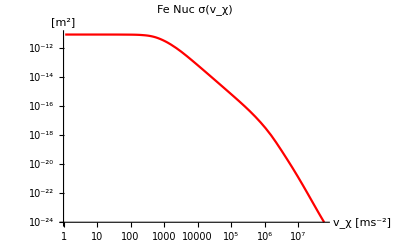

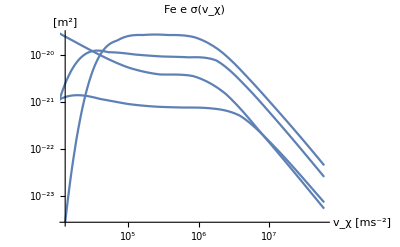

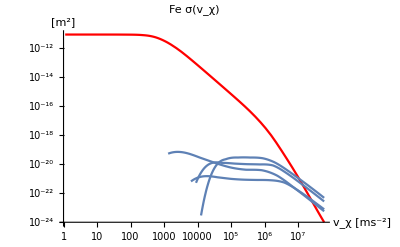

```mathematica
LogLogPlot[10^(#[Log10@vχ]),{vχ,10^(#["Domain"][[1,1]]),10^(#["Domain"][[1,2]])},PlotLabel->"Fe Nuc σ(v_χ)",AxesLabel->{"v_χ [ms^-2]","[m^2]"},PlotStyle->Red]&@FeσDictNuc[[4]]["σf"]
Show[Table[LogLogPlot[10^(#[Log10@vχ]),{vχ,10^(#["Domain"][[1,1]]),10^(#["Domain"][[1,2]])},PlotLabel->"Fe e σ(v_χ)",AxesLabel->{"v_χ [ms^-2]","[m^2]"}]&@FeσDicte[[4,i]]["σf"],{i,Length[FeσDicte[[4]]]}]]
Show[{%%,%},PlotLabel->"Fe σ(v_χ)"]
```

Not surprisingly, we see that the per target cross-section is much higher for nuclear than for electronic for a slow moving aDM probe. In the electronic plot you can also see that the cross-sections for each “shell” cuts off as the incoming speed (and so maximum E_R) drop below some threshold. This corresponds roughly to an ionization energy for the “shell”. The “shell” with the lowest threshold corresponds to the conduction electrons. In principle the minimum E_R can be arbitrarily low, but once E_R < O(meV) phonons become important and our model breaks down, so we cutoff the cross-section regardless (in the case of the silicates, which are insulators, this happens because we run into a band gap).

Note that each interpolation function comes with a list of keys (accessed by calling [“Methods”] on the interpolating function) that can be used to access information such as the domain of validity, or the points at which the function was evaluated etc. We used the domain method above when plotting.

```mathematica
(FeσDictNuc[[4]]["dσf"])["Methods"]
```

{Coordinates,DerivativeOrder,Domain,ElementMesh,Evaluate,GetPolynomial,Grid,IndexedElementEvaluate,InterpolationMethod,InterpolationOrder,MethodInformation,Methods,OutputDimensions,ParameterAddress,Periodicity,PlottableQ,Properties,QuantityUnits,Unpack,ValuesOnGrid,VectorEvaluate}

The prescription for summing cross-section across targets is to weight them by the target density. If this sum isn’t normalized this gives the inverse interaction length of the material. So for Iron we have for the interaction length (remembering to restrict each shell to it’s domain)

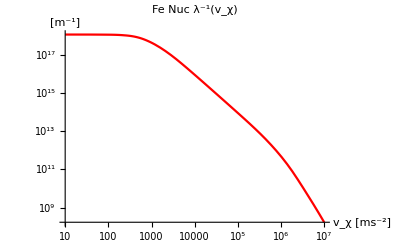

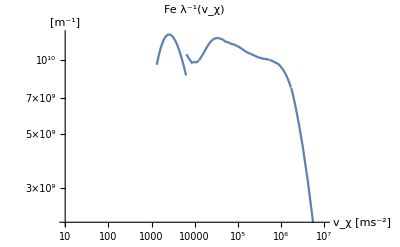

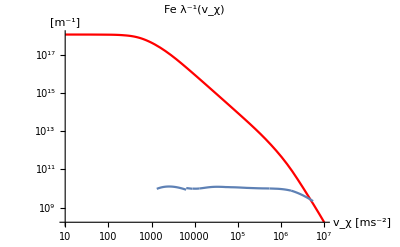

```mathematica
Quiet["nI"10^("σf"[Log10@#])Boole["σf"["Domain"][[1,1]]<Log10@#<"σf"["Domain"][[1,2]]]/.FeσDictNuc[[4]]/.FeσDictNuc[[4]]["NucleusParams"]]&(*[10^5]*);
Pnuc = Quiet@LogLogPlot[%@vχ,{vχ,10^1,10^7},PlotStyle->Red,PlotLabel->"Fe Nuc λ^-1(v_χ)",AxesLabel->{"v_χ [ms^-2]","[m^-1]"}]
Quiet@Sum["ne"10^("σf"[Log10@#])Boole["σf"["Domain"][[1,1]]<Log10@#<"σf"["Domain"][[1,2]]]/.FeσDicte[[4,i]]/.FeσDicte[[4,i]]["params"],{i,Length[FeσDicte[[4]]]}]&;
Pe = Quiet@LogLogPlot[%@vχ,{vχ,10^1,10^7},PlotLabel->"Fe λ^-1(v_χ)",AxesLabel->{"v_χ [ms^-2]","[m^-1]"}]
Show[{Pnuc,Pe},PlotLabel->"Fe λ^-1(v_χ)"]
```

Note that the discontinuities in the electronic interaction length are physical and correspond to the aforementioned ionization thresholds.

As we might expect, since the cross-sections number density for nuclei and electrons is equal given that the materials are neutral, the previous plots of the cross-sections for the individual shells gives a good representation of the relative strengths of the total cross-sections summing over shells.

### Dark Protons

#### Scan over all masses w variable ϕ and new module

```mathematica
Solve[10^-3== 1-ϕfrac ,ϕfrac]//N
```

{{ϕfrac→0.999}}

```mathematica
ScanAllMasses[ElectronicσDicts,NuclearσDicts,FeσDictend,meDPoints,κpoints,v0Points,0.999,"PDictList_ϕE_99p9_pcnt"]
(*ScanAllMasses[ElectronicσDicts,NuclearσDicts,FeσDictend,meDPoints,κpoints,v0Points,0.65,"PDictList_ϕE_65_pcnt"]*)
(*ScanAllMasses[ElectronicσDicts,NuclearσDicts,FeσDictend,meDPoints,κpoints,v0Points,0.10,"PDictList_ϕE_10_pcnt"]*)
(*ScanAllMasses[ElectronicσDicts,NuclearσDicts,FeσDictend,meDPoints,κpoints,v0Points,0.9,"PDictList_ϕE_9_pcnt"]*)
(*ScanAllMasses[ElectronicσDicts,NuclearσDicts,FeσDictend,meDPoints,κpoints,v0Points,0.99999,"PDictList_ϕE_100_pcnt"]*)
(*ScanAllMasses[ElectronicσDicts,NuclearσDicts,FeσDictend,meDPoints,κpoints,v0Points,0.0,"PDictList_ϕE_0_pcnt"]*)
(*ScanAllMasses[ElectronicσDicts,NuclearσDicts,FeσDictend,meDPoints,κpointscollisionless,v0Points,0.0,"PDictList_ϕE_0_pcnt"]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::munfl: Exp[-8600.05] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2386.85] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2717.23] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Clear[PDictList]
```

```mathematica
(*PDictScanscomparison=ReadIt[NotebookDirectory[]<>"\Plots\26_02_2025_phiE_110_pcnt\PDictList\PDictList_ϕE_110_pcnt_0"];*)
(*PDictScanscomparison=ReadIt[NotebookDirectory[]<>"\Plots\27_02_2025_phiE_200_pcnt\PDictList\PDictList_ϕE_200_pcnt_0"];*)
(*PDictScan = ReadIt["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Plots\\27_02_2025_phiE_200_pcnt\\PDictList\\PDictList_ϕE_200_pcnt_0"]*)
(*PDictScan = ReadIt[NotebookDirectory[]<>"\Plots\27_02_2025_phiE_200_pcnt\PDictList\PDictList_ϕE_200_pcnt_0"]*)
(*PDictScan = ReadIt[NotebookDirectory[]<>"PDictList_ϕE_200_pcnt_0"]*)
(*PDictListTest=ReadIt["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\06_03_2025\\PDictList\\PDictList_savetest_0"]*)
(*PDictList = ReadIt["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_04_2025\\PDictList\\PDictList_ϕE_0_pcnt_0"]*)
PDictList = ReadIt["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_04_2025_0p0\\PDictList\\PDictList_ϕE_0_pcnt_0"]
```

```mathematica
Dimensions@PDictList
```

{10,4,7}

#### Rerun scans on existing PDicts

```mathematica
Clear[PDictScansTemp]
PDictScansTemp= {};
Block[{NuclearσDictsList,ElectronicσDictList,ElectronicEvapDict,pdicts,PDictind,Nucind,eind,endind,currentPDicts,Scandicts,analysiskeys,NcMaxdict,Ncdict,ScandictsKE},

NuclearσDictsList=NuclearσDicts;
(*NuclearσDictsList=NuclearσDictsnoFF;*)
ElectronicσDictList=ElectronicσDicts;
ElectronicEvapDict = FeσDictend;

pdicts = PDictScans;
(*pdicts = PDictScansMFP;*)
(*pdicts = PDictScansCopy;*)

pdicts = sortbymeDmpDv0[pdicts];

Monitor[
Do[
Print[p];
PDictind=FirstPosition["mpD"/.pdicts,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
currentPDicts = pdicts[[PDictind]];
Nucind = FirstPosition["mχ"/.NuclearσDictsList,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
eind = FirstPosition["mχ"/.ElectronicσDictList,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
endind = FirstPosition["mχ"/.ElectronicEvapDict,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
Scandicts={};
Do[
analysiskeys={{"Pf"},{"PfE"},{"PfNuc"},{"intλinvE"},{"intλinvNuc"}}[[1;;1]];

Ncdict = currentPDicts[[d]];
Do[
NcMaxdict =GetNcMax[Ncdict,analysiskeys[[k]]];
Ncdict=GetNc[NcMaxdict,NuclearσDictsList[[Nucind]],ElectronicσDictList[[Nucind]],ElectronicEvapDict[[endind]](*,analysiskeys[[k]],True*)];
,{k,Length[analysiskeys]}];

AppendTo[Scandicts,Ncdict];
,{d,Length[currentPDicts]}];

ScandictsKE=IterateKEchange[Flatten@Scandicts,{0.05},"α"/.Constants`SIConstRepl];

AppendTo[PDictScansTemp,ScandictsKE]

,{p,6,15}]
,p]
]
(*PDictScans=PDictScansTemp;
ClearAll[PDictScansTemp]*)

(*SaveIt[NotebookDirectory[]<>filenames[[p-5]],Scandicts]*)
```

6

$Aborted

```mathematica
(*SaveIt[NotebookDirectory[]<>"PDictList_nuc_vs_e",PDictScansTemp]*)
SaveIt[NotebookDirectory[]<>"PDictList",PDictScansTemp]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDictList_nuc_vs_e.dat

```mathematica
ExportDatFileToDir[PDictScans,outfilename,"PDictList"];
```

```mathematica
NotebookDirectory[]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\

### Get δ(δ)

#### speed up get δ

```mathematica
PDictList = ReadIt["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_04_2025_0p0\\PDictList\\PDictList_ϕE_0_pcnt_0"];
```

```mathematica
Interpolation[Table[{i,i^2},{i,10}]]
```

InterpolatingFunction[…]

```mathematica
PDictList[[3,1,4]]
```

<|Pf→InterpolatingFunction[…],κ→1/100000000000,mpD→1.78×10^-28,meD→1.78×10^-32,mχ→1.78×10^-28,mpDcap→True,vχMax→80103.6,βD→8.42612×10^19,v0→20000,ϕE→0.,PfE→InterpolatingFunction[…],PfNuc→InterpolatingFunction[…],y→InterpolatingFunction[…],CSDcap→InterpolatingFunction[…],intλinvE→InterpolatingFunction[…],intλinvNuc→InterpolatingFunction[…],dNcMaxdt→2.43192×10^14 nD,NcMax→3.39825×10^31 nD,timeenoughforequil→True,Nc→1.7884×10^19 nD,Γtotal→1.35983×10^17,ΓtotalNuc→1.35951×10^17,Γtotale→3.19303×10^13|>

```mathematica
AbsoluteTiming@getδfromPDict[PDictList[[1,1,1]]]
```

{6.18374,<|δ→1.49987,rmax→212385.,NC→9.0065×10^22,Γcap→1.46779×10^10,Γevap→1.6297×10^15,meD→1.78×10^-34,mpD→1.78×10^-30,βD→8.42612×10^21,nD→1.49985×10^7,v0→20000,κ→1/100000000000000,fD→0.05,αDbyα→1|>}

```mathematica
Vgrav[0]/Vgrav["rE"/.EarthRepl]
```

1.5

```mathematica
AbsoluteTiming@getδfromPDict[PDictList[[3,1,4]]]
```

{5.89724,<|δ→1.43461,rmax→222047.,NC→2.68233×10^24,Γcap→3.64751×10^19,Γevap→1.35983×10^17,meD→1.78×10^-32,mpD→1.78×10^-28,βD→8.42612×10^19,nD→149985.,v0→20000,κ→1/100000000000,fD→0.05,αDbyα→1|>}

#### Compute δ over list of PDicts

```mathematica
Clear[δScanList]
δScanList = {<|"δ"->10^-5,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\08_05_2025_0p99999\\PDictList\\PDictList_ϕE_100_pcnt_0"|>,
<|"δ"->1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\21_04_2025_0p0\\PDictList\\PDictList_ϕE_0_pcnt_0"|>,
<|"δ"->10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\10_05_2025_0p9\\PDictList\\PDictList_ϕE_90_pcnt_0"|>,
<|"δ"->9 10^-1,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p1\\PDictList\\PDictList_ϕE_10_pcnt_0"|>,
<|"δ"->10^-2,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\11_05_2025_0p99\\PDictList\\PDictList_ϕE_99_pcnt_0"|>,
<|"δ"->0.65,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p35\\PDictList\\PDictList_ϕE_35_pcnt_0"|>,
<|"δ"->0.35,"file"->"C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\capture\\Out\\15_05_2025_0p65\\PDictList\\PDictList_ϕE_65_pcnt_0"|>};
```

```mathematica
(*ComputeδonScan[δList_,v0ind_:1]:= Module[{returnδList,PDict,δtable},

returnδList ={};

Monitor[
Do[
Print[δList[[δ]]["δ"]];
PDict= ReadIt[δList[[δ]]["file"]][[;;9,v0ind,;;]];

δtable=Flatten[Table[Table[{Log10[("mpD"("c")^2)/("JpereV")]/.PDict[[i,j]]/.SIConstRepl,Log10["κ"]/.PDict[[i,j]],Log10@"δ"/.getδfromPDict[PDict[[i,j]]]},{i,Dimensions[PDict][[1]]}],{j,Dimensions[PDict][[2]]}],1];

PDict["δtable"]=δtable;
AppendTo[returnδList,δtable];

,{δ,Length[δList]}]
,{δ,i,j}];

returnδList
]*)
```

```mathematica
computedδscanDisk10m4=ComputeδonScan[δScanList,1]
```

FindRoot::nlnum: The function value {0.+Re[-3257.51 Capture`naDM[0.05,1.78018×10^-30] (0.000306983 Power[«2»]-0.000306983 Power[«2»] Erf[«1»]+1.34151×10^-11 Power[«2»])+325751. Capture`naDM[0.05,1.78018×10^-30] (3.06983×10^-6 Power[«2»]-3.06983×10^-6 Power[«2»] Erf[«1»]+317968. Power[«2»])]} is not a list of numbers with dimensions {1} at {Private`rmax} = {3.1855×10^13}.

ReplaceAll::reps: {FindRoot[Re[2.25396×10^-10 Boole[«1»]-3257.51 Capture`naDM[«2»] Plus[«3»]+325751. Capture`naDM[«2»] Plus[«3»]/.δ→1.×10^-7/.Private`r→Private`rmax],{Private`rmax,Evaluate[rE/Times[«2»]/.EarthRepl]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.+Re[-3257.51 Capture`naDM[0.05,1.78018×10^-30] (0.000306983 Power[«2»]-0.000306983 Power[«2»] Erf[«1»]+1.34151×10^-11 Power[«2»])+325751. Capture`naDM[0.05,1.78018×10^-30] (3.06983×10^-6 Power[«2»]-3.06983×10^-6 Power[«2»] Erf[«1»]+317968. Power[«2»])]} is not a list of numbers with dimensions {1} at {Private`rmax} = {3.1855×10^13}.

ReplaceAll::reps: {FindRoot[Re[2.25396×10^-10 Boole[«1»]-3257.51 Capture`naDM[«2»] Plus[«3»]+325751. Capture`naDM[«2»] Plus[«3»]/.δ→1.×10^-7/.Private`r→Private`rmax],{Private`rmax,Evaluate[rE/Times[«2»]/.EarthRepl]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.+Re[-3257.51 Capture`naDM[0.05,1.78018×10^-30] (0.000306983 Power[«2»]-0.000306983 Power[«2»] Erf[«1»]+1.34151×10^-11 Power[«2»])+325751. Capture`naDM[0.05,1.78018×10^-30] (3.06983×10^-6 Power[«2»]-3.06983×10^-6 Power[«2»] Erf[«1»]+317968. Power[«2»])]} is not a list of numbers with dimensions {1} at {Private`rmax} = {3.1855×10^13}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Re[2.25396×10^-10 Boole[«1»]-3257.51 Capture`naDM[«2»] Plus[«3»]+325751. Capture`naDM[«2»] Plus[«3»]/.δ→1.×10^-7/.Private`r→Private`rmax],{Private`rmax,Evaluate[rE/Times[«2»]/.EarthRepl]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::nlim: Private`r = Private`rmax/.FindRoot[Re[2.25396×10^-10 Boole[«1»]-3257.51 Capture`naDM[«2»] Plus[«3»]+325751. Capture`naDM[«2»] Plus[«3»]/.δ→1.×10^-7/.Private`r→Private`rmax],{Private`rmax,Evaluate[rE/Times[«2»]/.EarthRepl]}] is not a valid limit of integration.

$Aborted

```mathematica
Table[Append[computedδscanDisk10m4[[i]],<|"meDbympD"->10^-4,"v0"->20 10^3|>],{i, Length[computedδscanDisk10m4]}]
SaveIt[NotebookDirectory[]<>"δscanDisk10m4",%]
```

{<|δ→1/100000,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\08_05_2025_0p99999\PDictList\PDictList_ϕE_100_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.12491},{7.,-Log[100000000000000]/Log[10],-0.125128},{8.,-Log[100000000000000]/Log[10],-0.126585},{9.,-Log[100000000000000]/Log[10],-0.124913},{10.,-Log[100000000000000]/Log[10],-0.124921},{11.,-Log[100000000000000]/Log[10],-0.124918},{12.,-Log[100000000000000]/Log[10],-0.124904},{13.,-Log[100000000000000]/Log[10],-0.123942},{14.,-Log[100000000000000]/Log[10],-0.037364},{6.,-Log[10000000000000]/Log[10],-0.124988},{7.,-Log[10000000000000]/Log[10],-0.126366},{8.,-Log[10000000000000]/Log[10],-0.126586},{9.,-Log[10000000000000]/Log[10],-0.124913},{10.,-Log[10000000000000]/Log[10],-0.124926},{11.,-Log[10000000000000]/Log[10],-0.12493},{12.,-Log[10000000000000]/Log[10],-0.124913},{13.,-Log[10000000000000]/Log[10],-0.123951},{14.,-Log[10000000000000]/Log[10],-0.0373915},{6.,-Log[1000000000000]/Log[10],-0.125478},{7.,-Log[1000000000000]/Log[10],-0.126572},{8.,-Log[1000000000000]/Log[10],-0.127137},{9.,-Log[1000000000000]/Log[10],-0.124914},{10.,-Log[1000000000000]/Log[10],-0.125542},{11.,-Log[1000000000000]/Log[10],-0.125366},{12.,-Log[1000000000000]/Log[10],-0.125148},{13.,-Log[1000000000000]/Log[10],-0.124173},{14.,-Log[1000000000000]/Log[10],-0.0705616},{6.,-Log[100000000000]/Log[10],-0.126562},{7.,-Log[100000000000]/Log[10],-0.127149},{8.,-Log[100000000000]/Log[10],-0.126969},{9.,-Log[100000000000]/Log[10],-1.41754},{10.,-Log[100000000000]/Log[10],-0.134682},{11.,-Log[100000000000]/Log[10],-0.129363},{12.,-Log[100000000000]/Log[10],-0.656385},{13.,-Log[100000000000]/Log[10],-0.595915},{14.,-Log[100000000000]/Log[10],-0.654855},{6.,-Log[10000000000]/Log[10],-0.127103},{7.,-Log[10000000000]/Log[10],-0.126939},{8.,-Log[10000000000]/Log[10],-2.97662},{9.,-Log[10000000000]/Log[10],-3.1853},{10.,-Log[10000000000]/Log[10],-2.31416},{11.,-Log[10000000000]/Log[10],-1.80764},{12.,-Log[10000000000]/Log[10],-1.64698},{13.,-Log[10000000000]/Log[10],-1.60416},{14.,-Log[10000000000]/Log[10],-1.86486},{6.,-Log[1000000000]/Log[10],-0.126936},{7.,-Log[1000000000]/Log[10],-0.137406},{8.,-Log[1000000000]/Log[10],-4.92917},{9.,-Log[1000000000]/Log[10],-4.47223},{10.,-Log[1000000000]/Log[10],-3.78984},{11.,-Log[1000000000]/Log[10],-3.11621},{12.,-Log[1000000000]/Log[10],-2.76882},{13.,-Log[1000000000]/Log[10],-2.66178},{14.,-Log[1000000000]/Log[10],-2.92654},{6.,-Log[100000000]/Log[10],-0.136119},{7.,-Log[100000000]/Log[10],-5.42384},{8.,-Log[100000000]/Log[10],-4.92917},{9.,-Log[100000000]/Log[10],-4.47223},{10.,-Log[100000000]/Log[10],-4.20956},{11.,-Log[100000000]/Log[10],-4.29487},{12.,-Log[100000000]/Log[10],-4.24791},{13.,-Log[100000000]/Log[10],-3.99087},{14.,-Log[100000000]/Log[10],-4.07588},{6.,-Log[10000000]/Log[10],-5.92304},{7.,-Log[10000000]/Log[10],-5.42384},{8.,-Log[10000000]/Log[10],-4.92917},{9.,-Log[10000000]/Log[10],-4.47223},{10.,-Log[10000000]/Log[10],-4.20956},{11.,-Log[10000000]/Log[10],-4.29482},{12.,-Log[10000000]/Log[10],-4.66732},{13.,-Log[10000000]/Log[10],-5.17262},{14.,-Log[10000000]/Log[10],-5.56424}},meDbympD→1/10000,v0→20000|>,<|δ→1,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\21_04_2025_0p0\PDictList\PDictList_ϕE_0_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.127907},{7.,-Log[100000000000000]/Log[10],-0.182668},{8.,-Log[100000000000000]/Log[10],-0.194304},{9.,-Log[100000000000000]/Log[10],-0.243558},{10.,-Log[100000000000000]/Log[10],-2.0968},{11.,-Log[100000000000000]/Log[10],-2.06942},{12.,-Log[100000000000000]/Log[10],-1.53343},{13.,-Log[100000000000000]/Log[10],-1.0626},{14.,-Log[100000000000000]/Log[10],-0.590395},{6.,-Log[10000000000000]/Log[10],-0.127907},{7.,-Log[10000000000000]/Log[10],-0.182668},{8.,-Log[10000000000000]/Log[10],-0.214568},{9.,-Log[10000000000000]/Log[10],-0.267022},{10.,-Log[10000000000000]/Log[10],-2.17129},{11.,-Log[10000000000000]/Log[10],-3.14328},{12.,-Log[10000000000000]/Log[10],-2.58704},{13.,-Log[10000000000000]/Log[10],-2.00346},{14.,-Log[10000000000000]/Log[10],-1.51638},{6.,-Log[1000000000000]/Log[10],-0.127907},{7.,-Log[1000000000000]/Log[10],-0.200844},{8.,-Log[1000000000000]/Log[10],-0.216016},{9.,-Log[1000000000000]/Log[10],-0.269047},{10.,-Log[1000000000000]/Log[10],-2.18272},{11.,-Log[1000000000000]/Log[10],-4.15405},{12.,-Log[1000000000000]/Log[10],-3.62177},{13.,-Log[1000000000000]/Log[10],-3.11841},{14.,-Log[1000000000000]/Log[10],-2.58232},{6.,-Log[100000000000]/Log[10],-0.12828},{7.,-Log[100000000000]/Log[10],-0.201685},{8.,-Log[100000000000]/Log[10],-0.204789},{9.,-Log[100000000000]/Log[10],-0.263423},{10.,-Log[100000000000]/Log[10],-2.3171},{11.,-Log[100000000000]/Log[10],-5.1359},{12.,-Log[100000000000]/Log[10],-4.60123},{13.,-Log[100000000000]/Log[10],-4.09997},{14.,-Log[100000000000]/Log[10],-3.60378},{6.,-Log[10000000000]/Log[10],-0.12889},{7.,-Log[10000000000]/Log[10],-0.209614},{8.,-Log[10000000000]/Log[10],-0.673298},{9.,-Log[10000000000]/Log[10],-0.94909},{10.,-Log[10000000000]/Log[10],-6.62512},{11.,-Log[10000000000]/Log[10],-6.0979},{12.,-Log[10000000000]/Log[10],-5.53833},{13.,-Log[10000000000]/Log[10],-5.03361},{14.,-Log[10000000000]/Log[10],-4.53367},{6.,-Log[1000000000]/Log[10],-0.207},{7.,-Log[1000000000]/Log[10],-0.963693},{8.,-Log[1000000000]/Log[10],-2.02167},{9.,-Log[1000000000]/Log[10],-2.27059},{10.,-Log[1000000000]/Log[10],-8.07917},{11.,-Log[1000000000]/Log[10],-7.31539},{12.,-Log[1000000000]/Log[10],-6.5511},{13.,-Log[1000000000]/Log[10],-5.94641},{14.,-Log[1000000000]/Log[10],-5.43219},{6.,-Log[100000000]/Log[10],-0.724239},{7.,-Log[100000000]/Log[10],-2.39025},{8.,-Log[100000000]/Log[10],-2.02165},{9.,-Log[100000000]/Log[10],-2.29913},{10.,-Log[100000000]/Log[10],-8.35105},{11.,-Log[100000000]/Log[10],-8.35105},{12.,-Log[100000000]/Log[10],-8.10595},{13.,-Log[100000000]/Log[10],-7.26171},{14.,-Log[100000000]/Log[10],-6.54935},{6.,-Log[10000000]/Log[10],-3.56431},{7.,-Log[10000000]/Log[10],-4.29226},{8.,-Log[10000000]/Log[10],-2.02165},{9.,-Log[10000000]/Log[10],-4.20351},{10.,-Log[10000000]/Log[10],-8.35105},{11.,-Log[10000000]/Log[10],-8.35105},{12.,-Log[10000000]/Log[10],-8.35105},{13.,-Log[10000000]/Log[10],-8.35105},{14.,-Log[10000000]/Log[10],-8.10665}},meDbympD→1/10000,v0→20000|>,<|δ→1/10,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\10_05_2025_0p9\PDictList\PDictList_ϕE_90_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.125168},{7.,-Log[100000000000000]/Log[10],-0.131697},{8.,-Log[100000000000000]/Log[10],-0.139031},{9.,-Log[100000000000000]/Log[10],-0.144321},{10.,-Log[100000000000000]/Log[10],-0.153575},{11.,-Log[100000000000000]/Log[10],-1.17789},{12.,-Log[100000000000000]/Log[10],-1.51143},{13.,-Log[100000000000000]/Log[10],-1.04699},{14.,-Log[100000000000000]/Log[10],-0.583487},{6.,-Log[10000000000000]/Log[10],-0.125168},{7.,-Log[10000000000000]/Log[10],-0.131697},{8.,-Log[10000000000000]/Log[10],-0.143028},{9.,-Log[10000000000000]/Log[10],-0.144568},{10.,-Log[10000000000000]/Log[10],-0.155935},{11.,-Log[10000000000000]/Log[10],-1.20263},{12.,-Log[10000000000000]/Log[10],-2.59518},{13.,-Log[10000000000000]/Log[10],-2.07069},{14.,-Log[10000000000000]/Log[10],-1.51931},{6.,-Log[1000000000000]/Log[10],-0.125168},{7.,-Log[1000000000000]/Log[10],-0.133827},{8.,-Log[1000000000000]/Log[10],-0.143264},{9.,-Log[1000000000000]/Log[10],-0.144244},{10.,-Log[1000000000000]/Log[10],-0.155894},{11.,-Log[1000000000000]/Log[10],-1.20282},{12.,-Log[1000000000000]/Log[10],-3.58473},{13.,-Log[1000000000000]/Log[10],-3.08886},{14.,-Log[1000000000000]/Log[10],-2.59511},{6.,-Log[100000000000]/Log[10],-0.125168},{7.,-Log[100000000000]/Log[10],-0.133937},{8.,-Log[100000000000]/Log[10],-0.141664},{9.,-Log[100000000000]/Log[10],-0.15673},{10.,-Log[100000000000]/Log[10],-0.192903},{11.,-Log[100000000000]/Log[10],-5.01714},{12.,-Log[100000000000]/Log[10],-4.51361},{13.,-Log[100000000000]/Log[10],-4.0148},{14.,-Log[100000000000]/Log[10],-3.51752},{6.,-Log[10000000000]/Log[10],-0.125257},{7.,-Log[10000000000]/Log[10],-0.141561},{8.,-Log[10000000000]/Log[10],-0.570461},{9.,-Log[10000000000]/Log[10],-0.512343},{10.,-Log[10000000000]/Log[10],-0.726571},{11.,-Log[10000000000]/Log[10],-5.94146},{12.,-Log[10000000000]/Log[10],-5.41378},{13.,-Log[10000000000]/Log[10],-4.89223},{14.,-Log[10000000000]/Log[10],-4.38872},{6.,-Log[1000000000]/Log[10],-0.143695},{7.,-Log[1000000000]/Log[10],-0.237688},{8.,-Log[1000000000]/Log[10],-2.12036},{9.,-Log[1000000000]/Log[10],-1.90903},{10.,-Log[1000000000]/Log[10],-2.07837},{11.,-Log[1000000000]/Log[10],-7.31418},{12.,-Log[1000000000]/Log[10],-6.57362},{13.,-Log[1000000000]/Log[10],-5.92404},{14.,-Log[1000000000]/Log[10],-5.39611},{6.,-Log[100000000]/Log[10],-0.537591},{7.,-Log[100000000]/Log[10],-4.5043},{8.,-Log[100000000]/Log[10],-2.19699},{9.,-Log[100000000]/Log[10],-1.90903},{10.,-Log[100000000]/Log[10],-4.32339},{11.,-Log[100000000]/Log[10],-8.32125},{12.,-Log[100000000]/Log[10],-7.99167},{13.,-Log[100000000]/Log[10],-7.31576},{14.,-Log[100000000]/Log[10],-6.57458},{6.,-Log[10000000]/Log[10],-2.76291},{7.,-Log[10000000]/Log[10],-4.5043},{8.,-Log[10000000]/Log[10],-4.03649},{9.,-Log[10000000]/Log[10],-3.84586},{10.,-Log[10000000]/Log[10],-4.32339},{11.,-Log[10000000]/Log[10],-8.32125},{12.,-Log[10000000]/Log[10],-8.32125},{13.,-Log[10000000]/Log[10],-8.32125},{14.,-Log[10000000]/Log[10],-7.99283}},meDbympD→1/10000,v0→20000|>,<|δ→9/10,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\11_05_2025_0p1\PDictList\PDictList_ϕE_10_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.127279},{7.,-Log[100000000000000]/Log[10],-0.170404},{8.,-Log[100000000000000]/Log[10],-0.183757},{9.,-Log[100000000000000]/Log[10],-0.234182},{10.,-Log[100000000000000]/Log[10],-1.81506},{11.,-Log[100000000000000]/Log[10],-2.08245},{12.,-Log[100000000000000]/Log[10],-1.5692},{13.,-Log[100000000000000]/Log[10],-1.09661},{14.,-Log[100000000000000]/Log[10],-0.634502},{6.,-Log[10000000000000]/Log[10],-0.127279},{7.,-Log[10000000000000]/Log[10],-0.170404},{8.,-Log[10000000000000]/Log[10],-0.202756},{9.,-Log[10000000000000]/Log[10],-0.252847},{10.,-Log[10000000000000]/Log[10],-1.89634},{11.,-Log[10000000000000]/Log[10],-3.15946},{12.,-Log[10000000000000]/Log[10],-2.62119},{13.,-Log[10000000000000]/Log[10],-2.03952},{14.,-Log[10000000000000]/Log[10],-1.56136},{6.,-Log[1000000000000]/Log[10],-0.127279},{7.,-Log[1000000000000]/Log[10],-0.185355},{8.,-Log[1000000000000]/Log[10],-0.204048},{9.,-Log[1000000000000]/Log[10],-0.254874},{10.,-Log[1000000000000]/Log[10],-1.9067},{11.,-Log[1000000000000]/Log[10],-4.17161},{12.,-Log[1000000000000]/Log[10],-3.65354},{13.,-Log[1000000000000]/Log[10],-3.15136},{14.,-Log[1000000000000]/Log[10],-2.63724},{6.,-Log[100000000000]/Log[10],-0.12728},{7.,-Log[100000000000]/Log[10],-0.186082},{8.,-Log[100000000000]/Log[10],-0.195163},{9.,-Log[100000000000]/Log[10],-0.248391},{10.,-Log[100000000000]/Log[10],-2.09292},{11.,-Log[100000000000]/Log[10],-5.14589},{12.,-Log[100000000000]/Log[10],-4.62469},{13.,-Log[100000000000]/Log[10],-4.12413},{14.,-Log[100000000000]/Log[10],-3.62645},{6.,-Log[10000000000]/Log[10],-0.128042},{7.,-Log[10000000000]/Log[10],-0.193218},{8.,-Log[10000000000]/Log[10],-0.627775},{9.,-Log[10000000000]/Log[10],-1.00347},{10.,-Log[10000000000]/Log[10],-6.61642},{11.,-Log[10000000000]/Log[10],-6.09682},{12.,-Log[10000000000]/Log[10],-5.55473},{13.,-Log[10000000000]/Log[10],-5.05024},{14.,-Log[10000000000]/Log[10],-4.55063},{6.,-Log[1000000000]/Log[10],-0.191882},{7.,-Log[1000000000]/Log[10],-0.722884},{8.,-Log[1000000000]/Log[10],-2.02041},{9.,-Log[1000000000]/Log[10],-2.22385},{10.,-Log[1000000000]/Log[10],-8.08259},{11.,-Log[1000000000]/Log[10],-7.36359},{12.,-Log[1000000000]/Log[10],-6.53651},{13.,-Log[1000000000]/Log[10],-5.96881},{14.,-Log[1000000000]/Log[10],-5.44551},{6.,-Log[100000000]/Log[10],-0.626251},{7.,-Log[100000000]/Log[10],-2.39775},{8.,-Log[100000000]/Log[10],-2.02039},{9.,-Log[100000000]/Log[10],-2.25297},{10.,-Log[100000000]/Log[10],-8.33237},{11.,-Log[100000000]/Log[10],-8.34825},{12.,-Log[100000000]/Log[10],-8.09582},{13.,-Log[100000000]/Log[10],-7.36019},{14.,-Log[100000000]/Log[10],-6.54721},{6.,-Log[10000000]/Log[10],-3.53835},{7.,-Log[10000000]/Log[10],-4.29999},{8.,-Log[10000000]/Log[10],-2.1523},{9.,-Log[10000000]/Log[10],-4.15676},{10.,-Log[10000000]/Log[10],-8.33237},{11.,-Log[10000000]/Log[10],-8.34825},{12.,-Log[10000000]/Log[10],-8.34825},{13.,-Log[10000000]/Log[10],-8.34825},{14.,-Log[10000000]/Log[10],-8.09658}},meDbympD→1/10000,v0→20000|>,<|δ→1/100,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\11_05_2025_0p99\PDictList\PDictList_ϕE_99_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.124935},{7.,-Log[100000000000000]/Log[10],-0.127816},{8.,-Log[100000000000000]/Log[10],-0.127847},{9.,-Log[100000000000000]/Log[10],-0.128923},{10.,-Log[100000000000000]/Log[10],-0.129123},{11.,-Log[100000000000000]/Log[10],-0.131038},{12.,-Log[100000000000000]/Log[10],-1.47827},{13.,-Log[100000000000000]/Log[10],-0.967338},{14.,-Log[100000000000000]/Log[10],-0.500856},{6.,-Log[10000000000000]/Log[10],-0.124935},{7.,-Log[10000000000000]/Log[10],-0.127816},{8.,-Log[10000000000000]/Log[10],-0.128746},{9.,-Log[10000000000000]/Log[10],-0.128981},{10.,-Log[10000000000000]/Log[10],-0.12918},{11.,-Log[10000000000000]/Log[10],-0.131131},{12.,-Log[10000000000000]/Log[10],-2.50783},{13.,-Log[10000000000000]/Log[10],-2.02783},{14.,-Log[10000000000000]/Log[10],-1.5447},{6.,-Log[1000000000000]/Log[10],-0.124935},{7.,-Log[1000000000000]/Log[10],-0.127816},{8.,-Log[1000000000000]/Log[10],-0.128786},{9.,-Log[1000000000000]/Log[10],-0.128594},{10.,-Log[1000000000000]/Log[10],-0.128982},{11.,-Log[1000000000000]/Log[10],-0.131125},{12.,-Log[1000000000000]/Log[10],-2.61433},{13.,-Log[1000000000000]/Log[10],-2.97241},{14.,-Log[1000000000000]/Log[10],-2.48105},{6.,-Log[100000000000]/Log[10],-0.124935},{7.,-Log[100000000000]/Log[10],-0.128785},{8.,-Log[100000000000]/Log[10],-0.128428},{9.,-Log[100000000000]/Log[10],-0.145203},{10.,-Log[100000000000]/Log[10],-0.142376},{11.,-Log[100000000000]/Log[10],-0.154207},{12.,-Log[100000000000]/Log[10],-4.31143},{13.,-Log[100000000000]/Log[10],-3.82336},{14.,-Log[100000000000]/Log[10],-3.32784},{6.,-Log[10000000000]/Log[10],-0.124948},{7.,-Log[10000000000]/Log[10],-0.128363},{8.,-Log[10000000000]/Log[10],-0.564224},{9.,-Log[10000000000]/Log[10],-0.707052},{10.,-Log[10000000000]/Log[10],-0.35376},{11.,-Log[10000000000]/Log[10],-0.387689},{12.,-Log[10000000000]/Log[10],-5.29214},{13.,-Log[10000000000]/Log[10],-4.8021},{14.,-Log[10000000000]/Log[10],-4.28614},{6.,-Log[1000000000]/Log[10],-0.138226},{7.,-Log[1000000000]/Log[10],-1.02095},{8.,-Log[1000000000]/Log[10],-2.31998},{9.,-Log[1000000000]/Log[10],-1.8833},{10.,-Log[1000000000]/Log[10],-1.56474},{11.,-Log[1000000000]/Log[10],-3.48863},{12.,-Log[1000000000]/Log[10],-6.53255},{13.,-Log[1000000000]/Log[10],-5.89887},{14.,-Log[1000000000]/Log[10],-5.33734},{6.,-Log[100000000]/Log[10],-0.137812},{7.,-Log[100000000]/Log[10],-4.74727},{8.,-Log[100000000]/Log[10],-4.25695},{9.,-Log[100000000]/Log[10],-3.92373},{10.,-Log[100000000]/Log[10],-3.96117},{11.,-Log[100000000]/Log[10],-4.5926},{12.,-Log[100000000]/Log[10],-7.92581},{13.,-Log[100000000]/Log[10],-7.20812},{14.,-Log[100000000]/Log[10],-6.53384},{6.,-Log[10000000]/Log[10],-2.03701},{7.,-Log[10000000]/Log[10],-4.74726},{8.,-Log[10000000]/Log[10],-4.25695},{9.,-Log[10000000]/Log[10],-3.92373},{10.,-Log[10000000]/Log[10],-3.96117},{11.,-Log[10000000]/Log[10],-4.5926},{12.,-Log[10000000]/Log[10],-8.31522},{13.,-Log[10000000]/Log[10],-8.31522},{14.,-Log[10000000]/Log[10],-7.92718}},meDbympD→1/10000,v0→20000|>}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\δscanDisk10m4.dat

```mathematica
computedδscanDisk10m4=ReadIt[NotebookDirectory[]<>"δscanDisk10m4"];
```

{{56}}

{{-5.,-5.42384},{0.,-2.39025},{-1.,-4.5043},{-0.0457575,-2.39775},{-2.,-4.74727}}

InterpolatingFunction::dmval: Input value {-5.99988} lies outside the range of data in the interpolating function. Extrapolation will be used.

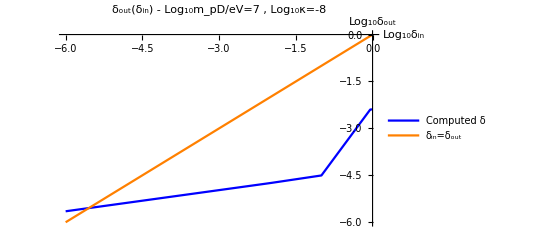

InterpolatingFunction::dmval: Input value {-5.47487} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.54599} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.54726} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{δ→2.83619×10^-6}

-5.54726

```mathematica
("δtable"/.computedδscanDisk10m4[[1]])[[;;,;;2]]//N//Round;
Position[%,{7,-8}]
Quiet@Table[{Log10@"δ","δtable"[[%[[1,1]],3]]}/.computedδscanDisk10m4[[i]],{i,Length[computedδscanDisk10m4]}]//N
(*ListPlot[10^%,PlotRange->{0,1}]*)
Interpolation[%,InterpolationOrder->1];
(*Plot[10^%[Log10@δ],{δ,0,1},PlotRange->{{-0.1,1.1},{-0.1,1.1}}]*)
(*Out[-4][[Out[-3][[1,1]]]]*)
Plot[{%[δ],δ},{δ,-6,0},PlotRange->All,AxesLabel->{"Log_10δ_in","Log_10δ_out"},(*PlotLabel->StringForm["δ_out(δ_in) - m_eD/m_pD=`` , κ=``",#[[1]],#[[2]]]&[Out[-4][[Out[-3][[1,1]]]]]*)PlotLabel->StringForm["δ_out(δ_in) - Log_10m_pD/eV=`` , Log_10κ=``",Out[-4][[Out[-3][[1,1]]]][[1]],Out[-4][[Out[-3][[1,1]]]][[2]]],PlotStyle->{Blue,Orange},PlotLegends->LineLegend[{Blue,Orange},{"Computed δ","δ_in=δ_out"}]]
FindRoot[10^%%[Log10@δ]-δ,{δ,0.01}]
Log10@δ/.%
```

```mathematica
(*("δtable"/.computedδscanDisk10m4[[1]])[[;;,;;2]]//N//Round;
Position[%,{13,-8}]
Quiet@Table[{Log10@"δ","δtable"[[%[[1,1]],3]]}/.computedδscanDisk10m4[[i]],{i,Length[computedδscanDisk10m4]}]//N
(*ListPlot[10^%,PlotRange->{0,1}]*)
Interpolation[%,InterpolationOrder->1];
(*Plot[10^%[Log10@δ],{δ,0,1},PlotRange->{{-0.1,1.1},{-0.1,1.1}}]*)
Plot[{%[δ],δ},{δ,-5,0},PlotRange->All]
FindRoot[10^%%[Log10@δ]-δ,{δ,0.1}]
Log10@δ/.%*)

(*GetδTruth[δScan_]:=Module[{δtruthtable,δoutofδintable,δoutofδin,δtruth},

δtruthtable ={};

Do[
(*Print@Union[δScan[[;;]]["δtable"][[i,;;2]]//N//Round];*)
δoutofδintable =Table[Log10@"δ"/.δScan[[j]],δScan[[j]]["δtable"][[i,3]],{j,Length[δScan]}];
δoutofδin = Interpolation[δoutofδintable,InterpolationOrder->1];
δtruth = δ/.FindRoot[10^δoutofδin[Log10@δ]-δ,{δ,0.1}];
AppendTo[δtruthtable,{δScan[[1]]["δtable"][[i,1]],δScan[[1]]["δtable"][[i,3]],δtruth}];
,{i,Length[δScan[[1]]["δtable"]]}];(*assuming all δtables have the same ordering size*)

δtruthtable
]*)
```

FindRoot::nlnum: The function value {0.0560129+10^(InterpolatingFunction[{{-5.,0.}},{5,7,0,{5},{2},0,0,0,0,Automatic,«3»},{{-«18»,«3»,0.}},{Developer`PackedArrayForm,{0,1,2,3,4,5},{-3.1853,-0.707052,-0.512343,-1.00347,-0.94909}},{Automatic}][«1»])} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.0560129}.

InterpolatingFunction::dmval: Input value {-5.24231} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::nlnum: The function value {0.00319528+10^(InterpolatingFunction[{{-5.,0.}},{5,7,0,{5},{2},0,0,0,0,Automatic,«3»},{{-«18»,«4»}},{Developer`PackedArrayForm,{0,1,2,3,4,5},{-0.137406,-1.02095,-0.237688,-0.722884,-0.963693}},{Automatic}][«1»])} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.00319528}.

InterpolatingFunction::dmval: Input value {-6.51508} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-6.12211} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::nlnum: The function value {0.0000593359+10^(InterpolatingFunction[{{-5.,0.}},{5,7,0,{5},{2},0,0,0,0,Automatic,«3»},{{-«18»,«3»,0.}},{Developer`PackedArrayForm,{0,1,2,3,4,5},{-4.92917,-4.25695,-2.19699,-2.02039,-2.02165}},{Automatic}][«1»])} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.0000593359}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

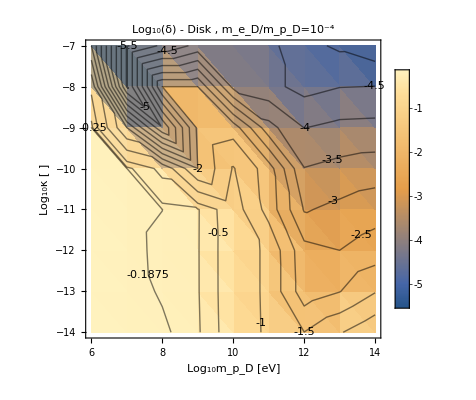

```mathematica
δtruthdisk = GetδTruth[computedδscanDisk10m4];
(*ListContourPlot[δtruth,ContourLabels->All]*)
Show[{ListDensityPlot[δtruthdisk,PlotLegends->Automatic,PlotLabel->"Log_10(δ) - Disk , m_e_D/m_p_D=10^-4",FrameLabel->{"Log_10m_p_D [eV]","Log_10κ [ ]"}],ListContourPlot[δtruthdisk,ContourLabels->All,ContourShading->False,Contours->Join[Table[i,{i,-0.25,0,0.0625}],Table[i,{i,-9,-0.5,0.5}]]],
ListContourPlot[δtruthdisk,Contours->{0},ContourStyle->Directive[Red,Thick],ContourLabels->True,ContourShading->None]}]
(*ListContourPlot[Table[δtruth,ContourLabels->All]*)
```

{{{6,-14,-13.5491},{6,-13,-11.5491},{6,-12,-9.54907},{6,-11,-7.54907},{6,-10,-5.54907},{6,-9,-3.54907},{6,-8,-1.54907},{6,-7,0.450927}},{{7,-14,-10.558},{7,-13,-8.55796},{7,-12,-6.55796},{7,-11,-4.55796},{7,-10,-2.55796},{7,-9,-0.557963},{7,-8,1.44204},{7,-7,3.44204}},{{8,-14,-8.09656},{8,-13,-6.09656},{8,-12,-4.09656},{8,-11,-2.09656},{8,-10,-0.0965645},{8,-9,1.90344},{8,-8,3.90344},{8,-7,5.90344}},{{9,-14,-7.60598},{9,-13,-5.60598},{9,-12,-3.60598},{9,-11,-1.60598},{9,-10,0.394023},{9,-9,2.39402},{9,-8,4.39402},{9,-7,6.39402}},{{10,-14,-8.15952},{10,-13,-6.15952},{10,-12,-4.15952},{10,-11,-2.15952},{10,-10,-0.159518},{10,-9,1.84048},{10,-8,3.84048},{10,-7,5.84048}},{{11,-14,-9.00686},{11,-13,-7.00686},{11,-12,-5.00686},{11,-11,-3.00686},{11,-10,-1.00686},{11,-9,0.993135},{11,-8,2.99314},{11,-7,4.99314}},{{12,-14,-9.97474},{12,-13,-7.97474},{12,-12,-5.97474},{12,-11,-3.97474},{12,-10,-1.97474},{12,-9,0.0252611},{12,-8,2.02526},{12,-7,4.02526}},{{13,-14,-10.9706},{13,-13,-8.97055},{13,-12,-6.97055},{13,-11,-4.97055},{13,-10,-2.97055},{13,-9,-0.970551},{13,-8,1.02945},{13,-7,3.02945}},{{14,-14,-11.9702},{14,-13,-9.9702},{14,-12,-7.9702},{14,-11,-5.9702},{14,-10,-3.9702},{14,-9,-1.9702},{14,-8,0.0298009},{14,-7,2.0298}},{{15,-14,-12.9702},{15,-13,-10.9702},{15,-12,-8.97016},{15,-11,-6.97016},{15,-10,-4.97016},{15,-9,-2.97016},{15,-8,-0.970164},{15,-7,1.02984}}}

Red contour is lower boundary of the thermalized regime (we expect > O(1) energy lost in the Earth for 1% of the incoming dark proton distribution)

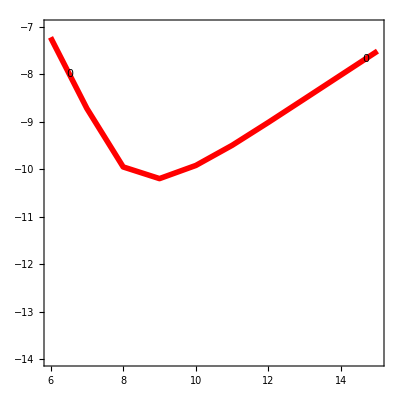

```mathematica
Eatvcutdisk=Table[
eind = FirstPosition["mχ"/.ElectronicσDicts,10^# ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]&@mind;
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^# ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]&@mind;

mχt=10^mind ("JpereV")/("c")^2/.Constants`SIConstRepl;
βDdict=Capture`v0toβD[20 10^3,#,10^-4#]&[mχt];
(*βDdict={"βD"->6/((1+10^-4)mχt (20 10^3)^2)};*)
vχcut = Capture`GetvχMax[1-10^-2,(*"βcore"/.EarthRepl*)"βD"/.βDdict,mχt,0 "vesc"/.EarthRepl];
(*Print[vχcut];*)

Eofv[vχ_?NumberQ]:=("rE"/.Constants`EarthRepl)("dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]]])[10^6,vχ]/((10^mind ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2(*-3/("βcore")*)/.EarthRepl);
{mind,mlogκ,Log10[10^(2 mlogκ) Eofv[vχcut(*+"vesc"*)] /.EarthRepl]},{mind,6,15},{mlogκ,-14,-7}]
"Red contour is lower boundary of the thermalized regime (we expect > O(1) energy lost in the Earth for 1% of the incoming dark proton distribution)"
Show[{(*ListContourPlot[Flatten[Eatvcutdisk,1],ContourLabels->True,PlotLabel->"(<E>)/E_K 1st v percentile - Core Disk",FrameLabel->{"Log_10m_p_D [eV]","Log_10κ [ ]"}],*)ListContourPlot[Flatten[Eatvcutdisk,1],ContourLabels->True,Contours->{0},ContourStyle->Directive[Red,Thickness[0.01],Opacity[1]],ContourShading->False]}]
```

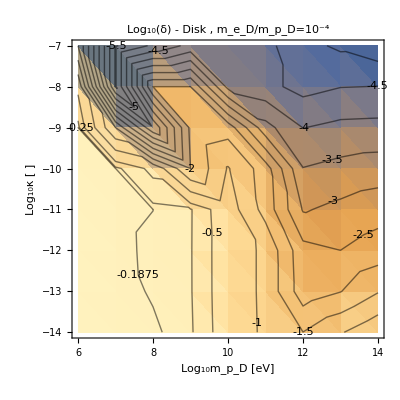
```mathematica
P1 = -Graphics-;
P2 = -Graphics-;
Show[{P1,P2}]
```

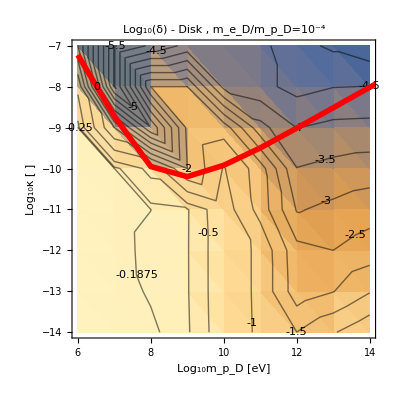

HALO

```mathematica
{"v0","meD"/"mpD"}/.ReadIt[δScanList[[1]]["file"]][[;;9,3,;;]]
```

{{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}},{{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01},{20000,0.01}}}

```mathematica
computedδscanhalo10m4=ComputeδonScan[δScanList,2]
SaveIt[NotebookDirectory[]<>"δscanhalo10m4",computedδscanhalo10m4]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {Private`rmax} = {3.1855×10^13}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {1.} is at the edge of the search region {1.×10^-10,1.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Private`r near {Private`r} = {2.88681×10^16}. NIntegrate obtained 1.25634×10^44 and 1.15359×10^39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Private`r near {Private`r} = {2.88681×10^16}. NIntegrate obtained 1.25634×10^44 and 1.15359×10^39 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Private`r near {Private`r} = {2.88681×10^16}. NIntegrate obtained 1.25634×10^44 and 1.15359×10^39 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Finished running the PDicts for: 
{v0,meD/mpD}={220000,0.0001}

{<|δ→1/100000,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\08_05_2025_0p99999\PDictList\PDictList_ϕE_100_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.124896},{7.,-Log[100000000000000]/Log[10],-0.125164},{8.,-Log[100000000000000]/Log[10],-0.126853},{9.,-Log[100000000000000]/Log[10],-0.124911},{10.,-Log[100000000000000]/Log[10],-0.124925},{11.,-Log[100000000000000]/Log[10],-0.124915},{12.,-Log[100000000000000]/Log[10],-0.124307},{13.,-Log[100000000000000]/Log[10],-0.0679524},{14.,-Log[100000000000000]/Log[10],0.},{6.,-Log[10000000000000]/Log[10],-0.124895},{7.,-Log[10000000000000]/Log[10],-0.126592},{8.,-Log[10000000000000]/Log[10],-0.126853},{9.,-Log[10000000000000]/Log[10],-0.124916},{10.,-Log[10000000000000]/Log[10],-0.124931},{11.,-Log[10000000000000]/Log[10],-0.124931},{12.,-Log[10000000000000]/Log[10],-0.124319},{13.,-Log[10000000000000]/Log[10],-0.0679615},{14.,-Log[10000000000000]/Log[10],0.},{6.,-Log[1000000000000]/Log[10],-0.124895},{7.,-Log[1000000000000]/Log[10],-0.126828},{8.,-Log[1000000000000]/Log[10],-0.127431},{9.,-Log[1000000000000]/Log[10],-0.124917},{10.,-Log[1000000000000]/Log[10],-0.12568},{11.,-Log[1000000000000]/Log[10],-0.12532},{12.,-Log[1000000000000]/Log[10],-0.124624},{13.,-Log[1000000000000]/Log[10],-0.0681772},{14.,-Log[1000000000000]/Log[10],0.},{6.,-Log[100000000000]/Log[10],-0.124895},{7.,-Log[100000000000]/Log[10],-0.127375},{8.,-Log[100000000000]/Log[10],-0.12728},{9.,-Log[100000000000]/Log[10],-1.5819},{10.,-Log[100000000000]/Log[10],-0.135182},{11.,-Log[100000000000]/Log[10],-0.130224},{12.,-Log[100000000000]/Log[10],-0.712651},{13.,-Log[100000000000]/Log[10],-0.617292},{14.,-Log[100000000000]/Log[10],0.},{6.,-Log[10000000000]/Log[10],-0.124895},{7.,-Log[10000000000]/Log[10],-0.127238},{8.,-Log[10000000000]/Log[10],-3.07723},{9.,-Log[10000000000]/Log[10],-2.95563},{10.,-Log[10000000000]/Log[10],-2.35681},{11.,-Log[10000000000]/Log[10],-1.9487},{12.,-Log[10000000000]/Log[10],-1.82834},{13.,-Log[10000000000]/Log[10],-1.79363},{14.,-Log[10000000000]/Log[10],-1.99744},{6.,-Log[1000000000]/Log[10],-0.124895},{7.,-Log[1000000000]/Log[10],-0.139951},{8.,-Log[1000000000]/Log[10],-4.6425},{9.,-Log[1000000000]/Log[10],-4.14302},{10.,-Log[1000000000]/Log[10],-3.40893},{11.,-Log[1000000000]/Log[10],-2.98989},{12.,-Log[1000000000]/Log[10],-2.86312},{13.,-Log[1000000000]/Log[10],-2.87138},{14.,-Log[1000000000]/Log[10],-3.14268},{6.,-Log[100000000]/Log[10],-0.137764},{7.,-Log[100000000]/Log[10],-6.77845},{8.,-Log[100000000]/Log[10],-6.22856},{9.,-Log[100000000]/Log[10],-5.30736},{10.,-Log[100000000]/Log[10],-4.46896},{11.,-Log[100000000]/Log[10],-4.01158},{12.,-Log[100000000]/Log[10],-3.86836},{13.,-Log[100000000]/Log[10],-3.86976},{14.,-Log[100000000]/Log[10],-4.18036},{6.,-Log[10000000]/Log[10],-7.43982},{7.,-Log[10000000]/Log[10],-6.9403},{8.,-Log[10000000]/Log[10],-6.44509},{9.,-Log[10000000]/Log[10],-5.98729},{10.,-Log[10000000]/Log[10],-5.56405},{11.,-Log[10000000]/Log[10],-5.13091},{12.,-Log[10000000]/Log[10],-4.92921},{13.,-Log[10000000]/Log[10],-4.8919},{14.,-Log[10000000]/Log[10],-5.18615}},v0→220000,meDbympD→0.0001|>,<|δ→1,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\21_04_2025_0p0\PDictList\PDictList_ϕE_0_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.128263},{7.,-Log[100000000000000]/Log[10],-0.188851},{8.,-Log[100000000000000]/Log[10],-0.199933},{9.,-Log[100000000000000]/Log[10],-0.246396},{10.,-Log[100000000000000]/Log[10],-2.1604},{11.,-Log[100000000000000]/Log[10],-2.18818},{12.,-Log[100000000000000]/Log[10],-1.68989},{13.,-Log[100000000000000]/Log[10],-1.19056},{14.,-Log[100000000000000]/Log[10],0.},{6.,-Log[10000000000000]/Log[10],-0.128263},{7.,-Log[10000000000000]/Log[10],-0.188851},{8.,-Log[10000000000000]/Log[10],-0.199938},{9.,-Log[10000000000000]/Log[10],-0.295185},{10.,-Log[10000000000000]/Log[10],-2.18562},{11.,-Log[10000000000000]/Log[10],-3.27193},{12.,-Log[10000000000000]/Log[10],-2.68644},{13.,-Log[10000000000000]/Log[10],-2.18427},{14.,-Log[10000000000000]/Log[10],-1.65754},{6.,-Log[1000000000000]/Log[10],-0.128263},{7.,-Log[1000000000000]/Log[10],-0.188872},{8.,-Log[1000000000000]/Log[10],-0.22942},{9.,-Log[1000000000000]/Log[10],-0.298707},{10.,-Log[1000000000000]/Log[10],-2.29709},{11.,-Log[1000000000000]/Log[10],-4.33351},{12.,-Log[1000000000000]/Log[10],-3.83016},{13.,-Log[1000000000000]/Log[10],-3.28974},{14.,-Log[1000000000000]/Log[10],-2.66899},{6.,-Log[100000000000]/Log[10],-0.128264},{7.,-Log[100000000000]/Log[10],-0.212819},{8.,-Log[100000000000]/Log[10],-0.215718},{9.,-Log[100000000000]/Log[10],-0.285083},{10.,-Log[100000000000]/Log[10],-2.42791},{11.,-Log[100000000000]/Log[10],-5.31321},{12.,-Log[100000000000]/Log[10],-4.8141},{13.,-Log[100000000000]/Log[10],-4.31386},{14.,-Log[100000000000]/Log[10],-3.81144},{6.,-Log[10000000000]/Log[10],-0.129368},{7.,-Log[10000000000]/Log[10],-0.2189},{8.,-Log[10000000000]/Log[10],-0.610957},{9.,-Log[10000000000]/Log[10],-0.888082},{10.,-Log[10000000000]/Log[10],-6.67533},{11.,-Log[10000000000]/Log[10],-6.24354},{12.,-Log[10000000000]/Log[10],-5.75023},{13.,-Log[10000000000]/Log[10],-5.24977},{14.,-Log[10000000000]/Log[10],-4.75004},{6.,-Log[1000000000]/Log[10],-0.217833},{7.,-Log[1000000000]/Log[10],-0.809773},{8.,-Log[1000000000]/Log[10],-1.84388},{9.,-Log[1000000000]/Log[10],-1.88976},{10.,-Log[1000000000]/Log[10],-7.53155},{11.,-Log[1000000000]/Log[10],-7.1583},{12.,-Log[1000000000]/Log[10],-6.64593},{13.,-Log[1000000000]/Log[10],-6.15333},{14.,-Log[1000000000]/Log[10],-5.64766},{6.,-Log[100000000]/Log[10],-0.789712},{7.,-Log[100000000]/Log[10],-3.69672},{8.,-Log[100000000]/Log[10],-3.22101},{9.,-Log[100000000]/Log[10],-3.08517},{10.,-Log[100000000]/Log[10],-8.67919},{11.,-Log[100000000]/Log[10],-8.16625},{12.,-Log[100000000]/Log[10],-7.63327},{13.,-Log[100000000]/Log[10],-7.12786},{14.,-Log[100000000]/Log[10],-6.62799},{6.,-Log[10000000]/Log[10],-5.03811},{7.,-Log[10000000]/Log[10],-5.76943},{8.,-Log[10000000]/Log[10],-3.46803},{9.,-Log[10000000]/Log[10],-5.68041},{10.,-Log[10000000]/Log[10],-9.67649},{11.,-Log[10000000]/Log[10],-9.20717},{12.,-Log[10000000]/Log[10],-8.68043},{13.,-Log[10000000]/Log[10],-8.16715},{14.,-Log[10000000]/Log[10],-7.63382}},v0→220000,meDbympD→0.0001|>,<|δ→1/10,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\10_05_2025_0p9\PDictList\PDictList_ϕE_90_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.125209},{7.,-Log[100000000000000]/Log[10],-0.132735},{8.,-Log[100000000000000]/Log[10],-0.141244},{9.,-Log[100000000000000]/Log[10],-0.142536},{10.,-Log[100000000000000]/Log[10],-0.153138},{11.,-Log[100000000000000]/Log[10],-1.21802},{12.,-Log[100000000000000]/Log[10],-1.66869},{13.,-Log[100000000000000]/Log[10],-1.17238},{14.,-Log[100000000000000]/Log[10],0.},{6.,-Log[10000000000000]/Log[10],-0.125209},{7.,-Log[10000000000000]/Log[10],-0.132735},{8.,-Log[10000000000000]/Log[10],-0.141246},{9.,-Log[10000000000000]/Log[10],-0.147159},{10.,-Log[10000000000000]/Log[10],-0.160116},{11.,-Log[10000000000000]/Log[10],-1.33819},{12.,-Log[10000000000000]/Log[10],-2.76301},{13.,-Log[10000000000000]/Log[10],-2.17843},{14.,-Log[10000000000000]/Log[10],-1.64568},{6.,-Log[1000000000000]/Log[10],-0.125209},{7.,-Log[1000000000000]/Log[10],-0.132736},{8.,-Log[1000000000000]/Log[10],-0.146013},{9.,-Log[1000000000000]/Log[10],-0.147004},{10.,-Log[1000000000000]/Log[10],-0.160087},{11.,-Log[1000000000000]/Log[10],-1.3397},{12.,-Log[1000000000000]/Log[10],-3.79763},{13.,-Log[1000000000000]/Log[10],-3.29676},{14.,-Log[1000000000000]/Log[10],-2.78417},{6.,-Log[100000000000]/Log[10],-0.125209},{7.,-Log[100000000000]/Log[10],-0.135193},{8.,-Log[100000000000]/Log[10],-0.143938},{9.,-Log[100000000000]/Log[10],-0.161252},{10.,-Log[100000000000]/Log[10],-0.202309},{11.,-Log[100000000000]/Log[10],-5.22519},{12.,-Log[100000000000]/Log[10],-4.73326},{13.,-Log[100000000000]/Log[10],-4.23314},{14.,-Log[100000000000]/Log[10],-3.7331},{6.,-Log[10000000000]/Log[10],-0.125313},{7.,-Log[10000000000]/Log[10],-0.144207},{8.,-Log[10000000000]/Log[10],-0.4333},{9.,-Log[10000000000]/Log[10],-0.439701},{10.,-Log[10000000000]/Log[10],-0.575652},{11.,-Log[10000000000]/Log[10],-6.09137},{12.,-Log[10000000000]/Log[10],-5.59864},{13.,-Log[10000000000]/Log[10],-5.11199},{14.,-Log[10000000000]/Log[10],-4.6182},{6.,-Log[1000000000]/Log[10],-0.146827},{7.,-Log[1000000000]/Log[10],-0.26439},{8.,-Log[1000000000]/Log[10],-1.85896},{9.,-Log[1000000000]/Log[10],-1.55171},{10.,-Log[1000000000]/Log[10],-1.6346},{11.,-Log[1000000000]/Log[10],-7.09694},{12.,-Log[1000000000]/Log[10],-6.53834},{13.,-Log[1000000000]/Log[10],-6.06571},{14.,-Log[1000000000]/Log[10],-5.58171},{6.,-Log[100000000]/Log[10],-0.622662},{7.,-Log[100000000]/Log[10],-5.8529},{8.,-Log[100000000]/Log[10],-3.41821},{9.,-Log[100000000]/Log[10],-2.71901},{10.,-Log[100000000]/Log[10],-4.60886},{11.,-Log[100000000]/Log[10],-8.09071},{12.,-Log[100000000]/Log[10],-7.61629},{13.,-Log[100000000]/Log[10],-7.09781},{14.,-Log[100000000]/Log[10],-6.58232},{6.,-Log[10000000]/Log[10],-4.25716},{7.,-Log[10000000]/Log[10],-6.01129},{8.,-Log[10000000]/Log[10],-5.54203},{9.,-Log[10000000]/Log[10],-5.35056},{10.,-Log[10000000]/Log[10],-5.67504},{11.,-Log[10000000]/Log[10],-9.16955},{12.,-Log[10000000]/Log[10],-8.61045},{13.,-Log[10000000]/Log[10],-8.09174},{14.,-Log[10000000]/Log[10],-7.61724}},v0→220000,meDbympD→0.0001|>,<|δ→9/10,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\11_05_2025_0p1\PDictList\PDictList_ϕE_10_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.127682},{7.,-Log[100000000000000]/Log[10],-0.178433},{8.,-Log[100000000000000]/Log[10],-0.194329},{9.,-Log[100000000000000]/Log[10],-0.237969},{10.,-Log[100000000000000]/Log[10],-1.91247},{11.,-Log[100000000000000]/Log[10],-2.22142},{12.,-Log[100000000000000]/Log[10],-1.72391},{13.,-Log[100000000000000]/Log[10],-1.22712},{14.,-Log[100000000000000]/Log[10],0.},{6.,-Log[10000000000000]/Log[10],-0.127682},{7.,-Log[10000000000000]/Log[10],-0.178433},{8.,-Log[10000000000000]/Log[10],-0.194333},{9.,-Log[10000000000000]/Log[10],-0.272148},{10.,-Log[10000000000000]/Log[10],-1.99433},{11.,-Log[10000000000000]/Log[10],-3.30572},{12.,-Log[10000000000000]/Log[10],-2.72057},{13.,-Log[10000000000000]/Log[10],-2.22123},{14.,-Log[10000000000000]/Log[10],-1.70038},{6.,-Log[1000000000000]/Log[10],-0.127682},{7.,-Log[1000000000000]/Log[10],-0.178438},{8.,-Log[1000000000000]/Log[10],-0.218545},{9.,-Log[1000000000000]/Log[10],-0.274996},{10.,-Log[1000000000000]/Log[10],-2.0376},{11.,-Log[1000000000000]/Log[10],-4.35647},{12.,-Log[1000000000000]/Log[10],-3.8621},{13.,-Log[1000000000000]/Log[10],-3.33543},{14.,-Log[1000000000000]/Log[10],-2.71194},{6.,-Log[100000000000]/Log[10],-0.127683},{7.,-Log[100000000000]/Log[10],-0.195349},{8.,-Log[100000000000]/Log[10],-0.20563},{9.,-Log[100000000000]/Log[10],-0.264484},{10.,-Log[100000000000]/Log[10],-2.22419},{11.,-Log[100000000000]/Log[10],-5.33082},{12.,-Log[100000000000]/Log[10],-4.84143},{13.,-Log[100000000000]/Log[10],-4.34109},{14.,-Log[100000000000]/Log[10],-3.83869},{6.,-Log[10000000000]/Log[10],-0.128529},{7.,-Log[10000000000]/Log[10],-0.20511},{8.,-Log[10000000000]/Log[10],-0.566082},{9.,-Log[10000000000]/Log[10],-0.816918},{10.,-Log[10000000000]/Log[10],-6.65887},{11.,-Log[10000000000]/Log[10],-6.25249},{12.,-Log[10000000000]/Log[10],-5.76451},{13.,-Log[10000000000]/Log[10],-5.27149},{14.,-Log[10000000000]/Log[10],-4.77142},{6.,-Log[1000000000]/Log[10],-0.204471},{7.,-Log[1000000000]/Log[10],-0.746632},{8.,-Log[1000000000]/Log[10],-1.83709},{9.,-Log[1000000000]/Log[10],-1.83517},{10.,-Log[1000000000]/Log[10],-7.56838},{11.,-Log[1000000000]/Log[10],-7.12728},{12.,-Log[1000000000]/Log[10],-6.65128},{13.,-Log[1000000000]/Log[10],-6.16981},{14.,-Log[1000000000]/Log[10],-5.67668},{6.,-Log[100000000]/Log[10],-0.700215},{7.,-Log[100000000]/Log[10],-3.70659},{8.,-Log[100000000]/Log[10],-3.22147},{9.,-Log[100000000]/Log[10],-3.03774},{10.,-Log[100000000]/Log[10],-8.65828},{11.,-Log[100000000]/Log[10],-8.15783},{12.,-Log[100000000]/Log[10],-7.61907},{13.,-Log[100000000]/Log[10],-7.10437},{14.,-Log[100000000]/Log[10],-6.64159},{6.,-Log[10000000]/Log[10],-5.01471},{7.,-Log[10000000]/Log[10],-5.77993},{8.,-Log[10000000]/Log[10],-3.60583},{9.,-Log[10000000]/Log[10],-5.63623},{10.,-Log[10000000]/Log[10],-9.65973},{11.,-Log[10000000]/Log[10],-9.2044},{12.,-Log[10000000]/Log[10],-8.67536},{13.,-Log[10000000]/Log[10],-8.15879},{14.,-Log[10000000]/Log[10],-7.61962}},v0→220000,meDbympD→0.0001|>,<|δ→1/100,file→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out\11_05_2025_0p99\PDictList\PDictList_ϕE_99_pcnt_0,δtable→{{6.,-Log[100000000000000]/Log[10],-0.124941},{7.,-Log[100000000000000]/Log[10],-0.128242},{8.,-Log[100000000000000]/Log[10],-0.128279},{9.,-Log[100000000000000]/Log[10],-0.128498},{10.,-Log[100000000000000]/Log[10],-0.12979},{11.,-Log[100000000000000]/Log[10],-0.130621},{12.,-Log[100000000000000]/Log[10],-1.58474},{13.,-Log[100000000000000]/Log[10],-1.08477},{14.,-Log[100000000000000]/Log[10],0.},{6.,-Log[10000000000000]/Log[10],-0.124941},{7.,-Log[10000000000000]/Log[10],-0.128242},{8.,-Log[10000000000000]/Log[10],-0.128279},{9.,-Log[10000000000000]/Log[10],-0.129595},{10.,-Log[10000000000000]/Log[10],-0.129867},{11.,-Log[10000000000000]/Log[10],-0.132143},{12.,-Log[10000000000000]/Log[10],-2.70738},{13.,-Log[10000000000000]/Log[10],-2.08039},{14.,-Log[10000000000000]/Log[10],-1.6118},{6.,-Log[1000000000000]/Log[10],-0.124941},{7.,-Log[1000000000000]/Log[10],-0.128242},{8.,-Log[1000000000000]/Log[10],-0.12932},{9.,-Log[1000000000000]/Log[10],-0.129123},{10.,-Log[1000000000000]/Log[10],-0.129578},{11.,-Log[1000000000000]/Log[10],-0.132107},{12.,-Log[1000000000000]/Log[10],-2.81062},{13.,-Log[1000000000000]/Log[10],-3.16936},{14.,-Log[1000000000000]/Log[10],-2.66923},{6.,-Log[100000000000]/Log[10],-0.124941},{7.,-Log[100000000000]/Log[10],-0.129281},{8.,-Log[100000000000]/Log[10],-0.128969},{9.,-Log[100000000000]/Log[10],-0.144758},{10.,-Log[100000000000]/Log[10],-0.145402},{11.,-Log[100000000000]/Log[10],-0.157487},{12.,-Log[100000000000]/Log[10],-4.53789},{13.,-Log[100000000000]/Log[10],-4.0242},{14.,-Log[100000000000]/Log[10],-3.52419},{6.,-Log[10000000000]/Log[10],-0.124955},{7.,-Log[10000000000]/Log[10],-0.128885},{8.,-Log[10000000000]/Log[10],-0.497713},{9.,-Log[10000000000]/Log[10],-0.386301},{10.,-Log[10000000000]/Log[10],-0.307246},{11.,-Log[10000000000]/Log[10],-0.37033},{12.,-Log[10000000000]/Log[10],-5.46394},{13.,-Log[10000000000]/Log[10],-5.01794},{14.,-Log[10000000000]/Log[10],-4.52392},{6.,-Log[1000000000]/Log[10],-0.140276},{7.,-Log[1000000000]/Log[10],-1.17664},{8.,-Log[1000000000]/Log[10],-2.02954},{9.,-Log[1000000000]/Log[10],-1.53924},{10.,-Log[1000000000]/Log[10],-1.14302},{11.,-Log[1000000000]/Log[10],-3.34279},{12.,-Log[1000000000]/Log[10],-6.56574},{13.,-Log[1000000000]/Log[10],-5.99675},{14.,-Log[1000000000]/Log[10],-5.46372},{6.,-Log[100000000]/Log[10],-0.139788},{7.,-Log[100000000]/Log[10],-6.09991},{8.,-Log[100000000]/Log[10],-5.5545},{9.,-Log[100000000]/Log[10],-4.76042},{10.,-Log[100000000]/Log[10],-4.22808},{11.,-Log[100000000]/Log[10],-4.32631},{12.,-Log[100000000]/Log[10],-7.54783},{13.,-Log[100000000]/Log[10],-7.06766},{14.,-Log[100000000]/Log[10],-6.56758},{6.,-Log[10000000]/Log[10],-3.5191},{7.,-Log[10000000]/Log[10],-6.26068},{8.,-Log[10000000]/Log[10],-5.76921},{9.,-Log[10000000]/Log[10],-5.43473},{10.,-Log[10000000]/Log[10],-5.31406},{11.,-Log[10000000]/Log[10],-5.43279},{12.,-Log[10000000]/Log[10],-8.58711},{13.,-Log[10000000]/Log[10],-8.05164},{14.,-Log[10000000]/Log[10],-7.54884}},v0→220000,meDbympD→0.0001|>}

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\plasma\δscanhalo10m4.dat

FindRoot::nlnum: The function value {0.283887+10^(InterpolatingFunction[{{-5.,0.}},{5,7,0,{5},{2},0,0,0,0,Automatic,«3»},{{-«18»,«3»,0.}},{Developer`PackedArrayForm,{0,1,2,3,4,5},{-3.07723,-0.497713,-0.4333,-0.566082,-0.610957}},{Automatic}]«1»«1»])} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.283887}.

InterpolatingFunction::dmval: Input value {-5.40908} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5.06398} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::nlnum: The function value {0.00115153+10^(«1»)} is not a list of numbers with dimensions {1} at {Private`δ} = {-0.00115153}.

InterpolatingFunction::dmval: Input value {-6.5778} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::nlnum: The function value {3.17136×10^-6+10^(InterpolatingFunction[{{-5.,0.}},{5,7,0,{5},{2},0,0,0,0,Automatic,«3»},{{-«18»,«3»,0.}},{Developer`PackedArrayForm,{0,1,2,3,4,5},{-6.22856,-5.5545,-3.41821,-3.22147,-3.22101}},{Automatic}][«1»])} is not a list of numbers with dimensions {1} at {Private`δ} = {-3.17136×10^-6}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

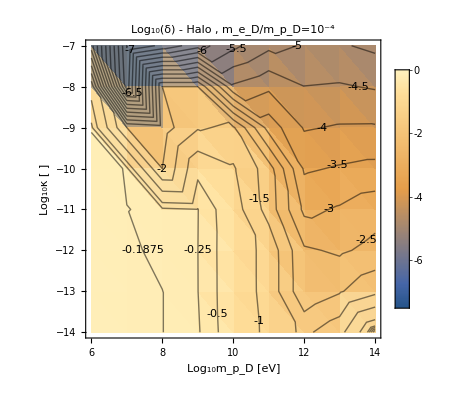

```mathematica
δtruthhalo = GetδTruth[computedδscanhalo10m4];
(*ListContourPlot[δtruth,ContourLabels->All]*)
Show[{ListDensityPlot[δtruthhalo,PlotLegends->Automatic,PlotLabel->"Log_10(δ) - Halo , m_e_D/m_p_D=10^-4",FrameLabel->{"Log_10m_p_D [eV]","Log_10κ [ ]"}],ListContourPlot[δtruthhalo,ContourLabels->All,ContourShading->False,Contours->Join[Table[i,{i,-0.25,0,0.0625}],Table[i,{i,-9,-0.5,0.5}]]],
ListContourPlot[δtruthhalo,Contours->{0},ContourStyle->Directive[Red,Thick],ContourLabels->True,ContourShading->None]}]
```

{{{6,-14,-13.4571},{6,-13,-11.4571},{6,-12,-9.45712},{6,-11,-7.45712},{6,-10,-5.45712},{6,-9,-3.45712},{6,-8,-1.45712},{6,-7,0.542884}},{{7,-14,-11.1282},{7,-13,-9.12823},{7,-12,-7.12823},{7,-11,-5.12823},{7,-10,-3.12823},{7,-9,-1.12823},{7,-8,0.871769},{7,-7,2.87177}},{{8,-14,-10.708},{8,-13,-8.70799},{8,-12,-6.70799},{8,-11,-4.70799},{8,-10,-2.70799},{8,-9,-0.707991},{8,-8,1.29201},{8,-7,3.29201}},{{9,-14,-11.2825},{9,-13,-9.28254},{9,-12,-7.28254},{9,-11,-5.28254},{9,-10,-3.28254},{9,-9,-1.28254},{9,-8,0.717465},{9,-7,2.71746}},{{10,-14,-12.0851},{10,-13,-10.0851},{10,-12,-8.08507},{10,-11,-6.08507},{10,-10,-4.08507},{10,-9,-2.08507},{10,-8,-0.0850675},{10,-7,1.91493}},{{11,-14,-13.0214},{11,-13,-11.0214},{11,-12,-9.02139},{11,-11,-7.02139},{11,-10,-5.02139},{11,-9,-3.02139},{11,-8,-1.02139},{11,-7,0.978606}},{{12,-14,-14.0149},{12,-13,-12.0149},{12,-12,-10.0149},{12,-11,-8.01495},{12,-10,-6.01495},{12,-9,-4.01495},{12,-8,-2.01495},{12,-7,-0.0149489}},{{13,-14,-15.0144},{13,-13,-13.0144},{13,-12,-11.0144},{13,-11,-9.01442},{13,-10,-7.01442},{13,-9,-5.01442},{13,-8,-3.01442},{13,-7,-1.01442}},{{14,-14,-16.0139},{14,-13,-14.0139},{14,-12,-12.0139},{14,-11,-10.0139},{14,-10,-8.01392},{14,-9,-6.01392},{14,-8,-4.01392},{14,-7,-2.01392}},{{15,-14,-17.0142},{15,-13,-15.0142},{15,-12,-13.0142},{15,-11,-11.0142},{15,-10,-9.01422},{15,-9,-7.01422},{15,-8,-5.01422},{15,-7,-3.01422}}}

Red contour is lower boundary of the thermalized regime (we expect > O(1) energy lost in the Earth for 99% of the incoming dark proton distribution)

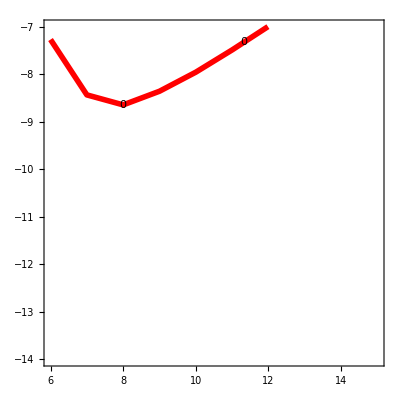

```mathematica
Eatvcuthalo=Table[
eind = FirstPosition["mχ"/.ElectronicσDicts,10^# ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]&@mind;
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^# ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]]&@mind;

mχt=10^mind ("JpereV")/("c")^2/.Constants`SIConstRepl;
βDdict=Capture`v0toβD[220 10^3,#,10^-4#]&[mχt];
(*βDdict={"βD"->6/((1+10^-4)mχt (20 10^3)^2)};*)
vχcut = Capture`GetvχMax[1-10^-2,(*"βcore"/.EarthRepl*)"βD"/.βDdict,mχt,0 "vesc"/.EarthRepl];
(*Print[vχcut];*)

Eofv[vχ_?NumberQ]:=("rE"/.Constants`EarthRepl)("dEdlofr"/.GetTotalELFunction[ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]]])[10^6,vχ]/((10^mind ("JpereV")/("c")^2/.Constants`SIConstRepl)vχ^2/2(*-3/("βcore")*)/.EarthRepl);
{mind,mlogκ,Log10[10^(2 mlogκ) Eofv[vχcut(*+"vesc"*)] /.EarthRepl]},{mind,6,15},{mlogκ,-14,-7}]
"Red contour is lower boundary of the thermalized regime (we expect > O(1) energy lost in the Earth for 99% of the incoming dark proton distribution)"
Show[{(*ListContourPlot[Flatten[Eatvcuthalo,1],ContourLabels->True,PlotLabel->"(<E>)/E_K 1st v percentile - Core Disk",FrameLabel->{"Log_10m_p_D [eV]","Log_10κ [ ]"}],*)ListContourPlot[Flatten[Eatvcuthalo,1],ContourLabels->True,Contours->{0},ContourStyle->Directive[Red,Thickness[0.01],Opacity[1]],ContourShading->False]}]
```

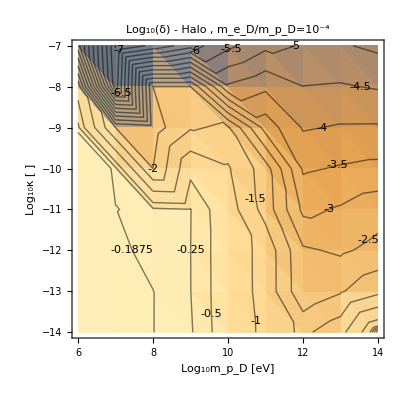
```mathematica
P1 = -Graphics-;
P2 = -Graphics-;
Show[{P1,P2}]
```

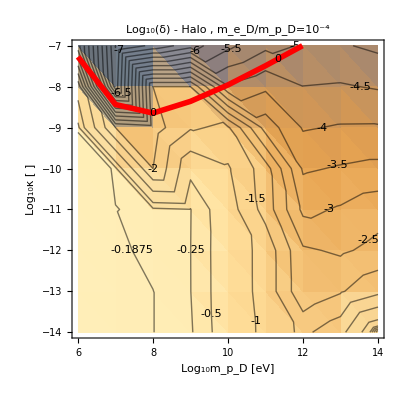

### Dark Protons - old

#### Scan over all masses

```mathematica
Clear[PDictScans]
PDictScans = {};
Monitor[Do[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
endind = FirstPosition["mχ"/.FeσDictend,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
PDictScan=ScanGetCapture[meDPoints,κpoints,v0Points,ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]],True,FeσDictend[[endind]],0];
AppendTo[PDictScans,PDictScan];
Clear[eind,Nucind,endind,PDictScan];
,{m,6,15}],{m,me,vs,κ,n}]
(*SaveIt[NotebookDirectory[]<>"PDictList",PDictScans];*)
SaveIt[NotebookDirectory[]<>"PDictList_w_nonzero_vE",PDictScans];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in l near {l} = {7.45297×10^6}. NIntegrate obtained 0.133176 and 0.00118417 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in l near {l} = {7.45297×10^6}. NIntegrate obtained 0.133199 and 0.00115701 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in l near {l} = {1.24189×10^7}. NIntegrate obtained 0.0671472 and 0.00104464 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Clear[PDictScans]
(*PDictScansMFP=ReadIt[NotebookDirectory[]<>"PDictList_Nuc_and_e_w_MFP"];*)
(*PDictScans=ReadIt[NotebookDirectory[]<>"PDictList_after_Vg_to_vesc"];*)PDictScans=ReadIt[NotebookDirectory[]<>"PDictList_w_nonzero_vE"];
```

```mathematica
PDictScans=ReadIt[NotebookDirectory[]<>"PDictList"];
```

```mathematica
PDictScanscomparison=ReadIt[NotebookDirectory[]<>"PDictList_nuc_vs_e"];
```

```mathematica
Dimensions@PDictScans
```

{10,32}

#### Scan over all masses - with variable ϕ

```mathematica
"Should wrap this in a module as well"
```

```mathematica
Clear[PDictScans]
PDictScans = {};
Monitor[Do[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
endind = FirstPosition["mχ"/.FeσDictend,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
PDictScan=ScanGetCapture[meDPoints,κpoints,v0Points,ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]],True,FeσDictend[[endind]],1.1];
AppendTo[PDictScans,PDictScan];
Clear[eind,Nucind,endind,PDictScan];
,{m,6,15}],{m,me,vs,κ,n}]
(*SaveIt[NotebookDirectory[]<>"PDictList_ϕE_90_pcnt",PDictScans];*)
(*SaveIt[NotebookDirectory[]<>"PDictList_ϕE_110_pcnt",PDictScans];*)

ExportToDir[PDictScans,"PDictList_ϕE_110_pcnt.dat","PDictList"];

KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];

PlotKEchangeκContour[KEDictList]
PlotNcκContour[KEDictList]
PlotEvaporationRateκContour[KEDictList]
PlotCaptureRateκContour[KEDictList]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

```mathematica
(*Clear[PDictScans]*)
(*PDictScansMFP=ReadIt[NotebookDirectory[]<>"PDictList_Nuc_and_e_w_MFP"];*)
(*PDictScans=ReadIt[NotebookDirectory[]<>"PDictList_after_Vg_to_vesc"];*)
PDictScansnoϕ=ReadIt[NotebookDirectory[]<>"PDictList_w_nonzero_vE"];
```

```mathematica
(*(*PDictScans=ReadIt[NotebookDirectory[]<>"PDictList"];*)
(*PDictScans=ReadIt[NotebookDirectory[]<>"PDictList_ϕE_0p0015"];*)
(*PDictScans=ReadIt[NotebookDirectory[]<>"PDictList_ϕE_0p15_before_fixes"];*)
PDictScans=ReadIt[NotebookDirectory[]<>"PDictList_ϕE_110_pcnt"];*)
```

```mathematica
(*PDictScanscomparison=ReadIt[NotebookDirectory[]<>"PDictList_nuc_vs_e"];*)
```

#### Rerun scans on existing PDicts

```mathematica
Clear[PDictScansTemp]
PDictScansTemp= {};
Block[{NuclearσDictsList,ElectronicσDictList,ElectronicEvapDict,pdicts,PDictind,Nucind,eind,endind,currentPDicts,Scandicts,analysiskeys,NcMaxdict,Ncdict,ScandictsKE},

NuclearσDictsList=NuclearσDicts;
(*NuclearσDictsList=NuclearσDictsnoFF;*)
ElectronicσDictList=ElectronicσDicts;
ElectronicEvapDict = FeσDictend;

pdicts = PDictScans;
(*pdicts = PDictScansMFP;*)
(*pdicts = PDictScansCopy;*)

pdicts = sortbymeDmpDv0[pdicts];

Monitor[
Do[
Print[p];
PDictind=FirstPosition["mpD"/.pdicts,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
currentPDicts = pdicts[[PDictind]];
Nucind = FirstPosition["mχ"/.NuclearσDictsList,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
eind = FirstPosition["mχ"/.ElectronicσDictList,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
endind = FirstPosition["mχ"/.ElectronicEvapDict,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
Scandicts={};
Do[
analysiskeys={{"Pf"},{"PfE"},{"PfNuc"},{"intλinvE"},{"intλinvNuc"}}[[1;;1]];

Ncdict = currentPDicts[[d]];
Do[
NcMaxdict =GetNcMax[Ncdict,analysiskeys[[k]]];
Ncdict=GetNc[NcMaxdict,NuclearσDictsList[[Nucind]],ElectronicσDictList[[Nucind]],ElectronicEvapDict[[endind]](*,analysiskeys[[k]],True*)];
,{k,Length[analysiskeys]}];

AppendTo[Scandicts,Ncdict];
,{d,Length[currentPDicts]}];

ScandictsKE=IterateKEchange[Flatten@Scandicts,{0.05},"α"/.Constants`SIConstRepl];

AppendTo[PDictScansTemp,ScandictsKE]

,{p,6,15}]
,p]
]
(*PDictScans=PDictScansTemp;
ClearAll[PDictScansTemp]*)

(*SaveIt[NotebookDirectory[]<>filenames[[p-5]],Scandicts]*)
```

6

$Aborted

```mathematica
(*SaveIt[NotebookDirectory[]<>"PDictList_nuc_vs_e",PDictScansTemp]*)
SaveIt[NotebookDirectory[]<>"PDictList",PDictScansTemp]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\PDictList_nuc_vs_e.dat

#### Get Scan Plots - post interpolation fix - with MFP evaporation - Nuc and e - No FF

```mathematica
KEDictListMFPnoFF = Table[IterateKEchange[Flatten@PDictScansTemp[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScansTemp]}];
```

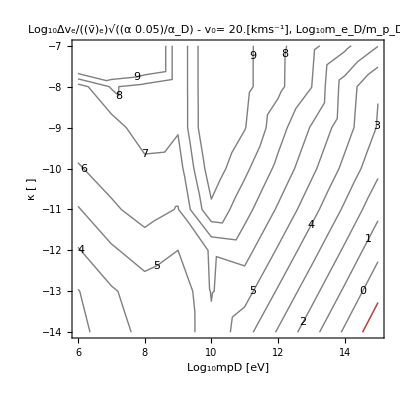

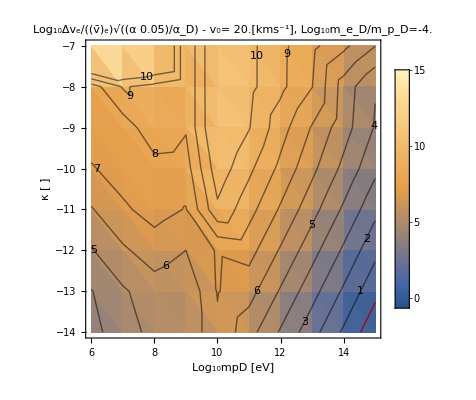

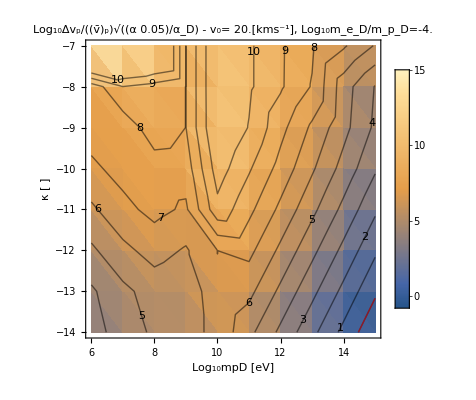

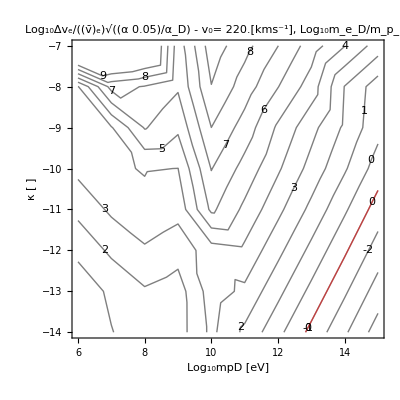

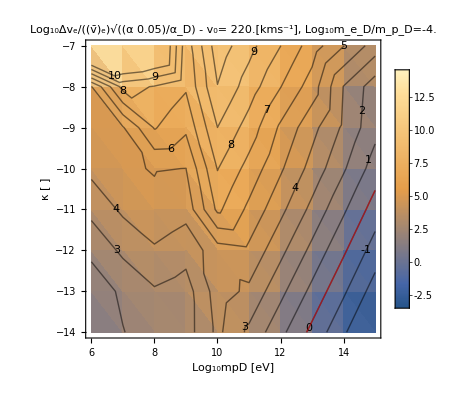

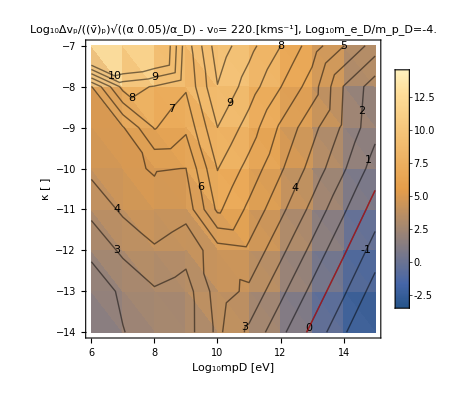

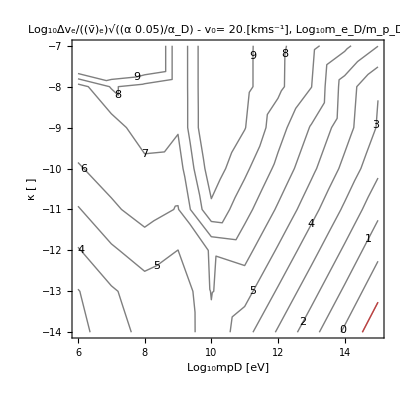

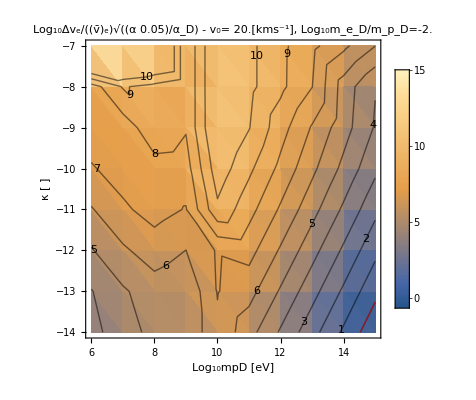

```mathematica
PlotKEchangeκContour[KEDictListMFPnoFF]
```

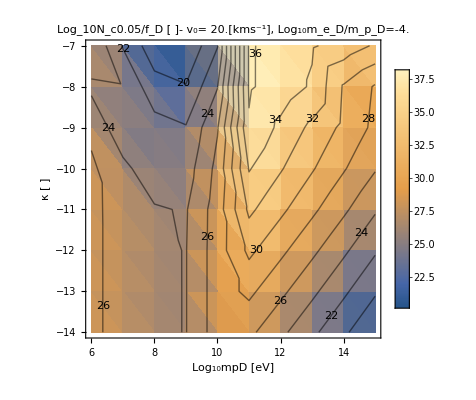

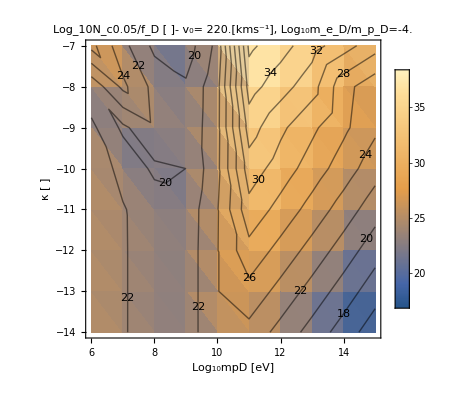

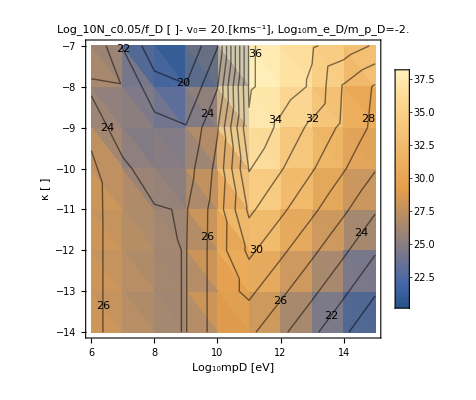

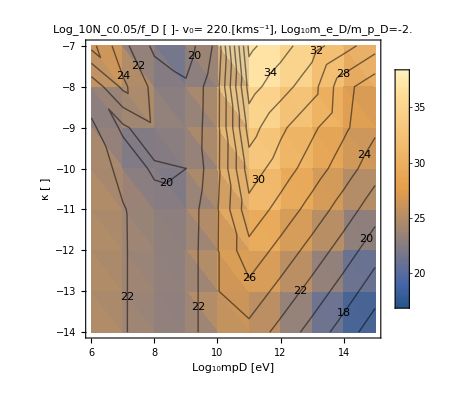

```mathematica
PlotNcκContour[KEDictListMFP]
```

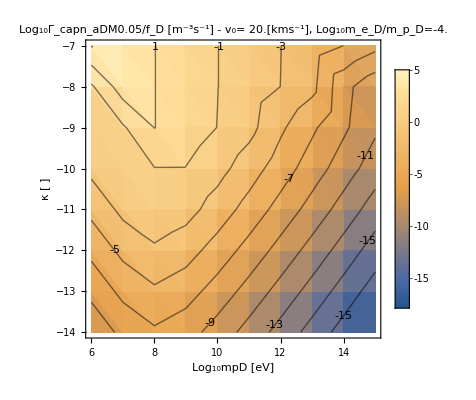

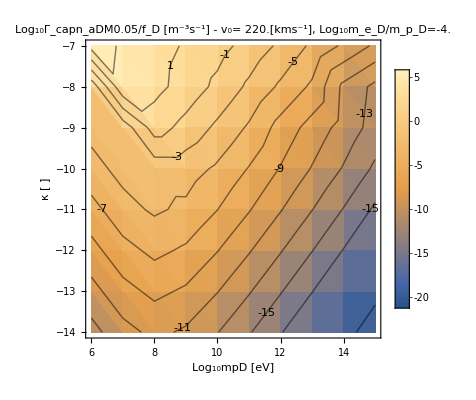

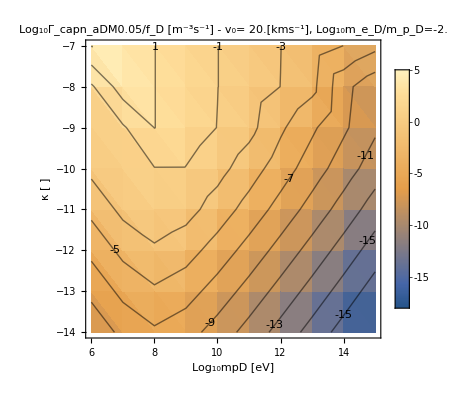

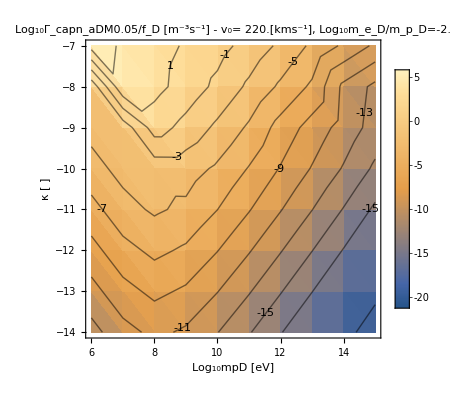

```mathematica
PlotCaptureRateκContour[KEDictListMFP]
```

I think the reason that the electronic evaporation rate drops off below 10^-10 κ is that at that point the MFP is less than the distance from the core to the surface. And since there is no electronic evaporation from the mantle, there is then no evaporation whatsoever. So I think this makes sense.

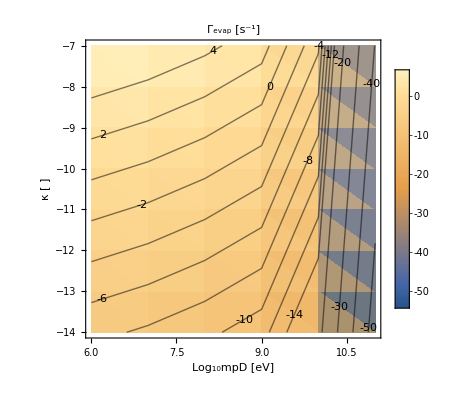

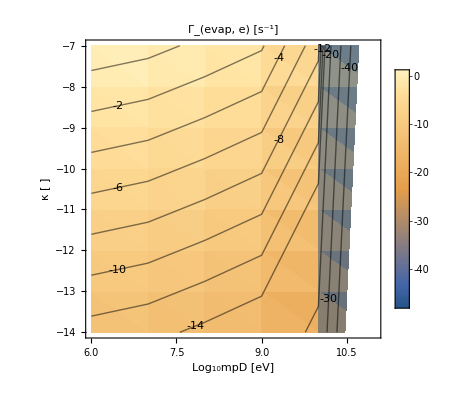

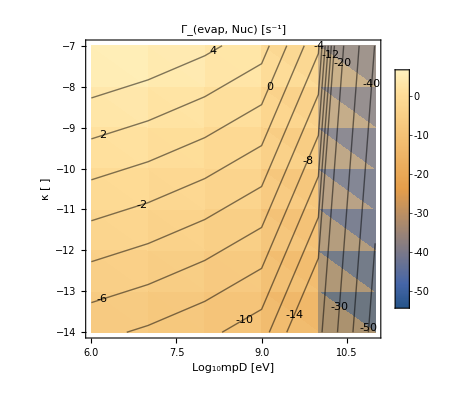

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
PlotEvaporationRateκContour[KEDictListMFPnoFF](*no MFP in evaporation, this shows that the change in rate is related to the evaporation volume. *)
```

The reason this cuts off, is that Γevap =0 above 10 GeV

```mathematica
"try computing the evaporation w MFP manually for fixed mass, say 10^6 eV. Comparing to the below plots should make it clear where the issue is. "
```

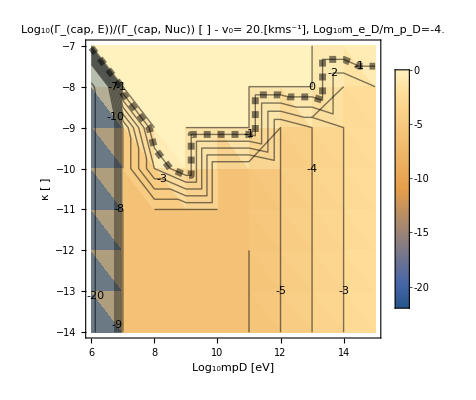

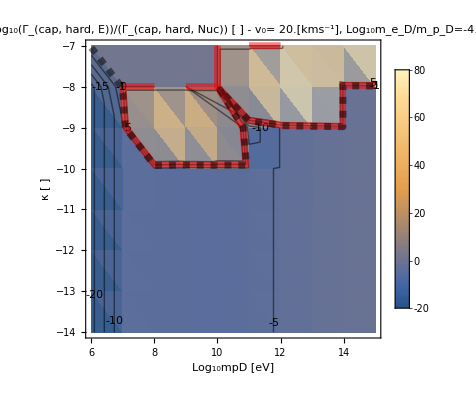

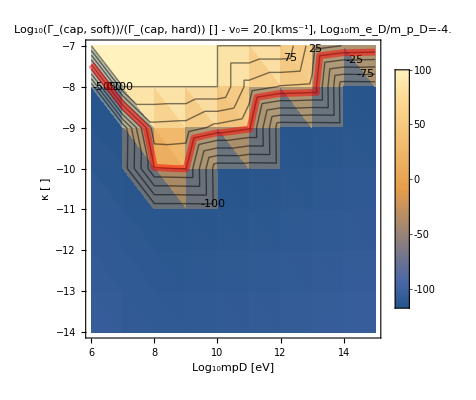

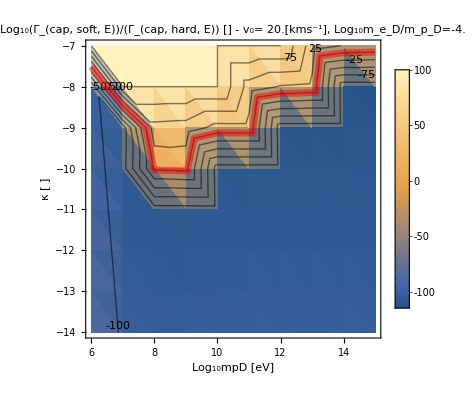

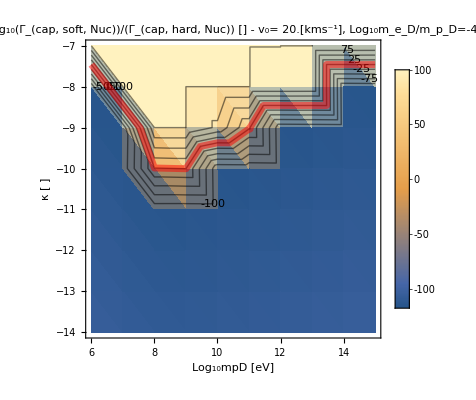

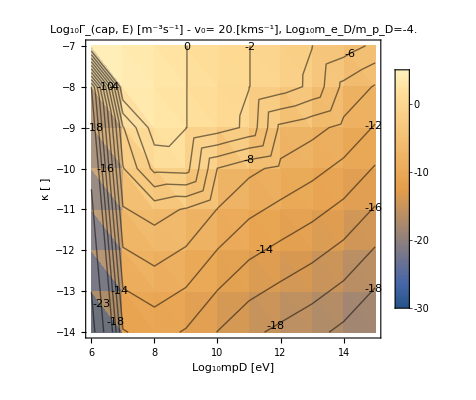

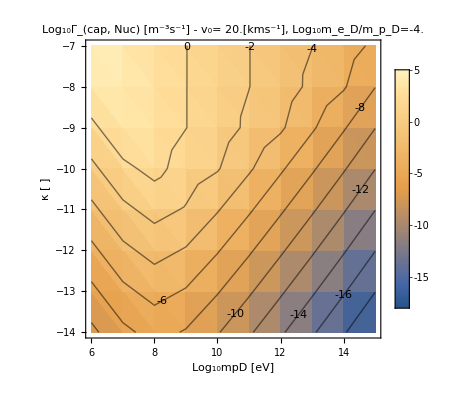

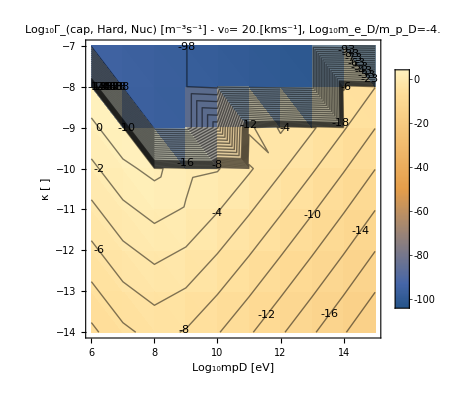

```mathematica
(*PlotCaptureRateComparison[PDictScansComparison]*)
PlotCaptureRateComparison[KEDictList]
```

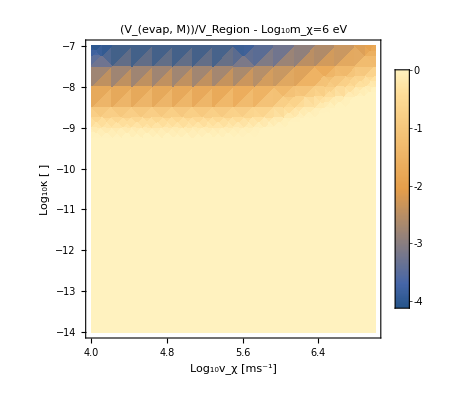

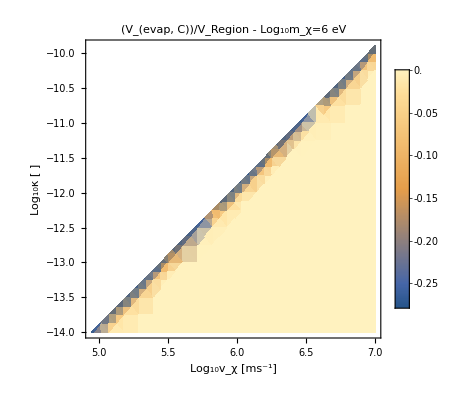

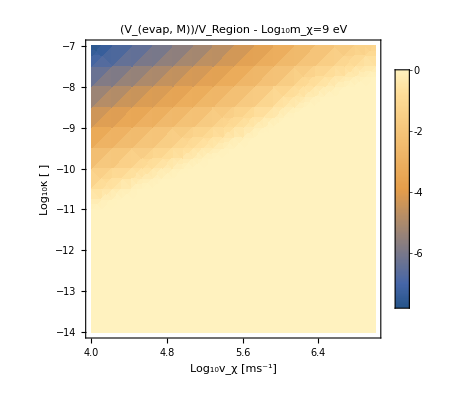

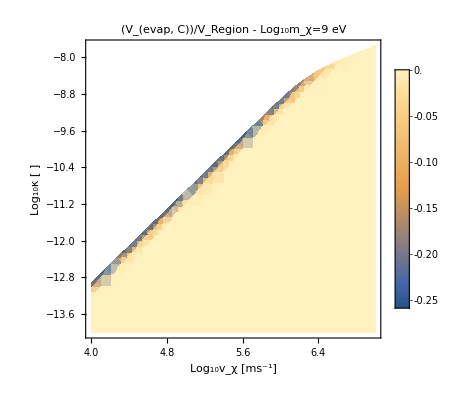

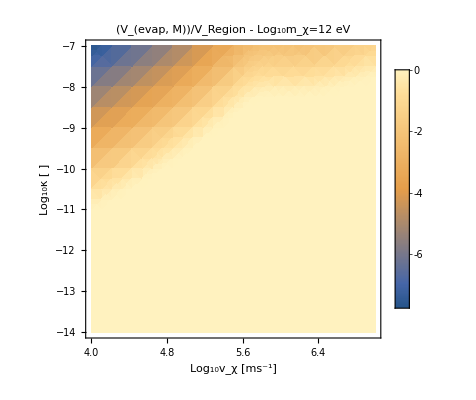

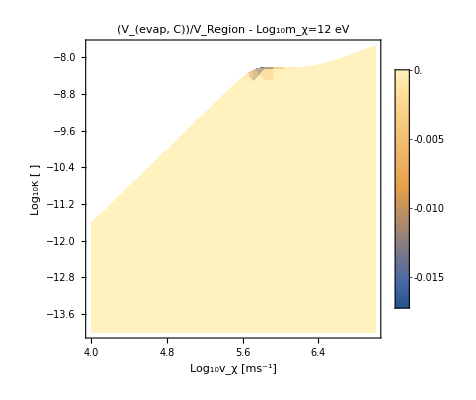

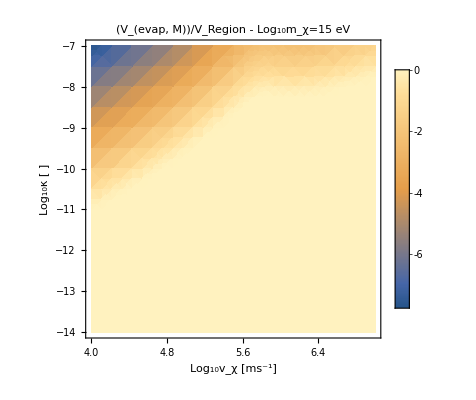

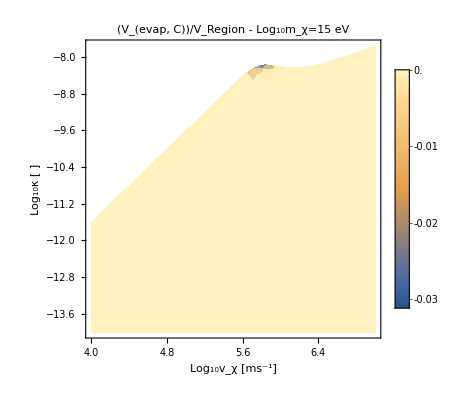

```mathematica
Do[
Print@DensityPlot[Log10@(1/((4π)/3(("rE")^3-("rcore")^3)/.EarthRepl)("Vevap"/.Function[{vχ,κ},EvaporationVolume[GetPenetrationDepthfnofv[vχ,ElectronicσDicts[[1+3m]],NuclearσDicts[[1+3m]]],κ,1]][10^Lvχ,10^Lκ])),{Lvχ,4,7},{Lκ,-14,-7},PlotRange->All,PlotLabel->"(V_(evap, M))/V_Region - Log_10m_χ="<>ToString[6+3 m]<>" eV",FrameLabel->{"Log_10v_χ [ms^-1]","Log_10κ [ ]"},PlotLegends->Automatic];

Print@DensityPlot[Log10@(1/((4π)/3("rcore")^3/.EarthRepl)("Vevap"/.Function[{vχ,κ},EvaporationVolume[GetPenetrationDepthfnofv[vχ,ElectronicσDicts[[1+3m]],NuclearσDictsnoFF[[1+3m]]],κ,2]][10^Lvχ,10^Lκ])),{Lvχ,4,7},{Lκ,-14,-7},PlotRange->All,PlotLabel->"(V_(evap, C))/V_Region - Log_10m_χ="<>ToString[6+3 m]<>" eV",FrameLabel->{"Log_10v_χ [ms^-1]","Log_10κ [ ]"},PlotLegends->Automatic],
{m,0,3}]
```

#### Get Scan Plots - full potential - w Volume evap Nuc and e - post capture fix

```mathematica
Dimensions@PDictScansTemp
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

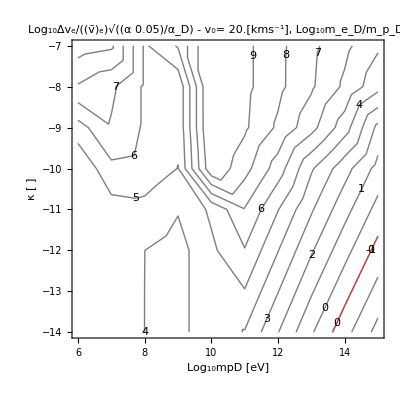

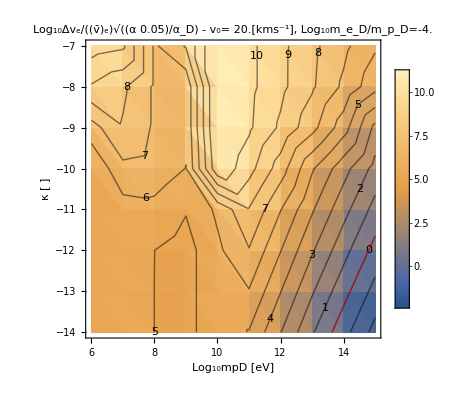

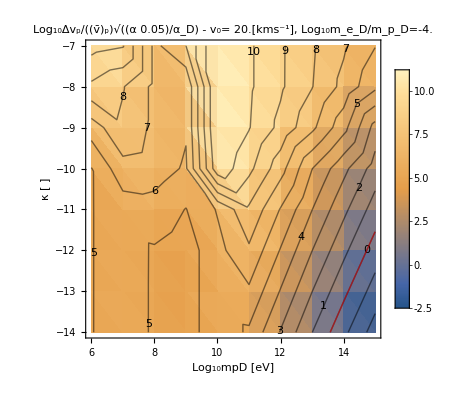

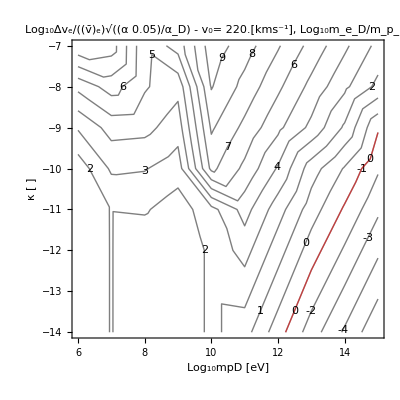

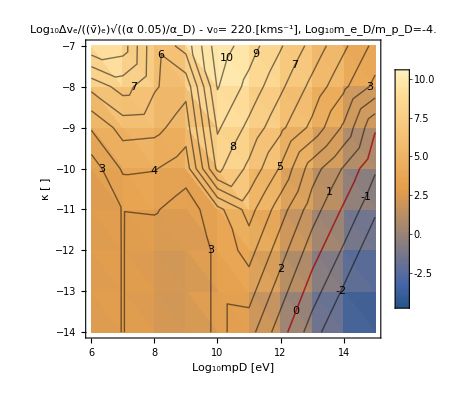

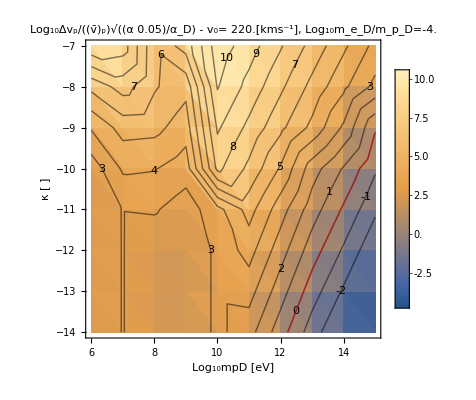

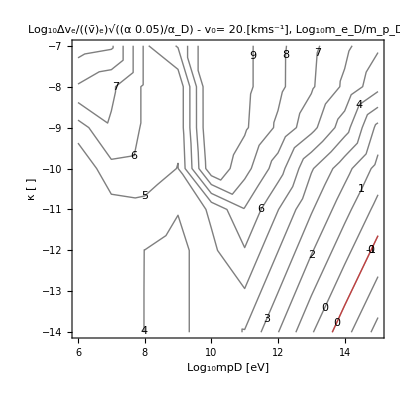

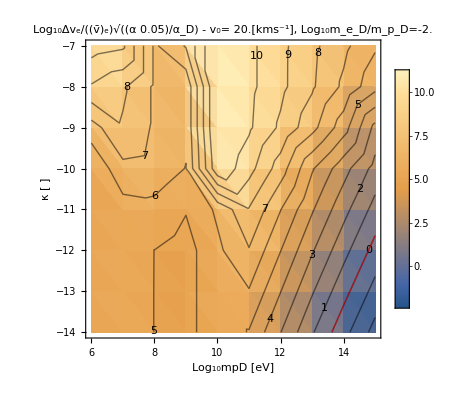

```mathematica
PlotKEchangeκContour[KEDictList]
```

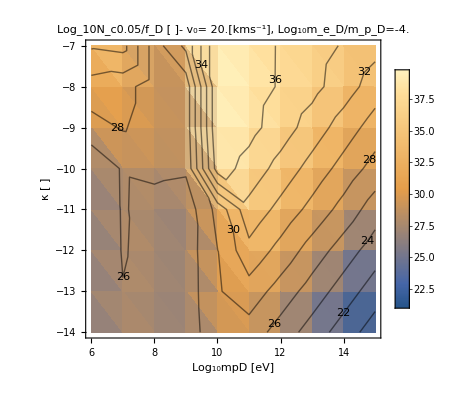

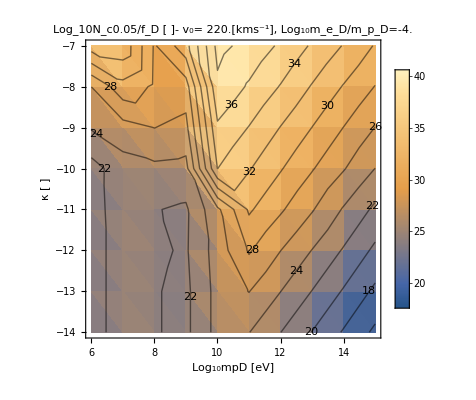

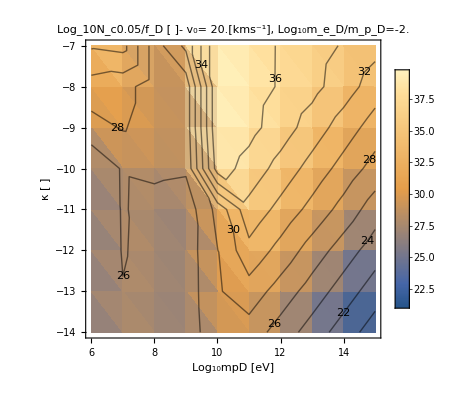

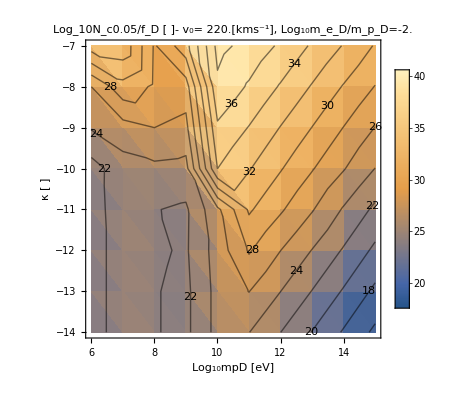

```mathematica
PlotNcκContour[KEDictList]
```

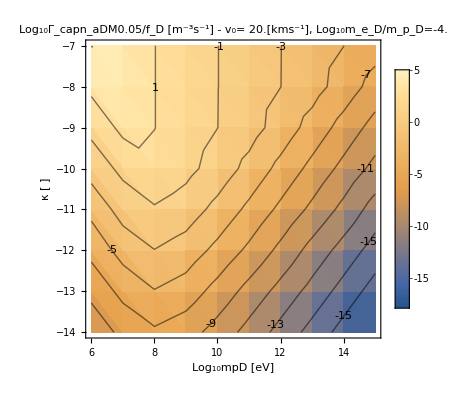

-Graphics-

-Graphics-

-Graphics-

```mathematica
PlotCaptureRateκContour[KEDictList]
```

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

#### Get Scan Plots - full potential - w Volume evap Nuc and e - ϕE=0.0015

```mathematica
Dimensions@PDictScansTemp
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

```mathematica
PlotKEchangeκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotCaptureRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

#### Get Scan Plots - full potential - w Volume evap Nuc and e - ϕE=0.15

```mathematica
Dimensions@PDictScansTemp
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

```mathematica
PlotKEchangeκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictList]
```

-Graphics-

-Graphics-

```mathematica
PlotCaptureRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

#### Get Scan Plots - full potential - w Volume evap Nuc and e - ϕEfrac=90%

```mathematica
Dimensions@PDictScansTemp
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

```mathematica
PlotKEchangeκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotCaptureRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

#### Get Scan Plots - full potential - w Volume evap Nuc and e - ϕEfrac=110% (w non-zero vE)

```mathematica
Dimensions@PDictScansTemp
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

```mathematica
PlotKEchangeκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotCaptureRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

```mathematica
"
Features to understand: 
1) why is capture falling off so much at large and small velocities again?
2) is evaporation correct for nuclear? (why no recapture shelf?)
3) why is electronic capture exactly 0?
4) why doesn't hard capture shut off at 0 velocity for vesc^2<0?
"
```

#### Get Scan Plots - full potential - w Volume evap Nuc and e - w comparison of Nuc vs e

```mathematica
Dimensions@PDictScans
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScanscomparison[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScanscomparison]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

```mathematica
PlotKEchangeκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotCaptureRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotCaptureRateComparison[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«41 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

#### Get Scan Plots - ϕE = 0, and non-zero vE

```mathematica
Dimensions@PDictScansTemp
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

```mathematica
"you can have no ionization by increasing binding energy, but as soon as you have any ionization you don't know how much you have because Astrophysics - David to Yoni";
```

```mathematica
PlotKEchangeκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotCaptureRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

#### Get Scan Plots - full potential - w Volume evap Nuc and e - ϕEfrac=110% (w non-zero vE) - post fix of capture rate

```mathematica
Dimensions@PDictScansTemp
```

{10,32}

```mathematica
KEDictList = Table[IterateKEchange[Flatten@PDictScans[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScans]}];
```

```mathematica
"why is there a factor of 10 discrepancy between the below two plots??? "
```

```mathematica
PlotKEchangeκContour[KEDictList]
```

```mathematica
PlotNcκContour[KEDictList]
```

```mathematica
PlotCaptureRateκContour[KEDictList]
```

```mathematica
PlotEvaporationRateκContour[KEDictList]
```

The reason this cuts off, is that Γevap =0 above 10 GeV

```mathematica
"
Features to understand: 
1) why is capture falling off so much at large and small velocities again?
2) is evaporation correct for nuclear? (why no recapture shelf?)
3) why is electronic capture exactly 0?
4) why doesn't hard capture shut off at 0 velocity for vesc^2<0?
"
```

```mathematica
ExportToDir[PDictScans,"PDictList_ϕE_110_pcnt.dat","PDictList"];
```

### Dark Electrons - not up to date, must be rerun

#### Interpolate over Electronic - Dark Electron sub MeV masses

```mathematica
FeσDicteeD=Monitor[Table[Table[InterpolatevχandωσdEReξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeTotalparams[[i]],10,60,10^-6,4,True,True,2,ToString[StringForm["Fe ``",i]],False],{i,Length[FeTotalparams]}],{m,2,5}],m];(*note that 10^2 is 0.1 keV which is in tension with MPS bounds*)
SaveIt[NotebookDirectory[]<>"FeσDicteeD",FeσDicteeD]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

minimum energy requires relativistic probes, we won't consider these

minimum energy requires relativistic probes, we won't consider these

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

minimum energy requires relativistic probes, we won't consider these

minimum energy requires relativistic probes, we won't consider these

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

minimum energy requires relativistic probes, we won't consider these

minimum energy requires relativistic probes, we won't consider these

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

minimum energy requires relativistic probes, we won't consider these

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDicteeD.dat

```mathematica
SiO2σDicteeD=Table[Table[InterpolatevχandωσdEReξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,SiO2Totalparams[[i]],10,60,10^-6,4,True,True,1,ToString[StringForm["SiO2 ``",i]],False],{i,Length[SiO2Totalparams]}],{m,2,5}];
SaveIt[NotebookDirectory[]<>"SiO2σDicteeD",SiO2σDicteeD]
```

minimum energy requires relativistic probes, we won't consider these

minimum energy requires relativistic probes, we won't consider these

minimum energy requires relativistic probes, we won't consider these

«1 more identical outputs»

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiO2σDicteeD.dat

```mathematica
MgOσDicteeD=Table[Table[InterpolatevχandωσdEReξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,MgOTotalparams[[i]],10,60,10^-6,4,True,True,1,ToString[StringForm["MgO ``",i]],False],{i,Length[MgOTotalparams]}],{m,2,5}];
SaveIt[NotebookDirectory[]<>"MgOσDicteeD",MgOσDicteeD]
```

minimum energy requires relativistic probes, we won't consider these

minimum energy requires relativistic probes, we won't consider these

minimum energy requires relativistic probes, we won't consider these

«1 more identical outputs»

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgOσDicteeD.dat

```mathematica
(*
FeσDicteeD=Delete[FeσDicteeD,-1];
SiO2σDicteeD=Delete[SiO2σDicteeD,-1];
MgOσDicteeD=Delete[MgOσDicteeD,-1];
SaveIt[NotebookDirectory[]<>"SiO2σDicteeD",SiO2σDicteeD]
SaveIt[NotebookDirectory[]<>"FeσDicteeD",FeσDicteeD]
SaveIt[NotebookDirectory[]<>"MgOσDicteeD",MgOσDicteeD]*)
```

```mathematica
FeσDicteeD=ReadIt[NotebookDirectory[]<>"FeσDicteeD"];
SiO2σDicteeD=ReadIt[NotebookDirectory[]<>"SiO2σDicteeD"];
MgOσDicteeD=ReadIt[NotebookDirectory[]<>"MgOσDicteeD"];
```

```mathematica
NADeleter=Delete[#,Position[#,"NA"]]&; (*For these light masses the minimal energy transfer*)
FeσDicteeD=NADeleter[FeσDicteeD];
MgOσDicteeD=NADeleter[MgOσDicteeD];
SiO2σDicteeD=NADeleter[SiO2σDicteeD];
```

```mathematica
ElectronicσDictseD=Gather[Flatten@Join[FeσDicteeD,SiO2σDicteeD,MgOσDicteeD],#1["mχ"]==#2["mχ"]&];
```

#### Interpolate over Nuclear - Dark Electron sub MeV masses

```mathematica
FeσDictNuceD=Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,FeNucCoeffs,2,"Fe Nuc"],{m,2,5}];
SaveIt[NotebookDirectory[]<>"FeσDictNuceD",FeσDictNuceD]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeσDictNuceD.dat

```mathematica
SiσDictNuceD=Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,SiNucCoeffs,1,"Si Nuc"],{m,2,5}];
SaveIt[NotebookDirectory[]<>"SiσDictNuceD",SiσDictNuceD]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\SiσDictNuceD.dat

```mathematica
MgσDictNuceD=Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,MgNucCoeffs,1,"Mg Nuc"],{m,2,5}];
SaveIt[NotebookDirectory[]<>"MgσDictNuceD",MgσDictNuceD]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\MgσDictNuceD.dat

```mathematica
OσDictNuceD=Table[InterpolatevχandωσdERNucξ[10^m ("JpereV")/("c")^2/.Constants`SIConstRepl,SiNucCoeffs,1,"O Nuc"],{m,2,5}];
SaveIt[NotebookDirectory[]<>"OσDictNuceD",OσDictNuceD]
```

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

dσ interpolation done

σ interpolation done

dEdlf interpolation done

σ of ξ interpolation done

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\OσDictNuceD.dat

```mathematica
FeσDictNuceD=ReadIt[NotebookDirectory[]<>"FeσDictNuceD"];
SiσDictNuceD=ReadIt[NotebookDirectory[]<>"SiσDictNuceD"];
MgσDictNuceD=ReadIt[NotebookDirectory[]<>"MgσDictNuceD"];
OσDictNuceD=ReadIt[NotebookDirectory[]<>"OσDictNuceD"];
```

```mathematica
NuclearσDictseD=Gather[Flatten@Join[{FeσDictNuceD},{SiσDictNuceD},{MgσDictNuceD},{OσDictNuceD}],#1["mχ"]==#2["mχ"]&];
```

#### Scan over all masses

```mathematica
Clear[PDictScanseD]
PDictScanseD = {};
Do[eind = FirstPosition["mχ"/.ElectronicσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDicts,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
PDictScaneD=ScanGetCapture[meDPoints,κpoints,v0Points,ElectronicσDicts[[eind]],NuclearσDicts[[Nucind]],False];
AppendTo[PDictScanseD,PDictScaneD];
SaveIt[NotebookDirectory[]<>"PDictListeD",PDictScanseD];(*save after each mass point - it will overwrite as you go.*)
Clear[eind,Nucind,PDictScaneD];
,{m,6,15}]
(*SaveIt[NotebookDirectory[]<>"PDictListeD",PDictScanseD];*)
```

mχ: 1.×10^6

mpD: 1.×10^10

v0: 20000

βD: 8.42612×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^10

v0: 220000

βD: 6.96374×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^10

v0: 20000

βD: 8.42612×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^8

v0: 220000

βD: 6.89548×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^7

mpD: 1.×10^11

v0: 20000

βD: 8.42612×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^11

v0: 220000

βD: 6.96374×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^11

v0: 20000

βD: 8.42612×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^9

v0: 220000

βD: 6.89548×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^8

mpD: 1.×10^12

v0: 20000

βD: 8.42612×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^12

v0: 220000

βD: 6.96374×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^12

v0: 20000

βD: 8.42612×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^10

v0: 220000

βD: 6.89548×10^15

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^9

mpD: 1.×10^13

v0: 20000

βD: 8.42612×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^13

v0: 220000

βD: 6.96374×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^13

v0: 20000

βD: 8.42612×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^11

v0: 220000

βD: 6.89548×10^14

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^10

mpD: 1.×10^14

v0: 20000

βD: 8.42612×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^14

v0: 220000

βD: 6.96374×10^11

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^14

v0: 20000

βD: 8.42612×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^12

v0: 220000

βD: 6.89548×10^13

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^11

mpD: 1.×10^15

v0: 20000

βD: 8.42612×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^15

v0: 220000

βD: 6.96374×10^10

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^15

v0: 20000

βD: 8.42612×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^13

v0: 220000

βD: 6.89548×10^12

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^12

mpD: 1.×10^16

v0: 20000

βD: 8.42612×10^11

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^16

v0: 220000

βD: 6.96374×10^9

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^16

v0: 20000

βD: 8.42612×10^11

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^14

v0: 220000

βD: 6.89548×10^11

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^13

mpD: 1.×10^17

v0: 20000

βD: 8.42612×10^10

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^17

v0: 220000

βD: 6.96374×10^8

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^17

v0: 20000

βD: 8.42612×10^10

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^15

v0: 220000

βD: 6.89548×10^10

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^14

mpD: 1.×10^18

v0: 20000

βD: 8.42612×10^9

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^18

v0: 220000

βD: 6.96374×10^7

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^18

v0: 20000

βD: 8.42612×10^9

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^16

v0: 220000

βD: 6.89548×10^9

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1.×10^15

mpD: 1.×10^19

v0: 20000

βD: 8.42612×10^8

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^19

v0: 220000

βD: 6.96374×10^6

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^19

v0: 20000

βD: 8.42612×10^8

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^17

v0: 220000

βD: 6.89548×10^8

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

```mathematica
PDictScanseD=ReadIt[NotebookDirectory[]<>"PDictListeD"];
```

```mathematica
SaveIt[NotebookDirectory[]<>"PDictListeD",PDictScanseD];
```

#### Scan over extended range of masses for dark electrons

```mathematica
Clear[PDictScanseDTemp]
PDictScanseDTemp = {};
Do[eind = FirstPosition["mχ"/.ElectronicσDictseD,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
Nucind = FirstPosition["mχ"/.NuclearσDictseD,10^m ("JpereV")/("c")^2/.Constants`SIConstRepl][[1]];
PDictScaneD=ScanGetCapture[meDPoints,κpoints,v0Points,ElectronicσDictseD[[eind]],NuclearσDictseD[[Nucind]],False];
AppendTo[PDictScanseDTemp,PDictScaneD];
SaveIt[NotebookDirectory[]<>"PDictListeDTemp",PDictScanseDTemp];(*save after each mass point - it will overwrite as you go.*)
Clear[eind,Nucind,PDictScaneD];
,{m,2,5}]
```

mχ: 100.

mpD: 1.×10^6

v0: 20000

βD: 8.42612×10^21

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^6

v0: 220000

βD: 6.96374×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^6

v0: 20000

βD: 8.42612×10^21

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 10000.

v0: 220000

βD: 6.89548×10^21

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 1000.

mpD: 1.×10^7

v0: 20000

βD: 8.42612×10^20

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^7

v0: 220000

βD: 6.96374×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^7

v0: 20000

βD: 8.42612×10^20

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 100000.

v0: 220000

βD: 6.89548×10^20

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 10000.

mpD: 1.×10^8

v0: 20000

βD: 8.42612×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^8

v0: 220000

βD: 6.96374×10^17

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^8

v0: 20000

βD: 8.42612×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^6

v0: 220000

βD: 6.89548×10^19

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mχ: 100000.

mpD: 1.×10^9

v0: 20000

βD: 8.42612×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^9

v0: 220000

βD: 6.96374×10^16

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^9

v0: 20000

βD: 8.42612×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

mpD: 1.×10^7

v0: 220000

βD: 6.89548×10^18

κ is: 1.×10^-14

κ is: 1.×10^-13

κ is: 1.×10^-12

κ is: 1.×10^-11

κ is: 1.×10^-10

κ is: 1.×10^-9

κ is: 1.×10^-8

κ is: 1.×10^-7

```mathematica
SaveIt[NotebookDirectory[]<>"PDictListeDTemp",PDictScanseDTemp];
```

```mathematica
Table[AppendTo[PDictScanseD,PDictScanseDTemp[[i]]],{i,3,Length[PDictScanseDTemp]}];
```

```mathematica
"mχ"("c")^2/("JpereV")/.PDictScanseD/.SIConstRepl
```

{{{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6}},{{1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7},{1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7},{1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7},{1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7}},{{1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8},{1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8},{1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8},{1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8}},{{1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9},{1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9},{1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9},{1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9}},{{1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10},{1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10},{1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10},{1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10}},{{1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11},{1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11},{1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11},{1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11}},{{1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12},{1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12},{1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12},{1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12}},{{1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13},{1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13},{1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13},{1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13}},{{1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14},{1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14},{1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14},{1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14}},{{1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15},{1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15},{1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15},{1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15}},{{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.},{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.},{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.},{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.}},{{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.},{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.},{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.},{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.}}}

#### Rerun Computations on Existing PDicts

Want to change this to a module that replaces existing analysis for PDicts

```mathematica
Clear[PDictScansTemp]
PDictScansTemp= {};
Block[{NuclearσDictsList,pdicts,PDictind,Nucind,currentPDicts,Scandicts,analysiskeys,NcMaxdict,Ncdict,ScandictsKE},

NuclearσDictsList=Join[NuclearσDicts,NuclearσDictseD];

pdicts = PDictScanseD;

Monitor[
Do[
Print[p];
PDictind=FirstPosition["mχ"/.pdicts,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
currentPDicts = pdicts[[PDictind]];
Nucind = FirstPosition["mχ"/.NuclearσDictsList,10^p ("JpereV"/("c")^2)/.Constants`SIConstRepl][[1]];
Scandicts={};
Do[
analysiskeys={{"Pf"},{"PfE"},{"PfNuc"},{"intλinvE"},{"intλinvNuc"}};

Ncdict = currentPDicts[[d]];
Do[
NcMaxdict =GetNcMax[Ncdict,analysiskeys[[k]]];
Ncdict=GetNc[NcMaxdict,NuclearσDictsList[[Nucind]],analysiskeys[[k]]];
,{k,Length[analysiskeys]}];

AppendTo[Scandicts,Ncdict];
,{d,Length[currentPDicts]}];

ScandictsKE=IterateKEchange[Flatten@Scandicts,{0.05},"α"/.Constants`SIConstRepl];

AppendTo[PDictScansTemp,ScandictsKE]

,{p,4,15}]
,p]
]
PDictScanseD=PDictScansTemp;
ClearAll[PDictScansTemp]

(*SaveIt[NotebookDirectory[]<>filenames[[p-5]],Scandicts]*)
```

4

5

6

7

8

9

10

11

12

13

14

15

```mathematica
"mχ"("c")^2/("JpereV")/.PDictScanseD/.SIConstRepl
```

{{1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6,1.×10^6},{1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7,1.×10^7},{1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8,1.×10^8},{1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9,1.×10^9},{1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10,1.×10^10},{1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11,1.×10^11},{1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12,1.×10^12},{1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13,1.×10^13},{1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14,1.×10^14},{1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15,1.×10^15},{{100.,100.,100.,100.,100.,100.,100.,100.},{100.,100.,100.,100.,100.,100.,100.,100.},{100.,100.,100.,100.,100.,100.,100.,100.},{100.,100.,100.,100.,100.,100.,100.,100.}},{{1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.},{1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.},{1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.},{1000.,1000.,1000.,1000.,1000.,1000.,1000.,1000.}},{{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.},{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.},{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.},{10000.,10000.,10000.,10000.,10000.,10000.,10000.,10000.}},{{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.},{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.},{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.},{100000.,100000.,100000.,100000.,100000.,100000.,100000.,100000.}}}

#### Get Scan Plots

```mathematica
KEDictListeD = Table[IterateKEchange[Flatten@PDictScanseD[[i]],{0.05},"α"/.Constants`SIConstRepl],{i,Length[PDictScanseD]}];
```

```mathematica
PlotKEchangeκContour[KEDictListeD]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictListeD]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotCaptureRateκContour[KEDictListeD]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictListeD]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

The reason this cuts off, is that Γevap =0 above 10 GeV

```mathematica
(*PlotCaptureRateComparison[PDictScansComparison]*)
PlotCaptureRateComparison[KEDictListeD]
```

-Graphics-

-Graphics-

-Graphics-

«41 more identical outputs»

#### Get Scan Plots - smaller range for GuineaPig

```mathematica
Dimensions[KEDictListeD]
```

{10,32}

```mathematica
PlotKEchangeκContour[KEDictList[[5;;]]]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotKEchangeκContour[KEDictListeD[[;;6]]]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

```mathematica
PlotNcκContour[KEDictListeD[[;;6]]]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
PlotEvaporationRateκContour[KEDictListeD[[;;6]]]
```

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

## Scrap

```mathematica
δDictDisk10m4=ReadIt["C:\\Users\\keega\\OneDrive\\Documents\\THEP\\aDM Capture\\notebooks\\AdM_capture\\aDM_git\\plasma\\"<>"δDictDisk10m4"]
Capture`ExportDatFileToDir[δDictDisk10m4,ToString@StringForm["δDict_``_aDbya_``_fD_``",1,2,3],"δDicts"]
```

<|path→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out/09_06_2025/δDicts/δDict_1_aDbya_2_fD_3_0,directory→C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\Out/09_06_2025/δDicts|>

```mathematica
?Capture`ExportDatFileToDir
```